```mathematica
ϕ1[x_]:= A1 Exp[ⅈ qb x]+B1 Exp[-ⅈ qb x]
ϕ2[x_]:= A2 Exp[ⅈ q x]+B2 Exp[-ⅈ q x]
ϕ3[x_]:= A3 Exp[ⅈ qb x]+B3 Exp[-ⅈ qb x]
Clear[k];

(* (A1, B1) = T1 . (A2, B2) *)
{ϕ1[0]==ϕ2[0],  ϕ1'[0]==ϕ2'[0]}//Solve[#,{A1,B1}]&
T12 = Table[D[{A1,B1}/.%[[1]],{coeff}],{coeff,{A2,B2}}]//Simplify

(* (A3, B3) = T2 . (A1, B1) *)
{ϕ3[2a]==ϕ1[0] Exp[2 ⅈ k a],  ϕ3'[2 a]==ϕ1'[0] Exp[2 ⅈ k a]}//Solve[#,{A3,B3}]&
T31 = Table[D[{A3,B3}/.%[[1]],{coeff}],{coeff,{A1,B1}}]//Simplify

(* (A2, B2) = T3 . (A3, B3) *)
{ϕ3[b]==ϕ2[b],  ϕ3'[b]==ϕ2'[b]}//Solve[#,{A2,B2}]&
T23 = Table[D[{A2,B2}/.%[[1]],{coeff}],{coeff,{A3,B3}}]//Simplify

T12.T23//FullSimplify

Re[%[[1,1]] Exp[ⅈ 2 q a]/.b->a]//ComplexExpand//Simplify
```

{{A1→-(-A2 q-A2 qb+B2 q-B2 qb)/(2 qb),B1→-(A2 q-A2 qb-B2 q-B2 qb)/(2 qb)}}

((q+qb)/(2 qb) | (qb-q)/(2 qb)
(qb-q)/(2 qb) | (q+qb)/(2 qb))

{{A3→A1 ⅇ^(2 ⅈ a k-2 ⅈ a qb),B3→B1 ⅇ^(2 ⅈ a k+2 ⅈ a qb)}}

(ⅇ^(2 ⅈ a (k-qb)) | 0
0 | ⅇ^(2 ⅈ a (k+qb)))

{{A2→(ⅇ^(-ⅈ b q-ⅈ b qb) (A3 q ⅇ^(2 ⅈ b qb)+A3 qb ⅇ^(2 ⅈ b qb)+B3 q-B3 qb))/(2 q),B2→(ⅇ^(ⅈ b q-ⅈ b qb) (A3 q ⅇ^(2 ⅈ b qb)-A3 qb ⅇ^(2 ⅈ b qb)+B3 q+B3 qb))/(2 q)}}

((ⅇ^(-ⅈ b (q-qb)) (q+qb))/(2 q) | (ⅇ^(ⅈ b (q+qb)) (q-qb))/(2 q)
(ⅇ^(-ⅈ b (q+qb)) (q-qb))/(2 q) | (ⅇ^(ⅈ b (q-qb)) (q+qb))/(2 q))

((ⅇ^(-ⅈ b (q-qb)) (q+qb)^2-ⅇ^(-ⅈ b (q+qb)) (q-qb)^2)/(4 q qb) | (ⅈ ⅇ^(ⅈ b q) (q-qb) (q+qb) sin(b qb))/(2 q qb)
(ⅇ^(-ⅈ b (q+qb)) (-1+ⅇ^(2 ⅈ b qb)) (qb-q) (q+qb))/(4 q qb) | (ⅇ^(ⅈ b (q-qb)) (q+qb)^2-ⅇ^(ⅈ b (q+qb)) (q-qb)^2)/(4 q qb))

cos(a q) cos(a qb)-((q^2+qb^2) sin(a q) sin(a qb))/(2 q qb)

```mathematica
T2.T1.T3//FullSimplify//ReplaceAll[#,{q->qb}]&//Eigenvalues
```

{ⅇ^(ⅈ a (k-qb)),ⅇ^(ⅈ a (k+qb))}

```mathematica
Eigenvalues[T1]
```

{q/qb,1}

```mathematica
(* (A3, B3) = T2 . (A1, B1) *)
{ϕ1[-w]==ϕ2[b] Exp[ ⅈ k a],  ϕ1'[-w]==ϕ2'[b] Exp[ ⅈ k a]}//Solve[#,{A1,B1}]&
T31 = Table[D[{A1,B1}/.%[[1]],{coeff}],{coeff,{A2,B2}}]//Simplify

{ϕ1[0]==ϕ2[0],  ϕ1'[0]==ϕ2'[0] }//Solve[#,{A1,B1}]&
T31 = Table[D[{A1,B1}/.%[[1]],{coeff}],{coeff,{A2,B2}}]//Simplify
```

{{A1→((A2 qb ⅇ^(2 ⅈ b q)+A2 q ⅇ^(2 ⅈ b q)-B2 q+B2 qb) ⅇ^(ⅈ a k-ⅈ b q+ⅈ qb w))/(2 qb),B1→((A2 qb ⅇ^(2 ⅈ b q)-A2 q ⅇ^(2 ⅈ b q)+B2 q+B2 qb) ⅇ^(ⅈ a k-ⅈ b q-ⅈ qb w))/(2 qb)}}

((ⅇ^(ⅈ (a k+b q+qb w)) (q+qb))/(2 qb) | (ⅇ^(ⅈ (a k+b q-qb w)) (qb-q))/(2 qb)
(ⅇ^(ⅈ (a k-b q+qb w)) (qb-q))/(2 qb) | (ⅇ^(ⅈ (a k-b q-qb w)) (q+qb))/(2 qb))

{{A1→-(-A2 q-A2 qb+B2 q-B2 qb)/(2 qb),B1→-(A2 q-A2 qb-B2 q-B2 qb)/(2 qb)}}

((q+qb)/(2 qb) | (qb-q)/(2 qb)
(qb-q)/(2 qb) | (q+qb)/(2 qb))

```mathematica
({{α, β}, {Conjugate[β], Conjugate[α]}})Exp[ⅈ q a]//Table[Tr[PauliMatrix[i].#]/2,{i,0,3}]&
```

{1/2 (ⅇ^(ⅈ a q) Conjugate[α]+α ⅇ^(ⅈ a q)),1/2 (ⅇ^(ⅈ a q) Conjugate[β]+β ⅇ^(ⅈ a q)),1/2 (ⅈ β ⅇ^(ⅈ a q)-ⅈ ⅇ^(ⅈ a q) Conjugate[β]),1/2 (α ⅇ^(ⅈ a q)-ⅇ^(ⅈ a q) Conjugate[α])}

```mathematica
Det[({{1, -α, 0, -β}, {0, -β, 1, -α}, {Exp[-ⅈ k a], -α Exp[ⅈ ϕ], 0, -β Exp[ⅈ ϕp]}, {0, -β Exp[-ⅈ ϕp], Exp[-ⅈ k a], -α Exp[-ⅈ ϕ]}})]//FullSimplify
```

-2 ⅇ^(-ⅈ a k) (α^2 (-cos(ϕ))+(α-β) (α+β) cos(a k)+β^2 cos(ϕp))

cos^-1((m sin(b q) sin(q w) (v1+v2-2 ϵ))/(2 √(m (ϵ-v1)) √(m (ϵ-v2)))+cos(b q) cos(q w))

cos^-1((m (v1+v2-2 ϵ) sin(√2 b √(m (ϵ-v1))) sin(√2 w √(m (ϵ-v1))))/(2 √(m (ϵ-v1)) √(m (ϵ-v2)))+cos(√2 b √(m (ϵ-v1))) cos(√2 w √(m (ϵ-v1))))

cos^-1(((-2 ϵ-7.) sin(0.141421 √(ϵ-2.)) sin(0.424264 √(ϵ-2.)))/(2 √(ϵ-2.) √(ϵ+9.))+cos(0.141421 √(ϵ-2.)) cos(0.424264 √(ϵ-2.)))

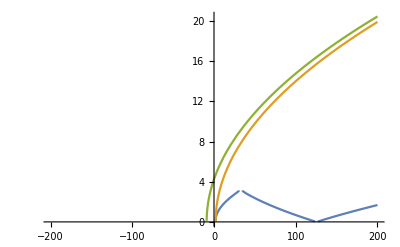

```mathematica
nsub = {m->1,v1->2.0,v2->-9.0,b->0.1,w->0.3};
k = ArcCos[((q+qp)^2 Cos[ϕ] - (q-qp)^2 Cos[ϕp])/(4 q qp)]/.{q->Sqrt[2m (ϵ-v1)],qp->Sqrt[2 m(ϵ-v2)], ϕ->q w+q b, ϕp->q w-q b}//Simplify
%/.{q->Sqrt[2m (ϵ-v1)],qp->Sqrt[2 m(ϵ-v2)], ϕ->q w+q' b, ϕp->q w-q' b}
sol1=%/.nsub
sol2 = Sqrt[2m (ϵ-v1)]/.nsub;
sol3 = Sqrt[2m (ϵ-v2)]/.nsub;
Plot[{sol1,sol2,sol3},{ϵ,-200,200}]
```

```mathematica
Off[Power::infy]
Off[Solve::ifun]
```

(1 | -1 | 1 | -1
ⅈ qb | -ⅈ q | -ⅈ qb | ⅈ q
ⅇ^(-ⅈ qb w) | -ⅇ^(ⅈ a k+ⅈ b q) | ⅇ^(ⅈ qb w) | -ⅇ^(ⅈ a k-ⅈ b q)
ⅈ ⅇ^(-ⅈ qb w) qb | -ⅈ ⅇ^(ⅈ a k+ⅈ b q) q | -ⅈ ⅇ^(ⅈ qb w) qb | ⅈ ⅇ^(ⅈ a k-ⅈ b q) q)

4 ⅇ^(ⅈ a k) (2 q qb (cos(a k)-cos(b q) cos(qb w))+(q^2+qb^2) sin(b q) sin(qb w))

{{k→-(cos^-1((q^2 (-sin(b q)) sin(qb w)-qb^2 sin(b q) sin(qb w)+2 q qb cos(b q) cos(qb w))/(2 q qb)))/a},{k→(cos^-1((q^2 (-sin(b q)) sin(qb w)-qb^2 sin(b q) sin(qb w)+2 q qb cos(b q) cos(qb w))/(2 q qb)))/a}}

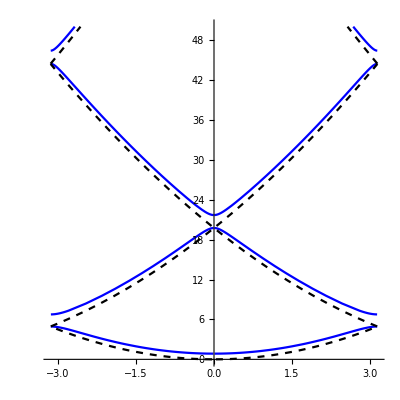

```mathematica
Clear[k]
CoefficientArrays[{ϕ1[0]-ϕ2[0] == 0, ϕ1'[0]-ϕ2'[0]==0,ϕ1[-w]-ϕ2[b]Exp[ⅈ k a]==0, ϕ1'[-w]-ϕ2'[b]Exp[ⅈ k a]==0},{A1,A2,B1,B2}][[2]]//Normal
Det[%]//FullSimplify
Solve[%==0,k]
ksol=k/.%;
nsub = {m->1,v1->100,v2->0,b->0.01,w->0.99,a->1};
ksol=ksol/.{q->Sqrt[2m (ϵ-v1)],qb->Sqrt[2 m(ϵ-v2)], ϕ->q w+q b, ϕp->q w-q b}/.nsub;
ksolp = ({Sqrt[2m (ϵ-v1)],Sqrt[2 m(ϵ-v2)]}/.nsub)//Mod[#+π,2π]-π&;
ksolpp = (-{Sqrt[2m (ϵ-v1)],Sqrt[2 m(ϵ-v2)]}/.nsub)//Mod[#+π,2π]-π&;

f[ϵ_]:=Join[ksol,ksolp,ksolpp]
ParametricPlot[Evaluate@Table[{g,ϵ},{g,f[ϵ]}],{ϵ,-5,50},PlotStyle->{Blue,Blue,{Black,Dashed},{Black,Dashed},{Black,Dashed},{Black,Dashed}},PlotRange->{{-π,π},Automatic},AspectRatio->1]
```

```mathematica
2 q qb (cos(a k)-cos(b q) cos(qb w))+(q^2+qb^2) sin(b q) sin(qb w)//StandardForm
```

2 q qb (Cos[a k]-Cos[b q] Cos[qb w])+(q^2+qb^2) Sin[b q] Sin[qb w]

```mathematica
Solve[2 q qb (Cos[a k]-Cos[b q] Cos[qb w])+(q^2+qb^2) Sin[b q] Sin[qb w]==0,Cos[a k]]//Simplify
```

{{cos(a k)→cos(b q) cos(qb w)-((q^2+qb^2) sin(b q) sin(qb w))/(2 q qb)}}

```mathematica
{ϕ1[-w]==ϕ2[b]Exp[ⅈ a k],  ϕ1'[-w]==ϕ2'[b] Exp[ⅈ a k] }//Solve[#,{A1,B1}]&
T31 = Table[D[{A1,B1}/.%[[1]],{coeff}],{coeff,{A2,B2}}]//Simplify
%//Eigenvalues//Simplify
```

{{A1→((A2 qb ⅇ^(2 ⅈ b q)+A2 q ⅇ^(2 ⅈ b q)-B2 q+B2 qb) ⅇ^(ⅈ a k-ⅈ b q+ⅈ qb w))/(2 qb),B1→((A2 qb ⅇ^(2 ⅈ b q)-A2 q ⅇ^(2 ⅈ b q)+B2 q+B2 qb) ⅇ^(ⅈ a k-ⅈ b q-ⅈ qb w))/(2 qb)}}

((ⅇ^(ⅈ (a k+b q+qb w)) (q+qb))/(2 qb) | (ⅇ^(ⅈ (a k+b q-qb w)) (qb-q))/(2 qb)
(ⅇ^(ⅈ (a k-b q+qb w)) (qb-q))/(2 qb) | (ⅇ^(ⅈ (a k-b q-qb w)) (q+qb))/(2 qb))

{((qb^3 ⅇ^(ⅈ (b q+qb w))+qb^3 ⅇ^(3 ⅈ (b q+qb w))+q qb^2 ⅇ^(ⅈ (b q+qb w))+q qb^2 ⅇ^(3 ⅈ (b q+qb w))-√(qb^4 (q+qb)^2 ⅇ^(2 ⅈ (b q+qb w)) (1+ⅇ^(2 ⅈ (b q+qb w)))^2-16 q qb^5 ⅇ^(4 ⅈ (b q+qb w)))) ⅇ^(ⅈ (a k-2 (b q+qb w))))/(4 qb^3),((qb^3 ⅇ^(ⅈ (b q+qb w))+qb^3 ⅇ^(3 ⅈ (b q+qb w))+q qb^2 ⅇ^(ⅈ (b q+qb w))+q qb^2 ⅇ^(3 ⅈ (b q+qb w))+√(qb^4 (q+qb)^2 ⅇ^(2 ⅈ (b q+qb w)) (1+ⅇ^(2 ⅈ (b q+qb w)))^2-16 q qb^5 ⅇ^(4 ⅈ (b q+qb w)))) ⅇ^(ⅈ (a k-2 (b q+qb w))))/(4 qb^3)}

```mathematica
Exp[ⅈ a k]({{α Exp[ⅈ ϕ], β Exp[ⅈ ϕp]}, {β Exp[-ⅈ ϕb], α Exp[-ⅈ ϕ]}})//Eigenvalues//FullSimplify
```

{1/2 ⅇ^(ⅈ (a k-ϕ-ϕb)) (α (1+ⅇ^(2 ⅈ ϕ)) ⅇ^(ⅈ ϕb)-√(α^2 (-1+ⅇ^(2 ⅈ ϕ))^2 ⅇ^(2 ⅈ ϕb)+4 β^2 ⅇ^(ⅈ (2 ϕ+ϕb+ϕp)))),1/2 ⅇ^(ⅈ (a k-ϕ-ϕb)) (√(α^2 (-1+ⅇ^(2 ⅈ ϕ))^2 ⅇ^(2 ⅈ ϕb)+4 β^2 ⅇ^(ⅈ (2 ϕ+ϕb+ϕp)))+α (1+ⅇ^(2 ⅈ ϕ)) ⅇ^(ⅈ ϕb))}

```mathematica
(Eigenvectors[-q^2/(2m)PauliMatrix[0]+l PauliMatrix[1]+ m PauliMatrix[3]]//Simplify[#,l l +m m ==1]&)
σp[l_] := {(m - 1)/l, 1}
σm[l_] :=  {(m + 1)/l, 1}
σp[l]
```

((m^2-√(m^2))/(l m) | 1
(m^2+√(m^2))/(l m) | 1)

{(m-1)/l,1}

(ϵ-Δ | Δ+ϵ
{-(m+1)/l,1} | {(1-m)/l,1})

```mathematica
ϕ1[x_]:= A1 Exp[ⅈ qp x] σp[l] + B1 Exp[-ⅈ qp x]σp[l] + C1 Exp[ⅈ qm x] σm[l] + D1 Exp[-ⅈ qm x]σm[l] 
ϕ2[x_]:= A2 Exp[ⅈ qp x] σp[-l] + B2 Exp[-ⅈ qp x]σp[-l] + C2 Exp[ⅈ qm x] σm[-l] + D2 Exp[-ⅈ qm x]σm[-l] 
ϕ3[x_]:= A3 Exp[ⅈ qp x] σp[l] + B3 Exp[-ⅈ qp x]σp[l] + C3 Exp[ⅈ qm x] σm[l] + D3 Exp[-ⅈ qm x]σm[l] 

(* (A1, B1) = T1 . (A2, B2) *)
{ϕ1[0]-ϕ2[0] == {0,0},  ϕ1'[0]-ϕ2'[0] == {0,0}}//Solve[#,{A1,B1,C1,D1}]&
T12 = Table[D[{A1,B1,C1,D1}/.%[[1]],{coeff}],{coeff,{A2,B2,C2,D2}}]//Simplify

(* (A2, B2) = T3 . (A3, B3) *)
{ϕ3[b]==ϕ2[b],  ϕ3'[b]==ϕ2'[b]}//Solve[#,{A2,B2,C2,D2}]&
T23 = Table[D[{A2,B2,C2,D2}/.%[[1]],{coeff}],{coeff,{A3,B3,C3,D3}}]//Simplify

T12.T23//FullSimplify

Re[%[[1,1]] /.b->a]//ComplexExpand//Simplify
```

{{C2→-(A2 σp(-l) (qm+qp) ⅇ^(ⅈ b qp-ⅈ b qm))/(2 qm σm(-l))+(ⅇ^(-ⅈ b qm-ⅈ b qp) (A3 qm ⅇ^(2 ⅈ b qp) σp(l)+A3 qp ⅇ^(2 ⅈ b qp) σp(l)+2 C3 qm σm(l) ⅇ^(ⅈ b qm+ⅈ b qp)+B3 qm σp(l)-B3 qp σp(l)))/(2 qm σm(-l))-(B2 σp(-l) (qm-qp) ⅇ^(-ⅈ b qm-ⅈ b qp))/(2 qm σm(-l)),D2→-(A2 σp(-l) (qm-qp) ⅇ^(ⅈ b qm+ⅈ b qp))/(2 qm σm(-l))+(ⅇ^(-ⅈ b qp) (A3 qm σp(l) ⅇ^(ⅈ b qm+2 ⅈ b qp)-A3 qp σp(l) ⅇ^(ⅈ b qm+2 ⅈ b qp)+B3 qp ⅇ^(ⅈ b qm) σp(l)+B3 qm ⅇ^(ⅈ b qm) σp(l)+2 D3 qm ⅇ^(ⅈ b qp) σm(l)))/(2 qm σm(-l))-(B2 σp(-l) (qm+qp) ⅇ^(ⅈ b qm-ⅈ b qp))/(2 qm σm(-l))}}

(0 | 0 | (ⅇ^(-ⅈ b (qm-qp)) (qm+qp) σp(l))/(2 qm σm(-l)) | (ⅇ^(ⅈ b (qm+qp)) (qm-qp) σp(l))/(2 qm σm(-l))
0 | 0 | (ⅇ^(-ⅈ b (qm+qp)) (qm-qp) σp(l))/(2 qm σm(-l)) | (ⅇ^(ⅈ b (qm-qp)) (qm+qp) σp(l))/(2 qm σm(-l))
0 | 0 | (σm(l))/(σm(-l)) | 0
0 | 0 | 0 | (σm(l))/(σm(-l)))

(0 | 0 | ((qm+qp) σp(-l))/(2 qm σm(-l)) | ((qm-qp) σp(-l))/(2 qm σm(-l))
0 | 0 | ((qm-qp) σp(-l))/(2 qm σm(-l)) | ((qm+qp) σp(-l))/(2 qm σm(-l))
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

0

{{A1→-(-2 A2 m qp-C2 m qm-C2 m qp-C2 qm-C2 qp+D2 m qm-D2 m qp+D2 qm-D2 qp)/(2 qp),B1→-(-2 B2 m qp+C2 m qm-C2 m qp+C2 qm-C2 qp-D2 m qm-D2 m qp-D2 qm-D2 qp)/(2 qp),C1→-(A2 m qm+A2 m qp-A2 qm-A2 qp+B2 m qm-B2 m qp-B2 qm+B2 qp+2 C2 m qm)/(2 qm),D1→-(A2 m qm-A2 m qp-A2 qm+A2 qp+B2 m qm+B2 m qp-B2 qm-B2 qp+2 D2 m qm)/(2 qm)}}

(m | 0 | -((m-1) (qm+qp))/(2 qm) | -((m-1) (qm-qp))/(2 qm)
0 | m | -((m-1) (qm-qp))/(2 qm) | -((m-1) (qm+qp))/(2 qm)
((m+1) (qm+qp))/(2 qp) | -((m+1) (qm-qp))/(2 qp) | -m | 0
-((m+1) (qm-qp))/(2 qp) | ((m+1) (qm+qp))/(2 qp) | 0 | -m)

{{A2→(ⅇ^(-ⅈ b qm-ⅈ b qp) (2 A3 m qp ⅇ^(ⅈ b qm+ⅈ b qp)+C3 m qp ⅇ^(2 ⅈ b qm)+C3 m qm ⅇ^(2 ⅈ b qm)+C3 qp ⅇ^(2 ⅈ b qm)+C3 qm ⅇ^(2 ⅈ b qm)-D3 m qm+D3 m qp-D3 qm+D3 qp))/(2 qp),B2→(ⅇ^(-ⅈ b qm) (2 B3 m qp ⅇ^(ⅈ b qm)-C3 m qm ⅇ^(2 ⅈ b qm+ⅈ b qp)+C3 m qp ⅇ^(2 ⅈ b qm+ⅈ b qp)-C3 qm ⅇ^(2 ⅈ b qm+ⅈ b qp)+C3 qp ⅇ^(2 ⅈ b qm+ⅈ b qp)+D3 m qm ⅇ^(ⅈ b qp)+D3 m qp ⅇ^(ⅈ b qp)+D3 qm ⅇ^(ⅈ b qp)+D3 qp ⅇ^(ⅈ b qp)))/(2 qp),C2→-(ⅇ^(-ⅈ b qm-ⅈ b qp) (A3 m qm ⅇ^(2 ⅈ b qp)+A3 m qp ⅇ^(2 ⅈ b qp)-A3 qm ⅇ^(2 ⅈ b qp)-A3 qp ⅇ^(2 ⅈ b qp)+2 C3 m qm ⅇ^(ⅈ b qm+ⅈ b qp)+B3 m qm-B3 m qp-B3 qm+B3 qp))/(2 qm),D2→-1/(2 qm)ⅇ^(-ⅈ b qp) (A3 m qm ⅇ^(ⅈ b qm+2 ⅈ b qp)-A3 m qp ⅇ^(ⅈ b qm+2 ⅈ b qp)-A3 qm ⅇ^(ⅈ b qm+2 ⅈ b qp)+A3 qp ⅇ^(ⅈ b qm+2 ⅈ b qp)+B3 m qp ⅇ^(ⅈ b qm)+B3 m qm ⅇ^(ⅈ b qm)-B3 qp ⅇ^(ⅈ b qm)-B3 qm ⅇ^(ⅈ b qm)+2 D3 m qm ⅇ^(ⅈ b qp))}}

(m | 0 | -(ⅇ^(-ⅈ b (qm-qp)) (m-1) (qm+qp))/(2 qm) | -(ⅇ^(ⅈ b (qm+qp)) (m-1) (qm-qp))/(2 qm)
0 | m | -(ⅇ^(-ⅈ b (qm+qp)) (m-1) (qm-qp))/(2 qm) | -(ⅇ^(ⅈ b (qm-qp)) (m-1) (qm+qp))/(2 qm)
(ⅇ^(ⅈ b (qm-qp)) (m+1) (qm+qp))/(2 qp) | (ⅇ^(ⅈ b (qm+qp)) (m+1) (qp-qm))/(2 qp) | -m | 0
(ⅇ^(-ⅈ b (qm+qp)) (m+1) (qp-qm))/(2 qp) | (ⅇ^(-ⅈ b (qm-qp)) (m+1) (qm+qp))/(2 qp) | 0 | -m)

((4 qm qp m^2+ⅇ^(-ⅈ b (qm+qp)) (m^2-1) (qm-qp)^2-ⅇ^(ⅈ b (qm-qp)) (m^2-1) (qm+qp)^2)/(4 qm qp) | (ⅈ ⅇ^(ⅈ b qp) (m-1) (m+1) (qm-qp) (qm+qp) sin(b qm))/(2 qm qp) | (ⅇ^(-ⅈ b (qm-qp)) (-1+ⅇ^(ⅈ b (qm-qp))) (m-1) m (qm+qp))/(2 qm) | -((-1+ⅇ^(ⅈ b (qm+qp))) (m-1) m (qm-qp))/(2 qm)
-(ⅇ^(-ⅈ b (qm+qp)) (-1+ⅇ^(2 ⅈ b qm)) (m-1) (m+1) (qm-qp) (qm+qp))/(4 qm qp) | (4 qm qp m^2+ⅇ^(ⅈ b (qm+qp)) (m^2-1) (qm-qp)^2-ⅇ^(-ⅈ b (qm-qp)) (m^2-1) (qm+qp)^2)/(4 qm qp) | (ⅇ^(-ⅈ b (qm+qp)) (-1+ⅇ^(ⅈ b (qm+qp))) (m-1) m (qm-qp))/(2 qm) | -((-1+ⅇ^(ⅈ b (qm-qp))) (m-1) m (qm+qp))/(2 qm)
-((-1+ⅇ^(ⅈ b (qm-qp))) m (m+1) (qm+qp))/(2 qp) | ((-1+ⅇ^(ⅈ b (qm+qp))) m (m+1) (qm-qp))/(2 qp) | (4 qm qp m^2+ⅇ^(-ⅈ b (qm+qp)) (m^2-1) (qm-qp)^2-ⅇ^(-ⅈ b (qm-qp)) (m^2-1) (qm+qp)^2)/(4 qm qp) | -(ⅈ ⅇ^(ⅈ b qm) (m^2-1) (qm-qp) (qm+qp) sin(b qp))/(2 qm qp)
(ⅇ^(-ⅈ b (qm+qp)) (-1+ⅇ^(ⅈ b (qm+qp))) m (m+1) (qp-qm))/(2 qp) | (ⅇ^(-ⅈ b (qm-qp)) (-1+ⅇ^(ⅈ b (qm-qp))) m (m+1) (qm+qp))/(2 qp) | (ⅇ^(-ⅈ b (qm+qp)) (-1+ⅇ^(2 ⅈ b qp)) (m-1) (m+1) (qm-qp) (qm+qp))/(4 qm qp) | (4 qm qp m^2+ⅇ^(ⅈ b (qm+qp)) (m^2-1) (qm-qp)^2-ⅇ^(ⅈ b (qm-qp)) (m^2-1) (qm+qp)^2)/(4 qm qp))

-((m^2-1) (qm^2+qp^2) sin(a qm) sin(a qp))/(2 qm qp)-(m^2-1) cos(a qm) cos(a qp)+m^2

```mathematica
%35//Series[#,{m,0,1}]&//Normal
```

((ⅇ^(ⅈ b (qm-qp)) (qm+qp)^2-ⅇ^(-ⅈ b (qm+qp)) (qm-qp)^2)/(4 qm qp) | -(ⅈ ⅇ^(ⅈ b qp) (qm-qp) (qm+qp) sin(b qm))/(2 qm qp) | -(ⅇ^(-ⅈ b (qm-qp)) (-1+ⅇ^(ⅈ b (qm-qp))) m (qm+qp))/(2 qm) | ((-1+ⅇ^(ⅈ b (qm+qp))) m (qm-qp))/(2 qm)
(ⅇ^(-ⅈ b (qm+qp)) (-1+ⅇ^(2 ⅈ b qm)) (qm-qp) (qm+qp))/(4 qm qp) | (ⅇ^(-ⅈ b (qm-qp)) (qm+qp)^2-ⅇ^(ⅈ b (qm+qp)) (qm-qp)^2)/(4 qm qp) | -(ⅇ^(-ⅈ b (qm+qp)) (-1+ⅇ^(ⅈ b (qm+qp))) m (qm-qp))/(2 qm) | ((-1+ⅇ^(ⅈ b (qm-qp))) m (qm+qp))/(2 qm)
-((-1+ⅇ^(ⅈ b (qm-qp))) m (qm+qp))/(2 qp) | ((-1+ⅇ^(ⅈ b (qm+qp))) m (qm-qp))/(2 qp) | (ⅇ^(-ⅈ b (qm-qp)) (qm+qp)^2-ⅇ^(-ⅈ b (qm+qp)) (qm-qp)^2)/(4 qm qp) | (ⅈ ⅇ^(ⅈ b qm) (qm-qp) (qm+qp) sin(b qp))/(2 qm qp)
(ⅇ^(-ⅈ b (qm+qp)) (-1+ⅇ^(ⅈ b (qm+qp))) m (qp-qm))/(2 qp) | (ⅇ^(-ⅈ b (qm-qp)) (-1+ⅇ^(ⅈ b (qm-qp))) m (qm+qp))/(2 qp) | -(ⅇ^(-ⅈ b (qm+qp)) (-1+ⅇ^(2 ⅈ b qp)) (qm-qp) (qm+qp))/(4 qm qp) | (ⅇ^(ⅈ b (qm-qp)) (qm+qp)^2-ⅇ^(ⅈ b (qm+qp)) (qm-qp)^2)/(4 qm qp))

```mathematica
%//Eigenvalues
```

{(ⅇ^(-4 ⅈ b (qm-qp)-6 ⅈ b (qm+qp)) Root[1470+1+#1^4&,1])/(4 qm^11 qp^11),(ⅇ^(1-1) Root[1&,2])/(4 qm^11 qp^11),(ⅇ^(1-1) Root[1])/(4 qm^11 qp^11),(ⅇ^(-4 ⅈ b (qm-qp)-6 ⅈ b (qm+qp)) Root[1471+#1^4&,4])/(4 qm^11 qp^11)}
 |  |  |  |

{1/(4 qm^11 qp^11)ⅇ^(-2 ⅈ b (5 qm+qp)) Root[ⅇ^(16 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) qp^40 qm^48-2 ⅇ^(15 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) qp^40 qm^48-2 ⅇ^(17 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) qp^40 qm^48+ⅇ^(14 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) qp^40 qm^48+4 ⅇ^(16 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) qp^40 qm^48+ⅇ^(18 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) qp^40 qm^48-2 ⅇ^(15 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) qp^40 qm^48-2 ⅇ^(17 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) qp^40 qm^48+ⅇ^(16 ⅈ b (qm-qp)+26 ⅈ b (qm+qp)) qp^40 qm^48+2 ⅈ ⅇ^(17 ⅈ b (qm-qp)+ⅈ b qp+22 ⅈ b (qm+qp)) qp^40 sin(b qm) qm^48-2 ⅈ ⅇ^(2 ⅈ b qm+17 ⅈ b (qm-qp)+ⅈ b qp+22 ⅈ b (qm+qp)) qp^40 sin(b qm) qm^48-4 ⅈ ⅇ^(16 ⅈ b (qm-qp)+ⅈ b qp+23 ⅈ b (qm+qp)) qp^40 sin(b qm) qm^48+4 ⅈ ⅇ^(2 ⅈ b qm+16 ⅈ b (qm-qp)+ⅈ b qp+23 ⅈ b (qm+qp)) qp^40 sin(b qm) qm^48+2 ⅈ ⅇ^(15 ⅈ b (qm-qp)+ⅈ b qp+24 ⅈ b (qm+qp)) qp^40 sin(b qm) qm^48-2 ⅈ ⅇ^(2 ⅈ b qm+15 ⅈ b (qm-qp)+ⅈ b qp+24 ⅈ b (qm+qp)) qp^40 sin(b qm) qm^48+2 ⅈ ⅇ^(ⅈ b qm+15 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) qp^40 sin(b qp) qm^48-2 ⅈ ⅇ^(ⅈ b qm+15 ⅈ b (qm-qp)+2 ⅈ b qp+22 ⅈ b (qm+qp)) qp^40 sin(b qp) qm^48-4 ⅈ ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) qp^40 sin(b qp) qm^48+4 ⅈ ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+2 ⅈ b qp+23 ⅈ b (qm+qp)) qp^40 sin(b qp) qm^48+2 ⅈ ⅇ^(ⅈ b qm+17 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) qp^40 sin(b qp) qm^48-2 ⅈ ⅇ^(ⅈ b qm+17 ⅈ b (qm-qp)+2 ⅈ b qp+24 ⅈ b (qm+qp)) qp^40 sin(b qp) qm^48-4 ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+ⅈ b qp+22 ⅈ b (qm+qp)) qp^40 sin(b qm) sin(b qp) qm^48+4 ⅇ^(3 ⅈ b qm+16 ⅈ b (qm-qp)+ⅈ b qp+22 ⅈ b (qm+qp)) qp^40 sin(b qm) sin(b qp) qm^48+4 ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+3 ⅈ b qp+22 ⅈ b (qm+qp)) qp^40 sin(b qm) sin(b qp) qm^48-4 ⅇ^(3 ⅈ b qm+16 ⅈ b (qm-qp)+3 ⅈ b qp+22 ⅈ b (qm+qp)) qp^40 sin(b qm) sin(b qp) qm^48-4 ⅇ^(15 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) m^2 qp^41 qm^47-4 ⅇ^(2 ⅈ b qm+15 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) m^2 qp^41 qm^47+4 ⅇ^(16 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) m^2 qp^41 qm^47-4 ⅇ^(17 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) m^2 qp^41 qm^47+4 ⅇ^(2 ⅈ b qm+16 ⅈ b (qm-qp)+2 ⅈ b qp+22 ⅈ b (qm+qp)) m^2 qp^41 qm^47-4 ⅇ^(17 ⅈ b (qm-qp)+2 ⅈ b qp+22 ⅈ b (qm+qp)) m^2 qp^41 qm^47+4 ⅇ^(14 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^41 qm^47+4 ⅇ^(2 ⅈ b qm+14 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^41 qm^47-4 ⅇ^(15 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^41 qm^47+24 ⅇ^(16 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^41 qm^47-4 ⅇ^(17 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^41 qm^47+4 ⅇ^(2 ⅈ b qm+17 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^41 qm^47+4 ⅇ^(18 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^41 qm^47+4 ⅇ^(15 ⅈ b (qm-qp)+2 ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^41 qm^47-8 ⅇ^(2 ⅈ b qm+16 ⅈ b (qm-qp)+2 ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^41 qm^47+4 ⅇ^(18 ⅈ b (qm-qp)+2 ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^41 qm^47-4 ⅇ^(14 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^41 qm^47-4 ⅇ^(2 ⅈ b qm+14 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^41 qm^47-20 ⅇ^(15 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^41 qm^47+8 ⅇ^(2 ⅈ b qm+15 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^41 qm^47+4 ⅇ^(16 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^41 qm^47-4 ⅇ^(2 ⅈ b qm+16 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^41 qm^47-20 ⅇ^(17 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^41 qm^47-4 ⅇ^(2 ⅈ b qm+17 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^41 qm^47-4 ⅇ^(18 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^41 qm^47-4 ⅇ^(15 ⅈ b (qm-qp)+2 ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^41 qm^47-4 ⅇ^(16 ⅈ b (qm-qp)+2 ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^41 qm^47+4 ⅇ^(2 ⅈ b qm+16 ⅈ b (qm-qp)+2 ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^41 qm^47+8 ⅇ^(17 ⅈ b (qm-qp)+2 ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^41 qm^47-4 ⅇ^(18 ⅈ b (qm-qp)+2 ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^41 qm^47+8 ⅇ^(14 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^41 qm^47+4 ⅇ^(15 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^41 qm^47-4 ⅇ^(2 ⅈ b qm+15 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^41 qm^47+8 ⅇ^(16 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^41 qm^47+4 ⅇ^(2 ⅈ b qm+16 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^41 qm^47+4 ⅇ^(17 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^41 qm^47+8 ⅇ^(18 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^41 qm^47+4 ⅇ^(16 ⅈ b (qm-qp)+2 ⅈ b qp+25 ⅈ b (qm+qp)) m^2 qp^41 qm^47-4 ⅇ^(17 ⅈ b (qm-qp)+2 ⅈ b qp+25 ⅈ b (qm+qp)) m^2 qp^41 qm^47-8 ⅇ^(15 ⅈ b (qm-qp)+26 ⅈ b (qm+qp)) m^2 qp^41 qm^47+8 ⅇ^(16 ⅈ b (qm-qp)+26 ⅈ b (qm+qp)) m^2 qp^41 qm^47-8 ⅇ^(17 ⅈ b (qm-qp)+26 ⅈ b (qm+qp)) m^2 qp^41 qm^47-8 ⅈ ⅇ^(16 ⅈ b (qm-qp)+ⅈ b qp+22 ⅈ b (qm+qp)) m^2 qp^41 sin(b qm) qm^47+8 ⅈ ⅇ^(17 ⅈ b (qm-qp)+ⅈ b qp+22 ⅈ b (qm+qp)) m^2 qp^41 sin(b qm) qm^47+8 ⅈ ⅇ^(15 ⅈ b (qm-qp)+ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^41 sin(b qm) qm^47-8 ⅈ ⅇ^(16 ⅈ b (qm-qp)+ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^41 sin(b qm) qm^47+8 ⅈ ⅇ^(16 ⅈ b (qm-qp)+3 ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^41 sin(b qm) qm^47-16 ⅈ ⅇ^(17 ⅈ b (qm-qp)+3 ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^41 sin(b qm) qm^47+8 ⅈ ⅇ^(18 ⅈ b (qm-qp)+3 ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^41 sin(b qm) qm^47-8 ⅈ ⅇ^(15 ⅈ b (qm-qp)+ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^41 sin(b qm) qm^47+16 ⅈ ⅇ^(16 ⅈ b (qm-qp)+ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^41 sin(b qm) qm^47-8 ⅈ ⅇ^(18 ⅈ b (qm-qp)+ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^41 sin(b qm) qm^47-8 ⅈ ⅇ^(16 ⅈ b (qm-qp)+ⅈ b qp+25 ⅈ b (qm+qp)) m^2 qp^41 sin(b qm) qm^47+8 ⅈ ⅇ^(17 ⅈ b (qm-qp)+ⅈ b qp+25 ⅈ b (qm+qp)) m^2 qp^41 sin(b qm) qm^47+8 ⅈ ⅇ^(ⅈ b qm+15 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) m^2 qp^41 sin(b qp) qm^47-8 ⅈ ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) m^2 qp^41 sin(b qp) qm^47+8 ⅈ ⅇ^(3 ⅈ b qm+14 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^41 sin(b qp) qm^47-16 ⅈ ⅇ^(3 ⅈ b qm+15 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^41 sin(b qp) qm^47-8 ⅈ ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^41 sin(b qp) qm^47+8 ⅈ ⅇ^(3 ⅈ b qm+16 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^41 sin(b qp) qm^47+8 ⅈ ⅇ^(ⅈ b qm+17 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^41 sin(b qp) qm^47-8 ⅈ ⅇ^(ⅈ b qm+14 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^41 sin(b qp) qm^47+16 ⅈ ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^41 sin(b qp) qm^47-8 ⅈ ⅇ^(ⅈ b qm+17 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^41 sin(b qp) qm^47+8 ⅈ ⅇ^(ⅈ b qm+15 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^41 sin(b qp) qm^47-8 ⅈ ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^41 sin(b qp) qm^47-16 ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+ⅈ b qp+22 ⅈ b (qm+qp)) m^2 qp^41 sin(b qm) sin(b qp) qm^47+32 ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^41 sin(b qm) sin(b qp) qm^47-16 ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^41 sin(b qm) sin(b qp) qm^47-4 ⅇ^(16 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) qp^42 qm^46-8 ⅇ^(15 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) qp^42 qm^46-8 ⅇ^(17 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) qp^42 qm^46-4 ⅇ^(14 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) qp^42 qm^46+48 ⅇ^(16 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) qp^42 qm^46-4 ⅇ^(18 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) qp^42 qm^46-8 ⅇ^(15 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) qp^42 qm^46-8 ⅇ^(17 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) qp^42 qm^46-4 ⅇ^(16 ⅈ b (qm-qp)+26 ⅈ b (qm+qp)) qp^42 qm^46+16 ⅇ^(16 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) m^4 qp^42 qm^46-32 ⅇ^(15 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^4 qp^42 qm^46-32 ⅇ^(17 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^4 qp^42 qm^46+16 ⅇ^(14 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^4 qp^42 qm^46+64 ⅇ^(16 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^4 qp^42 qm^46+16 ⅇ^(18 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^4 qp^42 qm^46-32 ⅇ^(15 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^4 qp^42 qm^46-32 ⅇ^(17 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^4 qp^42 qm^46+16 ⅇ^(16 ⅈ b (qm-qp)+26 ⅈ b (qm+qp)) m^4 qp^42 qm^46+8 ⅇ^(15 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) m^2 qp^42 qm^46+8 ⅇ^(2 ⅈ b qm+15 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) m^2 qp^42 qm^46-8 ⅇ^(16 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) m^2 qp^42 qm^46+8 ⅇ^(17 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) m^2 qp^42 qm^46-8 ⅇ^(2 ⅈ b qm+16 ⅈ b (qm-qp)+2 ⅈ b qp+22 ⅈ b (qm+qp)) m^2 qp^42 qm^46+8 ⅇ^(17 ⅈ b (qm-qp)+2 ⅈ b qp+22 ⅈ b (qm+qp)) m^2 qp^42 qm^46+8 ⅇ^(14 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^42 qm^46+8 ⅇ^(2 ⅈ b qm+14 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^42 qm^46-24 ⅇ^(15 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^42 qm^46-16 ⅇ^(2 ⅈ b qm+15 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^42 qm^46-16 ⅇ^(16 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^42 qm^46-16 ⅇ^(2 ⅈ b qm+16 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^42 qm^46-24 ⅇ^(17 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^42 qm^46+8 ⅇ^(2 ⅈ b qm+17 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^42 qm^46+8 ⅇ^(18 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^42 qm^46+8 ⅇ^(15 ⅈ b (qm-qp)+2 ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^42 qm^46-16 ⅇ^(16 ⅈ b (qm-qp)+2 ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^42 qm^46+16 ⅇ^(2 ⅈ b qm+16 ⅈ b (qm-qp)+2 ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^42 qm^46-16 ⅇ^(17 ⅈ b (qm-qp)+2 ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^42 qm^46+8 ⅇ^(18 ⅈ b (qm-qp)+2 ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^42 qm^46-8 ⅇ^(14 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^42 qm^46-8 ⅇ^(2 ⅈ b qm+14 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^42 qm^46-24 ⅇ^(15 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^42 qm^46+152 ⅇ^(16 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^42 qm^46+24 ⅇ^(2 ⅈ b qm+16 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^42 qm^46-24 ⅇ^(17 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^42 qm^46-8 ⅇ^(2 ⅈ b qm+17 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^42 qm^46-8 ⅇ^(18 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^42 qm^46-8 ⅇ^(15 ⅈ b (qm-qp)+2 ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^42 qm^46+24 ⅇ^(16 ⅈ b (qm-qp)+2 ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^42 qm^46-8 ⅇ^(2 ⅈ b qm+16 ⅈ b (qm-qp)+2 ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^42 qm^46-8 ⅇ^(18 ⅈ b (qm-qp)+2 ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^42 qm^46+16 ⅇ^(14 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^42 qm^46-40 ⅇ^(15 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^42 qm^46+8 ⅇ^(2 ⅈ b qm+15 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^42 qm^46-16 ⅇ^(16 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^42 qm^46-8 ⅇ^(2 ⅈ b qm+16 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^42 qm^46-40 ⅇ^(17 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^42 qm^46+16 ⅇ^(18 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^42 qm^46-8 ⅇ^(16 ⅈ b (qm-qp)+2 ⅈ b qp+25 ⅈ b (qm+qp)) m^2 qp^42 qm^46+8 ⅇ^(17 ⅈ b (qm-qp)+2 ⅈ b qp+25 ⅈ b (qm+qp)) m^2 qp^42 qm^46+16 ⅇ^(15 ⅈ b (qm-qp)+26 ⅈ b (qm+qp)) m^2 qp^42 qm^46-16 ⅇ^(16 ⅈ b (qm-qp)+26 ⅈ b (qm+qp)) m^2 qp^42 qm^46+16 ⅇ^(17 ⅈ b (qm-qp)+26 ⅈ b (qm+qp)) m^2 qp^42 qm^46-8 ⅈ ⅇ^(17 ⅈ b (qm-qp)+ⅈ b qp+22 ⅈ b (qm+qp)) qp^42 sin(b qm) qm^46+8 ⅈ ⅇ^(2 ⅈ b qm+17 ⅈ b (qm-qp)+ⅈ b qp+22 ⅈ b (qm+qp)) qp^42 sin(b qm) qm^46-16 ⅈ ⅇ^(16 ⅈ b (qm-qp)+ⅈ b qp+23 ⅈ b (qm+qp)) qp^42 sin(b qm) qm^46+16 ⅈ ⅇ^(2 ⅈ b qm+16 ⅈ b (qm-qp)+ⅈ b qp+23 ⅈ b (qm+qp)) qp^42 sin(b qm) qm^46-8 ⅈ ⅇ^(15 ⅈ b (qm-qp)+ⅈ b qp+24 ⅈ b (qm+qp)) qp^42 sin(b qm) qm^46+8 ⅈ ⅇ^(2 ⅈ b qm+15 ⅈ b (qm-qp)+ⅈ b qp+24 ⅈ b (qm+qp)) qp^42 sin(b qm) qm^46+16 ⅈ ⅇ^(16 ⅈ b (qm-qp)+ⅈ b qp+22 ⅈ b (qm+qp)) m^2 qp^42 sin(b qm) qm^46-16 ⅈ ⅇ^(17 ⅈ b (qm-qp)+ⅈ b qp+22 ⅈ b (qm+qp)) m^2 qp^42 sin(b qm) qm^46+16 ⅈ ⅇ^(15 ⅈ b (qm-qp)+ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^42 sin(b qm) qm^46-48 ⅈ ⅇ^(16 ⅈ b (qm-qp)+ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^42 sin(b qm) qm^46+32 ⅈ ⅇ^(17 ⅈ b (qm-qp)+ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^42 sin(b qm) qm^46+16 ⅈ ⅇ^(16 ⅈ b (qm-qp)+3 ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^42 sin(b qm) qm^46-32 ⅈ ⅇ^(17 ⅈ b (qm-qp)+3 ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^42 sin(b qm) qm^46+16 ⅈ ⅇ^(18 ⅈ b (qm-qp)+3 ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^42 sin(b qm) qm^46-16 ⅈ ⅇ^(15 ⅈ b (qm-qp)+ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^42 sin(b qm) qm^46+32 ⅈ ⅇ^(17 ⅈ b (qm-qp)+ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^42 sin(b qm) qm^46-16 ⅈ ⅇ^(18 ⅈ b (qm-qp)+ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^42 sin(b qm) qm^46+16 ⅈ ⅇ^(16 ⅈ b (qm-qp)+ⅈ b qp+25 ⅈ b (qm+qp)) m^2 qp^42 sin(b qm) qm^46-16 ⅈ ⅇ^(17 ⅈ b (qm-qp)+ⅈ b qp+25 ⅈ b (qm+qp)) m^2 qp^42 sin(b qm) qm^46-8 ⅈ ⅇ^(ⅈ b qm+15 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) qp^42 sin(b qp) qm^46+8 ⅈ ⅇ^(ⅈ b qm+15 ⅈ b (qm-qp)+2 ⅈ b qp+22 ⅈ b (qm+qp)) qp^42 sin(b qp) qm^46-16 ⅈ ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) qp^42 sin(b qp) qm^46+16 ⅈ ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+2 ⅈ b qp+23 ⅈ b (qm+qp)) qp^42 sin(b qp) qm^46-8 ⅈ ⅇ^(ⅈ b qm+17 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) qp^42 sin(b qp) qm^46+8 ⅈ ⅇ^(ⅈ b qm+17 ⅈ b (qm-qp)+2 ⅈ b qp+24 ⅈ b (qm+qp)) qp^42 sin(b qp) qm^46-16 ⅈ ⅇ^(ⅈ b qm+15 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) m^2 qp^42 sin(b qp) qm^46+16 ⅈ ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) m^2 qp^42 sin(b qp) qm^46+16 ⅈ ⅇ^(3 ⅈ b qm+14 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^42 sin(b qp) qm^46+32 ⅈ ⅇ^(ⅈ b qm+15 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^42 sin(b qp) qm^46-32 ⅈ ⅇ^(3 ⅈ b qm+15 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^42 sin(b qp) qm^46-48 ⅈ ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^42 sin(b qp) qm^46+16 ⅈ ⅇ^(3 ⅈ b qm+16 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^42 sin(b qp) qm^46+16 ⅈ ⅇ^(ⅈ b qm+17 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^42 sin(b qp) qm^46-16 ⅈ ⅇ^(ⅈ b qm+14 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^42 sin(b qp) qm^46+32 ⅈ ⅇ^(ⅈ b qm+15 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^42 sin(b qp) qm^46-16 ⅈ ⅇ^(ⅈ b qm+17 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^42 sin(b qp) qm^46-16 ⅈ ⅇ^(ⅈ b qm+15 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^42 sin(b qp) qm^46+16 ⅈ ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^42 sin(b qp) qm^46+16 ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+ⅈ b qp+22 ⅈ b (qm+qp)) qp^42 sin(b qm) sin(b qp) qm^46-16 ⅇ^(3 ⅈ b qm+16 ⅈ b (qm-qp)+ⅈ b qp+22 ⅈ b (qm+qp)) qp^42 sin(b qm) sin(b qp) qm^46-16 ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+3 ⅈ b qp+22 ⅈ b (qm+qp)) qp^42 sin(b qm) sin(b qp) qm^46+16 ⅇ^(3 ⅈ b qm+16 ⅈ b (qm-qp)+3 ⅈ b qp+22 ⅈ b (qm+qp)) qp^42 sin(b qm) sin(b qp) qm^46+32 ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+ⅈ b qp+22 ⅈ b (qm+qp)) m^2 qp^42 sin(b qm) sin(b qp) qm^46-64 ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^42 sin(b qm) sin(b qp) qm^46+32 ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^42 sin(b qm) sin(b qp) qm^46-64 ⅇ^(16 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) m^4 qp^43 qm^45+256 ⅇ^(16 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^4 qp^43 qm^45+64 ⅇ^(14 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^4 qp^43 qm^45-256 ⅇ^(15 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^4 qp^43 qm^45-256 ⅇ^(17 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^4 qp^43 qm^45+64 ⅇ^(18 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^4 qp^43 qm^45+256 ⅇ^(16 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^4 qp^43 qm^45-64 ⅇ^(16 ⅈ b (qm-qp)+26 ⅈ b (qm+qp)) m^4 qp^43 qm^45+4 ⅇ^(15 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) m^2 qp^43 qm^45+4 ⅇ^(2 ⅈ b qm+15 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) m^2 qp^43 qm^45-4 ⅇ^(16 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) m^2 qp^43 qm^45+4 ⅇ^(17 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) m^2 qp^43 qm^45-4 ⅇ^(2 ⅈ b qm+16 ⅈ b (qm-qp)+2 ⅈ b qp+22 ⅈ b (qm+qp)) m^2 qp^43 qm^45+4 ⅇ^(17 ⅈ b (qm-qp)+2 ⅈ b qp+22 ⅈ b (qm+qp)) m^2 qp^43 qm^45-4 ⅇ^(14 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^43 qm^45-4 ⅇ^(2 ⅈ b qm+14 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^43 qm^45+4 ⅇ^(15 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^43 qm^45+104 ⅇ^(16 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^43 qm^45+4 ⅇ^(17 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^43 qm^45-4 ⅇ^(2 ⅈ b qm+17 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^43 qm^45-4 ⅇ^(18 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^43 qm^45-4 ⅇ^(15 ⅈ b (qm-qp)+2 ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^43 qm^45+8 ⅇ^(2 ⅈ b qm+16 ⅈ b (qm-qp)+2 ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^43 qm^45-4 ⅇ^(18 ⅈ b (qm-qp)+2 ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^43 qm^45+4 ⅇ^(14 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^43 qm^45+4 ⅇ^(2 ⅈ b qm+14 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^43 qm^45-108 ⅇ^(15 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^43 qm^45-8 ⅇ^(2 ⅈ b qm+15 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^43 qm^45-4 ⅇ^(16 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^43 qm^45+4 ⅇ^(2 ⅈ b qm+16 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^43 qm^45-108 ⅇ^(17 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^43 qm^45+4 ⅇ^(2 ⅈ b qm+17 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^43 qm^45+4 ⅇ^(18 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^43 qm^45+4 ⅇ^(15 ⅈ b (qm-qp)+2 ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^43 qm^45+4 ⅇ^(16 ⅈ b (qm-qp)+2 ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^43 qm^45-4 ⅇ^(2 ⅈ b qm+16 ⅈ b (qm-qp)+2 ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^43 qm^45-8 ⅇ^(17 ⅈ b (qm-qp)+2 ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^43 qm^45+4 ⅇ^(18 ⅈ b (qm-qp)+2 ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^43 qm^45-8 ⅇ^(14 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^43 qm^45-4 ⅇ^(15 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^43 qm^45+4 ⅇ^(2 ⅈ b qm+15 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^43 qm^45+120 ⅇ^(16 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^43 qm^45-4 ⅇ^(2 ⅈ b qm+16 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^43 qm^45-4 ⅇ^(17 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^43 qm^45-8 ⅇ^(18 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^43 qm^45-4 ⅇ^(16 ⅈ b (qm-qp)+2 ⅈ b qp+25 ⅈ b (qm+qp)) m^2 qp^43 qm^45+4 ⅇ^(17 ⅈ b (qm-qp)+2 ⅈ b qp+25 ⅈ b (qm+qp)) m^2 qp^43 qm^45+8 ⅇ^(15 ⅈ b (qm-qp)+26 ⅈ b (qm+qp)) m^2 qp^43 qm^45-8 ⅇ^(16 ⅈ b (qm-qp)+26 ⅈ b (qm+qp)) m^2 qp^43 qm^45+8 ⅇ^(17 ⅈ b (qm-qp)+26 ⅈ b (qm+qp)) m^2 qp^43 qm^45+8 ⅈ ⅇ^(16 ⅈ b (qm-qp)+ⅈ b qp+22 ⅈ b (qm+qp)) m^2 qp^43 sin(b qm) qm^45-8 ⅈ ⅇ^(17 ⅈ b (qm-qp)+ⅈ b qp+22 ⅈ b (qm+qp)) m^2 qp^43 sin(b qm) qm^45-8 ⅈ ⅇ^(15 ⅈ b (qm-qp)+ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^43 sin(b qm) qm^45+8 ⅈ ⅇ^(16 ⅈ b (qm-qp)+ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^43 sin(b qm) qm^45-8 ⅈ ⅇ^(16 ⅈ b (qm-qp)+3 ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^43 sin(b qm) qm^45+16 ⅈ ⅇ^(17 ⅈ b (qm-qp)+3 ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^43 sin(b qm) qm^45-8 ⅈ ⅇ^(18 ⅈ b (qm-qp)+3 ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^43 sin(b qm) qm^45+8 ⅈ ⅇ^(15 ⅈ b (qm-qp)+ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^43 sin(b qm) qm^45-16 ⅈ ⅇ^(16 ⅈ b (qm-qp)+ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^43 sin(b qm) qm^45+8 ⅈ ⅇ^(18 ⅈ b (qm-qp)+ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^43 sin(b qm) qm^45+8 ⅈ ⅇ^(16 ⅈ b (qm-qp)+ⅈ b qp+25 ⅈ b (qm+qp)) m^2 qp^43 sin(b qm) qm^45-8 ⅈ ⅇ^(17 ⅈ b (qm-qp)+ⅈ b qp+25 ⅈ b (qm+qp)) m^2 qp^43 sin(b qm) qm^45-8 ⅈ ⅇ^(ⅈ b qm+15 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) m^2 qp^43 sin(b qp) qm^45+8 ⅈ ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) m^2 qp^43 sin(b qp) qm^45-8 ⅈ ⅇ^(3 ⅈ b qm+14 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^43 sin(b qp) qm^45+16 ⅈ ⅇ^(3 ⅈ b qm+15 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^43 sin(b qp) qm^45+8 ⅈ ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^43 sin(b qp) qm^45-8 ⅈ ⅇ^(3 ⅈ b qm+16 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^43 sin(b qp) qm^45-8 ⅈ ⅇ^(ⅈ b qm+17 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^43 sin(b qp) qm^45+8 ⅈ ⅇ^(ⅈ b qm+14 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^43 sin(b qp) qm^45-16 ⅈ ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^43 sin(b qp) qm^45+8 ⅈ ⅇ^(ⅈ b qm+17 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^43 sin(b qp) qm^45-8 ⅈ ⅇ^(ⅈ b qm+15 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^43 sin(b qp) qm^45+8 ⅈ ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^43 sin(b qp) qm^45+16 ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+ⅈ b qp+22 ⅈ b (qm+qp)) m^2 qp^43 sin(b qm) sin(b qp) qm^45-32 ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^43 sin(b qm) sin(b qp) qm^45+16 ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^43 sin(b qm) sin(b qp) qm^45+6 ⅇ^(16 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) qp^44 qm^44+20 ⅇ^(15 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) qp^44 qm^44+20 ⅇ^(17 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) qp^44 qm^44+6 ⅇ^(14 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) qp^44 qm^44+152 ⅇ^(16 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) qp^44 qm^44+6 ⅇ^(18 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) qp^44 qm^44+20 ⅇ^(15 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) qp^44 qm^44+20 ⅇ^(17 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) qp^44 qm^44+6 ⅇ^(16 ⅈ b (qm-qp)+26 ⅈ b (qm+qp)) qp^44 qm^44+96 ⅇ^(16 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) m^4 qp^44 qm^44+64 ⅇ^(15 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^4 qp^44 qm^44-512 ⅇ^(16 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^4 qp^44 qm^44+64 ⅇ^(17 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^4 qp^44 qm^44+96 ⅇ^(14 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^4 qp^44 qm^44-512 ⅇ^(15 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^4 qp^44 qm^44+1408 ⅇ^(16 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^4 qp^44 qm^44-512 ⅇ^(17 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^4 qp^44 qm^44+96 ⅇ^(18 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^4 qp^44 qm^44+64 ⅇ^(15 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^4 qp^44 qm^44-512 ⅇ^(16 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^4 qp^44 qm^44+64 ⅇ^(17 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^4 qp^44 qm^44+96 ⅇ^(16 ⅈ b (qm-qp)+26 ⅈ b (qm+qp)) m^4 qp^44 qm^44-16 ⅇ^(15 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) m^2 qp^44 qm^44-16 ⅇ^(2 ⅈ b qm+15 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) m^2 qp^44 qm^44+16 ⅇ^(16 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) m^2 qp^44 qm^44-16 ⅇ^(17 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) m^2 qp^44 qm^44+16 ⅇ^(2 ⅈ b qm+16 ⅈ b (qm-qp)+2 ⅈ b qp+22 ⅈ b (qm+qp)) m^2 qp^44 qm^44-16 ⅇ^(17 ⅈ b (qm-qp)+2 ⅈ b qp+22 ⅈ b (qm+qp)) m^2 qp^44 qm^44-16 ⅇ^(14 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^44 qm^44-16 ⅇ^(2 ⅈ b qm+14 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^44 qm^44+48 ⅇ^(15 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^44 qm^44+32 ⅇ^(2 ⅈ b qm+15 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^44 qm^44-224 ⅇ^(16 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^44 qm^44+32 ⅇ^(2 ⅈ b qm+16 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^44 qm^44+48 ⅇ^(17 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^44 qm^44-16 ⅇ^(2 ⅈ b qm+17 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^44 qm^44-16 ⅇ^(18 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^44 qm^44-16 ⅇ^(15 ⅈ b (qm-qp)+2 ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^44 qm^44+32 ⅇ^(16 ⅈ b (qm-qp)+2 ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^44 qm^44-32 ⅇ^(2 ⅈ b qm+16 ⅈ b (qm-qp)+2 ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^44 qm^44+32 ⅇ^(17 ⅈ b (qm-qp)+2 ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^44 qm^44-16 ⅇ^(18 ⅈ b (qm-qp)+2 ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^44 qm^44+16 ⅇ^(14 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^44 qm^44+16 ⅇ^(2 ⅈ b qm+14 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^44 qm^44-208 ⅇ^(15 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^44 qm^44+720 ⅇ^(16 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^44 qm^44-48 ⅇ^(2 ⅈ b qm+16 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^44 qm^44-208 ⅇ^(17 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^44 qm^44+16 ⅇ^(2 ⅈ b qm+17 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^44 qm^44+16 ⅇ^(18 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^44 qm^44+16 ⅇ^(15 ⅈ b (qm-qp)+2 ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^44 qm^44-48 ⅇ^(16 ⅈ b (qm-qp)+2 ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^44 qm^44+16 ⅇ^(2 ⅈ b qm+16 ⅈ b (qm-qp)+2 ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^44 qm^44+16 ⅇ^(18 ⅈ b (qm-qp)+2 ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^44 qm^44-32 ⅇ^(14 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^44 qm^44+80 ⅇ^(15 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^44 qm^44-16 ⅇ^(2 ⅈ b qm+15 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^44 qm^44-224 ⅇ^(16 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^44 qm^44+16 ⅇ^(2 ⅈ b qm+16 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^44 qm^44+80 ⅇ^(17 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^44 qm^44-32 ⅇ^(18 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^44 qm^44+16 ⅇ^(16 ⅈ b (qm-qp)+2 ⅈ b qp+25 ⅈ b (qm+qp)) m^2 qp^44 qm^44-16 ⅇ^(17 ⅈ b (qm-qp)+2 ⅈ b qp+25 ⅈ b (qm+qp)) m^2 qp^44 qm^44-32 ⅇ^(15 ⅈ b (qm-qp)+26 ⅈ b (qm+qp)) m^2 qp^44 qm^44+32 ⅇ^(16 ⅈ b (qm-qp)+26 ⅈ b (qm+qp)) m^2 qp^44 qm^44-32 ⅇ^(17 ⅈ b (qm-qp)+26 ⅈ b (qm+qp)) m^2 qp^44 qm^44+12 ⅈ ⅇ^(17 ⅈ b (qm-qp)+ⅈ b qp+22 ⅈ b (qm+qp)) qp^44 sin(b qm) qm^44-12 ⅈ ⅇ^(2 ⅈ b qm+17 ⅈ b (qm-qp)+ⅈ b qp+22 ⅈ b (qm+qp)) qp^44 sin(b qm) qm^44+40 ⅈ ⅇ^(16 ⅈ b (qm-qp)+ⅈ b qp+23 ⅈ b (qm+qp)) qp^44 sin(b qm) qm^44-40 ⅈ ⅇ^(2 ⅈ b qm+16 ⅈ b (qm-qp)+ⅈ b qp+23 ⅈ b (qm+qp)) qp^44 sin(b qm) qm^44+12 ⅈ ⅇ^(15 ⅈ b (qm-qp)+ⅈ b qp+24 ⅈ b (qm+qp)) qp^44 sin(b qm) qm^44-12 ⅈ ⅇ^(2 ⅈ b qm+15 ⅈ b (qm-qp)+ⅈ b qp+24 ⅈ b (qm+qp)) qp^44 sin(b qm) qm^44-32 ⅈ ⅇ^(16 ⅈ b (qm-qp)+ⅈ b qp+22 ⅈ b (qm+qp)) m^2 qp^44 sin(b qm) qm^44+32 ⅈ ⅇ^(17 ⅈ b (qm-qp)+ⅈ b qp+22 ⅈ b (qm+qp)) m^2 qp^44 sin(b qm) qm^44-32 ⅈ ⅇ^(15 ⅈ b (qm-qp)+ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^44 sin(b qm) qm^44+96 ⅈ ⅇ^(16 ⅈ b (qm-qp)+ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^44 sin(b qm) qm^44-64 ⅈ ⅇ^(17 ⅈ b (qm-qp)+ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^44 sin(b qm) qm^44-32 ⅈ ⅇ^(16 ⅈ b (qm-qp)+3 ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^44 sin(b qm) qm^44+64 ⅈ ⅇ^(17 ⅈ b (qm-qp)+3 ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^44 sin(b qm) qm^44-32 ⅈ ⅇ^(18 ⅈ b (qm-qp)+3 ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^44 sin(b qm) qm^44+32 ⅈ ⅇ^(15 ⅈ b (qm-qp)+ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^44 sin(b qm) qm^44-64 ⅈ ⅇ^(17 ⅈ b (qm-qp)+ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^44 sin(b qm) qm^44+32 ⅈ ⅇ^(18 ⅈ b (qm-qp)+ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^44 sin(b qm) qm^44-32 ⅈ ⅇ^(16 ⅈ b (qm-qp)+ⅈ b qp+25 ⅈ b (qm+qp)) m^2 qp^44 sin(b qm) qm^44+32 ⅈ ⅇ^(17 ⅈ b (qm-qp)+ⅈ b qp+25 ⅈ b (qm+qp)) m^2 qp^44 sin(b qm) qm^44+12 ⅈ ⅇ^(ⅈ b qm+15 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) qp^44 sin(b qp) qm^44-12 ⅈ ⅇ^(ⅈ b qm+15 ⅈ b (qm-qp)+2 ⅈ b qp+22 ⅈ b (qm+qp)) qp^44 sin(b qp) qm^44+40 ⅈ ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) qp^44 sin(b qp) qm^44-40 ⅈ ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+2 ⅈ b qp+23 ⅈ b (qm+qp)) qp^44 sin(b qp) qm^44+12 ⅈ ⅇ^(ⅈ b qm+17 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) qp^44 sin(b qp) qm^44-12 ⅈ ⅇ^(ⅈ b qm+17 ⅈ b (qm-qp)+2 ⅈ b qp+24 ⅈ b (qm+qp)) qp^44 sin(b qp) qm^44+32 ⅈ ⅇ^(ⅈ b qm+15 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) m^2 qp^44 sin(b qp) qm^44-32 ⅈ ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) m^2 qp^44 sin(b qp) qm^44-32 ⅈ ⅇ^(3 ⅈ b qm+14 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^44 sin(b qp) qm^44-64 ⅈ ⅇ^(ⅈ b qm+15 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^44 sin(b qp) qm^44+64 ⅈ ⅇ^(3 ⅈ b qm+15 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^44 sin(b qp) qm^44+96 ⅈ ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^44 sin(b qp) qm^44-32 ⅈ ⅇ^(3 ⅈ b qm+16 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^44 sin(b qp) qm^44-32 ⅈ ⅇ^(ⅈ b qm+17 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^44 sin(b qp) qm^44+32 ⅈ ⅇ^(ⅈ b qm+14 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^44 sin(b qp) qm^44-64 ⅈ ⅇ^(ⅈ b qm+15 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^44 sin(b qp) qm^44+32 ⅈ ⅇ^(ⅈ b qm+17 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^44 sin(b qp) qm^44+32 ⅈ ⅇ^(ⅈ b qm+15 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^44 sin(b qp) qm^44-32 ⅈ ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^44 sin(b qp) qm^44-24 ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+ⅈ b qp+22 ⅈ b (qm+qp)) qp^44 sin(b qm) sin(b qp) qm^44+24 ⅇ^(3 ⅈ b qm+16 ⅈ b (qm-qp)+ⅈ b qp+22 ⅈ b (qm+qp)) qp^44 sin(b qm) sin(b qp) qm^44+24 ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+3 ⅈ b qp+22 ⅈ b (qm+qp)) qp^44 sin(b qm) sin(b qp) qm^44-24 ⅇ^(3 ⅈ b qm+16 ⅈ b (qm-qp)+3 ⅈ b qp+22 ⅈ b (qm+qp)) qp^44 sin(b qm) sin(b qp) qm^44-64 ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+ⅈ b qp+22 ⅈ b (qm+qp)) m^2 qp^44 sin(b qm) sin(b qp) qm^44+128 ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^44 sin(b qm) sin(b qp) qm^44-64 ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^44 sin(b qm) sin(b qp) qm^44-64 ⅇ^(16 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) m^4 qp^45 qm^43+256 ⅇ^(16 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^4 qp^45 qm^43+64 ⅇ^(14 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^4 qp^45 qm^43-256 ⅇ^(15 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^4 qp^45 qm^43-256 ⅇ^(17 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^4 qp^45 qm^43+64 ⅇ^(18 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^4 qp^45 qm^43+256 ⅇ^(16 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^4 qp^45 qm^43-64 ⅇ^(16 ⅈ b (qm-qp)+26 ⅈ b (qm+qp)) m^4 qp^45 qm^43+4 ⅇ^(15 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) m^2 qp^45 qm^43+4 ⅇ^(2 ⅈ b qm+15 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) m^2 qp^45 qm^43-4 ⅇ^(16 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) m^2 qp^45 qm^43+4 ⅇ^(17 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) m^2 qp^45 qm^43-4 ⅇ^(2 ⅈ b qm+16 ⅈ b (qm-qp)+2 ⅈ b qp+22 ⅈ b (qm+qp)) m^2 qp^45 qm^43+4 ⅇ^(17 ⅈ b (qm-qp)+2 ⅈ b qp+22 ⅈ b (qm+qp)) m^2 qp^45 qm^43-4 ⅇ^(14 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^45 qm^43-4 ⅇ^(2 ⅈ b qm+14 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^45 qm^43+4 ⅇ^(15 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^45 qm^43+104 ⅇ^(16 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^45 qm^43+4 ⅇ^(17 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^45 qm^43-4 ⅇ^(2 ⅈ b qm+17 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^45 qm^43-4 ⅇ^(18 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^45 qm^43-4 ⅇ^(15 ⅈ b (qm-qp)+2 ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^45 qm^43+8 ⅇ^(2 ⅈ b qm+16 ⅈ b (qm-qp)+2 ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^45 qm^43-4 ⅇ^(18 ⅈ b (qm-qp)+2 ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^45 qm^43+4 ⅇ^(14 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^45 qm^43+4 ⅇ^(2 ⅈ b qm+14 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^45 qm^43-108 ⅇ^(15 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^45 qm^43-8 ⅇ^(2 ⅈ b qm+15 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^45 qm^43-4 ⅇ^(16 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^45 qm^43+4 ⅇ^(2 ⅈ b qm+16 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^45 qm^43-108 ⅇ^(17 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^45 qm^43+4 ⅇ^(2 ⅈ b qm+17 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^45 qm^43+4 ⅇ^(18 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^45 qm^43+4 ⅇ^(15 ⅈ b (qm-qp)+2 ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^45 qm^43+4 ⅇ^(16 ⅈ b (qm-qp)+2 ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^45 qm^43-4 ⅇ^(2 ⅈ b qm+16 ⅈ b (qm-qp)+2 ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^45 qm^43-8 ⅇ^(17 ⅈ b (qm-qp)+2 ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^45 qm^43+4 ⅇ^(18 ⅈ b (qm-qp)+2 ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^45 qm^43-8 ⅇ^(14 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^45 qm^43-4 ⅇ^(15 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^45 qm^43+4 ⅇ^(2 ⅈ b qm+15 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^45 qm^43+120 ⅇ^(16 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^45 qm^43-4 ⅇ^(2 ⅈ b qm+16 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^45 qm^43-4 ⅇ^(17 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^45 qm^43-8 ⅇ^(18 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^45 qm^43-4 ⅇ^(16 ⅈ b (qm-qp)+2 ⅈ b qp+25 ⅈ b (qm+qp)) m^2 qp^45 qm^43+4 ⅇ^(17 ⅈ b (qm-qp)+2 ⅈ b qp+25 ⅈ b (qm+qp)) m^2 qp^45 qm^43+8 ⅇ^(15 ⅈ b (qm-qp)+26 ⅈ b (qm+qp)) m^2 qp^45 qm^43-8 ⅇ^(16 ⅈ b (qm-qp)+26 ⅈ b (qm+qp)) m^2 qp^45 qm^43+8 ⅇ^(17 ⅈ b (qm-qp)+26 ⅈ b (qm+qp)) m^2 qp^45 qm^43+8 ⅈ ⅇ^(16 ⅈ b (qm-qp)+ⅈ b qp+22 ⅈ b (qm+qp)) m^2 qp^45 sin(b qm) qm^43-8 ⅈ ⅇ^(17 ⅈ b (qm-qp)+ⅈ b qp+22 ⅈ b (qm+qp)) m^2 qp^45 sin(b qm) qm^43-8 ⅈ ⅇ^(15 ⅈ b (qm-qp)+ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^45 sin(b qm) qm^43+8 ⅈ ⅇ^(16 ⅈ b (qm-qp)+ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^45 sin(b qm) qm^43-8 ⅈ ⅇ^(16 ⅈ b (qm-qp)+3 ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^45 sin(b qm) qm^43+16 ⅈ ⅇ^(17 ⅈ b (qm-qp)+3 ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^45 sin(b qm) qm^43-8 ⅈ ⅇ^(18 ⅈ b (qm-qp)+3 ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^45 sin(b qm) qm^43+8 ⅈ ⅇ^(15 ⅈ b (qm-qp)+ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^45 sin(b qm) qm^43-16 ⅈ ⅇ^(16 ⅈ b (qm-qp)+ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^45 sin(b qm) qm^43+8 ⅈ ⅇ^(18 ⅈ b (qm-qp)+ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^45 sin(b qm) qm^43+8 ⅈ ⅇ^(16 ⅈ b (qm-qp)+ⅈ b qp+25 ⅈ b (qm+qp)) m^2 qp^45 sin(b qm) qm^43-8 ⅈ ⅇ^(17 ⅈ b (qm-qp)+ⅈ b qp+25 ⅈ b (qm+qp)) m^2 qp^45 sin(b qm) qm^43-8 ⅈ ⅇ^(ⅈ b qm+15 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) m^2 qp^45 sin(b qp) qm^43+8 ⅈ ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) m^2 qp^45 sin(b qp) qm^43-8 ⅈ ⅇ^(3 ⅈ b qm+14 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^45 sin(b qp) qm^43+16 ⅈ ⅇ^(3 ⅈ b qm+15 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^45 sin(b qp) qm^43+8 ⅈ ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^45 sin(b qp) qm^43-8 ⅈ ⅇ^(3 ⅈ b qm+16 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^45 sin(b qp) qm^43-8 ⅈ ⅇ^(ⅈ b qm+17 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^45 sin(b qp) qm^43+8 ⅈ ⅇ^(ⅈ b qm+14 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^45 sin(b qp) qm^43-16 ⅈ ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^45 sin(b qp) qm^43+8 ⅈ ⅇ^(ⅈ b qm+17 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^45 sin(b qp) qm^43-8 ⅈ ⅇ^(ⅈ b qm+15 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^45 sin(b qp) qm^43+8 ⅈ ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^45 sin(b qp) qm^43+16 ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+ⅈ b qp+22 ⅈ b (qm+qp)) m^2 qp^45 sin(b qm) sin(b qp) qm^43-32 ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^45 sin(b qm) sin(b qp) qm^43+16 ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^45 sin(b qm) sin(b qp) qm^43-4 ⅇ^(16 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) qp^46 qm^42-8 ⅇ^(15 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) qp^46 qm^42-8 ⅇ^(17 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) qp^46 qm^42-4 ⅇ^(14 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) qp^46 qm^42+48 ⅇ^(16 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) qp^46 qm^42-4 ⅇ^(18 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) qp^46 qm^42-8 ⅇ^(15 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) qp^46 qm^42-8 ⅇ^(17 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) qp^46 qm^42-4 ⅇ^(16 ⅈ b (qm-qp)+26 ⅈ b (qm+qp)) qp^46 qm^42+16 ⅇ^(16 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) m^4 qp^46 qm^42-32 ⅇ^(15 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^4 qp^46 qm^42-32 ⅇ^(17 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^4 qp^46 qm^42+16 ⅇ^(14 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^4 qp^46 qm^42+64 ⅇ^(16 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^4 qp^46 qm^42+16 ⅇ^(18 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^4 qp^46 qm^42-32 ⅇ^(15 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^4 qp^46 qm^42-32 ⅇ^(17 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^4 qp^46 qm^42+16 ⅇ^(16 ⅈ b (qm-qp)+26 ⅈ b (qm+qp)) m^4 qp^46 qm^42+8 ⅇ^(15 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) m^2 qp^46 qm^42+8 ⅇ^(2 ⅈ b qm+15 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) m^2 qp^46 qm^42-8 ⅇ^(16 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) m^2 qp^46 qm^42+8 ⅇ^(17 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) m^2 qp^46 qm^42-8 ⅇ^(2 ⅈ b qm+16 ⅈ b (qm-qp)+2 ⅈ b qp+22 ⅈ b (qm+qp)) m^2 qp^46 qm^42+8 ⅇ^(17 ⅈ b (qm-qp)+2 ⅈ b qp+22 ⅈ b (qm+qp)) m^2 qp^46 qm^42+8 ⅇ^(14 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^46 qm^42+8 ⅇ^(2 ⅈ b qm+14 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^46 qm^42-24 ⅇ^(15 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^46 qm^42-16 ⅇ^(2 ⅈ b qm+15 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^46 qm^42-16 ⅇ^(16 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^46 qm^42-16 ⅇ^(2 ⅈ b qm+16 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^46 qm^42-24 ⅇ^(17 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^46 qm^42+8 ⅇ^(2 ⅈ b qm+17 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^46 qm^42+8 ⅇ^(18 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^46 qm^42+8 ⅇ^(15 ⅈ b (qm-qp)+2 ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^46 qm^42-16 ⅇ^(16 ⅈ b (qm-qp)+2 ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^46 qm^42+16 ⅇ^(2 ⅈ b qm+16 ⅈ b (qm-qp)+2 ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^46 qm^42-16 ⅇ^(17 ⅈ b (qm-qp)+2 ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^46 qm^42+8 ⅇ^(18 ⅈ b (qm-qp)+2 ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^46 qm^42-8 ⅇ^(14 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^46 qm^42-8 ⅇ^(2 ⅈ b qm+14 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^46 qm^42-24 ⅇ^(15 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^46 qm^42+152 ⅇ^(16 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^46 qm^42+24 ⅇ^(2 ⅈ b qm+16 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^46 qm^42-24 ⅇ^(17 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^46 qm^42-8 ⅇ^(2 ⅈ b qm+17 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^46 qm^42-8 ⅇ^(18 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^46 qm^42-8 ⅇ^(15 ⅈ b (qm-qp)+2 ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^46 qm^42+24 ⅇ^(16 ⅈ b (qm-qp)+2 ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^46 qm^42-8 ⅇ^(2 ⅈ b qm+16 ⅈ b (qm-qp)+2 ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^46 qm^42-8 ⅇ^(18 ⅈ b (qm-qp)+2 ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^46 qm^42+16 ⅇ^(14 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^46 qm^42-40 ⅇ^(15 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^46 qm^42+8 ⅇ^(2 ⅈ b qm+15 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^46 qm^42-16 ⅇ^(16 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^46 qm^42-8 ⅇ^(2 ⅈ b qm+16 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^46 qm^42-40 ⅇ^(17 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^46 qm^42+16 ⅇ^(18 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^46 qm^42-8 ⅇ^(16 ⅈ b (qm-qp)+2 ⅈ b qp+25 ⅈ b (qm+qp)) m^2 qp^46 qm^42+8 ⅇ^(17 ⅈ b (qm-qp)+2 ⅈ b qp+25 ⅈ b (qm+qp)) m^2 qp^46 qm^42+16 ⅇ^(15 ⅈ b (qm-qp)+26 ⅈ b (qm+qp)) m^2 qp^46 qm^42-16 ⅇ^(16 ⅈ b (qm-qp)+26 ⅈ b (qm+qp)) m^2 qp^46 qm^42+16 ⅇ^(17 ⅈ b (qm-qp)+26 ⅈ b (qm+qp)) m^2 qp^46 qm^42-8 ⅈ ⅇ^(17 ⅈ b (qm-qp)+ⅈ b qp+22 ⅈ b (qm+qp)) qp^46 sin(b qm) qm^42+8 ⅈ ⅇ^(2 ⅈ b qm+17 ⅈ b (qm-qp)+ⅈ b qp+22 ⅈ b (qm+qp)) qp^46 sin(b qm) qm^42-16 ⅈ ⅇ^(16 ⅈ b (qm-qp)+ⅈ b qp+23 ⅈ b (qm+qp)) qp^46 sin(b qm) qm^42+16 ⅈ ⅇ^(2 ⅈ b qm+16 ⅈ b (qm-qp)+ⅈ b qp+23 ⅈ b (qm+qp)) qp^46 sin(b qm) qm^42-8 ⅈ ⅇ^(15 ⅈ b (qm-qp)+ⅈ b qp+24 ⅈ b (qm+qp)) qp^46 sin(b qm) qm^42+8 ⅈ ⅇ^(2 ⅈ b qm+15 ⅈ b (qm-qp)+ⅈ b qp+24 ⅈ b (qm+qp)) qp^46 sin(b qm) qm^42+16 ⅈ ⅇ^(16 ⅈ b (qm-qp)+ⅈ b qp+22 ⅈ b (qm+qp)) m^2 qp^46 sin(b qm) qm^42-16 ⅈ ⅇ^(17 ⅈ b (qm-qp)+ⅈ b qp+22 ⅈ b (qm+qp)) m^2 qp^46 sin(b qm) qm^42+16 ⅈ ⅇ^(15 ⅈ b (qm-qp)+ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^46 sin(b qm) qm^42-48 ⅈ ⅇ^(16 ⅈ b (qm-qp)+ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^46 sin(b qm) qm^42+32 ⅈ ⅇ^(17 ⅈ b (qm-qp)+ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^46 sin(b qm) qm^42+16 ⅈ ⅇ^(16 ⅈ b (qm-qp)+3 ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^46 sin(b qm) qm^42-32 ⅈ ⅇ^(17 ⅈ b (qm-qp)+3 ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^46 sin(b qm) qm^42+16 ⅈ ⅇ^(18 ⅈ b (qm-qp)+3 ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^46 sin(b qm) qm^42-16 ⅈ ⅇ^(15 ⅈ b (qm-qp)+ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^46 sin(b qm) qm^42+32 ⅈ ⅇ^(17 ⅈ b (qm-qp)+ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^46 sin(b qm) qm^42-16 ⅈ ⅇ^(18 ⅈ b (qm-qp)+ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^46 sin(b qm) qm^42+16 ⅈ ⅇ^(16 ⅈ b (qm-qp)+ⅈ b qp+25 ⅈ b (qm+qp)) m^2 qp^46 sin(b qm) qm^42-16 ⅈ ⅇ^(17 ⅈ b (qm-qp)+ⅈ b qp+25 ⅈ b (qm+qp)) m^2 qp^46 sin(b qm) qm^42-8 ⅈ ⅇ^(ⅈ b qm+15 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) qp^46 sin(b qp) qm^42+8 ⅈ ⅇ^(ⅈ b qm+15 ⅈ b (qm-qp)+2 ⅈ b qp+22 ⅈ b (qm+qp)) qp^46 sin(b qp) qm^42-16 ⅈ ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) qp^46 sin(b qp) qm^42+16 ⅈ ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+2 ⅈ b qp+23 ⅈ b (qm+qp)) qp^46 sin(b qp) qm^42-8 ⅈ ⅇ^(ⅈ b qm+17 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) qp^46 sin(b qp) qm^42+8 ⅈ ⅇ^(ⅈ b qm+17 ⅈ b (qm-qp)+2 ⅈ b qp+24 ⅈ b (qm+qp)) qp^46 sin(b qp) qm^42-16 ⅈ ⅇ^(ⅈ b qm+15 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) m^2 qp^46 sin(b qp) qm^42+16 ⅈ ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) m^2 qp^46 sin(b qp) qm^42+16 ⅈ ⅇ^(3 ⅈ b qm+14 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^46 sin(b qp) qm^42+32 ⅈ ⅇ^(ⅈ b qm+15 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^46 sin(b qp) qm^42-32 ⅈ ⅇ^(3 ⅈ b qm+15 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^46 sin(b qp) qm^42-48 ⅈ ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^46 sin(b qp) qm^42+16 ⅈ ⅇ^(3 ⅈ b qm+16 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^46 sin(b qp) qm^42+16 ⅈ ⅇ^(ⅈ b qm+17 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^46 sin(b qp) qm^42-16 ⅈ ⅇ^(ⅈ b qm+14 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^46 sin(b qp) qm^42+32 ⅈ ⅇ^(ⅈ b qm+15 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^46 sin(b qp) qm^42-16 ⅈ ⅇ^(ⅈ b qm+17 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^46 sin(b qp) qm^42-16 ⅈ ⅇ^(ⅈ b qm+15 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^46 sin(b qp) qm^42+16 ⅈ ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^46 sin(b qp) qm^42+16 ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+ⅈ b qp+22 ⅈ b (qm+qp)) qp^46 sin(b qm) sin(b qp) qm^42-16 ⅇ^(3 ⅈ b qm+16 ⅈ b (qm-qp)+ⅈ b qp+22 ⅈ b (qm+qp)) qp^46 sin(b qm) sin(b qp) qm^42-16 ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+3 ⅈ b qp+22 ⅈ b (qm+qp)) qp^46 sin(b qm) sin(b qp) qm^42+16 ⅇ^(3 ⅈ b qm+16 ⅈ b (qm-qp)+3 ⅈ b qp+22 ⅈ b (qm+qp)) qp^46 sin(b qm) sin(b qp) qm^42+32 ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+ⅈ b qp+22 ⅈ b (qm+qp)) m^2 qp^46 sin(b qm) sin(b qp) qm^42-64 ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^46 sin(b qm) sin(b qp) qm^42+32 ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^46 sin(b qm) sin(b qp) qm^42-4 ⅇ^(15 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) m^2 qp^47 qm^41-4 ⅇ^(2 ⅈ b qm+15 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) m^2 qp^47 qm^41+4 ⅇ^(16 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) m^2 qp^47 qm^41-4 ⅇ^(17 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) m^2 qp^47 qm^41+4 ⅇ^(2 ⅈ b qm+16 ⅈ b (qm-qp)+2 ⅈ b qp+22 ⅈ b (qm+qp)) m^2 qp^47 qm^41-4 ⅇ^(17 ⅈ b (qm-qp)+2 ⅈ b qp+22 ⅈ b (qm+qp)) m^2 qp^47 qm^41+4 ⅇ^(14 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^47 qm^41+4 ⅇ^(2 ⅈ b qm+14 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^47 qm^41-4 ⅇ^(15 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^47 qm^41+24 ⅇ^(16 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^47 qm^41-4 ⅇ^(17 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^47 qm^41+4 ⅇ^(2 ⅈ b qm+17 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^47 qm^41+4 ⅇ^(18 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^47 qm^41+4 ⅇ^(15 ⅈ b (qm-qp)+2 ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^47 qm^41-8 ⅇ^(2 ⅈ b qm+16 ⅈ b (qm-qp)+2 ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^47 qm^41+4 ⅇ^(18 ⅈ b (qm-qp)+2 ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^47 qm^41-4 ⅇ^(14 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^47 qm^41-4 ⅇ^(2 ⅈ b qm+14 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^47 qm^41-20 ⅇ^(15 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^47 qm^41+8 ⅇ^(2 ⅈ b qm+15 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^47 qm^41+4 ⅇ^(16 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^47 qm^41-4 ⅇ^(2 ⅈ b qm+16 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^47 qm^41-20 ⅇ^(17 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^47 qm^41-4 ⅇ^(2 ⅈ b qm+17 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^47 qm^41-4 ⅇ^(18 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^47 qm^41-4 ⅇ^(15 ⅈ b (qm-qp)+2 ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^47 qm^41-4 ⅇ^(16 ⅈ b (qm-qp)+2 ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^47 qm^41+4 ⅇ^(2 ⅈ b qm+16 ⅈ b (qm-qp)+2 ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^47 qm^41+8 ⅇ^(17 ⅈ b (qm-qp)+2 ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^47 qm^41-4 ⅇ^(18 ⅈ b (qm-qp)+2 ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^47 qm^41+8 ⅇ^(14 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^47 qm^41+4 ⅇ^(15 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^47 qm^41-4 ⅇ^(2 ⅈ b qm+15 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^47 qm^41+8 ⅇ^(16 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^47 qm^41+4 ⅇ^(2 ⅈ b qm+16 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^47 qm^41+4 ⅇ^(17 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^47 qm^41+8 ⅇ^(18 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^47 qm^41+4 ⅇ^(16 ⅈ b (qm-qp)+2 ⅈ b qp+25 ⅈ b (qm+qp)) m^2 qp^47 qm^41-4 ⅇ^(17 ⅈ b (qm-qp)+2 ⅈ b qp+25 ⅈ b (qm+qp)) m^2 qp^47 qm^41-8 ⅇ^(15 ⅈ b (qm-qp)+26 ⅈ b (qm+qp)) m^2 qp^47 qm^41+8 ⅇ^(16 ⅈ b (qm-qp)+26 ⅈ b (qm+qp)) m^2 qp^47 qm^41-8 ⅇ^(17 ⅈ b (qm-qp)+26 ⅈ b (qm+qp)) m^2 qp^47 qm^41-8 ⅈ ⅇ^(16 ⅈ b (qm-qp)+ⅈ b qp+22 ⅈ b (qm+qp)) m^2 qp^47 sin(b qm) qm^41+8 ⅈ ⅇ^(17 ⅈ b (qm-qp)+ⅈ b qp+22 ⅈ b (qm+qp)) m^2 qp^47 sin(b qm) qm^41+8 ⅈ ⅇ^(15 ⅈ b (qm-qp)+ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^47 sin(b qm) qm^41-8 ⅈ ⅇ^(16 ⅈ b (qm-qp)+ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^47 sin(b qm) qm^41+8 ⅈ ⅇ^(16 ⅈ b (qm-qp)+3 ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^47 sin(b qm) qm^41-16 ⅈ ⅇ^(17 ⅈ b (qm-qp)+3 ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^47 sin(b qm) qm^41+8 ⅈ ⅇ^(18 ⅈ b (qm-qp)+3 ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^47 sin(b qm) qm^41-8 ⅈ ⅇ^(15 ⅈ b (qm-qp)+ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^47 sin(b qm) qm^41+16 ⅈ ⅇ^(16 ⅈ b (qm-qp)+ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^47 sin(b qm) qm^41-8 ⅈ ⅇ^(18 ⅈ b (qm-qp)+ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^47 sin(b qm) qm^41-8 ⅈ ⅇ^(16 ⅈ b (qm-qp)+ⅈ b qp+25 ⅈ b (qm+qp)) m^2 qp^47 sin(b qm) qm^41+8 ⅈ ⅇ^(17 ⅈ b (qm-qp)+ⅈ b qp+25 ⅈ b (qm+qp)) m^2 qp^47 sin(b qm) qm^41+8 ⅈ ⅇ^(ⅈ b qm+15 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) m^2 qp^47 sin(b qp) qm^41-8 ⅈ ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) m^2 qp^47 sin(b qp) qm^41+8 ⅈ ⅇ^(3 ⅈ b qm+14 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^47 sin(b qp) qm^41-16 ⅈ ⅇ^(3 ⅈ b qm+15 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^47 sin(b qp) qm^41-8 ⅈ ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^47 sin(b qp) qm^41+8 ⅈ ⅇ^(3 ⅈ b qm+16 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^47 sin(b qp) qm^41+8 ⅈ ⅇ^(ⅈ b qm+17 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^47 sin(b qp) qm^41-8 ⅈ ⅇ^(ⅈ b qm+14 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^47 sin(b qp) qm^41+16 ⅈ ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^47 sin(b qp) qm^41-8 ⅈ ⅇ^(ⅈ b qm+17 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^47 sin(b qp) qm^41+8 ⅈ ⅇ^(ⅈ b qm+15 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^47 sin(b qp) qm^41-8 ⅈ ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^47 sin(b qp) qm^41-16 ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+ⅈ b qp+22 ⅈ b (qm+qp)) m^2 qp^47 sin(b qm) sin(b qp) qm^41+32 ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^47 sin(b qm) sin(b qp) qm^41-16 ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^47 sin(b qm) sin(b qp) qm^41+ⅇ^(16 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) qp^48 qm^40-2 ⅇ^(15 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) qp^48 qm^40-2 ⅇ^(17 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) qp^48 qm^40+ⅇ^(14 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) qp^48 qm^40+4 ⅇ^(16 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) qp^48 qm^40+ⅇ^(18 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) qp^48 qm^40-2 ⅇ^(15 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) qp^48 qm^40-2 ⅇ^(17 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) qp^48 qm^40+ⅇ^(16 ⅈ b (qm-qp)+26 ⅈ b (qm+qp)) qp^48 qm^40+2 ⅈ ⅇ^(17 ⅈ b (qm-qp)+ⅈ b qp+22 ⅈ b (qm+qp)) qp^48 sin(b qm) qm^40-2 ⅈ ⅇ^(2 ⅈ b qm+17 ⅈ b (qm-qp)+ⅈ b qp+22 ⅈ b (qm+qp)) qp^48 sin(b qm) qm^40-4 ⅈ ⅇ^(16 ⅈ b (qm-qp)+ⅈ b qp+23 ⅈ b (qm+qp)) qp^48 sin(b qm) qm^40+4 ⅈ ⅇ^(2 ⅈ b qm+16 ⅈ b (qm-qp)+ⅈ b qp+23 ⅈ b (qm+qp)) qp^48 sin(b qm) qm^40+2 ⅈ ⅇ^(15 ⅈ b (qm-qp)+ⅈ b qp+24 ⅈ b (qm+qp)) qp^48 sin(b qm) qm^40-2 ⅈ ⅇ^(2 ⅈ b qm+15 ⅈ b (qm-qp)+ⅈ b qp+24 ⅈ b (qm+qp)) qp^48 sin(b qm) qm^40+2 ⅈ ⅇ^(ⅈ b qm+15 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) qp^48 sin(b qp) qm^40-2 ⅈ ⅇ^(ⅈ b qm+15 ⅈ b (qm-qp)+2 ⅈ b qp+22 ⅈ b (qm+qp)) qp^48 sin(b qp) qm^40-4 ⅈ ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) qp^48 sin(b qp) qm^40+4 ⅈ ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+2 ⅈ b qp+23 ⅈ b (qm+qp)) qp^48 sin(b qp) qm^40+2 ⅈ ⅇ^(ⅈ b qm+17 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) qp^48 sin(b qp) qm^40-2 ⅈ ⅇ^(ⅈ b qm+17 ⅈ b (qm-qp)+2 ⅈ b qp+24 ⅈ b (qm+qp)) qp^48 sin(b qp) qm^40-4 ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+ⅈ b qp+22 ⅈ b (qm+qp)) qp^48 sin(b qm) sin(b qp) qm^40+4 ⅇ^(3 ⅈ b qm+16 ⅈ b (qm-qp)+ⅈ b qp+22 ⅈ b (qm+qp)) qp^48 sin(b qm) sin(b qp) qm^40+4 ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+3 ⅈ b qp+22 ⅈ b (qm+qp)) qp^48 sin(b qm) sin(b qp) qm^40-4 ⅇ^(3 ⅈ b qm+16 ⅈ b (qm-qp)+3 ⅈ b qp+22 ⅈ b (qm+qp)) qp^48 sin(b qm) sin(b qp) qm^40-ⅇ^(11 ⅈ b (qm-qp)+16 ⅈ b (qm+qp)) qp^30 #1 qm^36-ⅇ^(13 ⅈ b (qm-qp)+16 ⅈ b (qm+qp)) qp^30 #1 qm^36+ⅇ^(10 ⅈ b (qm-qp)+17 ⅈ b (qm+qp)) qp^30 #1 qm^36+6 ⅇ^(12 ⅈ b (qm-qp)+17 ⅈ b (qm+qp)) qp^30 #1 qm^36+ⅇ^(14 ⅈ b (qm-qp)+17 ⅈ b (qm+qp)) qp^30 #1 qm^36-6 ⅇ^(11 ⅈ b (qm-qp)+18 ⅈ b (qm+qp)) qp^30 #1 qm^36-6 ⅇ^(13 ⅈ b (qm-qp)+18 ⅈ b (qm+qp)) qp^30 #1 qm^36+ⅇ^(10 ⅈ b (qm-qp)+19 ⅈ b (qm+qp)) qp^30 #1 qm^36+6 ⅇ^(12 ⅈ b (qm-qp)+19 ⅈ b (qm+qp)) qp^30 #1 qm^36+ⅇ^(14 ⅈ b (qm-qp)+19 ⅈ b (qm+qp)) qp^30 #1 qm^36-ⅇ^(11 ⅈ b (qm-qp)+20 ⅈ b (qm+qp)) qp^30 #1 qm^36-ⅇ^(13 ⅈ b (qm-qp)+20 ⅈ b (qm+qp)) qp^30 #1 qm^36-2 ⅈ ⅇ^(12 ⅈ b (qm-qp)+ⅈ b qp+16 ⅈ b (qm+qp)) qp^30 sin(b qm) #1 qm^36+2 ⅈ ⅇ^(2 ⅈ b qm+12 ⅈ b (qm-qp)+ⅈ b qp+16 ⅈ b (qm+qp)) qp^30 sin(b qm) #1 qm^36+2 ⅈ ⅇ^(11 ⅈ b (qm-qp)+ⅈ b qp+17 ⅈ b (qm+qp)) qp^30 sin(b qm) #1 qm^36-2 ⅈ ⅇ^(2 ⅈ b qm+11 ⅈ b (qm-qp)+ⅈ b qp+17 ⅈ b (qm+qp)) qp^30 sin(b qm) #1 qm^36+2 ⅈ ⅇ^(13 ⅈ b (qm-qp)+ⅈ b qp+17 ⅈ b (qm+qp)) qp^30 sin(b qm) #1 qm^36-2 ⅈ ⅇ^(2 ⅈ b qm+13 ⅈ b (qm-qp)+ⅈ b qp+17 ⅈ b (qm+qp)) qp^30 sin(b qm) #1 qm^36-2 ⅈ ⅇ^(12 ⅈ b (qm-qp)+ⅈ b qp+18 ⅈ b (qm+qp)) qp^30 sin(b qm) #1 qm^36+2 ⅈ ⅇ^(2 ⅈ b qm+12 ⅈ b (qm-qp)+ⅈ b qp+18 ⅈ b (qm+qp)) qp^30 sin(b qm) #1 qm^36-2 ⅈ ⅇ^(ⅈ b qm+12 ⅈ b (qm-qp)+16 ⅈ b (qm+qp)) qp^30 sin(b qp) #1 qm^36+2 ⅈ ⅇ^(ⅈ b qm+12 ⅈ b (qm-qp)+2 ⅈ b qp+16 ⅈ b (qm+qp)) qp^30 sin(b qp) #1 qm^36+2 ⅈ ⅇ^(ⅈ b qm+11 ⅈ b (qm-qp)+17 ⅈ b (qm+qp)) qp^30 sin(b qp) #1 qm^36+2 ⅈ ⅇ^(ⅈ b qm+13 ⅈ b (qm-qp)+17 ⅈ b (qm+qp)) qp^30 sin(b qp) #1 qm^36-2 ⅈ ⅇ^(ⅈ b qm+11 ⅈ b (qm-qp)+2 ⅈ b qp+17 ⅈ b (qm+qp)) qp^30 sin(b qp) #1 qm^36-2 ⅈ ⅇ^(ⅈ b qm+13 ⅈ b (qm-qp)+2 ⅈ b qp+17 ⅈ b (qm+qp)) qp^30 sin(b qp) #1 qm^36-2 ⅈ ⅇ^(ⅈ b qm+12 ⅈ b (qm-qp)+18 ⅈ b (qm+qp)) qp^30 sin(b qp) #1 qm^36+2 ⅈ ⅇ^(ⅈ b qm+12 ⅈ b (qm-qp)+2 ⅈ b qp+18 ⅈ b (qm+qp)) qp^30 sin(b qp) #1 qm^36+2 ⅇ^(11 ⅈ b (qm-qp)+16 ⅈ b (qm+qp)) qp^31 #1 qm^35+2 ⅇ^(13 ⅈ b (qm-qp)+16 ⅈ b (qm+qp)) qp^31 #1 qm^35+2 ⅇ^(10 ⅈ b (qm-qp)+17 ⅈ b (qm+qp)) qp^31 #1 qm^35-4 ⅇ^(12 ⅈ b (qm-qp)+17 ⅈ b (qm+qp)) qp^31 #1 qm^35+2 ⅇ^(14 ⅈ b (qm-qp)+17 ⅈ b (qm+qp)) qp^31 #1 qm^35-4 ⅇ^(11 ⅈ b (qm-qp)+18 ⅈ b (qm+qp)) qp^31 #1 qm^35-4 ⅇ^(13 ⅈ b (qm-qp)+18 ⅈ b (qm+qp)) qp^31 #1 qm^35+2 ⅇ^(10 ⅈ b (qm-qp)+19 ⅈ b (qm+qp)) qp^31 #1 qm^35-4 ⅇ^(12 ⅈ b (qm-qp)+19 ⅈ b (qm+qp)) qp^31 #1 qm^35+2 ⅇ^(14 ⅈ b (qm-qp)+19 ⅈ b (qm+qp)) qp^31 #1 qm^35+2 ⅇ^(11 ⅈ b (qm-qp)+20 ⅈ b (qm+qp)) qp^31 #1 qm^35+2 ⅇ^(13 ⅈ b (qm-qp)+20 ⅈ b (qm+qp)) qp^31 #1 qm^35+8 ⅇ^(12 ⅈ b (qm-qp)+16 ⅈ b (qm+qp)) m^2 qp^31 #1 qm^35-16 ⅇ^(11 ⅈ b (qm-qp)+17 ⅈ b (qm+qp)) m^2 qp^31 #1 qm^35-16 ⅇ^(13 ⅈ b (qm-qp)+17 ⅈ b (qm+qp)) m^2 qp^31 #1 qm^35+8 ⅇ^(10 ⅈ b (qm-qp)+18 ⅈ b (qm+qp)) m^2 qp^31 #1 qm^35+32 ⅇ^(12 ⅈ b (qm-qp)+18 ⅈ b (qm+qp)) m^2 qp^31 #1 qm^35+8 ⅇ^(14 ⅈ b (qm-qp)+18 ⅈ b (qm+qp)) m^2 qp^31 #1 qm^35-16 ⅇ^(11 ⅈ b (qm-qp)+19 ⅈ b (qm+qp)) m^2 qp^31 #1 qm^35-16 ⅇ^(13 ⅈ b (qm-qp)+19 ⅈ b (qm+qp)) m^2 qp^31 #1 qm^35+8 ⅇ^(12 ⅈ b (qm-qp)+20 ⅈ b (qm+qp)) m^2 qp^31 #1 qm^35+4 ⅈ ⅇ^(12 ⅈ b (qm-qp)+ⅈ b qp+16 ⅈ b (qm+qp)) qp^31 sin(b qm) #1 qm^35-4 ⅈ ⅇ^(2 ⅈ b qm+12 ⅈ b (qm-qp)+ⅈ b qp+16 ⅈ b (qm+qp)) qp^31 sin(b qm) #1 qm^35+4 ⅈ ⅇ^(11 ⅈ b (qm-qp)+ⅈ b qp+17 ⅈ b (qm+qp)) qp^31 sin(b qm) #1 qm^35-4 ⅈ ⅇ^(2 ⅈ b qm+11 ⅈ b (qm-qp)+ⅈ b qp+17 ⅈ b (qm+qp)) qp^31 sin(b qm) #1 qm^35+4 ⅈ ⅇ^(13 ⅈ b (qm-qp)+ⅈ b qp+17 ⅈ b (qm+qp)) qp^31 sin(b qm) #1 qm^35-4 ⅈ ⅇ^(2 ⅈ b qm+13 ⅈ b (qm-qp)+ⅈ b qp+17 ⅈ b (qm+qp)) qp^31 sin(b qm) #1 qm^35+4 ⅈ ⅇ^(12 ⅈ b (qm-qp)+ⅈ b qp+18 ⅈ b (qm+qp)) qp^31 sin(b qm) #1 qm^35-4 ⅈ ⅇ^(2 ⅈ b qm+12 ⅈ b (qm-qp)+ⅈ b qp+18 ⅈ b (qm+qp)) qp^31 sin(b qm) #1 qm^35+4 ⅈ ⅇ^(ⅈ b qm+12 ⅈ b (qm-qp)+16 ⅈ b (qm+qp)) qp^31 sin(b qp) #1 qm^35-4 ⅈ ⅇ^(ⅈ b qm+12 ⅈ b (qm-qp)+2 ⅈ b qp+16 ⅈ b (qm+qp)) qp^31 sin(b qp) #1 qm^35+4 ⅈ ⅇ^(ⅈ b qm+11 ⅈ b (qm-qp)+17 ⅈ b (qm+qp)) qp^31 sin(b qp) #1 qm^35+4 ⅈ ⅇ^(ⅈ b qm+13 ⅈ b (qm-qp)+17 ⅈ b (qm+qp)) qp^31 sin(b qp) #1 qm^35-4 ⅈ ⅇ^(ⅈ b qm+11 ⅈ b (qm-qp)+2 ⅈ b qp+17 ⅈ b (qm+qp)) qp^31 sin(b qp) #1 qm^35-4 ⅈ ⅇ^(ⅈ b qm+13 ⅈ b (qm-qp)+2 ⅈ b qp+17 ⅈ b (qm+qp)) qp^31 sin(b qp) #1 qm^35+4 ⅈ ⅇ^(ⅈ b qm+12 ⅈ b (qm-qp)+18 ⅈ b (qm+qp)) qp^31 sin(b qp) #1 qm^35-4 ⅈ ⅇ^(ⅈ b qm+12 ⅈ b (qm-qp)+2 ⅈ b qp+18 ⅈ b (qm+qp)) qp^31 sin(b qp) #1 qm^35+ⅇ^(11 ⅈ b (qm-qp)+16 ⅈ b (qm+qp)) qp^32 #1 qm^34+ⅇ^(13 ⅈ b (qm-qp)+16 ⅈ b (qm+qp)) qp^32 #1 qm^34-ⅇ^(10 ⅈ b (qm-qp)+17 ⅈ b (qm+qp)) qp^32 #1 qm^34+26 ⅇ^(12 ⅈ b (qm-qp)+17 ⅈ b (qm+qp)) qp^32 #1 qm^34-ⅇ^(14 ⅈ b (qm-qp)+17 ⅈ b (qm+qp)) qp^32 #1 qm^34-26 ⅇ^(11 ⅈ b (qm-qp)+18 ⅈ b (qm+qp)) qp^32 #1 qm^34-26 ⅇ^(13 ⅈ b (qm-qp)+18 ⅈ b (qm+qp)) qp^32 #1 qm^34-ⅇ^(10 ⅈ b (qm-qp)+19 ⅈ b (qm+qp)) qp^32 #1 qm^34+26 ⅇ^(12 ⅈ b (qm-qp)+19 ⅈ b (qm+qp)) qp^32 #1 qm^34-ⅇ^(14 ⅈ b (qm-qp)+19 ⅈ b (qm+qp)) qp^32 #1 qm^34+ⅇ^(11 ⅈ b (qm-qp)+20 ⅈ b (qm+qp)) qp^32 #1 qm^34+ⅇ^(13 ⅈ b (qm-qp)+20 ⅈ b (qm+qp)) qp^32 #1 qm^34-32 ⅇ^(12 ⅈ b (qm-qp)+16 ⅈ b (qm+qp)) m^2 qp^32 #1 qm^34+64 ⅇ^(12 ⅈ b (qm-qp)+17 ⅈ b (qm+qp)) m^2 qp^32 #1 qm^34+32 ⅇ^(10 ⅈ b (qm-qp)+18 ⅈ b (qm+qp)) m^2 qp^32 #1 qm^34-64 ⅇ^(11 ⅈ b (qm-qp)+18 ⅈ b (qm+qp)) m^2 qp^32 #1 qm^34-64 ⅇ^(13 ⅈ b (qm-qp)+18 ⅈ b (qm+qp)) m^2 qp^32 #1 qm^34+32 ⅇ^(14 ⅈ b (qm-qp)+18 ⅈ b (qm+qp)) m^2 qp^32 #1 qm^34+64 ⅇ^(12 ⅈ b (qm-qp)+19 ⅈ b (qm+qp)) m^2 qp^32 #1 qm^34-32 ⅇ^(12 ⅈ b (qm-qp)+20 ⅈ b (qm+qp)) m^2 qp^32 #1 qm^34+2 ⅈ ⅇ^(12 ⅈ b (qm-qp)+ⅈ b qp+16 ⅈ b (qm+qp)) qp^32 sin(b qm) #1 qm^34-2 ⅈ ⅇ^(2 ⅈ b qm+12 ⅈ b (qm-qp)+ⅈ b qp+16 ⅈ b (qm+qp)) qp^32 sin(b qm) #1 qm^34-2 ⅈ ⅇ^(11 ⅈ b (qm-qp)+ⅈ b qp+17 ⅈ b (qm+qp)) qp^32 sin(b qm) #1 qm^34+2 ⅈ ⅇ^(2 ⅈ b qm+11 ⅈ b (qm-qp)+ⅈ b qp+17 ⅈ b (qm+qp)) qp^32 sin(b qm) #1 qm^34-2 ⅈ ⅇ^(13 ⅈ b (qm-qp)+ⅈ b qp+17 ⅈ b (qm+qp)) qp^32 sin(b qm) #1 qm^34+2 ⅈ ⅇ^(2 ⅈ b qm+13 ⅈ b (qm-qp)+ⅈ b qp+17 ⅈ b (qm+qp)) qp^32 sin(b qm) #1 qm^34+2 ⅈ ⅇ^(12 ⅈ b (qm-qp)+ⅈ b qp+18 ⅈ b (qm+qp)) qp^32 sin(b qm) #1 qm^34-2 ⅈ ⅇ^(2 ⅈ b qm+12 ⅈ b (qm-qp)+ⅈ b qp+18 ⅈ b (qm+qp)) qp^32 sin(b qm) #1 qm^34+2 ⅈ ⅇ^(ⅈ b qm+12 ⅈ b (qm-qp)+16 ⅈ b (qm+qp)) qp^32 sin(b qp) #1 qm^34-2 ⅈ ⅇ^(ⅈ b qm+12 ⅈ b (qm-qp)+2 ⅈ b qp+16 ⅈ b (qm+qp)) qp^32 sin(b qp) #1 qm^34-2 ⅈ ⅇ^(ⅈ b qm+11 ⅈ b (qm-qp)+17 ⅈ b (qm+qp)) qp^32 sin(b qp) #1 qm^34-2 ⅈ ⅇ^(ⅈ b qm+13 ⅈ b (qm-qp)+17 ⅈ b (qm+qp)) qp^32 sin(b qp) #1 qm^34+2 ⅈ ⅇ^(ⅈ b qm+11 ⅈ b (qm-qp)+2 ⅈ b qp+17 ⅈ b (qm+qp)) qp^32 sin(b qp) #1 qm^34+2 ⅈ ⅇ^(ⅈ b qm+13 ⅈ b (qm-qp)+2 ⅈ b qp+17 ⅈ b (qm+qp)) qp^32 sin(b qp) #1 qm^34+2 ⅈ ⅇ^(ⅈ b qm+12 ⅈ b (qm-qp)+18 ⅈ b (qm+qp)) qp^32 sin(b qp) #1 qm^34-2 ⅈ ⅇ^(ⅈ b qm+12 ⅈ b (qm-qp)+2 ⅈ b qp+18 ⅈ b (qm+qp)) qp^32 sin(b qp) #1 qm^34-4 ⅇ^(11 ⅈ b (qm-qp)+16 ⅈ b (qm+qp)) qp^33 #1 qm^33-4 ⅇ^(13 ⅈ b (qm-qp)+16 ⅈ b (qm+qp)) qp^33 #1 qm^33-4 ⅇ^(10 ⅈ b (qm-qp)+17 ⅈ b (qm+qp)) qp^33 #1 qm^33-56 ⅇ^(12 ⅈ b (qm-qp)+17 ⅈ b (qm+qp)) qp^33 #1 qm^33-4 ⅇ^(14 ⅈ b (qm-qp)+17 ⅈ b (qm+qp)) qp^33 #1 qm^33-56 ⅇ^(11 ⅈ b (qm-qp)+18 ⅈ b (qm+qp)) qp^33 #1 qm^33-56 ⅇ^(13 ⅈ b (qm-qp)+18 ⅈ b (qm+qp)) qp^33 #1 qm^33-4 ⅇ^(10 ⅈ b (qm-qp)+19 ⅈ b (qm+qp)) qp^33 #1 qm^33-56 ⅇ^(12 ⅈ b (qm-qp)+19 ⅈ b (qm+qp)) qp^33 #1 qm^33-4 ⅇ^(14 ⅈ b (qm-qp)+19 ⅈ b (qm+qp)) qp^33 #1 qm^33-4 ⅇ^(11 ⅈ b (qm-qp)+20 ⅈ b (qm+qp)) qp^33 #1 qm^33-4 ⅇ^(13 ⅈ b (qm-qp)+20 ⅈ b (qm+qp)) qp^33 #1 qm^33+48 ⅇ^(12 ⅈ b (qm-qp)+16 ⅈ b (qm+qp)) m^2 qp^33 #1 qm^33+32 ⅇ^(11 ⅈ b (qm-qp)+17 ⅈ b (qm+qp)) m^2 qp^33 #1 qm^33-128 ⅇ^(12 ⅈ b (qm-qp)+17 ⅈ b (qm+qp)) m^2 qp^33 #1 qm^33+32 ⅇ^(13 ⅈ b (qm-qp)+17 ⅈ b (qm+qp)) m^2 qp^33 #1 qm^33+48 ⅇ^(10 ⅈ b (qm-qp)+18 ⅈ b (qm+qp)) m^2 qp^33 #1 qm^33-128 ⅇ^(11 ⅈ b (qm-qp)+18 ⅈ b (qm+qp)) m^2 qp^33 #1 qm^33+192 ⅇ^(12 ⅈ b (qm-qp)+18 ⅈ b (qm+qp)) m^2 qp^33 #1 qm^33-128 ⅇ^(13 ⅈ b (qm-qp)+18 ⅈ b (qm+qp)) m^2 qp^33 #1 qm^33+48 ⅇ^(14 ⅈ b (qm-qp)+18 ⅈ b (qm+qp)) m^2 qp^33 #1 qm^33+32 ⅇ^(11 ⅈ b (qm-qp)+19 ⅈ b (qm+qp)) m^2 qp^33 #1 qm^33-128 ⅇ^(12 ⅈ b (qm-qp)+19 ⅈ b (qm+qp)) m^2 qp^33 #1 qm^33+32 ⅇ^(13 ⅈ b (qm-qp)+19 ⅈ b (qm+qp)) m^2 qp^33 #1 qm^33+48 ⅇ^(12 ⅈ b (qm-qp)+20 ⅈ b (qm+qp)) m^2 qp^33 #1 qm^33-8 ⅈ ⅇ^(12 ⅈ b (qm-qp)+ⅈ b qp+16 ⅈ b (qm+qp)) qp^33 sin(b qm) #1 qm^33+8 ⅈ ⅇ^(2 ⅈ b qm+12 ⅈ b (qm-qp)+ⅈ b qp+16 ⅈ b (qm+qp)) qp^33 sin(b qm) #1 qm^33-8 ⅈ ⅇ^(11 ⅈ b (qm-qp)+ⅈ b qp+17 ⅈ b (qm+qp)) qp^33 sin(b qm) #1 qm^33+8 ⅈ ⅇ^(2 ⅈ b qm+11 ⅈ b (qm-qp)+ⅈ b qp+17 ⅈ b (qm+qp)) qp^33 sin(b qm) #1 qm^33-8 ⅈ ⅇ^(13 ⅈ b (qm-qp)+ⅈ b qp+17 ⅈ b (qm+qp)) qp^33 sin(b qm) #1 qm^33+8 ⅈ ⅇ^(2 ⅈ b qm+13 ⅈ b (qm-qp)+ⅈ b qp+17 ⅈ b (qm+qp)) qp^33 sin(b qm) #1 qm^33-8 ⅈ ⅇ^(12 ⅈ b (qm-qp)+ⅈ b qp+18 ⅈ b (qm+qp)) qp^33 sin(b qm) #1 qm^33+8 ⅈ ⅇ^(2 ⅈ b qm+12 ⅈ b (qm-qp)+ⅈ b qp+18 ⅈ b (qm+qp)) qp^33 sin(b qm) #1 qm^33-8 ⅈ ⅇ^(ⅈ b qm+12 ⅈ b (qm-qp)+16 ⅈ b (qm+qp)) qp^33 sin(b qp) #1 qm^33+8 ⅈ ⅇ^(ⅈ b qm+12 ⅈ b (qm-qp)+2 ⅈ b qp+16 ⅈ b (qm+qp)) qp^33 sin(b qp) #1 qm^33-8 ⅈ ⅇ^(ⅈ b qm+11 ⅈ b (qm-qp)+17 ⅈ b (qm+qp)) qp^33 sin(b qp) #1 qm^33-8 ⅈ ⅇ^(ⅈ b qm+13 ⅈ b (qm-qp)+17 ⅈ b (qm+qp)) qp^33 sin(b qp) #1 qm^33+8 ⅈ ⅇ^(ⅈ b qm+11 ⅈ b (qm-qp)+2 ⅈ b qp+17 ⅈ b (qm+qp)) qp^33 sin(b qp) #1 qm^33+8 ⅈ ⅇ^(ⅈ b qm+13 ⅈ b (qm-qp)+2 ⅈ b qp+17 ⅈ b (qm+qp)) qp^33 sin(b qp) #1 qm^33-8 ⅈ ⅇ^(ⅈ b qm+12 ⅈ b (qm-qp)+18 ⅈ b (qm+qp)) qp^33 sin(b qp) #1 qm^33+8 ⅈ ⅇ^(ⅈ b qm+12 ⅈ b (qm-qp)+2 ⅈ b qp+18 ⅈ b (qm+qp)) qp^33 sin(b qp) #1 qm^33+ⅇ^(11 ⅈ b (qm-qp)+16 ⅈ b (qm+qp)) qp^34 #1 qm^32+ⅇ^(13 ⅈ b (qm-qp)+16 ⅈ b (qm+qp)) qp^34 #1 qm^32-ⅇ^(10 ⅈ b (qm-qp)+17 ⅈ b (qm+qp)) qp^34 #1 qm^32+26 ⅇ^(12 ⅈ b (qm-qp)+17 ⅈ b (qm+qp)) qp^34 #1 qm^32-ⅇ^(14 ⅈ b (qm-qp)+17 ⅈ b (qm+qp)) qp^34 #1 qm^32-26 ⅇ^(11 ⅈ b (qm-qp)+18 ⅈ b (qm+qp)) qp^34 #1 qm^32-26 ⅇ^(13 ⅈ b (qm-qp)+18 ⅈ b (qm+qp)) qp^34 #1 qm^32-ⅇ^(10 ⅈ b (qm-qp)+19 ⅈ b (qm+qp)) qp^34 #1 qm^32+26 ⅇ^(12 ⅈ b (qm-qp)+19 ⅈ b (qm+qp)) qp^34 #1 qm^32-ⅇ^(14 ⅈ b (qm-qp)+19 ⅈ b (qm+qp)) qp^34 #1 qm^32+ⅇ^(11 ⅈ b (qm-qp)+20 ⅈ b (qm+qp)) qp^34 #1 qm^32+ⅇ^(13 ⅈ b (qm-qp)+20 ⅈ b (qm+qp)) qp^34 #1 qm^32-32 ⅇ^(12 ⅈ b (qm-qp)+16 ⅈ b (qm+qp)) m^2 qp^34 #1 qm^32+64 ⅇ^(12 ⅈ b (qm-qp)+17 ⅈ b (qm+qp)) m^2 qp^34 #1 qm^32+32 ⅇ^(10 ⅈ b (qm-qp)+18 ⅈ b (qm+qp)) m^2 qp^34 #1 qm^32-64 ⅇ^(11 ⅈ b (qm-qp)+18 ⅈ b (qm+qp)) m^2 qp^34 #1 qm^32-64 ⅇ^(13 ⅈ b (qm-qp)+18 ⅈ b (qm+qp)) m^2 qp^34 #1 qm^32+32 ⅇ^(14 ⅈ b (qm-qp)+18 ⅈ b (qm+qp)) m^2 qp^34 #1 qm^32+64 ⅇ^(12 ⅈ b (qm-qp)+19 ⅈ b (qm+qp)) m^2 qp^34 #1 qm^32-32 ⅇ^(12 ⅈ b (qm-qp)+20 ⅈ b (qm+qp)) m^2 qp^34 #1 qm^32+2 ⅈ ⅇ^(12 ⅈ b (qm-qp)+ⅈ b qp+16 ⅈ b (qm+qp)) qp^34 sin(b qm) #1 qm^32-2 ⅈ ⅇ^(2 ⅈ b qm+12 ⅈ b (qm-qp)+ⅈ b qp+16 ⅈ b (qm+qp)) qp^34 sin(b qm) #1 qm^32-2 ⅈ ⅇ^(11 ⅈ b (qm-qp)+ⅈ b qp+17 ⅈ b (qm+qp)) qp^34 sin(b qm) #1 qm^32+2 ⅈ ⅇ^(2 ⅈ b qm+11 ⅈ b (qm-qp)+ⅈ b qp+17 ⅈ b (qm+qp)) qp^34 sin(b qm) #1 qm^32-2 ⅈ ⅇ^(13 ⅈ b (qm-qp)+ⅈ b qp+17 ⅈ b (qm+qp)) qp^34 sin(b qm) #1 qm^32+2 ⅈ ⅇ^(2 ⅈ b qm+13 ⅈ b (qm-qp)+ⅈ b qp+17 ⅈ b (qm+qp)) qp^34 sin(b qm) #1 qm^32+2 ⅈ ⅇ^(12 ⅈ b (qm-qp)+ⅈ b qp+18 ⅈ b (qm+qp)) qp^34 sin(b qm) #1 qm^32-2 ⅈ ⅇ^(2 ⅈ b qm+12 ⅈ b (qm-qp)+ⅈ b qp+18 ⅈ b (qm+qp)) qp^34 sin(b qm) #1 qm^32+2 ⅈ ⅇ^(ⅈ b qm+12 ⅈ b (qm-qp)+16 ⅈ b (qm+qp)) qp^34 sin(b qp) #1 qm^32-2 ⅈ ⅇ^(ⅈ b qm+12 ⅈ b (qm-qp)+2 ⅈ b qp+16 ⅈ b (qm+qp)) qp^34 sin(b qp) #1 qm^32-2 ⅈ ⅇ^(ⅈ b qm+11 ⅈ b (qm-qp)+17 ⅈ b (qm+qp)) qp^34 sin(b qp) #1 qm^32-2 ⅈ ⅇ^(ⅈ b qm+13 ⅈ b (qm-qp)+17 ⅈ b (qm+qp)) qp^34 sin(b qp) #1 qm^32+2 ⅈ ⅇ^(ⅈ b qm+11 ⅈ b (qm-qp)+2 ⅈ b qp+17 ⅈ b (qm+qp)) qp^34 sin(b qp) #1 qm^32+2 ⅈ ⅇ^(ⅈ b qm+13 ⅈ b (qm-qp)+2 ⅈ b qp+17 ⅈ b (qm+qp)) qp^34 sin(b qp) #1 qm^32+2 ⅈ ⅇ^(ⅈ b qm+12 ⅈ b (qm-qp)+18 ⅈ b (qm+qp)) qp^34 sin(b qp) #1 qm^32-2 ⅈ ⅇ^(ⅈ b qm+12 ⅈ b (qm-qp)+2 ⅈ b qp+18 ⅈ b (qm+qp)) qp^34 sin(b qp) #1 qm^32+2 ⅇ^(11 ⅈ b (qm-qp)+16 ⅈ b (qm+qp)) qp^35 #1 qm^31+2 ⅇ^(13 ⅈ b (qm-qp)+16 ⅈ b (qm+qp)) qp^35 #1 qm^31+2 ⅇ^(10 ⅈ b (qm-qp)+17 ⅈ b (qm+qp)) qp^35 #1 qm^31-4 ⅇ^(12 ⅈ b (qm-qp)+17 ⅈ b (qm+qp)) qp^35 #1 qm^31+2 ⅇ^(14 ⅈ b (qm-qp)+17 ⅈ b (qm+qp)) qp^35 #1 qm^31-4 ⅇ^(11 ⅈ b (qm-qp)+18 ⅈ b (qm+qp)) qp^35 #1 qm^31-4 ⅇ^(13 ⅈ b (qm-qp)+18 ⅈ b (qm+qp)) qp^35 #1 qm^31+2 ⅇ^(10 ⅈ b (qm-qp)+19 ⅈ b (qm+qp)) qp^35 #1 qm^31-4 ⅇ^(12 ⅈ b (qm-qp)+19 ⅈ b (qm+qp)) qp^35 #1 qm^31+2 ⅇ^(14 ⅈ b (qm-qp)+19 ⅈ b (qm+qp)) qp^35 #1 qm^31+2 ⅇ^(11 ⅈ b (qm-qp)+20 ⅈ b (qm+qp)) qp^35 #1 qm^31+2 ⅇ^(13 ⅈ b (qm-qp)+20 ⅈ b (qm+qp)) qp^35 #1 qm^31+8 ⅇ^(12 ⅈ b (qm-qp)+16 ⅈ b (qm+qp)) m^2 qp^35 #1 qm^31-16 ⅇ^(11 ⅈ b (qm-qp)+17 ⅈ b (qm+qp)) m^2 qp^35 #1 qm^31-16 ⅇ^(13 ⅈ b (qm-qp)+17 ⅈ b (qm+qp)) m^2 qp^35 #1 qm^31+8 ⅇ^(10 ⅈ b (qm-qp)+18 ⅈ b (qm+qp)) m^2 qp^35 #1 qm^31+32 ⅇ^(12 ⅈ b (qm-qp)+18 ⅈ b (qm+qp)) m^2 qp^35 #1 qm^31+8 ⅇ^(14 ⅈ b (qm-qp)+18 ⅈ b (qm+qp)) m^2 qp^35 #1 qm^31-16 ⅇ^(11 ⅈ b (qm-qp)+19 ⅈ b (qm+qp)) m^2 qp^35 #1 qm^31-16 ⅇ^(13 ⅈ b (qm-qp)+19 ⅈ b (qm+qp)) m^2 qp^35 #1 qm^31+8 ⅇ^(12 ⅈ b (qm-qp)+20 ⅈ b (qm+qp)) m^2 qp^35 #1 qm^31+4 ⅈ ⅇ^(12 ⅈ b (qm-qp)+ⅈ b qp+16 ⅈ b (qm+qp)) qp^35 sin(b qm) #1 qm^31-4 ⅈ ⅇ^(2 ⅈ b qm+12 ⅈ b (qm-qp)+ⅈ b qp+16 ⅈ b (qm+qp)) qp^35 sin(b qm) #1 qm^31+4 ⅈ ⅇ^(11 ⅈ b (qm-qp)+ⅈ b qp+17 ⅈ b (qm+qp)) qp^35 sin(b qm) #1 qm^31-4 ⅈ ⅇ^(2 ⅈ b qm+11 ⅈ b (qm-qp)+ⅈ b qp+17 ⅈ b (qm+qp)) qp^35 sin(b qm) #1 qm^31+4 ⅈ ⅇ^(13 ⅈ b (qm-qp)+ⅈ b qp+17 ⅈ b (qm+qp)) qp^35 sin(b qm) #1 qm^31-4 ⅈ ⅇ^(2 ⅈ b qm+13 ⅈ b (qm-qp)+ⅈ b qp+17 ⅈ b (qm+qp)) qp^35 sin(b qm) #1 qm^31+4 ⅈ ⅇ^(12 ⅈ b (qm-qp)+ⅈ b qp+18 ⅈ b (qm+qp)) qp^35 sin(b qm) #1 qm^31-4 ⅈ ⅇ^(2 ⅈ b qm+12 ⅈ b (qm-qp)+ⅈ b qp+18 ⅈ b (qm+qp)) qp^35 sin(b qm) #1 qm^31+4 ⅈ ⅇ^(ⅈ b qm+12 ⅈ b (qm-qp)+16 ⅈ b (qm+qp)) qp^35 sin(b qp) #1 qm^31-4 ⅈ ⅇ^(ⅈ b qm+12 ⅈ b (qm-qp)+2 ⅈ b qp+16 ⅈ b (qm+qp)) qp^35 sin(b qp) #1 qm^31+4 ⅈ ⅇ^(ⅈ b qm+11 ⅈ b (qm-qp)+17 ⅈ b (qm+qp)) qp^35 sin(b qp) #1 qm^31+4 ⅈ ⅇ^(ⅈ b qm+13 ⅈ b (qm-qp)+17 ⅈ b (qm+qp)) qp^35 sin(b qp) #1 qm^31-4 ⅈ ⅇ^(ⅈ b qm+11 ⅈ b (qm-qp)+2 ⅈ b qp+17 ⅈ b (qm+qp)) qp^35 sin(b qp) #1 qm^31-4 ⅈ ⅇ^(ⅈ b qm+13 ⅈ b (qm-qp)+2 ⅈ b qp+17 ⅈ b (qm+qp)) qp^35 sin(b qp) #1 qm^31+4 ⅈ ⅇ^(ⅈ b qm+12 ⅈ b (qm-qp)+18 ⅈ b (qm+qp)) qp^35 sin(b qp) #1 qm^31-4 ⅈ ⅇ^(ⅈ b qm+12 ⅈ b (qm-qp)+2 ⅈ b qp+18 ⅈ b (qm+qp)) qp^35 sin(b qp) #1 qm^31-ⅇ^(11 ⅈ b (qm-qp)+16 ⅈ b (qm+qp)) qp^36 #1 qm^30-ⅇ^(13 ⅈ b (qm-qp)+16 ⅈ b (qm+qp)) qp^36 #1 qm^30+ⅇ^(10 ⅈ b (qm-qp)+17 ⅈ b (qm+qp)) qp^36 #1 qm^30+6 ⅇ^(12 ⅈ b (qm-qp)+17 ⅈ b (qm+qp)) qp^36 #1 qm^30+ⅇ^(14 ⅈ b (qm-qp)+17 ⅈ b (qm+qp)) qp^36 #1 qm^30-6 ⅇ^(11 ⅈ b (qm-qp)+18 ⅈ b (qm+qp)) qp^36 #1 qm^30-6 ⅇ^(13 ⅈ b (qm-qp)+18 ⅈ b (qm+qp)) qp^36 #1 qm^30+ⅇ^(10 ⅈ b (qm-qp)+19 ⅈ b (qm+qp)) qp^36 #1 qm^30+6 ⅇ^(12 ⅈ b (qm-qp)+19 ⅈ b (qm+qp)) qp^36 #1 qm^30+ⅇ^(14 ⅈ b (qm-qp)+19 ⅈ b (qm+qp)) qp^36 #1 qm^30-ⅇ^(11 ⅈ b (qm-qp)+20 ⅈ b (qm+qp)) qp^36 #1 qm^30-ⅇ^(13 ⅈ b (qm-qp)+20 ⅈ b (qm+qp)) qp^36 #1 qm^30-2 ⅈ ⅇ^(12 ⅈ b (qm-qp)+ⅈ b qp+16 ⅈ b (qm+qp)) qp^36 sin(b qm) #1 qm^30+2 ⅈ ⅇ^(2 ⅈ b qm+12 ⅈ b (qm-qp)+ⅈ b qp+16 ⅈ b (qm+qp)) qp^36 sin(b qm) #1 qm^30+2 ⅈ ⅇ^(11 ⅈ b (qm-qp)+ⅈ b qp+17 ⅈ b (qm+qp)) qp^36 sin(b qm) #1 qm^30-2 ⅈ ⅇ^(2 ⅈ b qm+11 ⅈ b (qm-qp)+ⅈ b qp+17 ⅈ b (qm+qp)) qp^36 sin(b qm) #1 qm^30+2 ⅈ ⅇ^(13 ⅈ b (qm-qp)+ⅈ b qp+17 ⅈ b (qm+qp)) qp^36 sin(b qm) #1 qm^30-2 ⅈ ⅇ^(2 ⅈ b qm+13 ⅈ b (qm-qp)+ⅈ b qp+17 ⅈ b (qm+qp)) qp^36 sin(b qm) #1 qm^30-2 ⅈ ⅇ^(12 ⅈ b (qm-qp)+ⅈ b qp+18 ⅈ b (qm+qp)) qp^36 sin(b qm) #1 qm^30+2 ⅈ ⅇ^(2 ⅈ b qm+12 ⅈ b (qm-qp)+ⅈ b qp+18 ⅈ b (qm+qp)) qp^36 sin(b qm) #1 qm^30-2 ⅈ ⅇ^(ⅈ b qm+12 ⅈ b (qm-qp)+16 ⅈ b (qm+qp)) qp^36 sin(b qp) #1 qm^30+2 ⅈ ⅇ^(ⅈ b qm+12 ⅈ b (qm-qp)+2 ⅈ b qp+16 ⅈ b (qm+qp)) qp^36 sin(b qp) #1 qm^30+2 ⅈ ⅇ^(ⅈ b qm+11 ⅈ b (qm-qp)+17 ⅈ b (qm+qp)) qp^36 sin(b qp) #1 qm^30+2 ⅈ ⅇ^(ⅈ b qm+13 ⅈ b (qm-qp)+17 ⅈ b (qm+qp)) qp^36 sin(b qp) #1 qm^30-2 ⅈ ⅇ^(ⅈ b qm+11 ⅈ b (qm-qp)+2 ⅈ b qp+17 ⅈ b (qm+qp)) qp^36 sin(b qp) #1 qm^30-2 ⅈ ⅇ^(ⅈ b qm+13 ⅈ b (qm-qp)+2 ⅈ b qp+17 ⅈ b (qm+qp)) qp^36 sin(b qp) #1 qm^30-2 ⅈ ⅇ^(ⅈ b qm+12 ⅈ b (qm-qp)+18 ⅈ b (qm+qp)) qp^36 sin(b qp) #1 qm^30+2 ⅈ ⅇ^(ⅈ b qm+12 ⅈ b (qm-qp)+2 ⅈ b qp+18 ⅈ b (qm+qp)) qp^36 sin(b qp) #1 qm^30+ⅇ^(8 ⅈ b (qm-qp)+10 ⅈ b (qm+qp)) qp^20 #1^2 qm^24-3 ⅇ^(7 ⅈ b (qm-qp)+11 ⅈ b (qm+qp)) qp^20 #1^2 qm^24-3 ⅇ^(9 ⅈ b (qm-qp)+11 ⅈ b (qm+qp)) qp^20 #1^2 qm^24+ⅇ^(6 ⅈ b (qm-qp)+12 ⅈ b (qm+qp)) qp^20 #1^2 qm^24+8 ⅇ^(8 ⅈ b (qm-qp)+12 ⅈ b (qm+qp)) qp^20 #1^2 qm^24+ⅇ^(10 ⅈ b (qm-qp)+12 ⅈ b (qm+qp)) qp^20 #1^2 qm^24-3 ⅇ^(7 ⅈ b (qm-qp)+13 ⅈ b (qm+qp)) qp^20 #1^2 qm^24-3 ⅇ^(9 ⅈ b (qm-qp)+13 ⅈ b (qm+qp)) qp^20 #1^2 qm^24+ⅇ^(8 ⅈ b (qm-qp)+14 ⅈ b (qm+qp)) qp^20 #1^2 qm^24-2 ⅈ ⅇ^(8 ⅈ b (qm-qp)+ⅈ b qp+11 ⅈ b (qm+qp)) qp^20 sin(b qm) #1^2 qm^24+2 ⅈ ⅇ^(2 ⅈ b qm+8 ⅈ b (qm-qp)+ⅈ b qp+11 ⅈ b (qm+qp)) qp^20 sin(b qm) #1^2 qm^24-2 ⅈ ⅇ^(ⅈ b qm+8 ⅈ b (qm-qp)+11 ⅈ b (qm+qp)) qp^20 sin(b qp) #1^2 qm^24+2 ⅈ ⅇ^(ⅈ b qm+8 ⅈ b (qm-qp)+2 ⅈ b qp+11 ⅈ b (qm+qp)) qp^20 sin(b qp) #1^2 qm^24-4 ⅇ^(8 ⅈ b (qm-qp)+10 ⅈ b (qm+qp)) qp^21 #1^2 qm^23+4 ⅇ^(6 ⅈ b (qm-qp)+12 ⅈ b (qm+qp)) qp^21 #1^2 qm^23+4 ⅇ^(10 ⅈ b (qm-qp)+12 ⅈ b (qm+qp)) qp^21 #1^2 qm^23-4 ⅇ^(8 ⅈ b (qm-qp)+14 ⅈ b (qm+qp)) qp^21 #1^2 qm^23+8 ⅇ^(8 ⅈ b (qm-qp)+11 ⅈ b (qm+qp)) m^2 qp^21 #1^2 qm^23-8 ⅇ^(7 ⅈ b (qm-qp)+12 ⅈ b (qm+qp)) m^2 qp^21 #1^2 qm^23-8 ⅇ^(9 ⅈ b (qm-qp)+12 ⅈ b (qm+qp)) m^2 qp^21 #1^2 qm^23+8 ⅇ^(8 ⅈ b (qm-qp)+13 ⅈ b (qm+qp)) m^2 qp^21 #1^2 qm^23+6 ⅇ^(8 ⅈ b (qm-qp)+10 ⅈ b (qm+qp)) qp^22 #1^2 qm^22+6 ⅇ^(7 ⅈ b (qm-qp)+11 ⅈ b (qm+qp)) qp^22 #1^2 qm^22+6 ⅇ^(9 ⅈ b (qm-qp)+11 ⅈ b (qm+qp)) qp^22 #1^2 qm^22+6 ⅇ^(6 ⅈ b (qm-qp)+12 ⅈ b (qm+qp)) qp^22 #1^2 qm^22+48 ⅇ^(8 ⅈ b (qm-qp)+12 ⅈ b (qm+qp)) qp^22 #1^2 qm^22+6 ⅇ^(10 ⅈ b (qm-qp)+12 ⅈ b (qm+qp)) qp^22 #1^2 qm^22+6 ⅇ^(7 ⅈ b (qm-qp)+13 ⅈ b (qm+qp)) qp^22 #1^2 qm^22+6 ⅇ^(9 ⅈ b (qm-qp)+13 ⅈ b (qm+qp)) qp^22 #1^2 qm^22+6 ⅇ^(8 ⅈ b (qm-qp)+14 ⅈ b (qm+qp)) qp^22 #1^2 qm^22-16 ⅇ^(8 ⅈ b (qm-qp)+11 ⅈ b (qm+qp)) m^2 qp^22 #1^2 qm^22-16 ⅇ^(7 ⅈ b (qm-qp)+12 ⅈ b (qm+qp)) m^2 qp^22 #1^2 qm^22+64 ⅇ^(8 ⅈ b (qm-qp)+12 ⅈ b (qm+qp)) m^2 qp^22 #1^2 qm^22-16 ⅇ^(9 ⅈ b (qm-qp)+12 ⅈ b (qm+qp)) m^2 qp^22 #1^2 qm^22-16 ⅇ^(8 ⅈ b (qm-qp)+13 ⅈ b (qm+qp)) m^2 qp^22 #1^2 qm^22+4 ⅈ ⅇ^(8 ⅈ b (qm-qp)+ⅈ b qp+11 ⅈ b (qm+qp)) qp^22 sin(b qm) #1^2 qm^22-4 ⅈ ⅇ^(2 ⅈ b qm+8 ⅈ b (qm-qp)+ⅈ b qp+11 ⅈ b (qm+qp)) qp^22 sin(b qm) #1^2 qm^22+4 ⅈ ⅇ^(ⅈ b qm+8 ⅈ b (qm-qp)+11 ⅈ b (qm+qp)) qp^22 sin(b qp) #1^2 qm^22-4 ⅈ ⅇ^(ⅈ b qm+8 ⅈ b (qm-qp)+2 ⅈ b qp+11 ⅈ b (qm+qp)) qp^22 sin(b qp) #1^2 qm^22-4 ⅇ^(8 ⅈ b (qm-qp)+10 ⅈ b (qm+qp)) qp^23 #1^2 qm^21+4 ⅇ^(6 ⅈ b (qm-qp)+12 ⅈ b (qm+qp)) qp^23 #1^2 qm^21+4 ⅇ^(10 ⅈ b (qm-qp)+12 ⅈ b (qm+qp)) qp^23 #1^2 qm^21-4 ⅇ^(8 ⅈ b (qm-qp)+14 ⅈ b (qm+qp)) qp^23 #1^2 qm^21+8 ⅇ^(8 ⅈ b (qm-qp)+11 ⅈ b (qm+qp)) m^2 qp^23 #1^2 qm^21-8 ⅇ^(7 ⅈ b (qm-qp)+12 ⅈ b (qm+qp)) m^2 qp^23 #1^2 qm^21-8 ⅇ^(9 ⅈ b (qm-qp)+12 ⅈ b (qm+qp)) m^2 qp^23 #1^2 qm^21+8 ⅇ^(8 ⅈ b (qm-qp)+13 ⅈ b (qm+qp)) m^2 qp^23 #1^2 qm^21+ⅇ^(8 ⅈ b (qm-qp)+10 ⅈ b (qm+qp)) qp^24 #1^2 qm^20-3 ⅇ^(7 ⅈ b (qm-qp)+11 ⅈ b (qm+qp)) qp^24 #1^2 qm^20-3 ⅇ^(9 ⅈ b (qm-qp)+11 ⅈ b (qm+qp)) qp^24 #1^2 qm^20+ⅇ^(6 ⅈ b (qm-qp)+12 ⅈ b (qm+qp)) qp^24 #1^2 qm^20+8 ⅇ^(8 ⅈ b (qm-qp)+12 ⅈ b (qm+qp)) qp^24 #1^2 qm^20+ⅇ^(10 ⅈ b (qm-qp)+12 ⅈ b (qm+qp)) qp^24 #1^2 qm^20-3 ⅇ^(7 ⅈ b (qm-qp)+13 ⅈ b (qm+qp)) qp^24 #1^2 qm^20-3 ⅇ^(9 ⅈ b (qm-qp)+13 ⅈ b (qm+qp)) qp^24 #1^2 qm^20+ⅇ^(8 ⅈ b (qm-qp)+14 ⅈ b (qm+qp)) qp^24 #1^2 qm^20-2 ⅈ ⅇ^(8 ⅈ b (qm-qp)+ⅈ b qp+11 ⅈ b (qm+qp)) qp^24 sin(b qm) #1^2 qm^20+2 ⅈ ⅇ^(2 ⅈ b qm+8 ⅈ b (qm-qp)+ⅈ b qp+11 ⅈ b (qm+qp)) qp^24 sin(b qm) #1^2 qm^20-2 ⅈ ⅇ^(ⅈ b qm+8 ⅈ b (qm-qp)+11 ⅈ b (qm+qp)) qp^24 sin(b qp) #1^2 qm^20+2 ⅈ ⅇ^(ⅈ b qm+8 ⅈ b (qm-qp)+2 ⅈ b qp+11 ⅈ b (qm+qp)) qp^24 sin(b qp) #1^2 qm^20+2 ⅇ^(4 ⅈ b (qm-qp)+5 ⅈ b (qm+qp)) qp^10 #1^3 qm^12-2 ⅇ^(3 ⅈ b (qm-qp)+6 ⅈ b (qm+qp)) qp^10 #1^3 qm^12-2 ⅇ^(5 ⅈ b (qm-qp)+6 ⅈ b (qm+qp)) qp^10 #1^3 qm^12+2 ⅇ^(4 ⅈ b (qm-qp)+7 ⅈ b (qm+qp)) qp^10 #1^3 qm^12-4 ⅇ^(4 ⅈ b (qm-qp)+5 ⅈ b (qm+qp)) qp^11 #1^3 qm^11-4 ⅇ^(3 ⅈ b (qm-qp)+6 ⅈ b (qm+qp)) qp^11 #1^3 qm^11-4 ⅇ^(5 ⅈ b (qm-qp)+6 ⅈ b (qm+qp)) qp^11 #1^3 qm^11-4 ⅇ^(4 ⅈ b (qm-qp)+7 ⅈ b (qm+qp)) qp^11 #1^3 qm^11+2 ⅇ^(4 ⅈ b (qm-qp)+5 ⅈ b (qm+qp)) qp^12 #1^3 qm^10-2 ⅇ^(3 ⅈ b (qm-qp)+6 ⅈ b (qm+qp)) qp^12 #1^3 qm^10-2 ⅇ^(5 ⅈ b (qm-qp)+6 ⅈ b (qm+qp)) qp^12 #1^3 qm^10+2 ⅇ^(4 ⅈ b (qm-qp)+7 ⅈ b (qm+qp)) qp^12 #1^3 qm^10+#1^4&,1],1/(4 qm^11 qp^11)ⅇ^(-2 ⅈ b (5 qm+qp)) Root[ⅇ^(16 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) qp^40 qm^48-2 ⅇ^(15 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) qp^40 qm^48-2 ⅇ^(17 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) qp^40 qm^48+ⅇ^(14 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) qp^40 qm^48+4 ⅇ^(16 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) qp^40 qm^48+ⅇ^(18 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) qp^40 qm^48-2 ⅇ^(15 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) qp^40 qm^48-2 ⅇ^(17 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) qp^40 qm^48+ⅇ^(16 ⅈ b (qm-qp)+26 ⅈ b (qm+qp)) qp^40 qm^48+2 ⅈ ⅇ^(17 ⅈ b (qm-qp)+ⅈ b qp+22 ⅈ b (qm+qp)) qp^40 sin(b qm) qm^48-2 ⅈ ⅇ^(2 ⅈ b qm+17 ⅈ b (qm-qp)+ⅈ b qp+22 ⅈ b (qm+qp)) qp^40 sin(b qm) qm^48-4 ⅈ ⅇ^(16 ⅈ b (qm-qp)+ⅈ b qp+23 ⅈ b (qm+qp)) qp^40 sin(b qm) qm^48+4 ⅈ ⅇ^(2 ⅈ b qm+16 ⅈ b (qm-qp)+ⅈ b qp+23 ⅈ b (qm+qp)) qp^40 sin(b qm) qm^48+2 ⅈ ⅇ^(15 ⅈ b (qm-qp)+ⅈ b qp+24 ⅈ b (qm+qp)) qp^40 sin(b qm) qm^48-2 ⅈ ⅇ^(2 ⅈ b qm+15 ⅈ b (qm-qp)+ⅈ b qp+24 ⅈ b (qm+qp)) qp^40 sin(b qm) qm^48+2 ⅈ ⅇ^(ⅈ b qm+15 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) qp^40 sin(b qp) qm^48-2 ⅈ ⅇ^(ⅈ b qm+15 ⅈ b (qm-qp)+2 ⅈ b qp+22 ⅈ b (qm+qp)) qp^40 sin(b qp) qm^48-4 ⅈ ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) qp^40 sin(b qp) qm^48+4 ⅈ ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+2 ⅈ b qp+23 ⅈ b (qm+qp)) qp^40 sin(b qp) qm^48+2 ⅈ ⅇ^(ⅈ b qm+17 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) qp^40 sin(b qp) qm^48-2 ⅈ ⅇ^(ⅈ b qm+17 ⅈ b (qm-qp)+2 ⅈ b qp+24 ⅈ b (qm+qp)) qp^40 sin(b qp) qm^48-4 ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+ⅈ b qp+22 ⅈ b (qm+qp)) qp^40 sin(b qm) sin(b qp) qm^48+4 ⅇ^(3 ⅈ b qm+16 ⅈ b (qm-qp)+ⅈ b qp+22 ⅈ b (qm+qp)) qp^40 sin(b qm) sin(b qp) qm^48+4 ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+3 ⅈ b qp+22 ⅈ b (qm+qp)) qp^40 sin(b qm) sin(b qp) qm^48-4 ⅇ^(3 ⅈ b qm+16 ⅈ b (qm-qp)+3 ⅈ b qp+22 ⅈ b (qm+qp)) qp^40 sin(b qm) sin(b qp) qm^48-4 ⅇ^(15 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) m^2 qp^41 qm^47-4 ⅇ^(2 ⅈ b qm+15 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) m^2 qp^41 qm^47+4 ⅇ^(16 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) m^2 qp^41 qm^47-4 ⅇ^(17 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) m^2 qp^41 qm^47+4 ⅇ^(2 ⅈ b qm+16 ⅈ b (qm-qp)+2 ⅈ b qp+22 ⅈ b (qm+qp)) m^2 qp^41 qm^47-4 ⅇ^(17 ⅈ b (qm-qp)+2 ⅈ b qp+22 ⅈ b (qm+qp)) m^2 qp^41 qm^47+4 ⅇ^(14 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^41 qm^47+4 ⅇ^(2 ⅈ b qm+14 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^41 qm^47-4 ⅇ^(15 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^41 qm^47+24 ⅇ^(16 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^41 qm^47-4 ⅇ^(17 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^41 qm^47+4 ⅇ^(2 ⅈ b qm+17 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^41 qm^47+4 ⅇ^(18 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^41 qm^47+4 ⅇ^(15 ⅈ b (qm-qp)+2 ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^41 qm^47-8 ⅇ^(2 ⅈ b qm+16 ⅈ b (qm-qp)+2 ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^41 qm^47+4 ⅇ^(18 ⅈ b (qm-qp)+2 ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^41 qm^47-4 ⅇ^(14 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^41 qm^47-4 ⅇ^(2 ⅈ b qm+14 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^41 qm^47-20 ⅇ^(15 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^41 qm^47+8 ⅇ^(2 ⅈ b qm+15 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^41 qm^47+4 ⅇ^(16 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^41 qm^47-4 ⅇ^(2 ⅈ b qm+16 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^41 qm^47-20 ⅇ^(17 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^41 qm^47-4 ⅇ^(2 ⅈ b qm+17 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^41 qm^47-4 ⅇ^(18 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^41 qm^47-4 ⅇ^(15 ⅈ b (qm-qp)+2 ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^41 qm^47-4 ⅇ^(16 ⅈ b (qm-qp)+2 ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^41 qm^47+4 ⅇ^(2 ⅈ b qm+16 ⅈ b (qm-qp)+2 ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^41 qm^47+8 ⅇ^(17 ⅈ b (qm-qp)+2 ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^41 qm^47-4 ⅇ^(18 ⅈ b (qm-qp)+2 ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^41 qm^47+8 ⅇ^(14 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^41 qm^47+4 ⅇ^(15 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^41 qm^47-4 ⅇ^(2 ⅈ b qm+15 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^41 qm^47+8 ⅇ^(16 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^41 qm^47+4 ⅇ^(2 ⅈ b qm+16 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^41 qm^47+4 ⅇ^(17 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^41 qm^47+8 ⅇ^(18 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^41 qm^47+4 ⅇ^(16 ⅈ b (qm-qp)+2 ⅈ b qp+25 ⅈ b (qm+qp)) m^2 qp^41 qm^47-4 ⅇ^(17 ⅈ b (qm-qp)+2 ⅈ b qp+25 ⅈ b (qm+qp)) m^2 qp^41 qm^47-8 ⅇ^(15 ⅈ b (qm-qp)+26 ⅈ b (qm+qp)) m^2 qp^41 qm^47+8 ⅇ^(16 ⅈ b (qm-qp)+26 ⅈ b (qm+qp)) m^2 qp^41 qm^47-8 ⅇ^(17 ⅈ b (qm-qp)+26 ⅈ b (qm+qp)) m^2 qp^41 qm^47-8 ⅈ ⅇ^(16 ⅈ b (qm-qp)+ⅈ b qp+22 ⅈ b (qm+qp)) m^2 qp^41 sin(b qm) qm^47+8 ⅈ ⅇ^(17 ⅈ b (qm-qp)+ⅈ b qp+22 ⅈ b (qm+qp)) m^2 qp^41 sin(b qm) qm^47+8 ⅈ ⅇ^(15 ⅈ b (qm-qp)+ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^41 sin(b qm) qm^47-8 ⅈ ⅇ^(16 ⅈ b (qm-qp)+ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^41 sin(b qm) qm^47+8 ⅈ ⅇ^(16 ⅈ b (qm-qp)+3 ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^41 sin(b qm) qm^47-16 ⅈ ⅇ^(17 ⅈ b (qm-qp)+3 ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^41 sin(b qm) qm^47+8 ⅈ ⅇ^(18 ⅈ b (qm-qp)+3 ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^41 sin(b qm) qm^47-8 ⅈ ⅇ^(15 ⅈ b (qm-qp)+ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^41 sin(b qm) qm^47+16 ⅈ ⅇ^(16 ⅈ b (qm-qp)+ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^41 sin(b qm) qm^47-8 ⅈ ⅇ^(18 ⅈ b (qm-qp)+ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^41 sin(b qm) qm^47-8 ⅈ ⅇ^(16 ⅈ b (qm-qp)+ⅈ b qp+25 ⅈ b (qm+qp)) m^2 qp^41 sin(b qm) qm^47+8 ⅈ ⅇ^(17 ⅈ b (qm-qp)+ⅈ b qp+25 ⅈ b (qm+qp)) m^2 qp^41 sin(b qm) qm^47+8 ⅈ ⅇ^(ⅈ b qm+15 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) m^2 qp^41 sin(b qp) qm^47-8 ⅈ ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) m^2 qp^41 sin(b qp) qm^47+8 ⅈ ⅇ^(3 ⅈ b qm+14 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^41 sin(b qp) qm^47-16 ⅈ ⅇ^(3 ⅈ b qm+15 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^41 sin(b qp) qm^47-8 ⅈ ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^41 sin(b qp) qm^47+8 ⅈ ⅇ^(3 ⅈ b qm+16 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^41 sin(b qp) qm^47+8 ⅈ ⅇ^(ⅈ b qm+17 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^41 sin(b qp) qm^47-8 ⅈ ⅇ^(ⅈ b qm+14 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^41 sin(b qp) qm^47+16 ⅈ ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^41 sin(b qp) qm^47-8 ⅈ ⅇ^(ⅈ b qm+17 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^41 sin(b qp) qm^47+8 ⅈ ⅇ^(ⅈ b qm+15 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^41 sin(b qp) qm^47-8 ⅈ ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^41 sin(b qp) qm^47-16 ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+ⅈ b qp+22 ⅈ b (qm+qp)) m^2 qp^41 sin(b qm) sin(b qp) qm^47+32 ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^41 sin(b qm) sin(b qp) qm^47-16 ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^41 sin(b qm) sin(b qp) qm^47-4 ⅇ^(16 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) qp^42 qm^46-8 ⅇ^(15 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) qp^42 qm^46-8 ⅇ^(17 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) qp^42 qm^46-4 ⅇ^(14 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) qp^42 qm^46+48 ⅇ^(16 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) qp^42 qm^46-4 ⅇ^(18 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) qp^42 qm^46-8 ⅇ^(15 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) qp^42 qm^46-8 ⅇ^(17 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) qp^42 qm^46-4 ⅇ^(16 ⅈ b (qm-qp)+26 ⅈ b (qm+qp)) qp^42 qm^46+16 ⅇ^(16 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) m^4 qp^42 qm^46-32 ⅇ^(15 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^4 qp^42 qm^46-32 ⅇ^(17 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^4 qp^42 qm^46+16 ⅇ^(14 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^4 qp^42 qm^46+64 ⅇ^(16 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^4 qp^42 qm^46+16 ⅇ^(18 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^4 qp^42 qm^46-32 ⅇ^(15 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^4 qp^42 qm^46-32 ⅇ^(17 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^4 qp^42 qm^46+16 ⅇ^(16 ⅈ b (qm-qp)+26 ⅈ b (qm+qp)) m^4 qp^42 qm^46+8 ⅇ^(15 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) m^2 qp^42 qm^46+8 ⅇ^(2 ⅈ b qm+15 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) m^2 qp^42 qm^46-8 ⅇ^(16 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) m^2 qp^42 qm^46+8 ⅇ^(17 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) m^2 qp^42 qm^46-8 ⅇ^(2 ⅈ b qm+16 ⅈ b (qm-qp)+2 ⅈ b qp+22 ⅈ b (qm+qp)) m^2 qp^42 qm^46+8 ⅇ^(17 ⅈ b (qm-qp)+2 ⅈ b qp+22 ⅈ b (qm+qp)) m^2 qp^42 qm^46+8 ⅇ^(14 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^42 qm^46+8 ⅇ^(2 ⅈ b qm+14 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^42 qm^46-24 ⅇ^(15 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^42 qm^46-16 ⅇ^(2 ⅈ b qm+15 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^42 qm^46-16 ⅇ^(16 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^42 qm^46-16 ⅇ^(2 ⅈ b qm+16 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^42 qm^46-24 ⅇ^(17 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^42 qm^46+8 ⅇ^(2 ⅈ b qm+17 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^42 qm^46+8 ⅇ^(18 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^42 qm^46+8 ⅇ^(15 ⅈ b (qm-qp)+2 ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^42 qm^46-16 ⅇ^(16 ⅈ b (qm-qp)+2 ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^42 qm^46+16 ⅇ^(2 ⅈ b qm+16 ⅈ b (qm-qp)+2 ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^42 qm^46-16 ⅇ^(17 ⅈ b (qm-qp)+2 ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^42 qm^46+8 ⅇ^(18 ⅈ b (qm-qp)+2 ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^42 qm^46-8 ⅇ^(14 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^42 qm^46-8 ⅇ^(2 ⅈ b qm+14 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^42 qm^46-24 ⅇ^(15 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^42 qm^46+152 ⅇ^(16 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^42 qm^46+24 ⅇ^(2 ⅈ b qm+16 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^42 qm^46-24 ⅇ^(17 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^42 qm^46-8 ⅇ^(2 ⅈ b qm+17 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^42 qm^46-8 ⅇ^(18 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^42 qm^46-8 ⅇ^(15 ⅈ b (qm-qp)+2 ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^42 qm^46+24 ⅇ^(16 ⅈ b (qm-qp)+2 ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^42 qm^46-8 ⅇ^(2 ⅈ b qm+16 ⅈ b (qm-qp)+2 ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^42 qm^46-8 ⅇ^(18 ⅈ b (qm-qp)+2 ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^42 qm^46+16 ⅇ^(14 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^42 qm^46-40 ⅇ^(15 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^42 qm^46+8 ⅇ^(2 ⅈ b qm+15 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^42 qm^46-16 ⅇ^(16 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^42 qm^46-8 ⅇ^(2 ⅈ b qm+16 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^42 qm^46-40 ⅇ^(17 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^42 qm^46+16 ⅇ^(18 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^42 qm^46-8 ⅇ^(16 ⅈ b (qm-qp)+2 ⅈ b qp+25 ⅈ b (qm+qp)) m^2 qp^42 qm^46+8 ⅇ^(17 ⅈ b (qm-qp)+2 ⅈ b qp+25 ⅈ b (qm+qp)) m^2 qp^42 qm^46+16 ⅇ^(15 ⅈ b (qm-qp)+26 ⅈ b (qm+qp)) m^2 qp^42 qm^46-16 ⅇ^(16 ⅈ b (qm-qp)+26 ⅈ b (qm+qp)) m^2 qp^42 qm^46+16 ⅇ^(17 ⅈ b (qm-qp)+26 ⅈ b (qm+qp)) m^2 qp^42 qm^46-8 ⅈ ⅇ^(17 ⅈ b (qm-qp)+ⅈ b qp+22 ⅈ b (qm+qp)) qp^42 sin(b qm) qm^46+8 ⅈ ⅇ^(2 ⅈ b qm+17 ⅈ b (qm-qp)+ⅈ b qp+22 ⅈ b (qm+qp)) qp^42 sin(b qm) qm^46-16 ⅈ ⅇ^(16 ⅈ b (qm-qp)+ⅈ b qp+23 ⅈ b (qm+qp)) qp^42 sin(b qm) qm^46+16 ⅈ ⅇ^(2 ⅈ b qm+16 ⅈ b (qm-qp)+ⅈ b qp+23 ⅈ b (qm+qp)) qp^42 sin(b qm) qm^46-8 ⅈ ⅇ^(15 ⅈ b (qm-qp)+ⅈ b qp+24 ⅈ b (qm+qp)) qp^42 sin(b qm) qm^46+8 ⅈ ⅇ^(2 ⅈ b qm+15 ⅈ b (qm-qp)+ⅈ b qp+24 ⅈ b (qm+qp)) qp^42 sin(b qm) qm^46+16 ⅈ ⅇ^(16 ⅈ b (qm-qp)+ⅈ b qp+22 ⅈ b (qm+qp)) m^2 qp^42 sin(b qm) qm^46-16 ⅈ ⅇ^(17 ⅈ b (qm-qp)+ⅈ b qp+22 ⅈ b (qm+qp)) m^2 qp^42 sin(b qm) qm^46+16 ⅈ ⅇ^(15 ⅈ b (qm-qp)+ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^42 sin(b qm) qm^46-48 ⅈ ⅇ^(16 ⅈ b (qm-qp)+ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^42 sin(b qm) qm^46+32 ⅈ ⅇ^(17 ⅈ b (qm-qp)+ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^42 sin(b qm) qm^46+16 ⅈ ⅇ^(16 ⅈ b (qm-qp)+3 ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^42 sin(b qm) qm^46-32 ⅈ ⅇ^(17 ⅈ b (qm-qp)+3 ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^42 sin(b qm) qm^46+16 ⅈ ⅇ^(18 ⅈ b (qm-qp)+3 ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^42 sin(b qm) qm^46-16 ⅈ ⅇ^(15 ⅈ b (qm-qp)+ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^42 sin(b qm) qm^46+32 ⅈ ⅇ^(17 ⅈ b (qm-qp)+ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^42 sin(b qm) qm^46-16 ⅈ ⅇ^(18 ⅈ b (qm-qp)+ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^42 sin(b qm) qm^46+16 ⅈ ⅇ^(16 ⅈ b (qm-qp)+ⅈ b qp+25 ⅈ b (qm+qp)) m^2 qp^42 sin(b qm) qm^46-16 ⅈ ⅇ^(17 ⅈ b (qm-qp)+ⅈ b qp+25 ⅈ b (qm+qp)) m^2 qp^42 sin(b qm) qm^46-8 ⅈ ⅇ^(ⅈ b qm+15 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) qp^42 sin(b qp) qm^46+8 ⅈ ⅇ^(ⅈ b qm+15 ⅈ b (qm-qp)+2 ⅈ b qp+22 ⅈ b (qm+qp)) qp^42 sin(b qp) qm^46-16 ⅈ ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) qp^42 sin(b qp) qm^46+16 ⅈ ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+2 ⅈ b qp+23 ⅈ b (qm+qp)) qp^42 sin(b qp) qm^46-8 ⅈ ⅇ^(ⅈ b qm+17 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) qp^42 sin(b qp) qm^46+8 ⅈ ⅇ^(ⅈ b qm+17 ⅈ b (qm-qp)+2 ⅈ b qp+24 ⅈ b (qm+qp)) qp^42 sin(b qp) qm^46-16 ⅈ ⅇ^(ⅈ b qm+15 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) m^2 qp^42 sin(b qp) qm^46+16 ⅈ ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) m^2 qp^42 sin(b qp) qm^46+16 ⅈ ⅇ^(3 ⅈ b qm+14 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^42 sin(b qp) qm^46+32 ⅈ ⅇ^(ⅈ b qm+15 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^42 sin(b qp) qm^46-32 ⅈ ⅇ^(3 ⅈ b qm+15 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^42 sin(b qp) qm^46-48 ⅈ ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^42 sin(b qp) qm^46+16 ⅈ ⅇ^(3 ⅈ b qm+16 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^42 sin(b qp) qm^46+16 ⅈ ⅇ^(ⅈ b qm+17 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^42 sin(b qp) qm^46-16 ⅈ ⅇ^(ⅈ b qm+14 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^42 sin(b qp) qm^46+32 ⅈ ⅇ^(ⅈ b qm+15 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^42 sin(b qp) qm^46-16 ⅈ ⅇ^(ⅈ b qm+17 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^42 sin(b qp) qm^46-16 ⅈ ⅇ^(ⅈ b qm+15 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^42 sin(b qp) qm^46+16 ⅈ ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^42 sin(b qp) qm^46+16 ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+ⅈ b qp+22 ⅈ b (qm+qp)) qp^42 sin(b qm) sin(b qp) qm^46-16 ⅇ^(3 ⅈ b qm+16 ⅈ b (qm-qp)+ⅈ b qp+22 ⅈ b (qm+qp)) qp^42 sin(b qm) sin(b qp) qm^46-16 ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+3 ⅈ b qp+22 ⅈ b (qm+qp)) qp^42 sin(b qm) sin(b qp) qm^46+16 ⅇ^(3 ⅈ b qm+16 ⅈ b (qm-qp)+3 ⅈ b qp+22 ⅈ b (qm+qp)) qp^42 sin(b qm) sin(b qp) qm^46+32 ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+ⅈ b qp+22 ⅈ b (qm+qp)) m^2 qp^42 sin(b qm) sin(b qp) qm^46-64 ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^42 sin(b qm) sin(b qp) qm^46+32 ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^42 sin(b qm) sin(b qp) qm^46-64 ⅇ^(16 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) m^4 qp^43 qm^45+256 ⅇ^(16 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^4 qp^43 qm^45+64 ⅇ^(14 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^4 qp^43 qm^45-256 ⅇ^(15 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^4 qp^43 qm^45-256 ⅇ^(17 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^4 qp^43 qm^45+64 ⅇ^(18 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^4 qp^43 qm^45+256 ⅇ^(16 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^4 qp^43 qm^45-64 ⅇ^(16 ⅈ b (qm-qp)+26 ⅈ b (qm+qp)) m^4 qp^43 qm^45+4 ⅇ^(15 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) m^2 qp^43 qm^45+4 ⅇ^(2 ⅈ b qm+15 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) m^2 qp^43 qm^45-4 ⅇ^(16 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) m^2 qp^43 qm^45+4 ⅇ^(17 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) m^2 qp^43 qm^45-4 ⅇ^(2 ⅈ b qm+16 ⅈ b (qm-qp)+2 ⅈ b qp+22 ⅈ b (qm+qp)) m^2 qp^43 qm^45+4 ⅇ^(17 ⅈ b (qm-qp)+2 ⅈ b qp+22 ⅈ b (qm+qp)) m^2 qp^43 qm^45-4 ⅇ^(14 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^43 qm^45-4 ⅇ^(2 ⅈ b qm+14 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^43 qm^45+4 ⅇ^(15 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^43 qm^45+104 ⅇ^(16 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^43 qm^45+4 ⅇ^(17 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^43 qm^45-4 ⅇ^(2 ⅈ b qm+17 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^43 qm^45-4 ⅇ^(18 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^43 qm^45-4 ⅇ^(15 ⅈ b (qm-qp)+2 ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^43 qm^45+8 ⅇ^(2 ⅈ b qm+16 ⅈ b (qm-qp)+2 ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^43 qm^45-4 ⅇ^(18 ⅈ b (qm-qp)+2 ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^43 qm^45+4 ⅇ^(14 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^43 qm^45+4 ⅇ^(2 ⅈ b qm+14 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^43 qm^45-108 ⅇ^(15 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^43 qm^45-8 ⅇ^(2 ⅈ b qm+15 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^43 qm^45-4 ⅇ^(16 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^43 qm^45+4 ⅇ^(2 ⅈ b qm+16 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^43 qm^45-108 ⅇ^(17 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^43 qm^45+4 ⅇ^(2 ⅈ b qm+17 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^43 qm^45+4 ⅇ^(18 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^43 qm^45+4 ⅇ^(15 ⅈ b (qm-qp)+2 ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^43 qm^45+4 ⅇ^(16 ⅈ b (qm-qp)+2 ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^43 qm^45-4 ⅇ^(2 ⅈ b qm+16 ⅈ b (qm-qp)+2 ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^43 qm^45-8 ⅇ^(17 ⅈ b (qm-qp)+2 ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^43 qm^45+4 ⅇ^(18 ⅈ b (qm-qp)+2 ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^43 qm^45-8 ⅇ^(14 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^43 qm^45-4 ⅇ^(15 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^43 qm^45+4 ⅇ^(2 ⅈ b qm+15 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^43 qm^45+120 ⅇ^(16 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^43 qm^45-4 ⅇ^(2 ⅈ b qm+16 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^43 qm^45-4 ⅇ^(17 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^43 qm^45-8 ⅇ^(18 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^43 qm^45-4 ⅇ^(16 ⅈ b (qm-qp)+2 ⅈ b qp+25 ⅈ b (qm+qp)) m^2 qp^43 qm^45+4 ⅇ^(17 ⅈ b (qm-qp)+2 ⅈ b qp+25 ⅈ b (qm+qp)) m^2 qp^43 qm^45+8 ⅇ^(15 ⅈ b (qm-qp)+26 ⅈ b (qm+qp)) m^2 qp^43 qm^45-8 ⅇ^(16 ⅈ b (qm-qp)+26 ⅈ b (qm+qp)) m^2 qp^43 qm^45+8 ⅇ^(17 ⅈ b (qm-qp)+26 ⅈ b (qm+qp)) m^2 qp^43 qm^45+8 ⅈ ⅇ^(16 ⅈ b (qm-qp)+ⅈ b qp+22 ⅈ b (qm+qp)) m^2 qp^43 sin(b qm) qm^45-8 ⅈ ⅇ^(17 ⅈ b (qm-qp)+ⅈ b qp+22 ⅈ b (qm+qp)) m^2 qp^43 sin(b qm) qm^45-8 ⅈ ⅇ^(15 ⅈ b (qm-qp)+ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^43 sin(b qm) qm^45+8 ⅈ ⅇ^(16 ⅈ b (qm-qp)+ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^43 sin(b qm) qm^45-8 ⅈ ⅇ^(16 ⅈ b (qm-qp)+3 ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^43 sin(b qm) qm^45+16 ⅈ ⅇ^(17 ⅈ b (qm-qp)+3 ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^43 sin(b qm) qm^45-8 ⅈ ⅇ^(18 ⅈ b (qm-qp)+3 ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^43 sin(b qm) qm^45+8 ⅈ ⅇ^(15 ⅈ b (qm-qp)+ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^43 sin(b qm) qm^45-16 ⅈ ⅇ^(16 ⅈ b (qm-qp)+ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^43 sin(b qm) qm^45+8 ⅈ ⅇ^(18 ⅈ b (qm-qp)+ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^43 sin(b qm) qm^45+8 ⅈ ⅇ^(16 ⅈ b (qm-qp)+ⅈ b qp+25 ⅈ b (qm+qp)) m^2 qp^43 sin(b qm) qm^45-8 ⅈ ⅇ^(17 ⅈ b (qm-qp)+ⅈ b qp+25 ⅈ b (qm+qp)) m^2 qp^43 sin(b qm) qm^45-8 ⅈ ⅇ^(ⅈ b qm+15 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) m^2 qp^43 sin(b qp) qm^45+8 ⅈ ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) m^2 qp^43 sin(b qp) qm^45-8 ⅈ ⅇ^(3 ⅈ b qm+14 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^43 sin(b qp) qm^45+16 ⅈ ⅇ^(3 ⅈ b qm+15 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^43 sin(b qp) qm^45+8 ⅈ ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^43 sin(b qp) qm^45-8 ⅈ ⅇ^(3 ⅈ b qm+16 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^43 sin(b qp) qm^45-8 ⅈ ⅇ^(ⅈ b qm+17 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^43 sin(b qp) qm^45+8 ⅈ ⅇ^(ⅈ b qm+14 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^43 sin(b qp) qm^45-16 ⅈ ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^43 sin(b qp) qm^45+8 ⅈ ⅇ^(ⅈ b qm+17 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^43 sin(b qp) qm^45-8 ⅈ ⅇ^(ⅈ b qm+15 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^43 sin(b qp) qm^45+8 ⅈ ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^43 sin(b qp) qm^45+16 ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+ⅈ b qp+22 ⅈ b (qm+qp)) m^2 qp^43 sin(b qm) sin(b qp) qm^45-32 ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^43 sin(b qm) sin(b qp) qm^45+16 ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^43 sin(b qm) sin(b qp) qm^45+6 ⅇ^(16 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) qp^44 qm^44+20 ⅇ^(15 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) qp^44 qm^44+20 ⅇ^(17 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) qp^44 qm^44+6 ⅇ^(14 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) qp^44 qm^44+152 ⅇ^(16 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) qp^44 qm^44+6 ⅇ^(18 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) qp^44 qm^44+20 ⅇ^(15 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) qp^44 qm^44+20 ⅇ^(17 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) qp^44 qm^44+6 ⅇ^(16 ⅈ b (qm-qp)+26 ⅈ b (qm+qp)) qp^44 qm^44+96 ⅇ^(16 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) m^4 qp^44 qm^44+64 ⅇ^(15 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^4 qp^44 qm^44-512 ⅇ^(16 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^4 qp^44 qm^44+64 ⅇ^(17 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^4 qp^44 qm^44+96 ⅇ^(14 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^4 qp^44 qm^44-512 ⅇ^(15 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^4 qp^44 qm^44+1408 ⅇ^(16 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^4 qp^44 qm^44-512 ⅇ^(17 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^4 qp^44 qm^44+96 ⅇ^(18 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^4 qp^44 qm^44+64 ⅇ^(15 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^4 qp^44 qm^44-512 ⅇ^(16 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^4 qp^44 qm^44+64 ⅇ^(17 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^4 qp^44 qm^44+96 ⅇ^(16 ⅈ b (qm-qp)+26 ⅈ b (qm+qp)) m^4 qp^44 qm^44-16 ⅇ^(15 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) m^2 qp^44 qm^44-16 ⅇ^(2 ⅈ b qm+15 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) m^2 qp^44 qm^44+16 ⅇ^(16 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) m^2 qp^44 qm^44-16 ⅇ^(17 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) m^2 qp^44 qm^44+16 ⅇ^(2 ⅈ b qm+16 ⅈ b (qm-qp)+2 ⅈ b qp+22 ⅈ b (qm+qp)) m^2 qp^44 qm^44-16 ⅇ^(17 ⅈ b (qm-qp)+2 ⅈ b qp+22 ⅈ b (qm+qp)) m^2 qp^44 qm^44-16 ⅇ^(14 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^44 qm^44-16 ⅇ^(2 ⅈ b qm+14 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^44 qm^44+48 ⅇ^(15 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^44 qm^44+32 ⅇ^(2 ⅈ b qm+15 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^44 qm^44-224 ⅇ^(16 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^44 qm^44+32 ⅇ^(2 ⅈ b qm+16 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^44 qm^44+48 ⅇ^(17 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^44 qm^44-16 ⅇ^(2 ⅈ b qm+17 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^44 qm^44-16 ⅇ^(18 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^44 qm^44-16 ⅇ^(15 ⅈ b (qm-qp)+2 ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^44 qm^44+32 ⅇ^(16 ⅈ b (qm-qp)+2 ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^44 qm^44-32 ⅇ^(2 ⅈ b qm+16 ⅈ b (qm-qp)+2 ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^44 qm^44+32 ⅇ^(17 ⅈ b (qm-qp)+2 ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^44 qm^44-16 ⅇ^(18 ⅈ b (qm-qp)+2 ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^44 qm^44+16 ⅇ^(14 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^44 qm^44+16 ⅇ^(2 ⅈ b qm+14 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^44 qm^44-208 ⅇ^(15 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^44 qm^44+720 ⅇ^(16 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^44 qm^44-48 ⅇ^(2 ⅈ b qm+16 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^44 qm^44-208 ⅇ^(17 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^44 qm^44+16 ⅇ^(2 ⅈ b qm+17 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^44 qm^44+16 ⅇ^(18 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^44 qm^44+16 ⅇ^(15 ⅈ b (qm-qp)+2 ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^44 qm^44-48 ⅇ^(16 ⅈ b (qm-qp)+2 ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^44 qm^44+16 ⅇ^(2 ⅈ b qm+16 ⅈ b (qm-qp)+2 ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^44 qm^44+16 ⅇ^(18 ⅈ b (qm-qp)+2 ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^44 qm^44-32 ⅇ^(14 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^44 qm^44+80 ⅇ^(15 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^44 qm^44-16 ⅇ^(2 ⅈ b qm+15 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^44 qm^44-224 ⅇ^(16 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^44 qm^44+16 ⅇ^(2 ⅈ b qm+16 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^44 qm^44+80 ⅇ^(17 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^44 qm^44-32 ⅇ^(18 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^44 qm^44+16 ⅇ^(16 ⅈ b (qm-qp)+2 ⅈ b qp+25 ⅈ b (qm+qp)) m^2 qp^44 qm^44-16 ⅇ^(17 ⅈ b (qm-qp)+2 ⅈ b qp+25 ⅈ b (qm+qp)) m^2 qp^44 qm^44-32 ⅇ^(15 ⅈ b (qm-qp)+26 ⅈ b (qm+qp)) m^2 qp^44 qm^44+32 ⅇ^(16 ⅈ b (qm-qp)+26 ⅈ b (qm+qp)) m^2 qp^44 qm^44-32 ⅇ^(17 ⅈ b (qm-qp)+26 ⅈ b (qm+qp)) m^2 qp^44 qm^44+12 ⅈ ⅇ^(17 ⅈ b (qm-qp)+ⅈ b qp+22 ⅈ b (qm+qp)) qp^44 sin(b qm) qm^44-12 ⅈ ⅇ^(2 ⅈ b qm+17 ⅈ b (qm-qp)+ⅈ b qp+22 ⅈ b (qm+qp)) qp^44 sin(b qm) qm^44+40 ⅈ ⅇ^(16 ⅈ b (qm-qp)+ⅈ b qp+23 ⅈ b (qm+qp)) qp^44 sin(b qm) qm^44-40 ⅈ ⅇ^(2 ⅈ b qm+16 ⅈ b (qm-qp)+ⅈ b qp+23 ⅈ b (qm+qp)) qp^44 sin(b qm) qm^44+12 ⅈ ⅇ^(15 ⅈ b (qm-qp)+ⅈ b qp+24 ⅈ b (qm+qp)) qp^44 sin(b qm) qm^44-12 ⅈ ⅇ^(2 ⅈ b qm+15 ⅈ b (qm-qp)+ⅈ b qp+24 ⅈ b (qm+qp)) qp^44 sin(b qm) qm^44-32 ⅈ ⅇ^(16 ⅈ b (qm-qp)+ⅈ b qp+22 ⅈ b (qm+qp)) m^2 qp^44 sin(b qm) qm^44+32 ⅈ ⅇ^(17 ⅈ b (qm-qp)+ⅈ b qp+22 ⅈ b (qm+qp)) m^2 qp^44 sin(b qm) qm^44-32 ⅈ ⅇ^(15 ⅈ b (qm-qp)+ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^44 sin(b qm) qm^44+96 ⅈ ⅇ^(16 ⅈ b (qm-qp)+ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^44 sin(b qm) qm^44-64 ⅈ ⅇ^(17 ⅈ b (qm-qp)+ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^44 sin(b qm) qm^44-32 ⅈ ⅇ^(16 ⅈ b (qm-qp)+3 ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^44 sin(b qm) qm^44+64 ⅈ ⅇ^(17 ⅈ b (qm-qp)+3 ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^44 sin(b qm) qm^44-32 ⅈ ⅇ^(18 ⅈ b (qm-qp)+3 ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^44 sin(b qm) qm^44+32 ⅈ ⅇ^(15 ⅈ b (qm-qp)+ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^44 sin(b qm) qm^44-64 ⅈ ⅇ^(17 ⅈ b (qm-qp)+ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^44 sin(b qm) qm^44+32 ⅈ ⅇ^(18 ⅈ b (qm-qp)+ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^44 sin(b qm) qm^44-32 ⅈ ⅇ^(16 ⅈ b (qm-qp)+ⅈ b qp+25 ⅈ b (qm+qp)) m^2 qp^44 sin(b qm) qm^44+32 ⅈ ⅇ^(17 ⅈ b (qm-qp)+ⅈ b qp+25 ⅈ b (qm+qp)) m^2 qp^44 sin(b qm) qm^44+12 ⅈ ⅇ^(ⅈ b qm+15 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) qp^44 sin(b qp) qm^44-12 ⅈ ⅇ^(ⅈ b qm+15 ⅈ b (qm-qp)+2 ⅈ b qp+22 ⅈ b (qm+qp)) qp^44 sin(b qp) qm^44+40 ⅈ ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) qp^44 sin(b qp) qm^44-40 ⅈ ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+2 ⅈ b qp+23 ⅈ b (qm+qp)) qp^44 sin(b qp) qm^44+12 ⅈ ⅇ^(ⅈ b qm+17 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) qp^44 sin(b qp) qm^44-12 ⅈ ⅇ^(ⅈ b qm+17 ⅈ b (qm-qp)+2 ⅈ b qp+24 ⅈ b (qm+qp)) qp^44 sin(b qp) qm^44+32 ⅈ ⅇ^(ⅈ b qm+15 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) m^2 qp^44 sin(b qp) qm^44-32 ⅈ ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) m^2 qp^44 sin(b qp) qm^44-32 ⅈ ⅇ^(3 ⅈ b qm+14 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^44 sin(b qp) qm^44-64 ⅈ ⅇ^(ⅈ b qm+15 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^44 sin(b qp) qm^44+64 ⅈ ⅇ^(3 ⅈ b qm+15 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^44 sin(b qp) qm^44+96 ⅈ ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^44 sin(b qp) qm^44-32 ⅈ ⅇ^(3 ⅈ b qm+16 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^44 sin(b qp) qm^44-32 ⅈ ⅇ^(ⅈ b qm+17 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^44 sin(b qp) qm^44+32 ⅈ ⅇ^(ⅈ b qm+14 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^44 sin(b qp) qm^44-64 ⅈ ⅇ^(ⅈ b qm+15 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^44 sin(b qp) qm^44+32 ⅈ ⅇ^(ⅈ b qm+17 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^44 sin(b qp) qm^44+32 ⅈ ⅇ^(ⅈ b qm+15 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^44 sin(b qp) qm^44-32 ⅈ ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^44 sin(b qp) qm^44-24 ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+ⅈ b qp+22 ⅈ b (qm+qp)) qp^44 sin(b qm) sin(b qp) qm^44+24 ⅇ^(3 ⅈ b qm+16 ⅈ b (qm-qp)+ⅈ b qp+22 ⅈ b (qm+qp)) qp^44 sin(b qm) sin(b qp) qm^44+24 ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+3 ⅈ b qp+22 ⅈ b (qm+qp)) qp^44 sin(b qm) sin(b qp) qm^44-24 ⅇ^(3 ⅈ b qm+16 ⅈ b (qm-qp)+3 ⅈ b qp+22 ⅈ b (qm+qp)) qp^44 sin(b qm) sin(b qp) qm^44-64 ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+ⅈ b qp+22 ⅈ b (qm+qp)) m^2 qp^44 sin(b qm) sin(b qp) qm^44+128 ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^44 sin(b qm) sin(b qp) qm^44-64 ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^44 sin(b qm) sin(b qp) qm^44-64 ⅇ^(16 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) m^4 qp^45 qm^43+256 ⅇ^(16 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^4 qp^45 qm^43+64 ⅇ^(14 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^4 qp^45 qm^43-256 ⅇ^(15 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^4 qp^45 qm^43-256 ⅇ^(17 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^4 qp^45 qm^43+64 ⅇ^(18 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^4 qp^45 qm^43+256 ⅇ^(16 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^4 qp^45 qm^43-64 ⅇ^(16 ⅈ b (qm-qp)+26 ⅈ b (qm+qp)) m^4 qp^45 qm^43+4 ⅇ^(15 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) m^2 qp^45 qm^43+4 ⅇ^(2 ⅈ b qm+15 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) m^2 qp^45 qm^43-4 ⅇ^(16 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) m^2 qp^45 qm^43+4 ⅇ^(17 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) m^2 qp^45 qm^43-4 ⅇ^(2 ⅈ b qm+16 ⅈ b (qm-qp)+2 ⅈ b qp+22 ⅈ b (qm+qp)) m^2 qp^45 qm^43+4 ⅇ^(17 ⅈ b (qm-qp)+2 ⅈ b qp+22 ⅈ b (qm+qp)) m^2 qp^45 qm^43-4 ⅇ^(14 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^45 qm^43-4 ⅇ^(2 ⅈ b qm+14 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^45 qm^43+4 ⅇ^(15 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^45 qm^43+104 ⅇ^(16 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^45 qm^43+4 ⅇ^(17 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^45 qm^43-4 ⅇ^(2 ⅈ b qm+17 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^45 qm^43-4 ⅇ^(18 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^45 qm^43-4 ⅇ^(15 ⅈ b (qm-qp)+2 ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^45 qm^43+8 ⅇ^(2 ⅈ b qm+16 ⅈ b (qm-qp)+2 ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^45 qm^43-4 ⅇ^(18 ⅈ b (qm-qp)+2 ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^45 qm^43+4 ⅇ^(14 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^45 qm^43+4 ⅇ^(2 ⅈ b qm+14 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^45 qm^43-108 ⅇ^(15 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^45 qm^43-8 ⅇ^(2 ⅈ b qm+15 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^45 qm^43-4 ⅇ^(16 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^45 qm^43+4 ⅇ^(2 ⅈ b qm+16 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^45 qm^43-108 ⅇ^(17 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^45 qm^43+4 ⅇ^(2 ⅈ b qm+17 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^45 qm^43+4 ⅇ^(18 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^45 qm^43+4 ⅇ^(15 ⅈ b (qm-qp)+2 ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^45 qm^43+4 ⅇ^(16 ⅈ b (qm-qp)+2 ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^45 qm^43-4 ⅇ^(2 ⅈ b qm+16 ⅈ b (qm-qp)+2 ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^45 qm^43-8 ⅇ^(17 ⅈ b (qm-qp)+2 ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^45 qm^43+4 ⅇ^(18 ⅈ b (qm-qp)+2 ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^45 qm^43-8 ⅇ^(14 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^45 qm^43-4 ⅇ^(15 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^45 qm^43+4 ⅇ^(2 ⅈ b qm+15 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^45 qm^43+120 ⅇ^(16 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^45 qm^43-4 ⅇ^(2 ⅈ b qm+16 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^45 qm^43-4 ⅇ^(17 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^45 qm^43-8 ⅇ^(18 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^45 qm^43-4 ⅇ^(16 ⅈ b (qm-qp)+2 ⅈ b qp+25 ⅈ b (qm+qp)) m^2 qp^45 qm^43+4 ⅇ^(17 ⅈ b (qm-qp)+2 ⅈ b qp+25 ⅈ b (qm+qp)) m^2 qp^45 qm^43+8 ⅇ^(15 ⅈ b (qm-qp)+26 ⅈ b (qm+qp)) m^2 qp^45 qm^43-8 ⅇ^(16 ⅈ b (qm-qp)+26 ⅈ b (qm+qp)) m^2 qp^45 qm^43+8 ⅇ^(17 ⅈ b (qm-qp)+26 ⅈ b (qm+qp)) m^2 qp^45 qm^43+8 ⅈ ⅇ^(16 ⅈ b (qm-qp)+ⅈ b qp+22 ⅈ b (qm+qp)) m^2 qp^45 sin(b qm) qm^43-8 ⅈ ⅇ^(17 ⅈ b (qm-qp)+ⅈ b qp+22 ⅈ b (qm+qp)) m^2 qp^45 sin(b qm) qm^43-8 ⅈ ⅇ^(15 ⅈ b (qm-qp)+ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^45 sin(b qm) qm^43+8 ⅈ ⅇ^(16 ⅈ b (qm-qp)+ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^45 sin(b qm) qm^43-8 ⅈ ⅇ^(16 ⅈ b (qm-qp)+3 ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^45 sin(b qm) qm^43+16 ⅈ ⅇ^(17 ⅈ b (qm-qp)+3 ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^45 sin(b qm) qm^43-8 ⅈ ⅇ^(18 ⅈ b (qm-qp)+3 ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^45 sin(b qm) qm^43+8 ⅈ ⅇ^(15 ⅈ b (qm-qp)+ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^45 sin(b qm) qm^43-16 ⅈ ⅇ^(16 ⅈ b (qm-qp)+ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^45 sin(b qm) qm^43+8 ⅈ ⅇ^(18 ⅈ b (qm-qp)+ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^45 sin(b qm) qm^43+8 ⅈ ⅇ^(16 ⅈ b (qm-qp)+ⅈ b qp+25 ⅈ b (qm+qp)) m^2 qp^45 sin(b qm) qm^43-8 ⅈ ⅇ^(17 ⅈ b (qm-qp)+ⅈ b qp+25 ⅈ b (qm+qp)) m^2 qp^45 sin(b qm) qm^43-8 ⅈ ⅇ^(ⅈ b qm+15 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) m^2 qp^45 sin(b qp) qm^43+8 ⅈ ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) m^2 qp^45 sin(b qp) qm^43-8 ⅈ ⅇ^(3 ⅈ b qm+14 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^45 sin(b qp) qm^43+16 ⅈ ⅇ^(3 ⅈ b qm+15 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^45 sin(b qp) qm^43+8 ⅈ ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^45 sin(b qp) qm^43-8 ⅈ ⅇ^(3 ⅈ b qm+16 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^45 sin(b qp) qm^43-8 ⅈ ⅇ^(ⅈ b qm+17 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^45 sin(b qp) qm^43+8 ⅈ ⅇ^(ⅈ b qm+14 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^45 sin(b qp) qm^43-16 ⅈ ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^45 sin(b qp) qm^43+8 ⅈ ⅇ^(ⅈ b qm+17 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^45 sin(b qp) qm^43-8 ⅈ ⅇ^(ⅈ b qm+15 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^45 sin(b qp) qm^43+8 ⅈ ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^45 sin(b qp) qm^43+16 ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+ⅈ b qp+22 ⅈ b (qm+qp)) m^2 qp^45 sin(b qm) sin(b qp) qm^43-32 ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^45 sin(b qm) sin(b qp) qm^43+16 ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^45 sin(b qm) sin(b qp) qm^43-4 ⅇ^(16 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) qp^46 qm^42-8 ⅇ^(15 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) qp^46 qm^42-8 ⅇ^(17 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) qp^46 qm^42-4 ⅇ^(14 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) qp^46 qm^42+48 ⅇ^(16 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) qp^46 qm^42-4 ⅇ^(18 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) qp^46 qm^42-8 ⅇ^(15 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) qp^46 qm^42-8 ⅇ^(17 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) qp^46 qm^42-4 ⅇ^(16 ⅈ b (qm-qp)+26 ⅈ b (qm+qp)) qp^46 qm^42+16 ⅇ^(16 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) m^4 qp^46 qm^42-32 ⅇ^(15 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^4 qp^46 qm^42-32 ⅇ^(17 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^4 qp^46 qm^42+16 ⅇ^(14 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^4 qp^46 qm^42+64 ⅇ^(16 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^4 qp^46 qm^42+16 ⅇ^(18 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^4 qp^46 qm^42-32 ⅇ^(15 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^4 qp^46 qm^42-32 ⅇ^(17 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^4 qp^46 qm^42+16 ⅇ^(16 ⅈ b (qm-qp)+26 ⅈ b (qm+qp)) m^4 qp^46 qm^42+8 ⅇ^(15 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) m^2 qp^46 qm^42+8 ⅇ^(2 ⅈ b qm+15 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) m^2 qp^46 qm^42-8 ⅇ^(16 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) m^2 qp^46 qm^42+8 ⅇ^(17 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) m^2 qp^46 qm^42-8 ⅇ^(2 ⅈ b qm+16 ⅈ b (qm-qp)+2 ⅈ b qp+22 ⅈ b (qm+qp)) m^2 qp^46 qm^42+8 ⅇ^(17 ⅈ b (qm-qp)+2 ⅈ b qp+22 ⅈ b (qm+qp)) m^2 qp^46 qm^42+8 ⅇ^(14 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^46 qm^42+8 ⅇ^(2 ⅈ b qm+14 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^46 qm^42-24 ⅇ^(15 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^46 qm^42-16 ⅇ^(2 ⅈ b qm+15 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^46 qm^42-16 ⅇ^(16 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^46 qm^42-16 ⅇ^(2 ⅈ b qm+16 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^46 qm^42-24 ⅇ^(17 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^46 qm^42+8 ⅇ^(2 ⅈ b qm+17 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^46 qm^42+8 ⅇ^(18 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^46 qm^42+8 ⅇ^(15 ⅈ b (qm-qp)+2 ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^46 qm^42-16 ⅇ^(16 ⅈ b (qm-qp)+2 ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^46 qm^42+16 ⅇ^(2 ⅈ b qm+16 ⅈ b (qm-qp)+2 ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^46 qm^42-16 ⅇ^(17 ⅈ b (qm-qp)+2 ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^46 qm^42+8 ⅇ^(18 ⅈ b (qm-qp)+2 ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^46 qm^42-8 ⅇ^(14 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^46 qm^42-8 ⅇ^(2 ⅈ b qm+14 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^46 qm^42-24 ⅇ^(15 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^46 qm^42+152 ⅇ^(16 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^46 qm^42+24 ⅇ^(2 ⅈ b qm+16 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^46 qm^42-24 ⅇ^(17 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^46 qm^42-8 ⅇ^(2 ⅈ b qm+17 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^46 qm^42-8 ⅇ^(18 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^46 qm^42-8 ⅇ^(15 ⅈ b (qm-qp)+2 ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^46 qm^42+24 ⅇ^(16 ⅈ b (qm-qp)+2 ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^46 qm^42-8 ⅇ^(2 ⅈ b qm+16 ⅈ b (qm-qp)+2 ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^46 qm^42-8 ⅇ^(18 ⅈ b (qm-qp)+2 ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^46 qm^42+16 ⅇ^(14 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^46 qm^42-40 ⅇ^(15 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^46 qm^42+8 ⅇ^(2 ⅈ b qm+15 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^46 qm^42-16 ⅇ^(16 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^46 qm^42-8 ⅇ^(2 ⅈ b qm+16 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^46 qm^42-40 ⅇ^(17 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^46 qm^42+16 ⅇ^(18 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^46 qm^42-8 ⅇ^(16 ⅈ b (qm-qp)+2 ⅈ b qp+25 ⅈ b (qm+qp)) m^2 qp^46 qm^42+8 ⅇ^(17 ⅈ b (qm-qp)+2 ⅈ b qp+25 ⅈ b (qm+qp)) m^2 qp^46 qm^42+16 ⅇ^(15 ⅈ b (qm-qp)+26 ⅈ b (qm+qp)) m^2 qp^46 qm^42-16 ⅇ^(16 ⅈ b (qm-qp)+26 ⅈ b (qm+qp)) m^2 qp^46 qm^42+16 ⅇ^(17 ⅈ b (qm-qp)+26 ⅈ b (qm+qp)) m^2 qp^46 qm^42-8 ⅈ ⅇ^(17 ⅈ b (qm-qp)+ⅈ b qp+22 ⅈ b (qm+qp)) qp^46 sin(b qm) qm^42+8 ⅈ ⅇ^(2 ⅈ b qm+17 ⅈ b (qm-qp)+ⅈ b qp+22 ⅈ b (qm+qp)) qp^46 sin(b qm) qm^42-16 ⅈ ⅇ^(16 ⅈ b (qm-qp)+ⅈ b qp+23 ⅈ b (qm+qp)) qp^46 sin(b qm) qm^42+16 ⅈ ⅇ^(2 ⅈ b qm+16 ⅈ b (qm-qp)+ⅈ b qp+23 ⅈ b (qm+qp)) qp^46 sin(b qm) qm^42-8 ⅈ ⅇ^(15 ⅈ b (qm-qp)+ⅈ b qp+24 ⅈ b (qm+qp)) qp^46 sin(b qm) qm^42+8 ⅈ ⅇ^(2 ⅈ b qm+15 ⅈ b (qm-qp)+ⅈ b qp+24 ⅈ b (qm+qp)) qp^46 sin(b qm) qm^42+16 ⅈ ⅇ^(16 ⅈ b (qm-qp)+ⅈ b qp+22 ⅈ b (qm+qp)) m^2 qp^46 sin(b qm) qm^42-16 ⅈ ⅇ^(17 ⅈ b (qm-qp)+ⅈ b qp+22 ⅈ b (qm+qp)) m^2 qp^46 sin(b qm) qm^42+16 ⅈ ⅇ^(15 ⅈ b (qm-qp)+ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^46 sin(b qm) qm^42-48 ⅈ ⅇ^(16 ⅈ b (qm-qp)+ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^46 sin(b qm) qm^42+32 ⅈ ⅇ^(17 ⅈ b (qm-qp)+ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^46 sin(b qm) qm^42+16 ⅈ ⅇ^(16 ⅈ b (qm-qp)+3 ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^46 sin(b qm) qm^42-32 ⅈ ⅇ^(17 ⅈ b (qm-qp)+3 ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^46 sin(b qm) qm^42+16 ⅈ ⅇ^(18 ⅈ b (qm-qp)+3 ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^46 sin(b qm) qm^42-16 ⅈ ⅇ^(15 ⅈ b (qm-qp)+ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^46 sin(b qm) qm^42+32 ⅈ ⅇ^(17 ⅈ b (qm-qp)+ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^46 sin(b qm) qm^42-16 ⅈ ⅇ^(18 ⅈ b (qm-qp)+ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^46 sin(b qm) qm^42+16 ⅈ ⅇ^(16 ⅈ b (qm-qp)+ⅈ b qp+25 ⅈ b (qm+qp)) m^2 qp^46 sin(b qm) qm^42-16 ⅈ ⅇ^(17 ⅈ b (qm-qp)+ⅈ b qp+25 ⅈ b (qm+qp)) m^2 qp^46 sin(b qm) qm^42-8 ⅈ ⅇ^(ⅈ b qm+15 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) qp^46 sin(b qp) qm^42+8 ⅈ ⅇ^(ⅈ b qm+15 ⅈ b (qm-qp)+2 ⅈ b qp+22 ⅈ b (qm+qp)) qp^46 sin(b qp) qm^42-16 ⅈ ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) qp^46 sin(b qp) qm^42+16 ⅈ ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+2 ⅈ b qp+23 ⅈ b (qm+qp)) qp^46 sin(b qp) qm^42-8 ⅈ ⅇ^(ⅈ b qm+17 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) qp^46 sin(b qp) qm^42+8 ⅈ ⅇ^(ⅈ b qm+17 ⅈ b (qm-qp)+2 ⅈ b qp+24 ⅈ b (qm+qp)) qp^46 sin(b qp) qm^42-16 ⅈ ⅇ^(ⅈ b qm+15 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) m^2 qp^46 sin(b qp) qm^42+16 ⅈ ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) m^2 qp^46 sin(b qp) qm^42+16 ⅈ ⅇ^(3 ⅈ b qm+14 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^46 sin(b qp) qm^42+32 ⅈ ⅇ^(ⅈ b qm+15 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^46 sin(b qp) qm^42-32 ⅈ ⅇ^(3 ⅈ b qm+15 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^46 sin(b qp) qm^42-48 ⅈ ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^46 sin(b qp) qm^42+16 ⅈ ⅇ^(3 ⅈ b qm+16 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^46 sin(b qp) qm^42+16 ⅈ ⅇ^(ⅈ b qm+17 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^46 sin(b qp) qm^42-16 ⅈ ⅇ^(ⅈ b qm+14 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^46 sin(b qp) qm^42+32 ⅈ ⅇ^(ⅈ b qm+15 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^46 sin(b qp) qm^42-16 ⅈ ⅇ^(ⅈ b qm+17 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^46 sin(b qp) qm^42-16 ⅈ ⅇ^(ⅈ b qm+15 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^46 sin(b qp) qm^42+16 ⅈ ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^46 sin(b qp) qm^42+16 ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+ⅈ b qp+22 ⅈ b (qm+qp)) qp^46 sin(b qm) sin(b qp) qm^42-16 ⅇ^(3 ⅈ b qm+16 ⅈ b (qm-qp)+ⅈ b qp+22 ⅈ b (qm+qp)) qp^46 sin(b qm) sin(b qp) qm^42-16 ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+3 ⅈ b qp+22 ⅈ b (qm+qp)) qp^46 sin(b qm) sin(b qp) qm^42+16 ⅇ^(3 ⅈ b qm+16 ⅈ b (qm-qp)+3 ⅈ b qp+22 ⅈ b (qm+qp)) qp^46 sin(b qm) sin(b qp) qm^42+32 ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+ⅈ b qp+22 ⅈ b (qm+qp)) m^2 qp^46 sin(b qm) sin(b qp) qm^42-64 ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^46 sin(b qm) sin(b qp) qm^42+32 ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^46 sin(b qm) sin(b qp) qm^42-4 ⅇ^(15 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) m^2 qp^47 qm^41-4 ⅇ^(2 ⅈ b qm+15 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) m^2 qp^47 qm^41+4 ⅇ^(16 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) m^2 qp^47 qm^41-4 ⅇ^(17 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) m^2 qp^47 qm^41+4 ⅇ^(2 ⅈ b qm+16 ⅈ b (qm-qp)+2 ⅈ b qp+22 ⅈ b (qm+qp)) m^2 qp^47 qm^41-4 ⅇ^(17 ⅈ b (qm-qp)+2 ⅈ b qp+22 ⅈ b (qm+qp)) m^2 qp^47 qm^41+4 ⅇ^(14 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^47 qm^41+4 ⅇ^(2 ⅈ b qm+14 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^47 qm^41-4 ⅇ^(15 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^47 qm^41+24 ⅇ^(16 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^47 qm^41-4 ⅇ^(17 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^47 qm^41+4 ⅇ^(2 ⅈ b qm+17 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^47 qm^41+4 ⅇ^(18 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^47 qm^41+4 ⅇ^(15 ⅈ b (qm-qp)+2 ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^47 qm^41-8 ⅇ^(2 ⅈ b qm+16 ⅈ b (qm-qp)+2 ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^47 qm^41+4 ⅇ^(18 ⅈ b (qm-qp)+2 ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^47 qm^41-4 ⅇ^(14 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^47 qm^41-4 ⅇ^(2 ⅈ b qm+14 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^47 qm^41-20 ⅇ^(15 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^47 qm^41+8 ⅇ^(2 ⅈ b qm+15 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^47 qm^41+4 ⅇ^(16 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^47 qm^41-4 ⅇ^(2 ⅈ b qm+16 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^47 qm^41-20 ⅇ^(17 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^47 qm^41-4 ⅇ^(2 ⅈ b qm+17 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^47 qm^41-4 ⅇ^(18 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^47 qm^41-4 ⅇ^(15 ⅈ b (qm-qp)+2 ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^47 qm^41-4 ⅇ^(16 ⅈ b (qm-qp)+2 ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^47 qm^41+4 ⅇ^(2 ⅈ b qm+16 ⅈ b (qm-qp)+2 ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^47 qm^41+8 ⅇ^(17 ⅈ b (qm-qp)+2 ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^47 qm^41-4 ⅇ^(18 ⅈ b (qm-qp)+2 ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^47 qm^41+8 ⅇ^(14 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^47 qm^41+4 ⅇ^(15 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^47 qm^41-4 ⅇ^(2 ⅈ b qm+15 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^47 qm^41+8 ⅇ^(16 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^47 qm^41+4 ⅇ^(2 ⅈ b qm+16 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^47 qm^41+4 ⅇ^(17 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^47 qm^41+8 ⅇ^(18 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^47 qm^41+4 ⅇ^(16 ⅈ b (qm-qp)+2 ⅈ b qp+25 ⅈ b (qm+qp)) m^2 qp^47 qm^41-4 ⅇ^(17 ⅈ b (qm-qp)+2 ⅈ b qp+25 ⅈ b (qm+qp)) m^2 qp^47 qm^41-8 ⅇ^(15 ⅈ b (qm-qp)+26 ⅈ b (qm+qp)) m^2 qp^47 qm^41+8 ⅇ^(16 ⅈ b (qm-qp)+26 ⅈ b (qm+qp)) m^2 qp^47 qm^41-8 ⅇ^(17 ⅈ b (qm-qp)+26 ⅈ b (qm+qp)) m^2 qp^47 qm^41-8 ⅈ ⅇ^(16 ⅈ b (qm-qp)+ⅈ b qp+22 ⅈ b (qm+qp)) m^2 qp^47 sin(b qm) qm^41+8 ⅈ ⅇ^(17 ⅈ b (qm-qp)+ⅈ b qp+22 ⅈ b (qm+qp)) m^2 qp^47 sin(b qm) qm^41+8 ⅈ ⅇ^(15 ⅈ b (qm-qp)+ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^47 sin(b qm) qm^41-8 ⅈ ⅇ^(16 ⅈ b (qm-qp)+ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^47 sin(b qm) qm^41+8 ⅈ ⅇ^(16 ⅈ b (qm-qp)+3 ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^47 sin(b qm) qm^41-16 ⅈ ⅇ^(17 ⅈ b (qm-qp)+3 ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^47 sin(b qm) qm^41+8 ⅈ ⅇ^(18 ⅈ b (qm-qp)+3 ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^47 sin(b qm) qm^41-8 ⅈ ⅇ^(15 ⅈ b (qm-qp)+ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^47 sin(b qm) qm^41+16 ⅈ ⅇ^(16 ⅈ b (qm-qp)+ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^47 sin(b qm) qm^41-8 ⅈ ⅇ^(18 ⅈ b (qm-qp)+ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^47 sin(b qm) qm^41-8 ⅈ ⅇ^(16 ⅈ b (qm-qp)+ⅈ b qp+25 ⅈ b (qm+qp)) m^2 qp^47 sin(b qm) qm^41+8 ⅈ ⅇ^(17 ⅈ b (qm-qp)+ⅈ b qp+25 ⅈ b (qm+qp)) m^2 qp^47 sin(b qm) qm^41+8 ⅈ ⅇ^(ⅈ b qm+15 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) m^2 qp^47 sin(b qp) qm^41-8 ⅈ ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) m^2 qp^47 sin(b qp) qm^41+8 ⅈ ⅇ^(3 ⅈ b qm+14 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^47 sin(b qp) qm^41-16 ⅈ ⅇ^(3 ⅈ b qm+15 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^47 sin(b qp) qm^41-8 ⅈ ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^47 sin(b qp) qm^41+8 ⅈ ⅇ^(3 ⅈ b qm+16 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^47 sin(b qp) qm^41+8 ⅈ ⅇ^(ⅈ b qm+17 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^47 sin(b qp) qm^41-8 ⅈ ⅇ^(ⅈ b qm+14 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^47 sin(b qp) qm^41+16 ⅈ ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^47 sin(b qp) qm^41-8 ⅈ ⅇ^(ⅈ b qm+17 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^47 sin(b qp) qm^41+8 ⅈ ⅇ^(ⅈ b qm+15 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^47 sin(b qp) qm^41-8 ⅈ ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^47 sin(b qp) qm^41-16 ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+ⅈ b qp+22 ⅈ b (qm+qp)) m^2 qp^47 sin(b qm) sin(b qp) qm^41+32 ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^47 sin(b qm) sin(b qp) qm^41-16 ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^47 sin(b qm) sin(b qp) qm^41+ⅇ^(16 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) qp^48 qm^40-2 ⅇ^(15 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) qp^48 qm^40-2 ⅇ^(17 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) qp^48 qm^40+ⅇ^(14 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) qp^48 qm^40+4 ⅇ^(16 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) qp^48 qm^40+ⅇ^(18 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) qp^48 qm^40-2 ⅇ^(15 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) qp^48 qm^40-2 ⅇ^(17 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) qp^48 qm^40+ⅇ^(16 ⅈ b (qm-qp)+26 ⅈ b (qm+qp)) qp^48 qm^40+2 ⅈ ⅇ^(17 ⅈ b (qm-qp)+ⅈ b qp+22 ⅈ b (qm+qp)) qp^48 sin(b qm) qm^40-2 ⅈ ⅇ^(2 ⅈ b qm+17 ⅈ b (qm-qp)+ⅈ b qp+22 ⅈ b (qm+qp)) qp^48 sin(b qm) qm^40-4 ⅈ ⅇ^(16 ⅈ b (qm-qp)+ⅈ b qp+23 ⅈ b (qm+qp)) qp^48 sin(b qm) qm^40+4 ⅈ ⅇ^(2 ⅈ b qm+16 ⅈ b (qm-qp)+ⅈ b qp+23 ⅈ b (qm+qp)) qp^48 sin(b qm) qm^40+2 ⅈ ⅇ^(15 ⅈ b (qm-qp)+ⅈ b qp+24 ⅈ b (qm+qp)) qp^48 sin(b qm) qm^40-2 ⅈ ⅇ^(2 ⅈ b qm+15 ⅈ b (qm-qp)+ⅈ b qp+24 ⅈ b (qm+qp)) qp^48 sin(b qm) qm^40+2 ⅈ ⅇ^(ⅈ b qm+15 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) qp^48 sin(b qp) qm^40-2 ⅈ ⅇ^(ⅈ b qm+15 ⅈ b (qm-qp)+2 ⅈ b qp+22 ⅈ b (qm+qp)) qp^48 sin(b qp) qm^40-4 ⅈ ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) qp^48 sin(b qp) qm^40+4 ⅈ ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+2 ⅈ b qp+23 ⅈ b (qm+qp)) qp^48 sin(b qp) qm^40+2 ⅈ ⅇ^(ⅈ b qm+17 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) qp^48 sin(b qp) qm^40-2 ⅈ ⅇ^(ⅈ b qm+17 ⅈ b (qm-qp)+2 ⅈ b qp+24 ⅈ b (qm+qp)) qp^48 sin(b qp) qm^40-4 ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+ⅈ b qp+22 ⅈ b (qm+qp)) qp^48 sin(b qm) sin(b qp) qm^40+4 ⅇ^(3 ⅈ b qm+16 ⅈ b (qm-qp)+ⅈ b qp+22 ⅈ b (qm+qp)) qp^48 sin(b qm) sin(b qp) qm^40+4 ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+3 ⅈ b qp+22 ⅈ b (qm+qp)) qp^48 sin(b qm) sin(b qp) qm^40-4 ⅇ^(3 ⅈ b qm+16 ⅈ b (qm-qp)+3 ⅈ b qp+22 ⅈ b (qm+qp)) qp^48 sin(b qm) sin(b qp) qm^40-ⅇ^(11 ⅈ b (qm-qp)+16 ⅈ b (qm+qp)) qp^30 #1 qm^36-ⅇ^(13 ⅈ b (qm-qp)+16 ⅈ b (qm+qp)) qp^30 #1 qm^36+ⅇ^(10 ⅈ b (qm-qp)+17 ⅈ b (qm+qp)) qp^30 #1 qm^36+6 ⅇ^(12 ⅈ b (qm-qp)+17 ⅈ b (qm+qp)) qp^30 #1 qm^36+ⅇ^(14 ⅈ b (qm-qp)+17 ⅈ b (qm+qp)) qp^30 #1 qm^36-6 ⅇ^(11 ⅈ b (qm-qp)+18 ⅈ b (qm+qp)) qp^30 #1 qm^36-6 ⅇ^(13 ⅈ b (qm-qp)+18 ⅈ b (qm+qp)) qp^30 #1 qm^36+ⅇ^(10 ⅈ b (qm-qp)+19 ⅈ b (qm+qp)) qp^30 #1 qm^36+6 ⅇ^(12 ⅈ b (qm-qp)+19 ⅈ b (qm+qp)) qp^30 #1 qm^36+ⅇ^(14 ⅈ b (qm-qp)+19 ⅈ b (qm+qp)) qp^30 #1 qm^36-ⅇ^(11 ⅈ b (qm-qp)+20 ⅈ b (qm+qp)) qp^30 #1 qm^36-ⅇ^(13 ⅈ b (qm-qp)+20 ⅈ b (qm+qp)) qp^30 #1 qm^36-2 ⅈ ⅇ^(12 ⅈ b (qm-qp)+ⅈ b qp+16 ⅈ b (qm+qp)) qp^30 sin(b qm) #1 qm^36+2 ⅈ ⅇ^(2 ⅈ b qm+12 ⅈ b (qm-qp)+ⅈ b qp+16 ⅈ b (qm+qp)) qp^30 sin(b qm) #1 qm^36+2 ⅈ ⅇ^(11 ⅈ b (qm-qp)+ⅈ b qp+17 ⅈ b (qm+qp)) qp^30 sin(b qm) #1 qm^36-2 ⅈ ⅇ^(2 ⅈ b qm+11 ⅈ b (qm-qp)+ⅈ b qp+17 ⅈ b (qm+qp)) qp^30 sin(b qm) #1 qm^36+2 ⅈ ⅇ^(13 ⅈ b (qm-qp)+ⅈ b qp+17 ⅈ b (qm+qp)) qp^30 sin(b qm) #1 qm^36-2 ⅈ ⅇ^(2 ⅈ b qm+13 ⅈ b (qm-qp)+ⅈ b qp+17 ⅈ b (qm+qp)) qp^30 sin(b qm) #1 qm^36-2 ⅈ ⅇ^(12 ⅈ b (qm-qp)+ⅈ b qp+18 ⅈ b (qm+qp)) qp^30 sin(b qm) #1 qm^36+2 ⅈ ⅇ^(2 ⅈ b qm+12 ⅈ b (qm-qp)+ⅈ b qp+18 ⅈ b (qm+qp)) qp^30 sin(b qm) #1 qm^36-2 ⅈ ⅇ^(ⅈ b qm+12 ⅈ b (qm-qp)+16 ⅈ b (qm+qp)) qp^30 sin(b qp) #1 qm^36+2 ⅈ ⅇ^(ⅈ b qm+12 ⅈ b (qm-qp)+2 ⅈ b qp+16 ⅈ b (qm+qp)) qp^30 sin(b qp) #1 qm^36+2 ⅈ ⅇ^(ⅈ b qm+11 ⅈ b (qm-qp)+17 ⅈ b (qm+qp)) qp^30 sin(b qp) #1 qm^36+2 ⅈ ⅇ^(ⅈ b qm+13 ⅈ b (qm-qp)+17 ⅈ b (qm+qp)) qp^30 sin(b qp) #1 qm^36-2 ⅈ ⅇ^(ⅈ b qm+11 ⅈ b (qm-qp)+2 ⅈ b qp+17 ⅈ b (qm+qp)) qp^30 sin(b qp) #1 qm^36-2 ⅈ ⅇ^(ⅈ b qm+13 ⅈ b (qm-qp)+2 ⅈ b qp+17 ⅈ b (qm+qp)) qp^30 sin(b qp) #1 qm^36-2 ⅈ ⅇ^(ⅈ b qm+12 ⅈ b (qm-qp)+18 ⅈ b (qm+qp)) qp^30 sin(b qp) #1 qm^36+2 ⅈ ⅇ^(ⅈ b qm+12 ⅈ b (qm-qp)+2 ⅈ b qp+18 ⅈ b (qm+qp)) qp^30 sin(b qp) #1 qm^36+2 ⅇ^(11 ⅈ b (qm-qp)+16 ⅈ b (qm+qp)) qp^31 #1 qm^35+2 ⅇ^(13 ⅈ b (qm-qp)+16 ⅈ b (qm+qp)) qp^31 #1 qm^35+2 ⅇ^(10 ⅈ b (qm-qp)+17 ⅈ b (qm+qp)) qp^31 #1 qm^35-4 ⅇ^(12 ⅈ b (qm-qp)+17 ⅈ b (qm+qp)) qp^31 #1 qm^35+2 ⅇ^(14 ⅈ b (qm-qp)+17 ⅈ b (qm+qp)) qp^31 #1 qm^35-4 ⅇ^(11 ⅈ b (qm-qp)+18 ⅈ b (qm+qp)) qp^31 #1 qm^35-4 ⅇ^(13 ⅈ b (qm-qp)+18 ⅈ b (qm+qp)) qp^31 #1 qm^35+2 ⅇ^(10 ⅈ b (qm-qp)+19 ⅈ b (qm+qp)) qp^31 #1 qm^35-4 ⅇ^(12 ⅈ b (qm-qp)+19 ⅈ b (qm+qp)) qp^31 #1 qm^35+2 ⅇ^(14 ⅈ b (qm-qp)+19 ⅈ b (qm+qp)) qp^31 #1 qm^35+2 ⅇ^(11 ⅈ b (qm-qp)+20 ⅈ b (qm+qp)) qp^31 #1 qm^35+2 ⅇ^(13 ⅈ b (qm-qp)+20 ⅈ b (qm+qp)) qp^31 #1 qm^35+8 ⅇ^(12 ⅈ b (qm-qp)+16 ⅈ b (qm+qp)) m^2 qp^31 #1 qm^35-16 ⅇ^(11 ⅈ b (qm-qp)+17 ⅈ b (qm+qp)) m^2 qp^31 #1 qm^35-16 ⅇ^(13 ⅈ b (qm-qp)+17 ⅈ b (qm+qp)) m^2 qp^31 #1 qm^35+8 ⅇ^(10 ⅈ b (qm-qp)+18 ⅈ b (qm+qp)) m^2 qp^31 #1 qm^35+32 ⅇ^(12 ⅈ b (qm-qp)+18 ⅈ b (qm+qp)) m^2 qp^31 #1 qm^35+8 ⅇ^(14 ⅈ b (qm-qp)+18 ⅈ b (qm+qp)) m^2 qp^31 #1 qm^35-16 ⅇ^(11 ⅈ b (qm-qp)+19 ⅈ b (qm+qp)) m^2 qp^31 #1 qm^35-16 ⅇ^(13 ⅈ b (qm-qp)+19 ⅈ b (qm+qp)) m^2 qp^31 #1 qm^35+8 ⅇ^(12 ⅈ b (qm-qp)+20 ⅈ b (qm+qp)) m^2 qp^31 #1 qm^35+4 ⅈ ⅇ^(12 ⅈ b (qm-qp)+ⅈ b qp+16 ⅈ b (qm+qp)) qp^31 sin(b qm) #1 qm^35-4 ⅈ ⅇ^(2 ⅈ b qm+12 ⅈ b (qm-qp)+ⅈ b qp+16 ⅈ b (qm+qp)) qp^31 sin(b qm) #1 qm^35+4 ⅈ ⅇ^(11 ⅈ b (qm-qp)+ⅈ b qp+17 ⅈ b (qm+qp)) qp^31 sin(b qm) #1 qm^35-4 ⅈ ⅇ^(2 ⅈ b qm+11 ⅈ b (qm-qp)+ⅈ b qp+17 ⅈ b (qm+qp)) qp^31 sin(b qm) #1 qm^35+4 ⅈ ⅇ^(13 ⅈ b (qm-qp)+ⅈ b qp+17 ⅈ b (qm+qp)) qp^31 sin(b qm) #1 qm^35-4 ⅈ ⅇ^(2 ⅈ b qm+13 ⅈ b (qm-qp)+ⅈ b qp+17 ⅈ b (qm+qp)) qp^31 sin(b qm) #1 qm^35+4 ⅈ ⅇ^(12 ⅈ b (qm-qp)+ⅈ b qp+18 ⅈ b (qm+qp)) qp^31 sin(b qm) #1 qm^35-4 ⅈ ⅇ^(2 ⅈ b qm+12 ⅈ b (qm-qp)+ⅈ b qp+18 ⅈ b (qm+qp)) qp^31 sin(b qm) #1 qm^35+4 ⅈ ⅇ^(ⅈ b qm+12 ⅈ b (qm-qp)+16 ⅈ b (qm+qp)) qp^31 sin(b qp) #1 qm^35-4 ⅈ ⅇ^(ⅈ b qm+12 ⅈ b (qm-qp)+2 ⅈ b qp+16 ⅈ b (qm+qp)) qp^31 sin(b qp) #1 qm^35+4 ⅈ ⅇ^(ⅈ b qm+11 ⅈ b (qm-qp)+17 ⅈ b (qm+qp)) qp^31 sin(b qp) #1 qm^35+4 ⅈ ⅇ^(ⅈ b qm+13 ⅈ b (qm-qp)+17 ⅈ b (qm+qp)) qp^31 sin(b qp) #1 qm^35-4 ⅈ ⅇ^(ⅈ b qm+11 ⅈ b (qm-qp)+2 ⅈ b qp+17 ⅈ b (qm+qp)) qp^31 sin(b qp) #1 qm^35-4 ⅈ ⅇ^(ⅈ b qm+13 ⅈ b (qm-qp)+2 ⅈ b qp+17 ⅈ b (qm+qp)) qp^31 sin(b qp) #1 qm^35+4 ⅈ ⅇ^(ⅈ b qm+12 ⅈ b (qm-qp)+18 ⅈ b (qm+qp)) qp^31 sin(b qp) #1 qm^35-4 ⅈ ⅇ^(ⅈ b qm+12 ⅈ b (qm-qp)+2 ⅈ b qp+18 ⅈ b (qm+qp)) qp^31 sin(b qp) #1 qm^35+ⅇ^(11 ⅈ b (qm-qp)+16 ⅈ b (qm+qp)) qp^32 #1 qm^34+ⅇ^(13 ⅈ b (qm-qp)+16 ⅈ b (qm+qp)) qp^32 #1 qm^34-ⅇ^(10 ⅈ b (qm-qp)+17 ⅈ b (qm+qp)) qp^32 #1 qm^34+26 ⅇ^(12 ⅈ b (qm-qp)+17 ⅈ b (qm+qp)) qp^32 #1 qm^34-ⅇ^(14 ⅈ b (qm-qp)+17 ⅈ b (qm+qp)) qp^32 #1 qm^34-26 ⅇ^(11 ⅈ b (qm-qp)+18 ⅈ b (qm+qp)) qp^32 #1 qm^34-26 ⅇ^(13 ⅈ b (qm-qp)+18 ⅈ b (qm+qp)) qp^32 #1 qm^34-ⅇ^(10 ⅈ b (qm-qp)+19 ⅈ b (qm+qp)) qp^32 #1 qm^34+26 ⅇ^(12 ⅈ b (qm-qp)+19 ⅈ b (qm+qp)) qp^32 #1 qm^34-ⅇ^(14 ⅈ b (qm-qp)+19 ⅈ b (qm+qp)) qp^32 #1 qm^34+ⅇ^(11 ⅈ b (qm-qp)+20 ⅈ b (qm+qp)) qp^32 #1 qm^34+ⅇ^(13 ⅈ b (qm-qp)+20 ⅈ b (qm+qp)) qp^32 #1 qm^34-32 ⅇ^(12 ⅈ b (qm-qp)+16 ⅈ b (qm+qp)) m^2 qp^32 #1 qm^34+64 ⅇ^(12 ⅈ b (qm-qp)+17 ⅈ b (qm+qp)) m^2 qp^32 #1 qm^34+32 ⅇ^(10 ⅈ b (qm-qp)+18 ⅈ b (qm+qp)) m^2 qp^32 #1 qm^34-64 ⅇ^(11 ⅈ b (qm-qp)+18 ⅈ b (qm+qp)) m^2 qp^32 #1 qm^34-64 ⅇ^(13 ⅈ b (qm-qp)+18 ⅈ b (qm+qp)) m^2 qp^32 #1 qm^34+32 ⅇ^(14 ⅈ b (qm-qp)+18 ⅈ b (qm+qp)) m^2 qp^32 #1 qm^34+64 ⅇ^(12 ⅈ b (qm-qp)+19 ⅈ b (qm+qp)) m^2 qp^32 #1 qm^34-32 ⅇ^(12 ⅈ b (qm-qp)+20 ⅈ b (qm+qp)) m^2 qp^32 #1 qm^34+2 ⅈ ⅇ^(12 ⅈ b (qm-qp)+ⅈ b qp+16 ⅈ b (qm+qp)) qp^32 sin(b qm) #1 qm^34-2 ⅈ ⅇ^(2 ⅈ b qm+12 ⅈ b (qm-qp)+ⅈ b qp+16 ⅈ b (qm+qp)) qp^32 sin(b qm) #1 qm^34-2 ⅈ ⅇ^(11 ⅈ b (qm-qp)+ⅈ b qp+17 ⅈ b (qm+qp)) qp^32 sin(b qm) #1 qm^34+2 ⅈ ⅇ^(2 ⅈ b qm+11 ⅈ b (qm-qp)+ⅈ b qp+17 ⅈ b (qm+qp)) qp^32 sin(b qm) #1 qm^34-2 ⅈ ⅇ^(13 ⅈ b (qm-qp)+ⅈ b qp+17 ⅈ b (qm+qp)) qp^32 sin(b qm) #1 qm^34+2 ⅈ ⅇ^(2 ⅈ b qm+13 ⅈ b (qm-qp)+ⅈ b qp+17 ⅈ b (qm+qp)) qp^32 sin(b qm) #1 qm^34+2 ⅈ ⅇ^(12 ⅈ b (qm-qp)+ⅈ b qp+18 ⅈ b (qm+qp)) qp^32 sin(b qm) #1 qm^34-2 ⅈ ⅇ^(2 ⅈ b qm+12 ⅈ b (qm-qp)+ⅈ b qp+18 ⅈ b (qm+qp)) qp^32 sin(b qm) #1 qm^34+2 ⅈ ⅇ^(ⅈ b qm+12 ⅈ b (qm-qp)+16 ⅈ b (qm+qp)) qp^32 sin(b qp) #1 qm^34-2 ⅈ ⅇ^(ⅈ b qm+12 ⅈ b (qm-qp)+2 ⅈ b qp+16 ⅈ b (qm+qp)) qp^32 sin(b qp) #1 qm^34-2 ⅈ ⅇ^(ⅈ b qm+11 ⅈ b (qm-qp)+17 ⅈ b (qm+qp)) qp^32 sin(b qp) #1 qm^34-2 ⅈ ⅇ^(ⅈ b qm+13 ⅈ b (qm-qp)+17 ⅈ b (qm+qp)) qp^32 sin(b qp) #1 qm^34+2 ⅈ ⅇ^(ⅈ b qm+11 ⅈ b (qm-qp)+2 ⅈ b qp+17 ⅈ b (qm+qp)) qp^32 sin(b qp) #1 qm^34+2 ⅈ ⅇ^(ⅈ b qm+13 ⅈ b (qm-qp)+2 ⅈ b qp+17 ⅈ b (qm+qp)) qp^32 sin(b qp) #1 qm^34+2 ⅈ ⅇ^(ⅈ b qm+12 ⅈ b (qm-qp)+18 ⅈ b (qm+qp)) qp^32 sin(b qp) #1 qm^34-2 ⅈ ⅇ^(ⅈ b qm+12 ⅈ b (qm-qp)+2 ⅈ b qp+18 ⅈ b (qm+qp)) qp^32 sin(b qp) #1 qm^34-4 ⅇ^(11 ⅈ b (qm-qp)+16 ⅈ b (qm+qp)) qp^33 #1 qm^33-4 ⅇ^(13 ⅈ b (qm-qp)+16 ⅈ b (qm+qp)) qp^33 #1 qm^33-4 ⅇ^(10 ⅈ b (qm-qp)+17 ⅈ b (qm+qp)) qp^33 #1 qm^33-56 ⅇ^(12 ⅈ b (qm-qp)+17 ⅈ b (qm+qp)) qp^33 #1 qm^33-4 ⅇ^(14 ⅈ b (qm-qp)+17 ⅈ b (qm+qp)) qp^33 #1 qm^33-56 ⅇ^(11 ⅈ b (qm-qp)+18 ⅈ b (qm+qp)) qp^33 #1 qm^33-56 ⅇ^(13 ⅈ b (qm-qp)+18 ⅈ b (qm+qp)) qp^33 #1 qm^33-4 ⅇ^(10 ⅈ b (qm-qp)+19 ⅈ b (qm+qp)) qp^33 #1 qm^33-56 ⅇ^(12 ⅈ b (qm-qp)+19 ⅈ b (qm+qp)) qp^33 #1 qm^33-4 ⅇ^(14 ⅈ b (qm-qp)+19 ⅈ b (qm+qp)) qp^33 #1 qm^33-4 ⅇ^(11 ⅈ b (qm-qp)+20 ⅈ b (qm+qp)) qp^33 #1 qm^33-4 ⅇ^(13 ⅈ b (qm-qp)+20 ⅈ b (qm+qp)) qp^33 #1 qm^33+48 ⅇ^(12 ⅈ b (qm-qp)+16 ⅈ b (qm+qp)) m^2 qp^33 #1 qm^33+32 ⅇ^(11 ⅈ b (qm-qp)+17 ⅈ b (qm+qp)) m^2 qp^33 #1 qm^33-128 ⅇ^(12 ⅈ b (qm-qp)+17 ⅈ b (qm+qp)) m^2 qp^33 #1 qm^33+32 ⅇ^(13 ⅈ b (qm-qp)+17 ⅈ b (qm+qp)) m^2 qp^33 #1 qm^33+48 ⅇ^(10 ⅈ b (qm-qp)+18 ⅈ b (qm+qp)) m^2 qp^33 #1 qm^33-128 ⅇ^(11 ⅈ b (qm-qp)+18 ⅈ b (qm+qp)) m^2 qp^33 #1 qm^33+192 ⅇ^(12 ⅈ b (qm-qp)+18 ⅈ b (qm+qp)) m^2 qp^33 #1 qm^33-128 ⅇ^(13 ⅈ b (qm-qp)+18 ⅈ b (qm+qp)) m^2 qp^33 #1 qm^33+48 ⅇ^(14 ⅈ b (qm-qp)+18 ⅈ b (qm+qp)) m^2 qp^33 #1 qm^33+32 ⅇ^(11 ⅈ b (qm-qp)+19 ⅈ b (qm+qp)) m^2 qp^33 #1 qm^33-128 ⅇ^(12 ⅈ b (qm-qp)+19 ⅈ b (qm+qp)) m^2 qp^33 #1 qm^33+32 ⅇ^(13 ⅈ b (qm-qp)+19 ⅈ b (qm+qp)) m^2 qp^33 #1 qm^33+48 ⅇ^(12 ⅈ b (qm-qp)+20 ⅈ b (qm+qp)) m^2 qp^33 #1 qm^33-8 ⅈ ⅇ^(12 ⅈ b (qm-qp)+ⅈ b qp+16 ⅈ b (qm+qp)) qp^33 sin(b qm) #1 qm^33+8 ⅈ ⅇ^(2 ⅈ b qm+12 ⅈ b (qm-qp)+ⅈ b qp+16 ⅈ b (qm+qp)) qp^33 sin(b qm) #1 qm^33-8 ⅈ ⅇ^(11 ⅈ b (qm-qp)+ⅈ b qp+17 ⅈ b (qm+qp)) qp^33 sin(b qm) #1 qm^33+8 ⅈ ⅇ^(2 ⅈ b qm+11 ⅈ b (qm-qp)+ⅈ b qp+17 ⅈ b (qm+qp)) qp^33 sin(b qm) #1 qm^33-8 ⅈ ⅇ^(13 ⅈ b (qm-qp)+ⅈ b qp+17 ⅈ b (qm+qp)) qp^33 sin(b qm) #1 qm^33+8 ⅈ ⅇ^(2 ⅈ b qm+13 ⅈ b (qm-qp)+ⅈ b qp+17 ⅈ b (qm+qp)) qp^33 sin(b qm) #1 qm^33-8 ⅈ ⅇ^(12 ⅈ b (qm-qp)+ⅈ b qp+18 ⅈ b (qm+qp)) qp^33 sin(b qm) #1 qm^33+8 ⅈ ⅇ^(2 ⅈ b qm+12 ⅈ b (qm-qp)+ⅈ b qp+18 ⅈ b (qm+qp)) qp^33 sin(b qm) #1 qm^33-8 ⅈ ⅇ^(ⅈ b qm+12 ⅈ b (qm-qp)+16 ⅈ b (qm+qp)) qp^33 sin(b qp) #1 qm^33+8 ⅈ ⅇ^(ⅈ b qm+12 ⅈ b (qm-qp)+2 ⅈ b qp+16 ⅈ b (qm+qp)) qp^33 sin(b qp) #1 qm^33-8 ⅈ ⅇ^(ⅈ b qm+11 ⅈ b (qm-qp)+17 ⅈ b (qm+qp)) qp^33 sin(b qp) #1 qm^33-8 ⅈ ⅇ^(ⅈ b qm+13 ⅈ b (qm-qp)+17 ⅈ b (qm+qp)) qp^33 sin(b qp) #1 qm^33+8 ⅈ ⅇ^(ⅈ b qm+11 ⅈ b (qm-qp)+2 ⅈ b qp+17 ⅈ b (qm+qp)) qp^33 sin(b qp) #1 qm^33+8 ⅈ ⅇ^(ⅈ b qm+13 ⅈ b (qm-qp)+2 ⅈ b qp+17 ⅈ b (qm+qp)) qp^33 sin(b qp) #1 qm^33-8 ⅈ ⅇ^(ⅈ b qm+12 ⅈ b (qm-qp)+18 ⅈ b (qm+qp)) qp^33 sin(b qp) #1 qm^33+8 ⅈ ⅇ^(ⅈ b qm+12 ⅈ b (qm-qp)+2 ⅈ b qp+18 ⅈ b (qm+qp)) qp^33 sin(b qp) #1 qm^33+ⅇ^(11 ⅈ b (qm-qp)+16 ⅈ b (qm+qp)) qp^34 #1 qm^32+ⅇ^(13 ⅈ b (qm-qp)+16 ⅈ b (qm+qp)) qp^34 #1 qm^32-ⅇ^(10 ⅈ b (qm-qp)+17 ⅈ b (qm+qp)) qp^34 #1 qm^32+26 ⅇ^(12 ⅈ b (qm-qp)+17 ⅈ b (qm+qp)) qp^34 #1 qm^32-ⅇ^(14 ⅈ b (qm-qp)+17 ⅈ b (qm+qp)) qp^34 #1 qm^32-26 ⅇ^(11 ⅈ b (qm-qp)+18 ⅈ b (qm+qp)) qp^34 #1 qm^32-26 ⅇ^(13 ⅈ b (qm-qp)+18 ⅈ b (qm+qp)) qp^34 #1 qm^32-ⅇ^(10 ⅈ b (qm-qp)+19 ⅈ b (qm+qp)) qp^34 #1 qm^32+26 ⅇ^(12 ⅈ b (qm-qp)+19 ⅈ b (qm+qp)) qp^34 #1 qm^32-ⅇ^(14 ⅈ b (qm-qp)+19 ⅈ b (qm+qp)) qp^34 #1 qm^32+ⅇ^(11 ⅈ b (qm-qp)+20 ⅈ b (qm+qp)) qp^34 #1 qm^32+ⅇ^(13 ⅈ b (qm-qp)+20 ⅈ b (qm+qp)) qp^34 #1 qm^32-32 ⅇ^(12 ⅈ b (qm-qp)+16 ⅈ b (qm+qp)) m^2 qp^34 #1 qm^32+64 ⅇ^(12 ⅈ b (qm-qp)+17 ⅈ b (qm+qp)) m^2 qp^34 #1 qm^32+32 ⅇ^(10 ⅈ b (qm-qp)+18 ⅈ b (qm+qp)) m^2 qp^34 #1 qm^32-64 ⅇ^(11 ⅈ b (qm-qp)+18 ⅈ b (qm+qp)) m^2 qp^34 #1 qm^32-64 ⅇ^(13 ⅈ b (qm-qp)+18 ⅈ b (qm+qp)) m^2 qp^34 #1 qm^32+32 ⅇ^(14 ⅈ b (qm-qp)+18 ⅈ b (qm+qp)) m^2 qp^34 #1 qm^32+64 ⅇ^(12 ⅈ b (qm-qp)+19 ⅈ b (qm+qp)) m^2 qp^34 #1 qm^32-32 ⅇ^(12 ⅈ b (qm-qp)+20 ⅈ b (qm+qp)) m^2 qp^34 #1 qm^32+2 ⅈ ⅇ^(12 ⅈ b (qm-qp)+ⅈ b qp+16 ⅈ b (qm+qp)) qp^34 sin(b qm) #1 qm^32-2 ⅈ ⅇ^(2 ⅈ b qm+12 ⅈ b (qm-qp)+ⅈ b qp+16 ⅈ b (qm+qp)) qp^34 sin(b qm) #1 qm^32-2 ⅈ ⅇ^(11 ⅈ b (qm-qp)+ⅈ b qp+17 ⅈ b (qm+qp)) qp^34 sin(b qm) #1 qm^32+2 ⅈ ⅇ^(2 ⅈ b qm+11 ⅈ b (qm-qp)+ⅈ b qp+17 ⅈ b (qm+qp)) qp^34 sin(b qm) #1 qm^32-2 ⅈ ⅇ^(13 ⅈ b (qm-qp)+ⅈ b qp+17 ⅈ b (qm+qp)) qp^34 sin(b qm) #1 qm^32+2 ⅈ ⅇ^(2 ⅈ b qm+13 ⅈ b (qm-qp)+ⅈ b qp+17 ⅈ b (qm+qp)) qp^34 sin(b qm) #1 qm^32+2 ⅈ ⅇ^(12 ⅈ b (qm-qp)+ⅈ b qp+18 ⅈ b (qm+qp)) qp^34 sin(b qm) #1 qm^32-2 ⅈ ⅇ^(2 ⅈ b qm+12 ⅈ b (qm-qp)+ⅈ b qp+18 ⅈ b (qm+qp)) qp^34 sin(b qm) #1 qm^32+2 ⅈ ⅇ^(ⅈ b qm+12 ⅈ b (qm-qp)+16 ⅈ b (qm+qp)) qp^34 sin(b qp) #1 qm^32-2 ⅈ ⅇ^(ⅈ b qm+12 ⅈ b (qm-qp)+2 ⅈ b qp+16 ⅈ b (qm+qp)) qp^34 sin(b qp) #1 qm^32-2 ⅈ ⅇ^(ⅈ b qm+11 ⅈ b (qm-qp)+17 ⅈ b (qm+qp)) qp^34 sin(b qp) #1 qm^32-2 ⅈ ⅇ^(ⅈ b qm+13 ⅈ b (qm-qp)+17 ⅈ b (qm+qp)) qp^34 sin(b qp) #1 qm^32+2 ⅈ ⅇ^(ⅈ b qm+11 ⅈ b (qm-qp)+2 ⅈ b qp+17 ⅈ b (qm+qp)) qp^34 sin(b qp) #1 qm^32+2 ⅈ ⅇ^(ⅈ b qm+13 ⅈ b (qm-qp)+2 ⅈ b qp+17 ⅈ b (qm+qp)) qp^34 sin(b qp) #1 qm^32+2 ⅈ ⅇ^(ⅈ b qm+12 ⅈ b (qm-qp)+18 ⅈ b (qm+qp)) qp^34 sin(b qp) #1 qm^32-2 ⅈ ⅇ^(ⅈ b qm+12 ⅈ b (qm-qp)+2 ⅈ b qp+18 ⅈ b (qm+qp)) qp^34 sin(b qp) #1 qm^32+2 ⅇ^(11 ⅈ b (qm-qp)+16 ⅈ b (qm+qp)) qp^35 #1 qm^31+2 ⅇ^(13 ⅈ b (qm-qp)+16 ⅈ b (qm+qp)) qp^35 #1 qm^31+2 ⅇ^(10 ⅈ b (qm-qp)+17 ⅈ b (qm+qp)) qp^35 #1 qm^31-4 ⅇ^(12 ⅈ b (qm-qp)+17 ⅈ b (qm+qp)) qp^35 #1 qm^31+2 ⅇ^(14 ⅈ b (qm-qp)+17 ⅈ b (qm+qp)) qp^35 #1 qm^31-4 ⅇ^(11 ⅈ b (qm-qp)+18 ⅈ b (qm+qp)) qp^35 #1 qm^31-4 ⅇ^(13 ⅈ b (qm-qp)+18 ⅈ b (qm+qp)) qp^35 #1 qm^31+2 ⅇ^(10 ⅈ b (qm-qp)+19 ⅈ b (qm+qp)) qp^35 #1 qm^31-4 ⅇ^(12 ⅈ b (qm-qp)+19 ⅈ b (qm+qp)) qp^35 #1 qm^31+2 ⅇ^(14 ⅈ b (qm-qp)+19 ⅈ b (qm+qp)) qp^35 #1 qm^31+2 ⅇ^(11 ⅈ b (qm-qp)+20 ⅈ b (qm+qp)) qp^35 #1 qm^31+2 ⅇ^(13 ⅈ b (qm-qp)+20 ⅈ b (qm+qp)) qp^35 #1 qm^31+8 ⅇ^(12 ⅈ b (qm-qp)+16 ⅈ b (qm+qp)) m^2 qp^35 #1 qm^31-16 ⅇ^(11 ⅈ b (qm-qp)+17 ⅈ b (qm+qp)) m^2 qp^35 #1 qm^31-16 ⅇ^(13 ⅈ b (qm-qp)+17 ⅈ b (qm+qp)) m^2 qp^35 #1 qm^31+8 ⅇ^(10 ⅈ b (qm-qp)+18 ⅈ b (qm+qp)) m^2 qp^35 #1 qm^31+32 ⅇ^(12 ⅈ b (qm-qp)+18 ⅈ b (qm+qp)) m^2 qp^35 #1 qm^31+8 ⅇ^(14 ⅈ b (qm-qp)+18 ⅈ b (qm+qp)) m^2 qp^35 #1 qm^31-16 ⅇ^(11 ⅈ b (qm-qp)+19 ⅈ b (qm+qp)) m^2 qp^35 #1 qm^31-16 ⅇ^(13 ⅈ b (qm-qp)+19 ⅈ b (qm+qp)) m^2 qp^35 #1 qm^31+8 ⅇ^(12 ⅈ b (qm-qp)+20 ⅈ b (qm+qp)) m^2 qp^35 #1 qm^31+4 ⅈ ⅇ^(12 ⅈ b (qm-qp)+ⅈ b qp+16 ⅈ b (qm+qp)) qp^35 sin(b qm) #1 qm^31-4 ⅈ ⅇ^(2 ⅈ b qm+12 ⅈ b (qm-qp)+ⅈ b qp+16 ⅈ b (qm+qp)) qp^35 sin(b qm) #1 qm^31+4 ⅈ ⅇ^(11 ⅈ b (qm-qp)+ⅈ b qp+17 ⅈ b (qm+qp)) qp^35 sin(b qm) #1 qm^31-4 ⅈ ⅇ^(2 ⅈ b qm+11 ⅈ b (qm-qp)+ⅈ b qp+17 ⅈ b (qm+qp)) qp^35 sin(b qm) #1 qm^31+4 ⅈ ⅇ^(13 ⅈ b (qm-qp)+ⅈ b qp+17 ⅈ b (qm+qp)) qp^35 sin(b qm) #1 qm^31-4 ⅈ ⅇ^(2 ⅈ b qm+13 ⅈ b (qm-qp)+ⅈ b qp+17 ⅈ b (qm+qp)) qp^35 sin(b qm) #1 qm^31+4 ⅈ ⅇ^(12 ⅈ b (qm-qp)+ⅈ b qp+18 ⅈ b (qm+qp)) qp^35 sin(b qm) #1 qm^31-4 ⅈ ⅇ^(2 ⅈ b qm+12 ⅈ b (qm-qp)+ⅈ b qp+18 ⅈ b (qm+qp)) qp^35 sin(b qm) #1 qm^31+4 ⅈ ⅇ^(ⅈ b qm+12 ⅈ b (qm-qp)+16 ⅈ b (qm+qp)) qp^35 sin(b qp) #1 qm^31-4 ⅈ ⅇ^(ⅈ b qm+12 ⅈ b (qm-qp)+2 ⅈ b qp+16 ⅈ b (qm+qp)) qp^35 sin(b qp) #1 qm^31+4 ⅈ ⅇ^(ⅈ b qm+11 ⅈ b (qm-qp)+17 ⅈ b (qm+qp)) qp^35 sin(b qp) #1 qm^31+4 ⅈ ⅇ^(ⅈ b qm+13 ⅈ b (qm-qp)+17 ⅈ b (qm+qp)) qp^35 sin(b qp) #1 qm^31-4 ⅈ ⅇ^(ⅈ b qm+11 ⅈ b (qm-qp)+2 ⅈ b qp+17 ⅈ b (qm+qp)) qp^35 sin(b qp) #1 qm^31-4 ⅈ ⅇ^(ⅈ b qm+13 ⅈ b (qm-qp)+2 ⅈ b qp+17 ⅈ b (qm+qp)) qp^35 sin(b qp) #1 qm^31+4 ⅈ ⅇ^(ⅈ b qm+12 ⅈ b (qm-qp)+18 ⅈ b (qm+qp)) qp^35 sin(b qp) #1 qm^31-4 ⅈ ⅇ^(ⅈ b qm+12 ⅈ b (qm-qp)+2 ⅈ b qp+18 ⅈ b (qm+qp)) qp^35 sin(b qp) #1 qm^31-ⅇ^(11 ⅈ b (qm-qp)+16 ⅈ b (qm+qp)) qp^36 #1 qm^30-ⅇ^(13 ⅈ b (qm-qp)+16 ⅈ b (qm+qp)) qp^36 #1 qm^30+ⅇ^(10 ⅈ b (qm-qp)+17 ⅈ b (qm+qp)) qp^36 #1 qm^30+6 ⅇ^(12 ⅈ b (qm-qp)+17 ⅈ b (qm+qp)) qp^36 #1 qm^30+ⅇ^(14 ⅈ b (qm-qp)+17 ⅈ b (qm+qp)) qp^36 #1 qm^30-6 ⅇ^(11 ⅈ b (qm-qp)+18 ⅈ b (qm+qp)) qp^36 #1 qm^30-6 ⅇ^(13 ⅈ b (qm-qp)+18 ⅈ b (qm+qp)) qp^36 #1 qm^30+ⅇ^(10 ⅈ b (qm-qp)+19 ⅈ b (qm+qp)) qp^36 #1 qm^30+6 ⅇ^(12 ⅈ b (qm-qp)+19 ⅈ b (qm+qp)) qp^36 #1 qm^30+ⅇ^(14 ⅈ b (qm-qp)+19 ⅈ b (qm+qp)) qp^36 #1 qm^30-ⅇ^(11 ⅈ b (qm-qp)+20 ⅈ b (qm+qp)) qp^36 #1 qm^30-ⅇ^(13 ⅈ b (qm-qp)+20 ⅈ b (qm+qp)) qp^36 #1 qm^30-2 ⅈ ⅇ^(12 ⅈ b (qm-qp)+ⅈ b qp+16 ⅈ b (qm+qp)) qp^36 sin(b qm) #1 qm^30+2 ⅈ ⅇ^(2 ⅈ b qm+12 ⅈ b (qm-qp)+ⅈ b qp+16 ⅈ b (qm+qp)) qp^36 sin(b qm) #1 qm^30+2 ⅈ ⅇ^(11 ⅈ b (qm-qp)+ⅈ b qp+17 ⅈ b (qm+qp)) qp^36 sin(b qm) #1 qm^30-2 ⅈ ⅇ^(2 ⅈ b qm+11 ⅈ b (qm-qp)+ⅈ b qp+17 ⅈ b (qm+qp)) qp^36 sin(b qm) #1 qm^30+2 ⅈ ⅇ^(13 ⅈ b (qm-qp)+ⅈ b qp+17 ⅈ b (qm+qp)) qp^36 sin(b qm) #1 qm^30-2 ⅈ ⅇ^(2 ⅈ b qm+13 ⅈ b (qm-qp)+ⅈ b qp+17 ⅈ b (qm+qp)) qp^36 sin(b qm) #1 qm^30-2 ⅈ ⅇ^(12 ⅈ b (qm-qp)+ⅈ b qp+18 ⅈ b (qm+qp)) qp^36 sin(b qm) #1 qm^30+2 ⅈ ⅇ^(2 ⅈ b qm+12 ⅈ b (qm-qp)+ⅈ b qp+18 ⅈ b (qm+qp)) qp^36 sin(b qm) #1 qm^30-2 ⅈ ⅇ^(ⅈ b qm+12 ⅈ b (qm-qp)+16 ⅈ b (qm+qp)) qp^36 sin(b qp) #1 qm^30+2 ⅈ ⅇ^(ⅈ b qm+12 ⅈ b (qm-qp)+2 ⅈ b qp+16 ⅈ b (qm+qp)) qp^36 sin(b qp) #1 qm^30+2 ⅈ ⅇ^(ⅈ b qm+11 ⅈ b (qm-qp)+17 ⅈ b (qm+qp)) qp^36 sin(b qp) #1 qm^30+2 ⅈ ⅇ^(ⅈ b qm+13 ⅈ b (qm-qp)+17 ⅈ b (qm+qp)) qp^36 sin(b qp) #1 qm^30-2 ⅈ ⅇ^(ⅈ b qm+11 ⅈ b (qm-qp)+2 ⅈ b qp+17 ⅈ b (qm+qp)) qp^36 sin(b qp) #1 qm^30-2 ⅈ ⅇ^(ⅈ b qm+13 ⅈ b (qm-qp)+2 ⅈ b qp+17 ⅈ b (qm+qp)) qp^36 sin(b qp) #1 qm^30-2 ⅈ ⅇ^(ⅈ b qm+12 ⅈ b (qm-qp)+18 ⅈ b (qm+qp)) qp^36 sin(b qp) #1 qm^30+2 ⅈ ⅇ^(ⅈ b qm+12 ⅈ b (qm-qp)+2 ⅈ b qp+18 ⅈ b (qm+qp)) qp^36 sin(b qp) #1 qm^30+ⅇ^(8 ⅈ b (qm-qp)+10 ⅈ b (qm+qp)) qp^20 #1^2 qm^24-3 ⅇ^(7 ⅈ b (qm-qp)+11 ⅈ b (qm+qp)) qp^20 #1^2 qm^24-3 ⅇ^(9 ⅈ b (qm-qp)+11 ⅈ b (qm+qp)) qp^20 #1^2 qm^24+ⅇ^(6 ⅈ b (qm-qp)+12 ⅈ b (qm+qp)) qp^20 #1^2 qm^24+8 ⅇ^(8 ⅈ b (qm-qp)+12 ⅈ b (qm+qp)) qp^20 #1^2 qm^24+ⅇ^(10 ⅈ b (qm-qp)+12 ⅈ b (qm+qp)) qp^20 #1^2 qm^24-3 ⅇ^(7 ⅈ b (qm-qp)+13 ⅈ b (qm+qp)) qp^20 #1^2 qm^24-3 ⅇ^(9 ⅈ b (qm-qp)+13 ⅈ b (qm+qp)) qp^20 #1^2 qm^24+ⅇ^(8 ⅈ b (qm-qp)+14 ⅈ b (qm+qp)) qp^20 #1^2 qm^24-2 ⅈ ⅇ^(8 ⅈ b (qm-qp)+ⅈ b qp+11 ⅈ b (qm+qp)) qp^20 sin(b qm) #1^2 qm^24+2 ⅈ ⅇ^(2 ⅈ b qm+8 ⅈ b (qm-qp)+ⅈ b qp+11 ⅈ b (qm+qp)) qp^20 sin(b qm) #1^2 qm^24-2 ⅈ ⅇ^(ⅈ b qm+8 ⅈ b (qm-qp)+11 ⅈ b (qm+qp)) qp^20 sin(b qp) #1^2 qm^24+2 ⅈ ⅇ^(ⅈ b qm+8 ⅈ b (qm-qp)+2 ⅈ b qp+11 ⅈ b (qm+qp)) qp^20 sin(b qp) #1^2 qm^24-4 ⅇ^(8 ⅈ b (qm-qp)+10 ⅈ b (qm+qp)) qp^21 #1^2 qm^23+4 ⅇ^(6 ⅈ b (qm-qp)+12 ⅈ b (qm+qp)) qp^21 #1^2 qm^23+4 ⅇ^(10 ⅈ b (qm-qp)+12 ⅈ b (qm+qp)) qp^21 #1^2 qm^23-4 ⅇ^(8 ⅈ b (qm-qp)+14 ⅈ b (qm+qp)) qp^21 #1^2 qm^23+8 ⅇ^(8 ⅈ b (qm-qp)+11 ⅈ b (qm+qp)) m^2 qp^21 #1^2 qm^23-8 ⅇ^(7 ⅈ b (qm-qp)+12 ⅈ b (qm+qp)) m^2 qp^21 #1^2 qm^23-8 ⅇ^(9 ⅈ b (qm-qp)+12 ⅈ b (qm+qp)) m^2 qp^21 #1^2 qm^23+8 ⅇ^(8 ⅈ b (qm-qp)+13 ⅈ b (qm+qp)) m^2 qp^21 #1^2 qm^23+6 ⅇ^(8 ⅈ b (qm-qp)+10 ⅈ b (qm+qp)) qp^22 #1^2 qm^22+6 ⅇ^(7 ⅈ b (qm-qp)+11 ⅈ b (qm+qp)) qp^22 #1^2 qm^22+6 ⅇ^(9 ⅈ b (qm-qp)+11 ⅈ b (qm+qp)) qp^22 #1^2 qm^22+6 ⅇ^(6 ⅈ b (qm-qp)+12 ⅈ b (qm+qp)) qp^22 #1^2 qm^22+48 ⅇ^(8 ⅈ b (qm-qp)+12 ⅈ b (qm+qp)) qp^22 #1^2 qm^22+6 ⅇ^(10 ⅈ b (qm-qp)+12 ⅈ b (qm+qp)) qp^22 #1^2 qm^22+6 ⅇ^(7 ⅈ b (qm-qp)+13 ⅈ b (qm+qp)) qp^22 #1^2 qm^22+6 ⅇ^(9 ⅈ b (qm-qp)+13 ⅈ b (qm+qp)) qp^22 #1^2 qm^22+6 ⅇ^(8 ⅈ b (qm-qp)+14 ⅈ b (qm+qp)) qp^22 #1^2 qm^22-16 ⅇ^(8 ⅈ b (qm-qp)+11 ⅈ b (qm+qp)) m^2 qp^22 #1^2 qm^22-16 ⅇ^(7 ⅈ b (qm-qp)+12 ⅈ b (qm+qp)) m^2 qp^22 #1^2 qm^22+64 ⅇ^(8 ⅈ b (qm-qp)+12 ⅈ b (qm+qp)) m^2 qp^22 #1^2 qm^22-16 ⅇ^(9 ⅈ b (qm-qp)+12 ⅈ b (qm+qp)) m^2 qp^22 #1^2 qm^22-16 ⅇ^(8 ⅈ b (qm-qp)+13 ⅈ b (qm+qp)) m^2 qp^22 #1^2 qm^22+4 ⅈ ⅇ^(8 ⅈ b (qm-qp)+ⅈ b qp+11 ⅈ b (qm+qp)) qp^22 sin(b qm) #1^2 qm^22-4 ⅈ ⅇ^(2 ⅈ b qm+8 ⅈ b (qm-qp)+ⅈ b qp+11 ⅈ b (qm+qp)) qp^22 sin(b qm) #1^2 qm^22+4 ⅈ ⅇ^(ⅈ b qm+8 ⅈ b (qm-qp)+11 ⅈ b (qm+qp)) qp^22 sin(b qp) #1^2 qm^22-4 ⅈ ⅇ^(ⅈ b qm+8 ⅈ b (qm-qp)+2 ⅈ b qp+11 ⅈ b (qm+qp)) qp^22 sin(b qp) #1^2 qm^22-4 ⅇ^(8 ⅈ b (qm-qp)+10 ⅈ b (qm+qp)) qp^23 #1^2 qm^21+4 ⅇ^(6 ⅈ b (qm-qp)+12 ⅈ b (qm+qp)) qp^23 #1^2 qm^21+4 ⅇ^(10 ⅈ b (qm-qp)+12 ⅈ b (qm+qp)) qp^23 #1^2 qm^21-4 ⅇ^(8 ⅈ b (qm-qp)+14 ⅈ b (qm+qp)) qp^23 #1^2 qm^21+8 ⅇ^(8 ⅈ b (qm-qp)+11 ⅈ b (qm+qp)) m^2 qp^23 #1^2 qm^21-8 ⅇ^(7 ⅈ b (qm-qp)+12 ⅈ b (qm+qp)) m^2 qp^23 #1^2 qm^21-8 ⅇ^(9 ⅈ b (qm-qp)+12 ⅈ b (qm+qp)) m^2 qp^23 #1^2 qm^21+8 ⅇ^(8 ⅈ b (qm-qp)+13 ⅈ b (qm+qp)) m^2 qp^23 #1^2 qm^21+ⅇ^(8 ⅈ b (qm-qp)+10 ⅈ b (qm+qp)) qp^24 #1^2 qm^20-3 ⅇ^(7 ⅈ b (qm-qp)+11 ⅈ b (qm+qp)) qp^24 #1^2 qm^20-3 ⅇ^(9 ⅈ b (qm-qp)+11 ⅈ b (qm+qp)) qp^24 #1^2 qm^20+ⅇ^(6 ⅈ b (qm-qp)+12 ⅈ b (qm+qp)) qp^24 #1^2 qm^20+8 ⅇ^(8 ⅈ b (qm-qp)+12 ⅈ b (qm+qp)) qp^24 #1^2 qm^20+ⅇ^(10 ⅈ b (qm-qp)+12 ⅈ b (qm+qp)) qp^24 #1^2 qm^20-3 ⅇ^(7 ⅈ b (qm-qp)+13 ⅈ b (qm+qp)) qp^24 #1^2 qm^20-3 ⅇ^(9 ⅈ b (qm-qp)+13 ⅈ b (qm+qp)) qp^24 #1^2 qm^20+ⅇ^(8 ⅈ b (qm-qp)+14 ⅈ b (qm+qp)) qp^24 #1^2 qm^20-2 ⅈ ⅇ^(8 ⅈ b (qm-qp)+ⅈ b qp+11 ⅈ b (qm+qp)) qp^24 sin(b qm) #1^2 qm^20+2 ⅈ ⅇ^(2 ⅈ b qm+8 ⅈ b (qm-qp)+ⅈ b qp+11 ⅈ b (qm+qp)) qp^24 sin(b qm) #1^2 qm^20-2 ⅈ ⅇ^(ⅈ b qm+8 ⅈ b (qm-qp)+11 ⅈ b (qm+qp)) qp^24 sin(b qp) #1^2 qm^20+2 ⅈ ⅇ^(ⅈ b qm+8 ⅈ b (qm-qp)+2 ⅈ b qp+11 ⅈ b (qm+qp)) qp^24 sin(b qp) #1^2 qm^20+2 ⅇ^(4 ⅈ b (qm-qp)+5 ⅈ b (qm+qp)) qp^10 #1^3 qm^12-2 ⅇ^(3 ⅈ b (qm-qp)+6 ⅈ b (qm+qp)) qp^10 #1^3 qm^12-2 ⅇ^(5 ⅈ b (qm-qp)+6 ⅈ b (qm+qp)) qp^10 #1^3 qm^12+2 ⅇ^(4 ⅈ b (qm-qp)+7 ⅈ b (qm+qp)) qp^10 #1^3 qm^12-4 ⅇ^(4 ⅈ b (qm-qp)+5 ⅈ b (qm+qp)) qp^11 #1^3 qm^11-4 ⅇ^(3 ⅈ b (qm-qp)+6 ⅈ b (qm+qp)) qp^11 #1^3 qm^11-4 ⅇ^(5 ⅈ b (qm-qp)+6 ⅈ b (qm+qp)) qp^11 #1^3 qm^11-4 ⅇ^(4 ⅈ b (qm-qp)+7 ⅈ b (qm+qp)) qp^11 #1^3 qm^11+2 ⅇ^(4 ⅈ b (qm-qp)+5 ⅈ b (qm+qp)) qp^12 #1^3 qm^10-2 ⅇ^(3 ⅈ b (qm-qp)+6 ⅈ b (qm+qp)) qp^12 #1^3 qm^10-2 ⅇ^(5 ⅈ b (qm-qp)+6 ⅈ b (qm+qp)) qp^12 #1^3 qm^10+2 ⅇ^(4 ⅈ b (qm-qp)+7 ⅈ b (qm+qp)) qp^12 #1^3 qm^10+#1^4&,2],1/(4 qm^11 qp^11)ⅇ^(-2 ⅈ b (5 qm+qp)) Root[ⅇ^(16 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) qp^40 qm^48-2 ⅇ^(15 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) qp^40 qm^48-2 ⅇ^(17 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) qp^40 qm^48+ⅇ^(14 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) qp^40 qm^48+4 ⅇ^(16 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) qp^40 qm^48+ⅇ^(18 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) qp^40 qm^48-2 ⅇ^(15 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) qp^40 qm^48-2 ⅇ^(17 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) qp^40 qm^48+ⅇ^(16 ⅈ b (qm-qp)+26 ⅈ b (qm+qp)) qp^40 qm^48+2 ⅈ ⅇ^(17 ⅈ b (qm-qp)+ⅈ b qp+22 ⅈ b (qm+qp)) qp^40 sin(b qm) qm^48-2 ⅈ ⅇ^(2 ⅈ b qm+17 ⅈ b (qm-qp)+ⅈ b qp+22 ⅈ b (qm+qp)) qp^40 sin(b qm) qm^48-4 ⅈ ⅇ^(16 ⅈ b (qm-qp)+ⅈ b qp+23 ⅈ b (qm+qp)) qp^40 sin(b qm) qm^48+4 ⅈ ⅇ^(2 ⅈ b qm+16 ⅈ b (qm-qp)+ⅈ b qp+23 ⅈ b (qm+qp)) qp^40 sin(b qm) qm^48+2 ⅈ ⅇ^(15 ⅈ b (qm-qp)+ⅈ b qp+24 ⅈ b (qm+qp)) qp^40 sin(b qm) qm^48-2 ⅈ ⅇ^(2 ⅈ b qm+15 ⅈ b (qm-qp)+ⅈ b qp+24 ⅈ b (qm+qp)) qp^40 sin(b qm) qm^48+2 ⅈ ⅇ^(ⅈ b qm+15 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) qp^40 sin(b qp) qm^48-2 ⅈ ⅇ^(ⅈ b qm+15 ⅈ b (qm-qp)+2 ⅈ b qp+22 ⅈ b (qm+qp)) qp^40 sin(b qp) qm^48-4 ⅈ ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) qp^40 sin(b qp) qm^48+4 ⅈ ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+2 ⅈ b qp+23 ⅈ b (qm+qp)) qp^40 sin(b qp) qm^48+2 ⅈ ⅇ^(ⅈ b qm+17 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) qp^40 sin(b qp) qm^48-2 ⅈ ⅇ^(ⅈ b qm+17 ⅈ b (qm-qp)+2 ⅈ b qp+24 ⅈ b (qm+qp)) qp^40 sin(b qp) qm^48-4 ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+ⅈ b qp+22 ⅈ b (qm+qp)) qp^40 sin(b qm) sin(b qp) qm^48+4 ⅇ^(3 ⅈ b qm+16 ⅈ b (qm-qp)+ⅈ b qp+22 ⅈ b (qm+qp)) qp^40 sin(b qm) sin(b qp) qm^48+4 ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+3 ⅈ b qp+22 ⅈ b (qm+qp)) qp^40 sin(b qm) sin(b qp) qm^48-4 ⅇ^(3 ⅈ b qm+16 ⅈ b (qm-qp)+3 ⅈ b qp+22 ⅈ b (qm+qp)) qp^40 sin(b qm) sin(b qp) qm^48-4 ⅇ^(15 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) m^2 qp^41 qm^47-4 ⅇ^(2 ⅈ b qm+15 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) m^2 qp^41 qm^47+4 ⅇ^(16 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) m^2 qp^41 qm^47-4 ⅇ^(17 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) m^2 qp^41 qm^47+4 ⅇ^(2 ⅈ b qm+16 ⅈ b (qm-qp)+2 ⅈ b qp+22 ⅈ b (qm+qp)) m^2 qp^41 qm^47-4 ⅇ^(17 ⅈ b (qm-qp)+2 ⅈ b qp+22 ⅈ b (qm+qp)) m^2 qp^41 qm^47+4 ⅇ^(14 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^41 qm^47+4 ⅇ^(2 ⅈ b qm+14 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^41 qm^47-4 ⅇ^(15 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^41 qm^47+24 ⅇ^(16 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^41 qm^47-4 ⅇ^(17 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^41 qm^47+4 ⅇ^(2 ⅈ b qm+17 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^41 qm^47+4 ⅇ^(18 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^41 qm^47+4 ⅇ^(15 ⅈ b (qm-qp)+2 ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^41 qm^47-8 ⅇ^(2 ⅈ b qm+16 ⅈ b (qm-qp)+2 ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^41 qm^47+4 ⅇ^(18 ⅈ b (qm-qp)+2 ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^41 qm^47-4 ⅇ^(14 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^41 qm^47-4 ⅇ^(2 ⅈ b qm+14 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^41 qm^47-20 ⅇ^(15 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^41 qm^47+8 ⅇ^(2 ⅈ b qm+15 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^41 qm^47+4 ⅇ^(16 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^41 qm^47-4 ⅇ^(2 ⅈ b qm+16 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^41 qm^47-20 ⅇ^(17 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^41 qm^47-4 ⅇ^(2 ⅈ b qm+17 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^41 qm^47-4 ⅇ^(18 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^41 qm^47-4 ⅇ^(15 ⅈ b (qm-qp)+2 ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^41 qm^47-4 ⅇ^(16 ⅈ b (qm-qp)+2 ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^41 qm^47+4 ⅇ^(2 ⅈ b qm+16 ⅈ b (qm-qp)+2 ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^41 qm^47+8 ⅇ^(17 ⅈ b (qm-qp)+2 ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^41 qm^47-4 ⅇ^(18 ⅈ b (qm-qp)+2 ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^41 qm^47+8 ⅇ^(14 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^41 qm^47+4 ⅇ^(15 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^41 qm^47-4 ⅇ^(2 ⅈ b qm+15 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^41 qm^47+8 ⅇ^(16 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^41 qm^47+4 ⅇ^(2 ⅈ b qm+16 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^41 qm^47+4 ⅇ^(17 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^41 qm^47+8 ⅇ^(18 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^41 qm^47+4 ⅇ^(16 ⅈ b (qm-qp)+2 ⅈ b qp+25 ⅈ b (qm+qp)) m^2 qp^41 qm^47-4 ⅇ^(17 ⅈ b (qm-qp)+2 ⅈ b qp+25 ⅈ b (qm+qp)) m^2 qp^41 qm^47-8 ⅇ^(15 ⅈ b (qm-qp)+26 ⅈ b (qm+qp)) m^2 qp^41 qm^47+8 ⅇ^(16 ⅈ b (qm-qp)+26 ⅈ b (qm+qp)) m^2 qp^41 qm^47-8 ⅇ^(17 ⅈ b (qm-qp)+26 ⅈ b (qm+qp)) m^2 qp^41 qm^47-8 ⅈ ⅇ^(16 ⅈ b (qm-qp)+ⅈ b qp+22 ⅈ b (qm+qp)) m^2 qp^41 sin(b qm) qm^47+8 ⅈ ⅇ^(17 ⅈ b (qm-qp)+ⅈ b qp+22 ⅈ b (qm+qp)) m^2 qp^41 sin(b qm) qm^47+8 ⅈ ⅇ^(15 ⅈ b (qm-qp)+ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^41 sin(b qm) qm^47-8 ⅈ ⅇ^(16 ⅈ b (qm-qp)+ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^41 sin(b qm) qm^47+8 ⅈ ⅇ^(16 ⅈ b (qm-qp)+3 ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^41 sin(b qm) qm^47-16 ⅈ ⅇ^(17 ⅈ b (qm-qp)+3 ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^41 sin(b qm) qm^47+8 ⅈ ⅇ^(18 ⅈ b (qm-qp)+3 ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^41 sin(b qm) qm^47-8 ⅈ ⅇ^(15 ⅈ b (qm-qp)+ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^41 sin(b qm) qm^47+16 ⅈ ⅇ^(16 ⅈ b (qm-qp)+ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^41 sin(b qm) qm^47-8 ⅈ ⅇ^(18 ⅈ b (qm-qp)+ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^41 sin(b qm) qm^47-8 ⅈ ⅇ^(16 ⅈ b (qm-qp)+ⅈ b qp+25 ⅈ b (qm+qp)) m^2 qp^41 sin(b qm) qm^47+8 ⅈ ⅇ^(17 ⅈ b (qm-qp)+ⅈ b qp+25 ⅈ b (qm+qp)) m^2 qp^41 sin(b qm) qm^47+8 ⅈ ⅇ^(ⅈ b qm+15 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) m^2 qp^41 sin(b qp) qm^47-8 ⅈ ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) m^2 qp^41 sin(b qp) qm^47+8 ⅈ ⅇ^(3 ⅈ b qm+14 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^41 sin(b qp) qm^47-16 ⅈ ⅇ^(3 ⅈ b qm+15 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^41 sin(b qp) qm^47-8 ⅈ ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^41 sin(b qp) qm^47+8 ⅈ ⅇ^(3 ⅈ b qm+16 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^41 sin(b qp) qm^47+8 ⅈ ⅇ^(ⅈ b qm+17 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^41 sin(b qp) qm^47-8 ⅈ ⅇ^(ⅈ b qm+14 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^41 sin(b qp) qm^47+16 ⅈ ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^41 sin(b qp) qm^47-8 ⅈ ⅇ^(ⅈ b qm+17 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^41 sin(b qp) qm^47+8 ⅈ ⅇ^(ⅈ b qm+15 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^41 sin(b qp) qm^47-8 ⅈ ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^41 sin(b qp) qm^47-16 ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+ⅈ b qp+22 ⅈ b (qm+qp)) m^2 qp^41 sin(b qm) sin(b qp) qm^47+32 ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^41 sin(b qm) sin(b qp) qm^47-16 ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^41 sin(b qm) sin(b qp) qm^47-4 ⅇ^(16 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) qp^42 qm^46-8 ⅇ^(15 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) qp^42 qm^46-8 ⅇ^(17 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) qp^42 qm^46-4 ⅇ^(14 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) qp^42 qm^46+48 ⅇ^(16 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) qp^42 qm^46-4 ⅇ^(18 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) qp^42 qm^46-8 ⅇ^(15 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) qp^42 qm^46-8 ⅇ^(17 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) qp^42 qm^46-4 ⅇ^(16 ⅈ b (qm-qp)+26 ⅈ b (qm+qp)) qp^42 qm^46+16 ⅇ^(16 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) m^4 qp^42 qm^46-32 ⅇ^(15 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^4 qp^42 qm^46-32 ⅇ^(17 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^4 qp^42 qm^46+16 ⅇ^(14 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^4 qp^42 qm^46+64 ⅇ^(16 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^4 qp^42 qm^46+16 ⅇ^(18 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^4 qp^42 qm^46-32 ⅇ^(15 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^4 qp^42 qm^46-32 ⅇ^(17 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^4 qp^42 qm^46+16 ⅇ^(16 ⅈ b (qm-qp)+26 ⅈ b (qm+qp)) m^4 qp^42 qm^46+8 ⅇ^(15 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) m^2 qp^42 qm^46+8 ⅇ^(2 ⅈ b qm+15 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) m^2 qp^42 qm^46-8 ⅇ^(16 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) m^2 qp^42 qm^46+8 ⅇ^(17 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) m^2 qp^42 qm^46-8 ⅇ^(2 ⅈ b qm+16 ⅈ b (qm-qp)+2 ⅈ b qp+22 ⅈ b (qm+qp)) m^2 qp^42 qm^46+8 ⅇ^(17 ⅈ b (qm-qp)+2 ⅈ b qp+22 ⅈ b (qm+qp)) m^2 qp^42 qm^46+8 ⅇ^(14 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^42 qm^46+8 ⅇ^(2 ⅈ b qm+14 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^42 qm^46-24 ⅇ^(15 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^42 qm^46-16 ⅇ^(2 ⅈ b qm+15 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^42 qm^46-16 ⅇ^(16 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^42 qm^46-16 ⅇ^(2 ⅈ b qm+16 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^42 qm^46-24 ⅇ^(17 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^42 qm^46+8 ⅇ^(2 ⅈ b qm+17 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^42 qm^46+8 ⅇ^(18 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^42 qm^46+8 ⅇ^(15 ⅈ b (qm-qp)+2 ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^42 qm^46-16 ⅇ^(16 ⅈ b (qm-qp)+2 ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^42 qm^46+16 ⅇ^(2 ⅈ b qm+16 ⅈ b (qm-qp)+2 ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^42 qm^46-16 ⅇ^(17 ⅈ b (qm-qp)+2 ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^42 qm^46+8 ⅇ^(18 ⅈ b (qm-qp)+2 ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^42 qm^46-8 ⅇ^(14 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^42 qm^46-8 ⅇ^(2 ⅈ b qm+14 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^42 qm^46-24 ⅇ^(15 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^42 qm^46+152 ⅇ^(16 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^42 qm^46+24 ⅇ^(2 ⅈ b qm+16 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^42 qm^46-24 ⅇ^(17 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^42 qm^46-8 ⅇ^(2 ⅈ b qm+17 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^42 qm^46-8 ⅇ^(18 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^42 qm^46-8 ⅇ^(15 ⅈ b (qm-qp)+2 ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^42 qm^46+24 ⅇ^(16 ⅈ b (qm-qp)+2 ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^42 qm^46-8 ⅇ^(2 ⅈ b qm+16 ⅈ b (qm-qp)+2 ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^42 qm^46-8 ⅇ^(18 ⅈ b (qm-qp)+2 ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^42 qm^46+16 ⅇ^(14 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^42 qm^46-40 ⅇ^(15 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^42 qm^46+8 ⅇ^(2 ⅈ b qm+15 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^42 qm^46-16 ⅇ^(16 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^42 qm^46-8 ⅇ^(2 ⅈ b qm+16 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^42 qm^46-40 ⅇ^(17 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^42 qm^46+16 ⅇ^(18 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^42 qm^46-8 ⅇ^(16 ⅈ b (qm-qp)+2 ⅈ b qp+25 ⅈ b (qm+qp)) m^2 qp^42 qm^46+8 ⅇ^(17 ⅈ b (qm-qp)+2 ⅈ b qp+25 ⅈ b (qm+qp)) m^2 qp^42 qm^46+16 ⅇ^(15 ⅈ b (qm-qp)+26 ⅈ b (qm+qp)) m^2 qp^42 qm^46-16 ⅇ^(16 ⅈ b (qm-qp)+26 ⅈ b (qm+qp)) m^2 qp^42 qm^46+16 ⅇ^(17 ⅈ b (qm-qp)+26 ⅈ b (qm+qp)) m^2 qp^42 qm^46-8 ⅈ ⅇ^(17 ⅈ b (qm-qp)+ⅈ b qp+22 ⅈ b (qm+qp)) qp^42 sin(b qm) qm^46+8 ⅈ ⅇ^(2 ⅈ b qm+17 ⅈ b (qm-qp)+ⅈ b qp+22 ⅈ b (qm+qp)) qp^42 sin(b qm) qm^46-16 ⅈ ⅇ^(16 ⅈ b (qm-qp)+ⅈ b qp+23 ⅈ b (qm+qp)) qp^42 sin(b qm) qm^46+16 ⅈ ⅇ^(2 ⅈ b qm+16 ⅈ b (qm-qp)+ⅈ b qp+23 ⅈ b (qm+qp)) qp^42 sin(b qm) qm^46-8 ⅈ ⅇ^(15 ⅈ b (qm-qp)+ⅈ b qp+24 ⅈ b (qm+qp)) qp^42 sin(b qm) qm^46+8 ⅈ ⅇ^(2 ⅈ b qm+15 ⅈ b (qm-qp)+ⅈ b qp+24 ⅈ b (qm+qp)) qp^42 sin(b qm) qm^46+16 ⅈ ⅇ^(16 ⅈ b (qm-qp)+ⅈ b qp+22 ⅈ b (qm+qp)) m^2 qp^42 sin(b qm) qm^46-16 ⅈ ⅇ^(17 ⅈ b (qm-qp)+ⅈ b qp+22 ⅈ b (qm+qp)) m^2 qp^42 sin(b qm) qm^46+16 ⅈ ⅇ^(15 ⅈ b (qm-qp)+ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^42 sin(b qm) qm^46-48 ⅈ ⅇ^(16 ⅈ b (qm-qp)+ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^42 sin(b qm) qm^46+32 ⅈ ⅇ^(17 ⅈ b (qm-qp)+ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^42 sin(b qm) qm^46+16 ⅈ ⅇ^(16 ⅈ b (qm-qp)+3 ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^42 sin(b qm) qm^46-32 ⅈ ⅇ^(17 ⅈ b (qm-qp)+3 ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^42 sin(b qm) qm^46+16 ⅈ ⅇ^(18 ⅈ b (qm-qp)+3 ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^42 sin(b qm) qm^46-16 ⅈ ⅇ^(15 ⅈ b (qm-qp)+ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^42 sin(b qm) qm^46+32 ⅈ ⅇ^(17 ⅈ b (qm-qp)+ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^42 sin(b qm) qm^46-16 ⅈ ⅇ^(18 ⅈ b (qm-qp)+ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^42 sin(b qm) qm^46+16 ⅈ ⅇ^(16 ⅈ b (qm-qp)+ⅈ b qp+25 ⅈ b (qm+qp)) m^2 qp^42 sin(b qm) qm^46-16 ⅈ ⅇ^(17 ⅈ b (qm-qp)+ⅈ b qp+25 ⅈ b (qm+qp)) m^2 qp^42 sin(b qm) qm^46-8 ⅈ ⅇ^(ⅈ b qm+15 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) qp^42 sin(b qp) qm^46+8 ⅈ ⅇ^(ⅈ b qm+15 ⅈ b (qm-qp)+2 ⅈ b qp+22 ⅈ b (qm+qp)) qp^42 sin(b qp) qm^46-16 ⅈ ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) qp^42 sin(b qp) qm^46+16 ⅈ ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+2 ⅈ b qp+23 ⅈ b (qm+qp)) qp^42 sin(b qp) qm^46-8 ⅈ ⅇ^(ⅈ b qm+17 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) qp^42 sin(b qp) qm^46+8 ⅈ ⅇ^(ⅈ b qm+17 ⅈ b (qm-qp)+2 ⅈ b qp+24 ⅈ b (qm+qp)) qp^42 sin(b qp) qm^46-16 ⅈ ⅇ^(ⅈ b qm+15 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) m^2 qp^42 sin(b qp) qm^46+16 ⅈ ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) m^2 qp^42 sin(b qp) qm^46+16 ⅈ ⅇ^(3 ⅈ b qm+14 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^42 sin(b qp) qm^46+32 ⅈ ⅇ^(ⅈ b qm+15 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^42 sin(b qp) qm^46-32 ⅈ ⅇ^(3 ⅈ b qm+15 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^42 sin(b qp) qm^46-48 ⅈ ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^42 sin(b qp) qm^46+16 ⅈ ⅇ^(3 ⅈ b qm+16 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^42 sin(b qp) qm^46+16 ⅈ ⅇ^(ⅈ b qm+17 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^42 sin(b qp) qm^46-16 ⅈ ⅇ^(ⅈ b qm+14 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^42 sin(b qp) qm^46+32 ⅈ ⅇ^(ⅈ b qm+15 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^42 sin(b qp) qm^46-16 ⅈ ⅇ^(ⅈ b qm+17 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^42 sin(b qp) qm^46-16 ⅈ ⅇ^(ⅈ b qm+15 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^42 sin(b qp) qm^46+16 ⅈ ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^42 sin(b qp) qm^46+16 ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+ⅈ b qp+22 ⅈ b (qm+qp)) qp^42 sin(b qm) sin(b qp) qm^46-16 ⅇ^(3 ⅈ b qm+16 ⅈ b (qm-qp)+ⅈ b qp+22 ⅈ b (qm+qp)) qp^42 sin(b qm) sin(b qp) qm^46-16 ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+3 ⅈ b qp+22 ⅈ b (qm+qp)) qp^42 sin(b qm) sin(b qp) qm^46+16 ⅇ^(3 ⅈ b qm+16 ⅈ b (qm-qp)+3 ⅈ b qp+22 ⅈ b (qm+qp)) qp^42 sin(b qm) sin(b qp) qm^46+32 ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+ⅈ b qp+22 ⅈ b (qm+qp)) m^2 qp^42 sin(b qm) sin(b qp) qm^46-64 ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^42 sin(b qm) sin(b qp) qm^46+32 ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^42 sin(b qm) sin(b qp) qm^46-64 ⅇ^(16 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) m^4 qp^43 qm^45+256 ⅇ^(16 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^4 qp^43 qm^45+64 ⅇ^(14 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^4 qp^43 qm^45-256 ⅇ^(15 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^4 qp^43 qm^45-256 ⅇ^(17 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^4 qp^43 qm^45+64 ⅇ^(18 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^4 qp^43 qm^45+256 ⅇ^(16 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^4 qp^43 qm^45-64 ⅇ^(16 ⅈ b (qm-qp)+26 ⅈ b (qm+qp)) m^4 qp^43 qm^45+4 ⅇ^(15 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) m^2 qp^43 qm^45+4 ⅇ^(2 ⅈ b qm+15 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) m^2 qp^43 qm^45-4 ⅇ^(16 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) m^2 qp^43 qm^45+4 ⅇ^(17 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) m^2 qp^43 qm^45-4 ⅇ^(2 ⅈ b qm+16 ⅈ b (qm-qp)+2 ⅈ b qp+22 ⅈ b (qm+qp)) m^2 qp^43 qm^45+4 ⅇ^(17 ⅈ b (qm-qp)+2 ⅈ b qp+22 ⅈ b (qm+qp)) m^2 qp^43 qm^45-4 ⅇ^(14 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^43 qm^45-4 ⅇ^(2 ⅈ b qm+14 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^43 qm^45+4 ⅇ^(15 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^43 qm^45+104 ⅇ^(16 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^43 qm^45+4 ⅇ^(17 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^43 qm^45-4 ⅇ^(2 ⅈ b qm+17 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^43 qm^45-4 ⅇ^(18 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^43 qm^45-4 ⅇ^(15 ⅈ b (qm-qp)+2 ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^43 qm^45+8 ⅇ^(2 ⅈ b qm+16 ⅈ b (qm-qp)+2 ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^43 qm^45-4 ⅇ^(18 ⅈ b (qm-qp)+2 ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^43 qm^45+4 ⅇ^(14 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^43 qm^45+4 ⅇ^(2 ⅈ b qm+14 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^43 qm^45-108 ⅇ^(15 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^43 qm^45-8 ⅇ^(2 ⅈ b qm+15 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^43 qm^45-4 ⅇ^(16 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^43 qm^45+4 ⅇ^(2 ⅈ b qm+16 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^43 qm^45-108 ⅇ^(17 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^43 qm^45+4 ⅇ^(2 ⅈ b qm+17 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^43 qm^45+4 ⅇ^(18 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^43 qm^45+4 ⅇ^(15 ⅈ b (qm-qp)+2 ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^43 qm^45+4 ⅇ^(16 ⅈ b (qm-qp)+2 ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^43 qm^45-4 ⅇ^(2 ⅈ b qm+16 ⅈ b (qm-qp)+2 ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^43 qm^45-8 ⅇ^(17 ⅈ b (qm-qp)+2 ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^43 qm^45+4 ⅇ^(18 ⅈ b (qm-qp)+2 ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^43 qm^45-8 ⅇ^(14 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^43 qm^45-4 ⅇ^(15 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^43 qm^45+4 ⅇ^(2 ⅈ b qm+15 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^43 qm^45+120 ⅇ^(16 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^43 qm^45-4 ⅇ^(2 ⅈ b qm+16 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^43 qm^45-4 ⅇ^(17 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^43 qm^45-8 ⅇ^(18 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^43 qm^45-4 ⅇ^(16 ⅈ b (qm-qp)+2 ⅈ b qp+25 ⅈ b (qm+qp)) m^2 qp^43 qm^45+4 ⅇ^(17 ⅈ b (qm-qp)+2 ⅈ b qp+25 ⅈ b (qm+qp)) m^2 qp^43 qm^45+8 ⅇ^(15 ⅈ b (qm-qp)+26 ⅈ b (qm+qp)) m^2 qp^43 qm^45-8 ⅇ^(16 ⅈ b (qm-qp)+26 ⅈ b (qm+qp)) m^2 qp^43 qm^45+8 ⅇ^(17 ⅈ b (qm-qp)+26 ⅈ b (qm+qp)) m^2 qp^43 qm^45+8 ⅈ ⅇ^(16 ⅈ b (qm-qp)+ⅈ b qp+22 ⅈ b (qm+qp)) m^2 qp^43 sin(b qm) qm^45-8 ⅈ ⅇ^(17 ⅈ b (qm-qp)+ⅈ b qp+22 ⅈ b (qm+qp)) m^2 qp^43 sin(b qm) qm^45-8 ⅈ ⅇ^(15 ⅈ b (qm-qp)+ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^43 sin(b qm) qm^45+8 ⅈ ⅇ^(16 ⅈ b (qm-qp)+ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^43 sin(b qm) qm^45-8 ⅈ ⅇ^(16 ⅈ b (qm-qp)+3 ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^43 sin(b qm) qm^45+16 ⅈ ⅇ^(17 ⅈ b (qm-qp)+3 ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^43 sin(b qm) qm^45-8 ⅈ ⅇ^(18 ⅈ b (qm-qp)+3 ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^43 sin(b qm) qm^45+8 ⅈ ⅇ^(15 ⅈ b (qm-qp)+ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^43 sin(b qm) qm^45-16 ⅈ ⅇ^(16 ⅈ b (qm-qp)+ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^43 sin(b qm) qm^45+8 ⅈ ⅇ^(18 ⅈ b (qm-qp)+ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^43 sin(b qm) qm^45+8 ⅈ ⅇ^(16 ⅈ b (qm-qp)+ⅈ b qp+25 ⅈ b (qm+qp)) m^2 qp^43 sin(b qm) qm^45-8 ⅈ ⅇ^(17 ⅈ b (qm-qp)+ⅈ b qp+25 ⅈ b (qm+qp)) m^2 qp^43 sin(b qm) qm^45-8 ⅈ ⅇ^(ⅈ b qm+15 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) m^2 qp^43 sin(b qp) qm^45+8 ⅈ ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) m^2 qp^43 sin(b qp) qm^45-8 ⅈ ⅇ^(3 ⅈ b qm+14 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^43 sin(b qp) qm^45+16 ⅈ ⅇ^(3 ⅈ b qm+15 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^43 sin(b qp) qm^45+8 ⅈ ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^43 sin(b qp) qm^45-8 ⅈ ⅇ^(3 ⅈ b qm+16 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^43 sin(b qp) qm^45-8 ⅈ ⅇ^(ⅈ b qm+17 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^43 sin(b qp) qm^45+8 ⅈ ⅇ^(ⅈ b qm+14 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^43 sin(b qp) qm^45-16 ⅈ ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^43 sin(b qp) qm^45+8 ⅈ ⅇ^(ⅈ b qm+17 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^43 sin(b qp) qm^45-8 ⅈ ⅇ^(ⅈ b qm+15 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^43 sin(b qp) qm^45+8 ⅈ ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^43 sin(b qp) qm^45+16 ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+ⅈ b qp+22 ⅈ b (qm+qp)) m^2 qp^43 sin(b qm) sin(b qp) qm^45-32 ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^43 sin(b qm) sin(b qp) qm^45+16 ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^43 sin(b qm) sin(b qp) qm^45+6 ⅇ^(16 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) qp^44 qm^44+20 ⅇ^(15 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) qp^44 qm^44+20 ⅇ^(17 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) qp^44 qm^44+6 ⅇ^(14 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) qp^44 qm^44+152 ⅇ^(16 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) qp^44 qm^44+6 ⅇ^(18 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) qp^44 qm^44+20 ⅇ^(15 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) qp^44 qm^44+20 ⅇ^(17 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) qp^44 qm^44+6 ⅇ^(16 ⅈ b (qm-qp)+26 ⅈ b (qm+qp)) qp^44 qm^44+96 ⅇ^(16 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) m^4 qp^44 qm^44+64 ⅇ^(15 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^4 qp^44 qm^44-512 ⅇ^(16 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^4 qp^44 qm^44+64 ⅇ^(17 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^4 qp^44 qm^44+96 ⅇ^(14 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^4 qp^44 qm^44-512 ⅇ^(15 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^4 qp^44 qm^44+1408 ⅇ^(16 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^4 qp^44 qm^44-512 ⅇ^(17 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^4 qp^44 qm^44+96 ⅇ^(18 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^4 qp^44 qm^44+64 ⅇ^(15 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^4 qp^44 qm^44-512 ⅇ^(16 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^4 qp^44 qm^44+64 ⅇ^(17 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^4 qp^44 qm^44+96 ⅇ^(16 ⅈ b (qm-qp)+26 ⅈ b (qm+qp)) m^4 qp^44 qm^44-16 ⅇ^(15 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) m^2 qp^44 qm^44-16 ⅇ^(2 ⅈ b qm+15 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) m^2 qp^44 qm^44+16 ⅇ^(16 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) m^2 qp^44 qm^44-16 ⅇ^(17 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) m^2 qp^44 qm^44+16 ⅇ^(2 ⅈ b qm+16 ⅈ b (qm-qp)+2 ⅈ b qp+22 ⅈ b (qm+qp)) m^2 qp^44 qm^44-16 ⅇ^(17 ⅈ b (qm-qp)+2 ⅈ b qp+22 ⅈ b (qm+qp)) m^2 qp^44 qm^44-16 ⅇ^(14 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^44 qm^44-16 ⅇ^(2 ⅈ b qm+14 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^44 qm^44+48 ⅇ^(15 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^44 qm^44+32 ⅇ^(2 ⅈ b qm+15 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^44 qm^44-224 ⅇ^(16 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^44 qm^44+32 ⅇ^(2 ⅈ b qm+16 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^44 qm^44+48 ⅇ^(17 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^44 qm^44-16 ⅇ^(2 ⅈ b qm+17 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^44 qm^44-16 ⅇ^(18 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^44 qm^44-16 ⅇ^(15 ⅈ b (qm-qp)+2 ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^44 qm^44+32 ⅇ^(16 ⅈ b (qm-qp)+2 ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^44 qm^44-32 ⅇ^(2 ⅈ b qm+16 ⅈ b (qm-qp)+2 ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^44 qm^44+32 ⅇ^(17 ⅈ b (qm-qp)+2 ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^44 qm^44-16 ⅇ^(18 ⅈ b (qm-qp)+2 ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^44 qm^44+16 ⅇ^(14 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^44 qm^44+16 ⅇ^(2 ⅈ b qm+14 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^44 qm^44-208 ⅇ^(15 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^44 qm^44+720 ⅇ^(16 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^44 qm^44-48 ⅇ^(2 ⅈ b qm+16 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^44 qm^44-208 ⅇ^(17 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^44 qm^44+16 ⅇ^(2 ⅈ b qm+17 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^44 qm^44+16 ⅇ^(18 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^44 qm^44+16 ⅇ^(15 ⅈ b (qm-qp)+2 ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^44 qm^44-48 ⅇ^(16 ⅈ b (qm-qp)+2 ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^44 qm^44+16 ⅇ^(2 ⅈ b qm+16 ⅈ b (qm-qp)+2 ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^44 qm^44+16 ⅇ^(18 ⅈ b (qm-qp)+2 ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^44 qm^44-32 ⅇ^(14 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^44 qm^44+80 ⅇ^(15 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^44 qm^44-16 ⅇ^(2 ⅈ b qm+15 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^44 qm^44-224 ⅇ^(16 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^44 qm^44+16 ⅇ^(2 ⅈ b qm+16 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^44 qm^44+80 ⅇ^(17 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^44 qm^44-32 ⅇ^(18 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^44 qm^44+16 ⅇ^(16 ⅈ b (qm-qp)+2 ⅈ b qp+25 ⅈ b (qm+qp)) m^2 qp^44 qm^44-16 ⅇ^(17 ⅈ b (qm-qp)+2 ⅈ b qp+25 ⅈ b (qm+qp)) m^2 qp^44 qm^44-32 ⅇ^(15 ⅈ b (qm-qp)+26 ⅈ b (qm+qp)) m^2 qp^44 qm^44+32 ⅇ^(16 ⅈ b (qm-qp)+26 ⅈ b (qm+qp)) m^2 qp^44 qm^44-32 ⅇ^(17 ⅈ b (qm-qp)+26 ⅈ b (qm+qp)) m^2 qp^44 qm^44+12 ⅈ ⅇ^(17 ⅈ b (qm-qp)+ⅈ b qp+22 ⅈ b (qm+qp)) qp^44 sin(b qm) qm^44-12 ⅈ ⅇ^(2 ⅈ b qm+17 ⅈ b (qm-qp)+ⅈ b qp+22 ⅈ b (qm+qp)) qp^44 sin(b qm) qm^44+40 ⅈ ⅇ^(16 ⅈ b (qm-qp)+ⅈ b qp+23 ⅈ b (qm+qp)) qp^44 sin(b qm) qm^44-40 ⅈ ⅇ^(2 ⅈ b qm+16 ⅈ b (qm-qp)+ⅈ b qp+23 ⅈ b (qm+qp)) qp^44 sin(b qm) qm^44+12 ⅈ ⅇ^(15 ⅈ b (qm-qp)+ⅈ b qp+24 ⅈ b (qm+qp)) qp^44 sin(b qm) qm^44-12 ⅈ ⅇ^(2 ⅈ b qm+15 ⅈ b (qm-qp)+ⅈ b qp+24 ⅈ b (qm+qp)) qp^44 sin(b qm) qm^44-32 ⅈ ⅇ^(16 ⅈ b (qm-qp)+ⅈ b qp+22 ⅈ b (qm+qp)) m^2 qp^44 sin(b qm) qm^44+32 ⅈ ⅇ^(17 ⅈ b (qm-qp)+ⅈ b qp+22 ⅈ b (qm+qp)) m^2 qp^44 sin(b qm) qm^44-32 ⅈ ⅇ^(15 ⅈ b (qm-qp)+ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^44 sin(b qm) qm^44+96 ⅈ ⅇ^(16 ⅈ b (qm-qp)+ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^44 sin(b qm) qm^44-64 ⅈ ⅇ^(17 ⅈ b (qm-qp)+ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^44 sin(b qm) qm^44-32 ⅈ ⅇ^(16 ⅈ b (qm-qp)+3 ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^44 sin(b qm) qm^44+64 ⅈ ⅇ^(17 ⅈ b (qm-qp)+3 ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^44 sin(b qm) qm^44-32 ⅈ ⅇ^(18 ⅈ b (qm-qp)+3 ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^44 sin(b qm) qm^44+32 ⅈ ⅇ^(15 ⅈ b (qm-qp)+ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^44 sin(b qm) qm^44-64 ⅈ ⅇ^(17 ⅈ b (qm-qp)+ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^44 sin(b qm) qm^44+32 ⅈ ⅇ^(18 ⅈ b (qm-qp)+ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^44 sin(b qm) qm^44-32 ⅈ ⅇ^(16 ⅈ b (qm-qp)+ⅈ b qp+25 ⅈ b (qm+qp)) m^2 qp^44 sin(b qm) qm^44+32 ⅈ ⅇ^(17 ⅈ b (qm-qp)+ⅈ b qp+25 ⅈ b (qm+qp)) m^2 qp^44 sin(b qm) qm^44+12 ⅈ ⅇ^(ⅈ b qm+15 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) qp^44 sin(b qp) qm^44-12 ⅈ ⅇ^(ⅈ b qm+15 ⅈ b (qm-qp)+2 ⅈ b qp+22 ⅈ b (qm+qp)) qp^44 sin(b qp) qm^44+40 ⅈ ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) qp^44 sin(b qp) qm^44-40 ⅈ ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+2 ⅈ b qp+23 ⅈ b (qm+qp)) qp^44 sin(b qp) qm^44+12 ⅈ ⅇ^(ⅈ b qm+17 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) qp^44 sin(b qp) qm^44-12 ⅈ ⅇ^(ⅈ b qm+17 ⅈ b (qm-qp)+2 ⅈ b qp+24 ⅈ b (qm+qp)) qp^44 sin(b qp) qm^44+32 ⅈ ⅇ^(ⅈ b qm+15 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) m^2 qp^44 sin(b qp) qm^44-32 ⅈ ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) m^2 qp^44 sin(b qp) qm^44-32 ⅈ ⅇ^(3 ⅈ b qm+14 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^44 sin(b qp) qm^44-64 ⅈ ⅇ^(ⅈ b qm+15 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^44 sin(b qp) qm^44+64 ⅈ ⅇ^(3 ⅈ b qm+15 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^44 sin(b qp) qm^44+96 ⅈ ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^44 sin(b qp) qm^44-32 ⅈ ⅇ^(3 ⅈ b qm+16 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^44 sin(b qp) qm^44-32 ⅈ ⅇ^(ⅈ b qm+17 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^44 sin(b qp) qm^44+32 ⅈ ⅇ^(ⅈ b qm+14 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^44 sin(b qp) qm^44-64 ⅈ ⅇ^(ⅈ b qm+15 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^44 sin(b qp) qm^44+32 ⅈ ⅇ^(ⅈ b qm+17 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^44 sin(b qp) qm^44+32 ⅈ ⅇ^(ⅈ b qm+15 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^44 sin(b qp) qm^44-32 ⅈ ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^44 sin(b qp) qm^44-24 ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+ⅈ b qp+22 ⅈ b (qm+qp)) qp^44 sin(b qm) sin(b qp) qm^44+24 ⅇ^(3 ⅈ b qm+16 ⅈ b (qm-qp)+ⅈ b qp+22 ⅈ b (qm+qp)) qp^44 sin(b qm) sin(b qp) qm^44+24 ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+3 ⅈ b qp+22 ⅈ b (qm+qp)) qp^44 sin(b qm) sin(b qp) qm^44-24 ⅇ^(3 ⅈ b qm+16 ⅈ b (qm-qp)+3 ⅈ b qp+22 ⅈ b (qm+qp)) qp^44 sin(b qm) sin(b qp) qm^44-64 ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+ⅈ b qp+22 ⅈ b (qm+qp)) m^2 qp^44 sin(b qm) sin(b qp) qm^44+128 ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^44 sin(b qm) sin(b qp) qm^44-64 ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^44 sin(b qm) sin(b qp) qm^44-64 ⅇ^(16 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) m^4 qp^45 qm^43+256 ⅇ^(16 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^4 qp^45 qm^43+64 ⅇ^(14 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^4 qp^45 qm^43-256 ⅇ^(15 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^4 qp^45 qm^43-256 ⅇ^(17 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^4 qp^45 qm^43+64 ⅇ^(18 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^4 qp^45 qm^43+256 ⅇ^(16 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^4 qp^45 qm^43-64 ⅇ^(16 ⅈ b (qm-qp)+26 ⅈ b (qm+qp)) m^4 qp^45 qm^43+4 ⅇ^(15 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) m^2 qp^45 qm^43+4 ⅇ^(2 ⅈ b qm+15 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) m^2 qp^45 qm^43-4 ⅇ^(16 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) m^2 qp^45 qm^43+4 ⅇ^(17 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) m^2 qp^45 qm^43-4 ⅇ^(2 ⅈ b qm+16 ⅈ b (qm-qp)+2 ⅈ b qp+22 ⅈ b (qm+qp)) m^2 qp^45 qm^43+4 ⅇ^(17 ⅈ b (qm-qp)+2 ⅈ b qp+22 ⅈ b (qm+qp)) m^2 qp^45 qm^43-4 ⅇ^(14 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^45 qm^43-4 ⅇ^(2 ⅈ b qm+14 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^45 qm^43+4 ⅇ^(15 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^45 qm^43+104 ⅇ^(16 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^45 qm^43+4 ⅇ^(17 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^45 qm^43-4 ⅇ^(2 ⅈ b qm+17 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^45 qm^43-4 ⅇ^(18 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^45 qm^43-4 ⅇ^(15 ⅈ b (qm-qp)+2 ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^45 qm^43+8 ⅇ^(2 ⅈ b qm+16 ⅈ b (qm-qp)+2 ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^45 qm^43-4 ⅇ^(18 ⅈ b (qm-qp)+2 ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^45 qm^43+4 ⅇ^(14 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^45 qm^43+4 ⅇ^(2 ⅈ b qm+14 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^45 qm^43-108 ⅇ^(15 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^45 qm^43-8 ⅇ^(2 ⅈ b qm+15 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^45 qm^43-4 ⅇ^(16 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^45 qm^43+4 ⅇ^(2 ⅈ b qm+16 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^45 qm^43-108 ⅇ^(17 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^45 qm^43+4 ⅇ^(2 ⅈ b qm+17 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^45 qm^43+4 ⅇ^(18 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^45 qm^43+4 ⅇ^(15 ⅈ b (qm-qp)+2 ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^45 qm^43+4 ⅇ^(16 ⅈ b (qm-qp)+2 ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^45 qm^43-4 ⅇ^(2 ⅈ b qm+16 ⅈ b (qm-qp)+2 ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^45 qm^43-8 ⅇ^(17 ⅈ b (qm-qp)+2 ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^45 qm^43+4 ⅇ^(18 ⅈ b (qm-qp)+2 ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^45 qm^43-8 ⅇ^(14 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^45 qm^43-4 ⅇ^(15 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^45 qm^43+4 ⅇ^(2 ⅈ b qm+15 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^45 qm^43+120 ⅇ^(16 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^45 qm^43-4 ⅇ^(2 ⅈ b qm+16 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^45 qm^43-4 ⅇ^(17 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^45 qm^43-8 ⅇ^(18 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^45 qm^43-4 ⅇ^(16 ⅈ b (qm-qp)+2 ⅈ b qp+25 ⅈ b (qm+qp)) m^2 qp^45 qm^43+4 ⅇ^(17 ⅈ b (qm-qp)+2 ⅈ b qp+25 ⅈ b (qm+qp)) m^2 qp^45 qm^43+8 ⅇ^(15 ⅈ b (qm-qp)+26 ⅈ b (qm+qp)) m^2 qp^45 qm^43-8 ⅇ^(16 ⅈ b (qm-qp)+26 ⅈ b (qm+qp)) m^2 qp^45 qm^43+8 ⅇ^(17 ⅈ b (qm-qp)+26 ⅈ b (qm+qp)) m^2 qp^45 qm^43+8 ⅈ ⅇ^(16 ⅈ b (qm-qp)+ⅈ b qp+22 ⅈ b (qm+qp)) m^2 qp^45 sin(b qm) qm^43-8 ⅈ ⅇ^(17 ⅈ b (qm-qp)+ⅈ b qp+22 ⅈ b (qm+qp)) m^2 qp^45 sin(b qm) qm^43-8 ⅈ ⅇ^(15 ⅈ b (qm-qp)+ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^45 sin(b qm) qm^43+8 ⅈ ⅇ^(16 ⅈ b (qm-qp)+ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^45 sin(b qm) qm^43-8 ⅈ ⅇ^(16 ⅈ b (qm-qp)+3 ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^45 sin(b qm) qm^43+16 ⅈ ⅇ^(17 ⅈ b (qm-qp)+3 ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^45 sin(b qm) qm^43-8 ⅈ ⅇ^(18 ⅈ b (qm-qp)+3 ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^45 sin(b qm) qm^43+8 ⅈ ⅇ^(15 ⅈ b (qm-qp)+ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^45 sin(b qm) qm^43-16 ⅈ ⅇ^(16 ⅈ b (qm-qp)+ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^45 sin(b qm) qm^43+8 ⅈ ⅇ^(18 ⅈ b (qm-qp)+ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^45 sin(b qm) qm^43+8 ⅈ ⅇ^(16 ⅈ b (qm-qp)+ⅈ b qp+25 ⅈ b (qm+qp)) m^2 qp^45 sin(b qm) qm^43-8 ⅈ ⅇ^(17 ⅈ b (qm-qp)+ⅈ b qp+25 ⅈ b (qm+qp)) m^2 qp^45 sin(b qm) qm^43-8 ⅈ ⅇ^(ⅈ b qm+15 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) m^2 qp^45 sin(b qp) qm^43+8 ⅈ ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) m^2 qp^45 sin(b qp) qm^43-8 ⅈ ⅇ^(3 ⅈ b qm+14 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^45 sin(b qp) qm^43+16 ⅈ ⅇ^(3 ⅈ b qm+15 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^45 sin(b qp) qm^43+8 ⅈ ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^45 sin(b qp) qm^43-8 ⅈ ⅇ^(3 ⅈ b qm+16 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^45 sin(b qp) qm^43-8 ⅈ ⅇ^(ⅈ b qm+17 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^45 sin(b qp) qm^43+8 ⅈ ⅇ^(ⅈ b qm+14 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^45 sin(b qp) qm^43-16 ⅈ ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^45 sin(b qp) qm^43+8 ⅈ ⅇ^(ⅈ b qm+17 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^45 sin(b qp) qm^43-8 ⅈ ⅇ^(ⅈ b qm+15 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^45 sin(b qp) qm^43+8 ⅈ ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^45 sin(b qp) qm^43+16 ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+ⅈ b qp+22 ⅈ b (qm+qp)) m^2 qp^45 sin(b qm) sin(b qp) qm^43-32 ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^45 sin(b qm) sin(b qp) qm^43+16 ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^45 sin(b qm) sin(b qp) qm^43-4 ⅇ^(16 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) qp^46 qm^42-8 ⅇ^(15 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) qp^46 qm^42-8 ⅇ^(17 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) qp^46 qm^42-4 ⅇ^(14 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) qp^46 qm^42+48 ⅇ^(16 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) qp^46 qm^42-4 ⅇ^(18 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) qp^46 qm^42-8 ⅇ^(15 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) qp^46 qm^42-8 ⅇ^(17 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) qp^46 qm^42-4 ⅇ^(16 ⅈ b (qm-qp)+26 ⅈ b (qm+qp)) qp^46 qm^42+16 ⅇ^(16 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) m^4 qp^46 qm^42-32 ⅇ^(15 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^4 qp^46 qm^42-32 ⅇ^(17 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^4 qp^46 qm^42+16 ⅇ^(14 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^4 qp^46 qm^42+64 ⅇ^(16 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^4 qp^46 qm^42+16 ⅇ^(18 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^4 qp^46 qm^42-32 ⅇ^(15 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^4 qp^46 qm^42-32 ⅇ^(17 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^4 qp^46 qm^42+16 ⅇ^(16 ⅈ b (qm-qp)+26 ⅈ b (qm+qp)) m^4 qp^46 qm^42+8 ⅇ^(15 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) m^2 qp^46 qm^42+8 ⅇ^(2 ⅈ b qm+15 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) m^2 qp^46 qm^42-8 ⅇ^(16 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) m^2 qp^46 qm^42+8 ⅇ^(17 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) m^2 qp^46 qm^42-8 ⅇ^(2 ⅈ b qm+16 ⅈ b (qm-qp)+2 ⅈ b qp+22 ⅈ b (qm+qp)) m^2 qp^46 qm^42+8 ⅇ^(17 ⅈ b (qm-qp)+2 ⅈ b qp+22 ⅈ b (qm+qp)) m^2 qp^46 qm^42+8 ⅇ^(14 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^46 qm^42+8 ⅇ^(2 ⅈ b qm+14 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^46 qm^42-24 ⅇ^(15 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^46 qm^42-16 ⅇ^(2 ⅈ b qm+15 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^46 qm^42-16 ⅇ^(16 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^46 qm^42-16 ⅇ^(2 ⅈ b qm+16 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^46 qm^42-24 ⅇ^(17 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^46 qm^42+8 ⅇ^(2 ⅈ b qm+17 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^46 qm^42+8 ⅇ^(18 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^46 qm^42+8 ⅇ^(15 ⅈ b (qm-qp)+2 ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^46 qm^42-16 ⅇ^(16 ⅈ b (qm-qp)+2 ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^46 qm^42+16 ⅇ^(2 ⅈ b qm+16 ⅈ b (qm-qp)+2 ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^46 qm^42-16 ⅇ^(17 ⅈ b (qm-qp)+2 ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^46 qm^42+8 ⅇ^(18 ⅈ b (qm-qp)+2 ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^46 qm^42-8 ⅇ^(14 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^46 qm^42-8 ⅇ^(2 ⅈ b qm+14 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^46 qm^42-24 ⅇ^(15 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^46 qm^42+152 ⅇ^(16 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^46 qm^42+24 ⅇ^(2 ⅈ b qm+16 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^46 qm^42-24 ⅇ^(17 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^46 qm^42-8 ⅇ^(2 ⅈ b qm+17 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^46 qm^42-8 ⅇ^(18 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^46 qm^42-8 ⅇ^(15 ⅈ b (qm-qp)+2 ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^46 qm^42+24 ⅇ^(16 ⅈ b (qm-qp)+2 ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^46 qm^42-8 ⅇ^(2 ⅈ b qm+16 ⅈ b (qm-qp)+2 ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^46 qm^42-8 ⅇ^(18 ⅈ b (qm-qp)+2 ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^46 qm^42+16 ⅇ^(14 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^46 qm^42-40 ⅇ^(15 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^46 qm^42+8 ⅇ^(2 ⅈ b qm+15 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^46 qm^42-16 ⅇ^(16 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^46 qm^42-8 ⅇ^(2 ⅈ b qm+16 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^46 qm^42-40 ⅇ^(17 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^46 qm^42+16 ⅇ^(18 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^46 qm^42-8 ⅇ^(16 ⅈ b (qm-qp)+2 ⅈ b qp+25 ⅈ b (qm+qp)) m^2 qp^46 qm^42+8 ⅇ^(17 ⅈ b (qm-qp)+2 ⅈ b qp+25 ⅈ b (qm+qp)) m^2 qp^46 qm^42+16 ⅇ^(15 ⅈ b (qm-qp)+26 ⅈ b (qm+qp)) m^2 qp^46 qm^42-16 ⅇ^(16 ⅈ b (qm-qp)+26 ⅈ b (qm+qp)) m^2 qp^46 qm^42+16 ⅇ^(17 ⅈ b (qm-qp)+26 ⅈ b (qm+qp)) m^2 qp^46 qm^42-8 ⅈ ⅇ^(17 ⅈ b (qm-qp)+ⅈ b qp+22 ⅈ b (qm+qp)) qp^46 sin(b qm) qm^42+8 ⅈ ⅇ^(2 ⅈ b qm+17 ⅈ b (qm-qp)+ⅈ b qp+22 ⅈ b (qm+qp)) qp^46 sin(b qm) qm^42-16 ⅈ ⅇ^(16 ⅈ b (qm-qp)+ⅈ b qp+23 ⅈ b (qm+qp)) qp^46 sin(b qm) qm^42+16 ⅈ ⅇ^(2 ⅈ b qm+16 ⅈ b (qm-qp)+ⅈ b qp+23 ⅈ b (qm+qp)) qp^46 sin(b qm) qm^42-8 ⅈ ⅇ^(15 ⅈ b (qm-qp)+ⅈ b qp+24 ⅈ b (qm+qp)) qp^46 sin(b qm) qm^42+8 ⅈ ⅇ^(2 ⅈ b qm+15 ⅈ b (qm-qp)+ⅈ b qp+24 ⅈ b (qm+qp)) qp^46 sin(b qm) qm^42+16 ⅈ ⅇ^(16 ⅈ b (qm-qp)+ⅈ b qp+22 ⅈ b (qm+qp)) m^2 qp^46 sin(b qm) qm^42-16 ⅈ ⅇ^(17 ⅈ b (qm-qp)+ⅈ b qp+22 ⅈ b (qm+qp)) m^2 qp^46 sin(b qm) qm^42+16 ⅈ ⅇ^(15 ⅈ b (qm-qp)+ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^46 sin(b qm) qm^42-48 ⅈ ⅇ^(16 ⅈ b (qm-qp)+ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^46 sin(b qm) qm^42+32 ⅈ ⅇ^(17 ⅈ b (qm-qp)+ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^46 sin(b qm) qm^42+16 ⅈ ⅇ^(16 ⅈ b (qm-qp)+3 ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^46 sin(b qm) qm^42-32 ⅈ ⅇ^(17 ⅈ b (qm-qp)+3 ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^46 sin(b qm) qm^42+16 ⅈ ⅇ^(18 ⅈ b (qm-qp)+3 ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^46 sin(b qm) qm^42-16 ⅈ ⅇ^(15 ⅈ b (qm-qp)+ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^46 sin(b qm) qm^42+32 ⅈ ⅇ^(17 ⅈ b (qm-qp)+ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^46 sin(b qm) qm^42-16 ⅈ ⅇ^(18 ⅈ b (qm-qp)+ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^46 sin(b qm) qm^42+16 ⅈ ⅇ^(16 ⅈ b (qm-qp)+ⅈ b qp+25 ⅈ b (qm+qp)) m^2 qp^46 sin(b qm) qm^42-16 ⅈ ⅇ^(17 ⅈ b (qm-qp)+ⅈ b qp+25 ⅈ b (qm+qp)) m^2 qp^46 sin(b qm) qm^42-8 ⅈ ⅇ^(ⅈ b qm+15 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) qp^46 sin(b qp) qm^42+8 ⅈ ⅇ^(ⅈ b qm+15 ⅈ b (qm-qp)+2 ⅈ b qp+22 ⅈ b (qm+qp)) qp^46 sin(b qp) qm^42-16 ⅈ ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) qp^46 sin(b qp) qm^42+16 ⅈ ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+2 ⅈ b qp+23 ⅈ b (qm+qp)) qp^46 sin(b qp) qm^42-8 ⅈ ⅇ^(ⅈ b qm+17 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) qp^46 sin(b qp) qm^42+8 ⅈ ⅇ^(ⅈ b qm+17 ⅈ b (qm-qp)+2 ⅈ b qp+24 ⅈ b (qm+qp)) qp^46 sin(b qp) qm^42-16 ⅈ ⅇ^(ⅈ b qm+15 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) m^2 qp^46 sin(b qp) qm^42+16 ⅈ ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) m^2 qp^46 sin(b qp) qm^42+16 ⅈ ⅇ^(3 ⅈ b qm+14 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^46 sin(b qp) qm^42+32 ⅈ ⅇ^(ⅈ b qm+15 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^46 sin(b qp) qm^42-32 ⅈ ⅇ^(3 ⅈ b qm+15 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^46 sin(b qp) qm^42-48 ⅈ ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^46 sin(b qp) qm^42+16 ⅈ ⅇ^(3 ⅈ b qm+16 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^46 sin(b qp) qm^42+16 ⅈ ⅇ^(ⅈ b qm+17 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^46 sin(b qp) qm^42-16 ⅈ ⅇ^(ⅈ b qm+14 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^46 sin(b qp) qm^42+32 ⅈ ⅇ^(ⅈ b qm+15 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^46 sin(b qp) qm^42-16 ⅈ ⅇ^(ⅈ b qm+17 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^46 sin(b qp) qm^42-16 ⅈ ⅇ^(ⅈ b qm+15 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^46 sin(b qp) qm^42+16 ⅈ ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^46 sin(b qp) qm^42+16 ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+ⅈ b qp+22 ⅈ b (qm+qp)) qp^46 sin(b qm) sin(b qp) qm^42-16 ⅇ^(3 ⅈ b qm+16 ⅈ b (qm-qp)+ⅈ b qp+22 ⅈ b (qm+qp)) qp^46 sin(b qm) sin(b qp) qm^42-16 ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+3 ⅈ b qp+22 ⅈ b (qm+qp)) qp^46 sin(b qm) sin(b qp) qm^42+16 ⅇ^(3 ⅈ b qm+16 ⅈ b (qm-qp)+3 ⅈ b qp+22 ⅈ b (qm+qp)) qp^46 sin(b qm) sin(b qp) qm^42+32 ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+ⅈ b qp+22 ⅈ b (qm+qp)) m^2 qp^46 sin(b qm) sin(b qp) qm^42-64 ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^46 sin(b qm) sin(b qp) qm^42+32 ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^46 sin(b qm) sin(b qp) qm^42-4 ⅇ^(15 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) m^2 qp^47 qm^41-4 ⅇ^(2 ⅈ b qm+15 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) m^2 qp^47 qm^41+4 ⅇ^(16 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) m^2 qp^47 qm^41-4 ⅇ^(17 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) m^2 qp^47 qm^41+4 ⅇ^(2 ⅈ b qm+16 ⅈ b (qm-qp)+2 ⅈ b qp+22 ⅈ b (qm+qp)) m^2 qp^47 qm^41-4 ⅇ^(17 ⅈ b (qm-qp)+2 ⅈ b qp+22 ⅈ b (qm+qp)) m^2 qp^47 qm^41+4 ⅇ^(14 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^47 qm^41+4 ⅇ^(2 ⅈ b qm+14 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^47 qm^41-4 ⅇ^(15 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^47 qm^41+24 ⅇ^(16 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^47 qm^41-4 ⅇ^(17 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^47 qm^41+4 ⅇ^(2 ⅈ b qm+17 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^47 qm^41+4 ⅇ^(18 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^47 qm^41+4 ⅇ^(15 ⅈ b (qm-qp)+2 ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^47 qm^41-8 ⅇ^(2 ⅈ b qm+16 ⅈ b (qm-qp)+2 ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^47 qm^41+4 ⅇ^(18 ⅈ b (qm-qp)+2 ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^47 qm^41-4 ⅇ^(14 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^47 qm^41-4 ⅇ^(2 ⅈ b qm+14 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^47 qm^41-20 ⅇ^(15 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^47 qm^41+8 ⅇ^(2 ⅈ b qm+15 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^47 qm^41+4 ⅇ^(16 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^47 qm^41-4 ⅇ^(2 ⅈ b qm+16 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^47 qm^41-20 ⅇ^(17 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^47 qm^41-4 ⅇ^(2 ⅈ b qm+17 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^47 qm^41-4 ⅇ^(18 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^47 qm^41-4 ⅇ^(15 ⅈ b (qm-qp)+2 ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^47 qm^41-4 ⅇ^(16 ⅈ b (qm-qp)+2 ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^47 qm^41+4 ⅇ^(2 ⅈ b qm+16 ⅈ b (qm-qp)+2 ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^47 qm^41+8 ⅇ^(17 ⅈ b (qm-qp)+2 ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^47 qm^41-4 ⅇ^(18 ⅈ b (qm-qp)+2 ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^47 qm^41+8 ⅇ^(14 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^47 qm^41+4 ⅇ^(15 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^47 qm^41-4 ⅇ^(2 ⅈ b qm+15 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^47 qm^41+8 ⅇ^(16 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^47 qm^41+4 ⅇ^(2 ⅈ b qm+16 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^47 qm^41+4 ⅇ^(17 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^47 qm^41+8 ⅇ^(18 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^47 qm^41+4 ⅇ^(16 ⅈ b (qm-qp)+2 ⅈ b qp+25 ⅈ b (qm+qp)) m^2 qp^47 qm^41-4 ⅇ^(17 ⅈ b (qm-qp)+2 ⅈ b qp+25 ⅈ b (qm+qp)) m^2 qp^47 qm^41-8 ⅇ^(15 ⅈ b (qm-qp)+26 ⅈ b (qm+qp)) m^2 qp^47 qm^41+8 ⅇ^(16 ⅈ b (qm-qp)+26 ⅈ b (qm+qp)) m^2 qp^47 qm^41-8 ⅇ^(17 ⅈ b (qm-qp)+26 ⅈ b (qm+qp)) m^2 qp^47 qm^41-8 ⅈ ⅇ^(16 ⅈ b (qm-qp)+ⅈ b qp+22 ⅈ b (qm+qp)) m^2 qp^47 sin(b qm) qm^41+8 ⅈ ⅇ^(17 ⅈ b (qm-qp)+ⅈ b qp+22 ⅈ b (qm+qp)) m^2 qp^47 sin(b qm) qm^41+8 ⅈ ⅇ^(15 ⅈ b (qm-qp)+ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^47 sin(b qm) qm^41-8 ⅈ ⅇ^(16 ⅈ b (qm-qp)+ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^47 sin(b qm) qm^41+8 ⅈ ⅇ^(16 ⅈ b (qm-qp)+3 ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^47 sin(b qm) qm^41-16 ⅈ ⅇ^(17 ⅈ b (qm-qp)+3 ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^47 sin(b qm) qm^41+8 ⅈ ⅇ^(18 ⅈ b (qm-qp)+3 ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^47 sin(b qm) qm^41-8 ⅈ ⅇ^(15 ⅈ b (qm-qp)+ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^47 sin(b qm) qm^41+16 ⅈ ⅇ^(16 ⅈ b (qm-qp)+ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^47 sin(b qm) qm^41-8 ⅈ ⅇ^(18 ⅈ b (qm-qp)+ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^47 sin(b qm) qm^41-8 ⅈ ⅇ^(16 ⅈ b (qm-qp)+ⅈ b qp+25 ⅈ b (qm+qp)) m^2 qp^47 sin(b qm) qm^41+8 ⅈ ⅇ^(17 ⅈ b (qm-qp)+ⅈ b qp+25 ⅈ b (qm+qp)) m^2 qp^47 sin(b qm) qm^41+8 ⅈ ⅇ^(ⅈ b qm+15 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) m^2 qp^47 sin(b qp) qm^41-8 ⅈ ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) m^2 qp^47 sin(b qp) qm^41+8 ⅈ ⅇ^(3 ⅈ b qm+14 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^47 sin(b qp) qm^41-16 ⅈ ⅇ^(3 ⅈ b qm+15 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^47 sin(b qp) qm^41-8 ⅈ ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^47 sin(b qp) qm^41+8 ⅈ ⅇ^(3 ⅈ b qm+16 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^47 sin(b qp) qm^41+8 ⅈ ⅇ^(ⅈ b qm+17 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^47 sin(b qp) qm^41-8 ⅈ ⅇ^(ⅈ b qm+14 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^47 sin(b qp) qm^41+16 ⅈ ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^47 sin(b qp) qm^41-8 ⅈ ⅇ^(ⅈ b qm+17 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^47 sin(b qp) qm^41+8 ⅈ ⅇ^(ⅈ b qm+15 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^47 sin(b qp) qm^41-8 ⅈ ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^47 sin(b qp) qm^41-16 ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+ⅈ b qp+22 ⅈ b (qm+qp)) m^2 qp^47 sin(b qm) sin(b qp) qm^41+32 ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^47 sin(b qm) sin(b qp) qm^41-16 ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^47 sin(b qm) sin(b qp) qm^41+ⅇ^(16 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) qp^48 qm^40-2 ⅇ^(15 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) qp^48 qm^40-2 ⅇ^(17 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) qp^48 qm^40+ⅇ^(14 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) qp^48 qm^40+4 ⅇ^(16 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) qp^48 qm^40+ⅇ^(18 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) qp^48 qm^40-2 ⅇ^(15 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) qp^48 qm^40-2 ⅇ^(17 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) qp^48 qm^40+ⅇ^(16 ⅈ b (qm-qp)+26 ⅈ b (qm+qp)) qp^48 qm^40+2 ⅈ ⅇ^(17 ⅈ b (qm-qp)+ⅈ b qp+22 ⅈ b (qm+qp)) qp^48 sin(b qm) qm^40-2 ⅈ ⅇ^(2 ⅈ b qm+17 ⅈ b (qm-qp)+ⅈ b qp+22 ⅈ b (qm+qp)) qp^48 sin(b qm) qm^40-4 ⅈ ⅇ^(16 ⅈ b (qm-qp)+ⅈ b qp+23 ⅈ b (qm+qp)) qp^48 sin(b qm) qm^40+4 ⅈ ⅇ^(2 ⅈ b qm+16 ⅈ b (qm-qp)+ⅈ b qp+23 ⅈ b (qm+qp)) qp^48 sin(b qm) qm^40+2 ⅈ ⅇ^(15 ⅈ b (qm-qp)+ⅈ b qp+24 ⅈ b (qm+qp)) qp^48 sin(b qm) qm^40-2 ⅈ ⅇ^(2 ⅈ b qm+15 ⅈ b (qm-qp)+ⅈ b qp+24 ⅈ b (qm+qp)) qp^48 sin(b qm) qm^40+2 ⅈ ⅇ^(ⅈ b qm+15 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) qp^48 sin(b qp) qm^40-2 ⅈ ⅇ^(ⅈ b qm+15 ⅈ b (qm-qp)+2 ⅈ b qp+22 ⅈ b (qm+qp)) qp^48 sin(b qp) qm^40-4 ⅈ ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) qp^48 sin(b qp) qm^40+4 ⅈ ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+2 ⅈ b qp+23 ⅈ b (qm+qp)) qp^48 sin(b qp) qm^40+2 ⅈ ⅇ^(ⅈ b qm+17 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) qp^48 sin(b qp) qm^40-2 ⅈ ⅇ^(ⅈ b qm+17 ⅈ b (qm-qp)+2 ⅈ b qp+24 ⅈ b (qm+qp)) qp^48 sin(b qp) qm^40-4 ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+ⅈ b qp+22 ⅈ b (qm+qp)) qp^48 sin(b qm) sin(b qp) qm^40+4 ⅇ^(3 ⅈ b qm+16 ⅈ b (qm-qp)+ⅈ b qp+22 ⅈ b (qm+qp)) qp^48 sin(b qm) sin(b qp) qm^40+4 ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+3 ⅈ b qp+22 ⅈ b (qm+qp)) qp^48 sin(b qm) sin(b qp) qm^40-4 ⅇ^(3 ⅈ b qm+16 ⅈ b (qm-qp)+3 ⅈ b qp+22 ⅈ b (qm+qp)) qp^48 sin(b qm) sin(b qp) qm^40-ⅇ^(11 ⅈ b (qm-qp)+16 ⅈ b (qm+qp)) qp^30 #1 qm^36-ⅇ^(13 ⅈ b (qm-qp)+16 ⅈ b (qm+qp)) qp^30 #1 qm^36+ⅇ^(10 ⅈ b (qm-qp)+17 ⅈ b (qm+qp)) qp^30 #1 qm^36+6 ⅇ^(12 ⅈ b (qm-qp)+17 ⅈ b (qm+qp)) qp^30 #1 qm^36+ⅇ^(14 ⅈ b (qm-qp)+17 ⅈ b (qm+qp)) qp^30 #1 qm^36-6 ⅇ^(11 ⅈ b (qm-qp)+18 ⅈ b (qm+qp)) qp^30 #1 qm^36-6 ⅇ^(13 ⅈ b (qm-qp)+18 ⅈ b (qm+qp)) qp^30 #1 qm^36+ⅇ^(10 ⅈ b (qm-qp)+19 ⅈ b (qm+qp)) qp^30 #1 qm^36+6 ⅇ^(12 ⅈ b (qm-qp)+19 ⅈ b (qm+qp)) qp^30 #1 qm^36+ⅇ^(14 ⅈ b (qm-qp)+19 ⅈ b (qm+qp)) qp^30 #1 qm^36-ⅇ^(11 ⅈ b (qm-qp)+20 ⅈ b (qm+qp)) qp^30 #1 qm^36-ⅇ^(13 ⅈ b (qm-qp)+20 ⅈ b (qm+qp)) qp^30 #1 qm^36-2 ⅈ ⅇ^(12 ⅈ b (qm-qp)+ⅈ b qp+16 ⅈ b (qm+qp)) qp^30 sin(b qm) #1 qm^36+2 ⅈ ⅇ^(2 ⅈ b qm+12 ⅈ b (qm-qp)+ⅈ b qp+16 ⅈ b (qm+qp)) qp^30 sin(b qm) #1 qm^36+2 ⅈ ⅇ^(11 ⅈ b (qm-qp)+ⅈ b qp+17 ⅈ b (qm+qp)) qp^30 sin(b qm) #1 qm^36-2 ⅈ ⅇ^(2 ⅈ b qm+11 ⅈ b (qm-qp)+ⅈ b qp+17 ⅈ b (qm+qp)) qp^30 sin(b qm) #1 qm^36+2 ⅈ ⅇ^(13 ⅈ b (qm-qp)+ⅈ b qp+17 ⅈ b (qm+qp)) qp^30 sin(b qm) #1 qm^36-2 ⅈ ⅇ^(2 ⅈ b qm+13 ⅈ b (qm-qp)+ⅈ b qp+17 ⅈ b (qm+qp)) qp^30 sin(b qm) #1 qm^36-2 ⅈ ⅇ^(12 ⅈ b (qm-qp)+ⅈ b qp+18 ⅈ b (qm+qp)) qp^30 sin(b qm) #1 qm^36+2 ⅈ ⅇ^(2 ⅈ b qm+12 ⅈ b (qm-qp)+ⅈ b qp+18 ⅈ b (qm+qp)) qp^30 sin(b qm) #1 qm^36-2 ⅈ ⅇ^(ⅈ b qm+12 ⅈ b (qm-qp)+16 ⅈ b (qm+qp)) qp^30 sin(b qp) #1 qm^36+2 ⅈ ⅇ^(ⅈ b qm+12 ⅈ b (qm-qp)+2 ⅈ b qp+16 ⅈ b (qm+qp)) qp^30 sin(b qp) #1 qm^36+2 ⅈ ⅇ^(ⅈ b qm+11 ⅈ b (qm-qp)+17 ⅈ b (qm+qp)) qp^30 sin(b qp) #1 qm^36+2 ⅈ ⅇ^(ⅈ b qm+13 ⅈ b (qm-qp)+17 ⅈ b (qm+qp)) qp^30 sin(b qp) #1 qm^36-2 ⅈ ⅇ^(ⅈ b qm+11 ⅈ b (qm-qp)+2 ⅈ b qp+17 ⅈ b (qm+qp)) qp^30 sin(b qp) #1 qm^36-2 ⅈ ⅇ^(ⅈ b qm+13 ⅈ b (qm-qp)+2 ⅈ b qp+17 ⅈ b (qm+qp)) qp^30 sin(b qp) #1 qm^36-2 ⅈ ⅇ^(ⅈ b qm+12 ⅈ b (qm-qp)+18 ⅈ b (qm+qp)) qp^30 sin(b qp) #1 qm^36+2 ⅈ ⅇ^(ⅈ b qm+12 ⅈ b (qm-qp)+2 ⅈ b qp+18 ⅈ b (qm+qp)) qp^30 sin(b qp) #1 qm^36+2 ⅇ^(11 ⅈ b (qm-qp)+16 ⅈ b (qm+qp)) qp^31 #1 qm^35+2 ⅇ^(13 ⅈ b (qm-qp)+16 ⅈ b (qm+qp)) qp^31 #1 qm^35+2 ⅇ^(10 ⅈ b (qm-qp)+17 ⅈ b (qm+qp)) qp^31 #1 qm^35-4 ⅇ^(12 ⅈ b (qm-qp)+17 ⅈ b (qm+qp)) qp^31 #1 qm^35+2 ⅇ^(14 ⅈ b (qm-qp)+17 ⅈ b (qm+qp)) qp^31 #1 qm^35-4 ⅇ^(11 ⅈ b (qm-qp)+18 ⅈ b (qm+qp)) qp^31 #1 qm^35-4 ⅇ^(13 ⅈ b (qm-qp)+18 ⅈ b (qm+qp)) qp^31 #1 qm^35+2 ⅇ^(10 ⅈ b (qm-qp)+19 ⅈ b (qm+qp)) qp^31 #1 qm^35-4 ⅇ^(12 ⅈ b (qm-qp)+19 ⅈ b (qm+qp)) qp^31 #1 qm^35+2 ⅇ^(14 ⅈ b (qm-qp)+19 ⅈ b (qm+qp)) qp^31 #1 qm^35+2 ⅇ^(11 ⅈ b (qm-qp)+20 ⅈ b (qm+qp)) qp^31 #1 qm^35+2 ⅇ^(13 ⅈ b (qm-qp)+20 ⅈ b (qm+qp)) qp^31 #1 qm^35+8 ⅇ^(12 ⅈ b (qm-qp)+16 ⅈ b (qm+qp)) m^2 qp^31 #1 qm^35-16 ⅇ^(11 ⅈ b (qm-qp)+17 ⅈ b (qm+qp)) m^2 qp^31 #1 qm^35-16 ⅇ^(13 ⅈ b (qm-qp)+17 ⅈ b (qm+qp)) m^2 qp^31 #1 qm^35+8 ⅇ^(10 ⅈ b (qm-qp)+18 ⅈ b (qm+qp)) m^2 qp^31 #1 qm^35+32 ⅇ^(12 ⅈ b (qm-qp)+18 ⅈ b (qm+qp)) m^2 qp^31 #1 qm^35+8 ⅇ^(14 ⅈ b (qm-qp)+18 ⅈ b (qm+qp)) m^2 qp^31 #1 qm^35-16 ⅇ^(11 ⅈ b (qm-qp)+19 ⅈ b (qm+qp)) m^2 qp^31 #1 qm^35-16 ⅇ^(13 ⅈ b (qm-qp)+19 ⅈ b (qm+qp)) m^2 qp^31 #1 qm^35+8 ⅇ^(12 ⅈ b (qm-qp)+20 ⅈ b (qm+qp)) m^2 qp^31 #1 qm^35+4 ⅈ ⅇ^(12 ⅈ b (qm-qp)+ⅈ b qp+16 ⅈ b (qm+qp)) qp^31 sin(b qm) #1 qm^35-4 ⅈ ⅇ^(2 ⅈ b qm+12 ⅈ b (qm-qp)+ⅈ b qp+16 ⅈ b (qm+qp)) qp^31 sin(b qm) #1 qm^35+4 ⅈ ⅇ^(11 ⅈ b (qm-qp)+ⅈ b qp+17 ⅈ b (qm+qp)) qp^31 sin(b qm) #1 qm^35-4 ⅈ ⅇ^(2 ⅈ b qm+11 ⅈ b (qm-qp)+ⅈ b qp+17 ⅈ b (qm+qp)) qp^31 sin(b qm) #1 qm^35+4 ⅈ ⅇ^(13 ⅈ b (qm-qp)+ⅈ b qp+17 ⅈ b (qm+qp)) qp^31 sin(b qm) #1 qm^35-4 ⅈ ⅇ^(2 ⅈ b qm+13 ⅈ b (qm-qp)+ⅈ b qp+17 ⅈ b (qm+qp)) qp^31 sin(b qm) #1 qm^35+4 ⅈ ⅇ^(12 ⅈ b (qm-qp)+ⅈ b qp+18 ⅈ b (qm+qp)) qp^31 sin(b qm) #1 qm^35-4 ⅈ ⅇ^(2 ⅈ b qm+12 ⅈ b (qm-qp)+ⅈ b qp+18 ⅈ b (qm+qp)) qp^31 sin(b qm) #1 qm^35+4 ⅈ ⅇ^(ⅈ b qm+12 ⅈ b (qm-qp)+16 ⅈ b (qm+qp)) qp^31 sin(b qp) #1 qm^35-4 ⅈ ⅇ^(ⅈ b qm+12 ⅈ b (qm-qp)+2 ⅈ b qp+16 ⅈ b (qm+qp)) qp^31 sin(b qp) #1 qm^35+4 ⅈ ⅇ^(ⅈ b qm+11 ⅈ b (qm-qp)+17 ⅈ b (qm+qp)) qp^31 sin(b qp) #1 qm^35+4 ⅈ ⅇ^(ⅈ b qm+13 ⅈ b (qm-qp)+17 ⅈ b (qm+qp)) qp^31 sin(b qp) #1 qm^35-4 ⅈ ⅇ^(ⅈ b qm+11 ⅈ b (qm-qp)+2 ⅈ b qp+17 ⅈ b (qm+qp)) qp^31 sin(b qp) #1 qm^35-4 ⅈ ⅇ^(ⅈ b qm+13 ⅈ b (qm-qp)+2 ⅈ b qp+17 ⅈ b (qm+qp)) qp^31 sin(b qp) #1 qm^35+4 ⅈ ⅇ^(ⅈ b qm+12 ⅈ b (qm-qp)+18 ⅈ b (qm+qp)) qp^31 sin(b qp) #1 qm^35-4 ⅈ ⅇ^(ⅈ b qm+12 ⅈ b (qm-qp)+2 ⅈ b qp+18 ⅈ b (qm+qp)) qp^31 sin(b qp) #1 qm^35+ⅇ^(11 ⅈ b (qm-qp)+16 ⅈ b (qm+qp)) qp^32 #1 qm^34+ⅇ^(13 ⅈ b (qm-qp)+16 ⅈ b (qm+qp)) qp^32 #1 qm^34-ⅇ^(10 ⅈ b (qm-qp)+17 ⅈ b (qm+qp)) qp^32 #1 qm^34+26 ⅇ^(12 ⅈ b (qm-qp)+17 ⅈ b (qm+qp)) qp^32 #1 qm^34-ⅇ^(14 ⅈ b (qm-qp)+17 ⅈ b (qm+qp)) qp^32 #1 qm^34-26 ⅇ^(11 ⅈ b (qm-qp)+18 ⅈ b (qm+qp)) qp^32 #1 qm^34-26 ⅇ^(13 ⅈ b (qm-qp)+18 ⅈ b (qm+qp)) qp^32 #1 qm^34-ⅇ^(10 ⅈ b (qm-qp)+19 ⅈ b (qm+qp)) qp^32 #1 qm^34+26 ⅇ^(12 ⅈ b (qm-qp)+19 ⅈ b (qm+qp)) qp^32 #1 qm^34-ⅇ^(14 ⅈ b (qm-qp)+19 ⅈ b (qm+qp)) qp^32 #1 qm^34+ⅇ^(11 ⅈ b (qm-qp)+20 ⅈ b (qm+qp)) qp^32 #1 qm^34+ⅇ^(13 ⅈ b (qm-qp)+20 ⅈ b (qm+qp)) qp^32 #1 qm^34-32 ⅇ^(12 ⅈ b (qm-qp)+16 ⅈ b (qm+qp)) m^2 qp^32 #1 qm^34+64 ⅇ^(12 ⅈ b (qm-qp)+17 ⅈ b (qm+qp)) m^2 qp^32 #1 qm^34+32 ⅇ^(10 ⅈ b (qm-qp)+18 ⅈ b (qm+qp)) m^2 qp^32 #1 qm^34-64 ⅇ^(11 ⅈ b (qm-qp)+18 ⅈ b (qm+qp)) m^2 qp^32 #1 qm^34-64 ⅇ^(13 ⅈ b (qm-qp)+18 ⅈ b (qm+qp)) m^2 qp^32 #1 qm^34+32 ⅇ^(14 ⅈ b (qm-qp)+18 ⅈ b (qm+qp)) m^2 qp^32 #1 qm^34+64 ⅇ^(12 ⅈ b (qm-qp)+19 ⅈ b (qm+qp)) m^2 qp^32 #1 qm^34-32 ⅇ^(12 ⅈ b (qm-qp)+20 ⅈ b (qm+qp)) m^2 qp^32 #1 qm^34+2 ⅈ ⅇ^(12 ⅈ b (qm-qp)+ⅈ b qp+16 ⅈ b (qm+qp)) qp^32 sin(b qm) #1 qm^34-2 ⅈ ⅇ^(2 ⅈ b qm+12 ⅈ b (qm-qp)+ⅈ b qp+16 ⅈ b (qm+qp)) qp^32 sin(b qm) #1 qm^34-2 ⅈ ⅇ^(11 ⅈ b (qm-qp)+ⅈ b qp+17 ⅈ b (qm+qp)) qp^32 sin(b qm) #1 qm^34+2 ⅈ ⅇ^(2 ⅈ b qm+11 ⅈ b (qm-qp)+ⅈ b qp+17 ⅈ b (qm+qp)) qp^32 sin(b qm) #1 qm^34-2 ⅈ ⅇ^(13 ⅈ b (qm-qp)+ⅈ b qp+17 ⅈ b (qm+qp)) qp^32 sin(b qm) #1 qm^34+2 ⅈ ⅇ^(2 ⅈ b qm+13 ⅈ b (qm-qp)+ⅈ b qp+17 ⅈ b (qm+qp)) qp^32 sin(b qm) #1 qm^34+2 ⅈ ⅇ^(12 ⅈ b (qm-qp)+ⅈ b qp+18 ⅈ b (qm+qp)) qp^32 sin(b qm) #1 qm^34-2 ⅈ ⅇ^(2 ⅈ b qm+12 ⅈ b (qm-qp)+ⅈ b qp+18 ⅈ b (qm+qp)) qp^32 sin(b qm) #1 qm^34+2 ⅈ ⅇ^(ⅈ b qm+12 ⅈ b (qm-qp)+16 ⅈ b (qm+qp)) qp^32 sin(b qp) #1 qm^34-2 ⅈ ⅇ^(ⅈ b qm+12 ⅈ b (qm-qp)+2 ⅈ b qp+16 ⅈ b (qm+qp)) qp^32 sin(b qp) #1 qm^34-2 ⅈ ⅇ^(ⅈ b qm+11 ⅈ b (qm-qp)+17 ⅈ b (qm+qp)) qp^32 sin(b qp) #1 qm^34-2 ⅈ ⅇ^(ⅈ b qm+13 ⅈ b (qm-qp)+17 ⅈ b (qm+qp)) qp^32 sin(b qp) #1 qm^34+2 ⅈ ⅇ^(ⅈ b qm+11 ⅈ b (qm-qp)+2 ⅈ b qp+17 ⅈ b (qm+qp)) qp^32 sin(b qp) #1 qm^34+2 ⅈ ⅇ^(ⅈ b qm+13 ⅈ b (qm-qp)+2 ⅈ b qp+17 ⅈ b (qm+qp)) qp^32 sin(b qp) #1 qm^34+2 ⅈ ⅇ^(ⅈ b qm+12 ⅈ b (qm-qp)+18 ⅈ b (qm+qp)) qp^32 sin(b qp) #1 qm^34-2 ⅈ ⅇ^(ⅈ b qm+12 ⅈ b (qm-qp)+2 ⅈ b qp+18 ⅈ b (qm+qp)) qp^32 sin(b qp) #1 qm^34-4 ⅇ^(11 ⅈ b (qm-qp)+16 ⅈ b (qm+qp)) qp^33 #1 qm^33-4 ⅇ^(13 ⅈ b (qm-qp)+16 ⅈ b (qm+qp)) qp^33 #1 qm^33-4 ⅇ^(10 ⅈ b (qm-qp)+17 ⅈ b (qm+qp)) qp^33 #1 qm^33-56 ⅇ^(12 ⅈ b (qm-qp)+17 ⅈ b (qm+qp)) qp^33 #1 qm^33-4 ⅇ^(14 ⅈ b (qm-qp)+17 ⅈ b (qm+qp)) qp^33 #1 qm^33-56 ⅇ^(11 ⅈ b (qm-qp)+18 ⅈ b (qm+qp)) qp^33 #1 qm^33-56 ⅇ^(13 ⅈ b (qm-qp)+18 ⅈ b (qm+qp)) qp^33 #1 qm^33-4 ⅇ^(10 ⅈ b (qm-qp)+19 ⅈ b (qm+qp)) qp^33 #1 qm^33-56 ⅇ^(12 ⅈ b (qm-qp)+19 ⅈ b (qm+qp)) qp^33 #1 qm^33-4 ⅇ^(14 ⅈ b (qm-qp)+19 ⅈ b (qm+qp)) qp^33 #1 qm^33-4 ⅇ^(11 ⅈ b (qm-qp)+20 ⅈ b (qm+qp)) qp^33 #1 qm^33-4 ⅇ^(13 ⅈ b (qm-qp)+20 ⅈ b (qm+qp)) qp^33 #1 qm^33+48 ⅇ^(12 ⅈ b (qm-qp)+16 ⅈ b (qm+qp)) m^2 qp^33 #1 qm^33+32 ⅇ^(11 ⅈ b (qm-qp)+17 ⅈ b (qm+qp)) m^2 qp^33 #1 qm^33-128 ⅇ^(12 ⅈ b (qm-qp)+17 ⅈ b (qm+qp)) m^2 qp^33 #1 qm^33+32 ⅇ^(13 ⅈ b (qm-qp)+17 ⅈ b (qm+qp)) m^2 qp^33 #1 qm^33+48 ⅇ^(10 ⅈ b (qm-qp)+18 ⅈ b (qm+qp)) m^2 qp^33 #1 qm^33-128 ⅇ^(11 ⅈ b (qm-qp)+18 ⅈ b (qm+qp)) m^2 qp^33 #1 qm^33+192 ⅇ^(12 ⅈ b (qm-qp)+18 ⅈ b (qm+qp)) m^2 qp^33 #1 qm^33-128 ⅇ^(13 ⅈ b (qm-qp)+18 ⅈ b (qm+qp)) m^2 qp^33 #1 qm^33+48 ⅇ^(14 ⅈ b (qm-qp)+18 ⅈ b (qm+qp)) m^2 qp^33 #1 qm^33+32 ⅇ^(11 ⅈ b (qm-qp)+19 ⅈ b (qm+qp)) m^2 qp^33 #1 qm^33-128 ⅇ^(12 ⅈ b (qm-qp)+19 ⅈ b (qm+qp)) m^2 qp^33 #1 qm^33+32 ⅇ^(13 ⅈ b (qm-qp)+19 ⅈ b (qm+qp)) m^2 qp^33 #1 qm^33+48 ⅇ^(12 ⅈ b (qm-qp)+20 ⅈ b (qm+qp)) m^2 qp^33 #1 qm^33-8 ⅈ ⅇ^(12 ⅈ b (qm-qp)+ⅈ b qp+16 ⅈ b (qm+qp)) qp^33 sin(b qm) #1 qm^33+8 ⅈ ⅇ^(2 ⅈ b qm+12 ⅈ b (qm-qp)+ⅈ b qp+16 ⅈ b (qm+qp)) qp^33 sin(b qm) #1 qm^33-8 ⅈ ⅇ^(11 ⅈ b (qm-qp)+ⅈ b qp+17 ⅈ b (qm+qp)) qp^33 sin(b qm) #1 qm^33+8 ⅈ ⅇ^(2 ⅈ b qm+11 ⅈ b (qm-qp)+ⅈ b qp+17 ⅈ b (qm+qp)) qp^33 sin(b qm) #1 qm^33-8 ⅈ ⅇ^(13 ⅈ b (qm-qp)+ⅈ b qp+17 ⅈ b (qm+qp)) qp^33 sin(b qm) #1 qm^33+8 ⅈ ⅇ^(2 ⅈ b qm+13 ⅈ b (qm-qp)+ⅈ b qp+17 ⅈ b (qm+qp)) qp^33 sin(b qm) #1 qm^33-8 ⅈ ⅇ^(12 ⅈ b (qm-qp)+ⅈ b qp+18 ⅈ b (qm+qp)) qp^33 sin(b qm) #1 qm^33+8 ⅈ ⅇ^(2 ⅈ b qm+12 ⅈ b (qm-qp)+ⅈ b qp+18 ⅈ b (qm+qp)) qp^33 sin(b qm) #1 qm^33-8 ⅈ ⅇ^(ⅈ b qm+12 ⅈ b (qm-qp)+16 ⅈ b (qm+qp)) qp^33 sin(b qp) #1 qm^33+8 ⅈ ⅇ^(ⅈ b qm+12 ⅈ b (qm-qp)+2 ⅈ b qp+16 ⅈ b (qm+qp)) qp^33 sin(b qp) #1 qm^33-8 ⅈ ⅇ^(ⅈ b qm+11 ⅈ b (qm-qp)+17 ⅈ b (qm+qp)) qp^33 sin(b qp) #1 qm^33-8 ⅈ ⅇ^(ⅈ b qm+13 ⅈ b (qm-qp)+17 ⅈ b (qm+qp)) qp^33 sin(b qp) #1 qm^33+8 ⅈ ⅇ^(ⅈ b qm+11 ⅈ b (qm-qp)+2 ⅈ b qp+17 ⅈ b (qm+qp)) qp^33 sin(b qp) #1 qm^33+8 ⅈ ⅇ^(ⅈ b qm+13 ⅈ b (qm-qp)+2 ⅈ b qp+17 ⅈ b (qm+qp)) qp^33 sin(b qp) #1 qm^33-8 ⅈ ⅇ^(ⅈ b qm+12 ⅈ b (qm-qp)+18 ⅈ b (qm+qp)) qp^33 sin(b qp) #1 qm^33+8 ⅈ ⅇ^(ⅈ b qm+12 ⅈ b (qm-qp)+2 ⅈ b qp+18 ⅈ b (qm+qp)) qp^33 sin(b qp) #1 qm^33+ⅇ^(11 ⅈ b (qm-qp)+16 ⅈ b (qm+qp)) qp^34 #1 qm^32+ⅇ^(13 ⅈ b (qm-qp)+16 ⅈ b (qm+qp)) qp^34 #1 qm^32-ⅇ^(10 ⅈ b (qm-qp)+17 ⅈ b (qm+qp)) qp^34 #1 qm^32+26 ⅇ^(12 ⅈ b (qm-qp)+17 ⅈ b (qm+qp)) qp^34 #1 qm^32-ⅇ^(14 ⅈ b (qm-qp)+17 ⅈ b (qm+qp)) qp^34 #1 qm^32-26 ⅇ^(11 ⅈ b (qm-qp)+18 ⅈ b (qm+qp)) qp^34 #1 qm^32-26 ⅇ^(13 ⅈ b (qm-qp)+18 ⅈ b (qm+qp)) qp^34 #1 qm^32-ⅇ^(10 ⅈ b (qm-qp)+19 ⅈ b (qm+qp)) qp^34 #1 qm^32+26 ⅇ^(12 ⅈ b (qm-qp)+19 ⅈ b (qm+qp)) qp^34 #1 qm^32-ⅇ^(14 ⅈ b (qm-qp)+19 ⅈ b (qm+qp)) qp^34 #1 qm^32+ⅇ^(11 ⅈ b (qm-qp)+20 ⅈ b (qm+qp)) qp^34 #1 qm^32+ⅇ^(13 ⅈ b (qm-qp)+20 ⅈ b (qm+qp)) qp^34 #1 qm^32-32 ⅇ^(12 ⅈ b (qm-qp)+16 ⅈ b (qm+qp)) m^2 qp^34 #1 qm^32+64 ⅇ^(12 ⅈ b (qm-qp)+17 ⅈ b (qm+qp)) m^2 qp^34 #1 qm^32+32 ⅇ^(10 ⅈ b (qm-qp)+18 ⅈ b (qm+qp)) m^2 qp^34 #1 qm^32-64 ⅇ^(11 ⅈ b (qm-qp)+18 ⅈ b (qm+qp)) m^2 qp^34 #1 qm^32-64 ⅇ^(13 ⅈ b (qm-qp)+18 ⅈ b (qm+qp)) m^2 qp^34 #1 qm^32+32 ⅇ^(14 ⅈ b (qm-qp)+18 ⅈ b (qm+qp)) m^2 qp^34 #1 qm^32+64 ⅇ^(12 ⅈ b (qm-qp)+19 ⅈ b (qm+qp)) m^2 qp^34 #1 qm^32-32 ⅇ^(12 ⅈ b (qm-qp)+20 ⅈ b (qm+qp)) m^2 qp^34 #1 qm^32+2 ⅈ ⅇ^(12 ⅈ b (qm-qp)+ⅈ b qp+16 ⅈ b (qm+qp)) qp^34 sin(b qm) #1 qm^32-2 ⅈ ⅇ^(2 ⅈ b qm+12 ⅈ b (qm-qp)+ⅈ b qp+16 ⅈ b (qm+qp)) qp^34 sin(b qm) #1 qm^32-2 ⅈ ⅇ^(11 ⅈ b (qm-qp)+ⅈ b qp+17 ⅈ b (qm+qp)) qp^34 sin(b qm) #1 qm^32+2 ⅈ ⅇ^(2 ⅈ b qm+11 ⅈ b (qm-qp)+ⅈ b qp+17 ⅈ b (qm+qp)) qp^34 sin(b qm) #1 qm^32-2 ⅈ ⅇ^(13 ⅈ b (qm-qp)+ⅈ b qp+17 ⅈ b (qm+qp)) qp^34 sin(b qm) #1 qm^32+2 ⅈ ⅇ^(2 ⅈ b qm+13 ⅈ b (qm-qp)+ⅈ b qp+17 ⅈ b (qm+qp)) qp^34 sin(b qm) #1 qm^32+2 ⅈ ⅇ^(12 ⅈ b (qm-qp)+ⅈ b qp+18 ⅈ b (qm+qp)) qp^34 sin(b qm) #1 qm^32-2 ⅈ ⅇ^(2 ⅈ b qm+12 ⅈ b (qm-qp)+ⅈ b qp+18 ⅈ b (qm+qp)) qp^34 sin(b qm) #1 qm^32+2 ⅈ ⅇ^(ⅈ b qm+12 ⅈ b (qm-qp)+16 ⅈ b (qm+qp)) qp^34 sin(b qp) #1 qm^32-2 ⅈ ⅇ^(ⅈ b qm+12 ⅈ b (qm-qp)+2 ⅈ b qp+16 ⅈ b (qm+qp)) qp^34 sin(b qp) #1 qm^32-2 ⅈ ⅇ^(ⅈ b qm+11 ⅈ b (qm-qp)+17 ⅈ b (qm+qp)) qp^34 sin(b qp) #1 qm^32-2 ⅈ ⅇ^(ⅈ b qm+13 ⅈ b (qm-qp)+17 ⅈ b (qm+qp)) qp^34 sin(b qp) #1 qm^32+2 ⅈ ⅇ^(ⅈ b qm+11 ⅈ b (qm-qp)+2 ⅈ b qp+17 ⅈ b (qm+qp)) qp^34 sin(b qp) #1 qm^32+2 ⅈ ⅇ^(ⅈ b qm+13 ⅈ b (qm-qp)+2 ⅈ b qp+17 ⅈ b (qm+qp)) qp^34 sin(b qp) #1 qm^32+2 ⅈ ⅇ^(ⅈ b qm+12 ⅈ b (qm-qp)+18 ⅈ b (qm+qp)) qp^34 sin(b qp) #1 qm^32-2 ⅈ ⅇ^(ⅈ b qm+12 ⅈ b (qm-qp)+2 ⅈ b qp+18 ⅈ b (qm+qp)) qp^34 sin(b qp) #1 qm^32+2 ⅇ^(11 ⅈ b (qm-qp)+16 ⅈ b (qm+qp)) qp^35 #1 qm^31+2 ⅇ^(13 ⅈ b (qm-qp)+16 ⅈ b (qm+qp)) qp^35 #1 qm^31+2 ⅇ^(10 ⅈ b (qm-qp)+17 ⅈ b (qm+qp)) qp^35 #1 qm^31-4 ⅇ^(12 ⅈ b (qm-qp)+17 ⅈ b (qm+qp)) qp^35 #1 qm^31+2 ⅇ^(14 ⅈ b (qm-qp)+17 ⅈ b (qm+qp)) qp^35 #1 qm^31-4 ⅇ^(11 ⅈ b (qm-qp)+18 ⅈ b (qm+qp)) qp^35 #1 qm^31-4 ⅇ^(13 ⅈ b (qm-qp)+18 ⅈ b (qm+qp)) qp^35 #1 qm^31+2 ⅇ^(10 ⅈ b (qm-qp)+19 ⅈ b (qm+qp)) qp^35 #1 qm^31-4 ⅇ^(12 ⅈ b (qm-qp)+19 ⅈ b (qm+qp)) qp^35 #1 qm^31+2 ⅇ^(14 ⅈ b (qm-qp)+19 ⅈ b (qm+qp)) qp^35 #1 qm^31+2 ⅇ^(11 ⅈ b (qm-qp)+20 ⅈ b (qm+qp)) qp^35 #1 qm^31+2 ⅇ^(13 ⅈ b (qm-qp)+20 ⅈ b (qm+qp)) qp^35 #1 qm^31+8 ⅇ^(12 ⅈ b (qm-qp)+16 ⅈ b (qm+qp)) m^2 qp^35 #1 qm^31-16 ⅇ^(11 ⅈ b (qm-qp)+17 ⅈ b (qm+qp)) m^2 qp^35 #1 qm^31-16 ⅇ^(13 ⅈ b (qm-qp)+17 ⅈ b (qm+qp)) m^2 qp^35 #1 qm^31+8 ⅇ^(10 ⅈ b (qm-qp)+18 ⅈ b (qm+qp)) m^2 qp^35 #1 qm^31+32 ⅇ^(12 ⅈ b (qm-qp)+18 ⅈ b (qm+qp)) m^2 qp^35 #1 qm^31+8 ⅇ^(14 ⅈ b (qm-qp)+18 ⅈ b (qm+qp)) m^2 qp^35 #1 qm^31-16 ⅇ^(11 ⅈ b (qm-qp)+19 ⅈ b (qm+qp)) m^2 qp^35 #1 qm^31-16 ⅇ^(13 ⅈ b (qm-qp)+19 ⅈ b (qm+qp)) m^2 qp^35 #1 qm^31+8 ⅇ^(12 ⅈ b (qm-qp)+20 ⅈ b (qm+qp)) m^2 qp^35 #1 qm^31+4 ⅈ ⅇ^(12 ⅈ b (qm-qp)+ⅈ b qp+16 ⅈ b (qm+qp)) qp^35 sin(b qm) #1 qm^31-4 ⅈ ⅇ^(2 ⅈ b qm+12 ⅈ b (qm-qp)+ⅈ b qp+16 ⅈ b (qm+qp)) qp^35 sin(b qm) #1 qm^31+4 ⅈ ⅇ^(11 ⅈ b (qm-qp)+ⅈ b qp+17 ⅈ b (qm+qp)) qp^35 sin(b qm) #1 qm^31-4 ⅈ ⅇ^(2 ⅈ b qm+11 ⅈ b (qm-qp)+ⅈ b qp+17 ⅈ b (qm+qp)) qp^35 sin(b qm) #1 qm^31+4 ⅈ ⅇ^(13 ⅈ b (qm-qp)+ⅈ b qp+17 ⅈ b (qm+qp)) qp^35 sin(b qm) #1 qm^31-4 ⅈ ⅇ^(2 ⅈ b qm+13 ⅈ b (qm-qp)+ⅈ b qp+17 ⅈ b (qm+qp)) qp^35 sin(b qm) #1 qm^31+4 ⅈ ⅇ^(12 ⅈ b (qm-qp)+ⅈ b qp+18 ⅈ b (qm+qp)) qp^35 sin(b qm) #1 qm^31-4 ⅈ ⅇ^(2 ⅈ b qm+12 ⅈ b (qm-qp)+ⅈ b qp+18 ⅈ b (qm+qp)) qp^35 sin(b qm) #1 qm^31+4 ⅈ ⅇ^(ⅈ b qm+12 ⅈ b (qm-qp)+16 ⅈ b (qm+qp)) qp^35 sin(b qp) #1 qm^31-4 ⅈ ⅇ^(ⅈ b qm+12 ⅈ b (qm-qp)+2 ⅈ b qp+16 ⅈ b (qm+qp)) qp^35 sin(b qp) #1 qm^31+4 ⅈ ⅇ^(ⅈ b qm+11 ⅈ b (qm-qp)+17 ⅈ b (qm+qp)) qp^35 sin(b qp) #1 qm^31+4 ⅈ ⅇ^(ⅈ b qm+13 ⅈ b (qm-qp)+17 ⅈ b (qm+qp)) qp^35 sin(b qp) #1 qm^31-4 ⅈ ⅇ^(ⅈ b qm+11 ⅈ b (qm-qp)+2 ⅈ b qp+17 ⅈ b (qm+qp)) qp^35 sin(b qp) #1 qm^31-4 ⅈ ⅇ^(ⅈ b qm+13 ⅈ b (qm-qp)+2 ⅈ b qp+17 ⅈ b (qm+qp)) qp^35 sin(b qp) #1 qm^31+4 ⅈ ⅇ^(ⅈ b qm+12 ⅈ b (qm-qp)+18 ⅈ b (qm+qp)) qp^35 sin(b qp) #1 qm^31-4 ⅈ ⅇ^(ⅈ b qm+12 ⅈ b (qm-qp)+2 ⅈ b qp+18 ⅈ b (qm+qp)) qp^35 sin(b qp) #1 qm^31-ⅇ^(11 ⅈ b (qm-qp)+16 ⅈ b (qm+qp)) qp^36 #1 qm^30-ⅇ^(13 ⅈ b (qm-qp)+16 ⅈ b (qm+qp)) qp^36 #1 qm^30+ⅇ^(10 ⅈ b (qm-qp)+17 ⅈ b (qm+qp)) qp^36 #1 qm^30+6 ⅇ^(12 ⅈ b (qm-qp)+17 ⅈ b (qm+qp)) qp^36 #1 qm^30+ⅇ^(14 ⅈ b (qm-qp)+17 ⅈ b (qm+qp)) qp^36 #1 qm^30-6 ⅇ^(11 ⅈ b (qm-qp)+18 ⅈ b (qm+qp)) qp^36 #1 qm^30-6 ⅇ^(13 ⅈ b (qm-qp)+18 ⅈ b (qm+qp)) qp^36 #1 qm^30+ⅇ^(10 ⅈ b (qm-qp)+19 ⅈ b (qm+qp)) qp^36 #1 qm^30+6 ⅇ^(12 ⅈ b (qm-qp)+19 ⅈ b (qm+qp)) qp^36 #1 qm^30+ⅇ^(14 ⅈ b (qm-qp)+19 ⅈ b (qm+qp)) qp^36 #1 qm^30-ⅇ^(11 ⅈ b (qm-qp)+20 ⅈ b (qm+qp)) qp^36 #1 qm^30-ⅇ^(13 ⅈ b (qm-qp)+20 ⅈ b (qm+qp)) qp^36 #1 qm^30-2 ⅈ ⅇ^(12 ⅈ b (qm-qp)+ⅈ b qp+16 ⅈ b (qm+qp)) qp^36 sin(b qm) #1 qm^30+2 ⅈ ⅇ^(2 ⅈ b qm+12 ⅈ b (qm-qp)+ⅈ b qp+16 ⅈ b (qm+qp)) qp^36 sin(b qm) #1 qm^30+2 ⅈ ⅇ^(11 ⅈ b (qm-qp)+ⅈ b qp+17 ⅈ b (qm+qp)) qp^36 sin(b qm) #1 qm^30-2 ⅈ ⅇ^(2 ⅈ b qm+11 ⅈ b (qm-qp)+ⅈ b qp+17 ⅈ b (qm+qp)) qp^36 sin(b qm) #1 qm^30+2 ⅈ ⅇ^(13 ⅈ b (qm-qp)+ⅈ b qp+17 ⅈ b (qm+qp)) qp^36 sin(b qm) #1 qm^30-2 ⅈ ⅇ^(2 ⅈ b qm+13 ⅈ b (qm-qp)+ⅈ b qp+17 ⅈ b (qm+qp)) qp^36 sin(b qm) #1 qm^30-2 ⅈ ⅇ^(12 ⅈ b (qm-qp)+ⅈ b qp+18 ⅈ b (qm+qp)) qp^36 sin(b qm) #1 qm^30+2 ⅈ ⅇ^(2 ⅈ b qm+12 ⅈ b (qm-qp)+ⅈ b qp+18 ⅈ b (qm+qp)) qp^36 sin(b qm) #1 qm^30-2 ⅈ ⅇ^(ⅈ b qm+12 ⅈ b (qm-qp)+16 ⅈ b (qm+qp)) qp^36 sin(b qp) #1 qm^30+2 ⅈ ⅇ^(ⅈ b qm+12 ⅈ b (qm-qp)+2 ⅈ b qp+16 ⅈ b (qm+qp)) qp^36 sin(b qp) #1 qm^30+2 ⅈ ⅇ^(ⅈ b qm+11 ⅈ b (qm-qp)+17 ⅈ b (qm+qp)) qp^36 sin(b qp) #1 qm^30+2 ⅈ ⅇ^(ⅈ b qm+13 ⅈ b (qm-qp)+17 ⅈ b (qm+qp)) qp^36 sin(b qp) #1 qm^30-2 ⅈ ⅇ^(ⅈ b qm+11 ⅈ b (qm-qp)+2 ⅈ b qp+17 ⅈ b (qm+qp)) qp^36 sin(b qp) #1 qm^30-2 ⅈ ⅇ^(ⅈ b qm+13 ⅈ b (qm-qp)+2 ⅈ b qp+17 ⅈ b (qm+qp)) qp^36 sin(b qp) #1 qm^30-2 ⅈ ⅇ^(ⅈ b qm+12 ⅈ b (qm-qp)+18 ⅈ b (qm+qp)) qp^36 sin(b qp) #1 qm^30+2 ⅈ ⅇ^(ⅈ b qm+12 ⅈ b (qm-qp)+2 ⅈ b qp+18 ⅈ b (qm+qp)) qp^36 sin(b qp) #1 qm^30+ⅇ^(8 ⅈ b (qm-qp)+10 ⅈ b (qm+qp)) qp^20 #1^2 qm^24-3 ⅇ^(7 ⅈ b (qm-qp)+11 ⅈ b (qm+qp)) qp^20 #1^2 qm^24-3 ⅇ^(9 ⅈ b (qm-qp)+11 ⅈ b (qm+qp)) qp^20 #1^2 qm^24+ⅇ^(6 ⅈ b (qm-qp)+12 ⅈ b (qm+qp)) qp^20 #1^2 qm^24+8 ⅇ^(8 ⅈ b (qm-qp)+12 ⅈ b (qm+qp)) qp^20 #1^2 qm^24+ⅇ^(10 ⅈ b (qm-qp)+12 ⅈ b (qm+qp)) qp^20 #1^2 qm^24-3 ⅇ^(7 ⅈ b (qm-qp)+13 ⅈ b (qm+qp)) qp^20 #1^2 qm^24-3 ⅇ^(9 ⅈ b (qm-qp)+13 ⅈ b (qm+qp)) qp^20 #1^2 qm^24+ⅇ^(8 ⅈ b (qm-qp)+14 ⅈ b (qm+qp)) qp^20 #1^2 qm^24-2 ⅈ ⅇ^(8 ⅈ b (qm-qp)+ⅈ b qp+11 ⅈ b (qm+qp)) qp^20 sin(b qm) #1^2 qm^24+2 ⅈ ⅇ^(2 ⅈ b qm+8 ⅈ b (qm-qp)+ⅈ b qp+11 ⅈ b (qm+qp)) qp^20 sin(b qm) #1^2 qm^24-2 ⅈ ⅇ^(ⅈ b qm+8 ⅈ b (qm-qp)+11 ⅈ b (qm+qp)) qp^20 sin(b qp) #1^2 qm^24+2 ⅈ ⅇ^(ⅈ b qm+8 ⅈ b (qm-qp)+2 ⅈ b qp+11 ⅈ b (qm+qp)) qp^20 sin(b qp) #1^2 qm^24-4 ⅇ^(8 ⅈ b (qm-qp)+10 ⅈ b (qm+qp)) qp^21 #1^2 qm^23+4 ⅇ^(6 ⅈ b (qm-qp)+12 ⅈ b (qm+qp)) qp^21 #1^2 qm^23+4 ⅇ^(10 ⅈ b (qm-qp)+12 ⅈ b (qm+qp)) qp^21 #1^2 qm^23-4 ⅇ^(8 ⅈ b (qm-qp)+14 ⅈ b (qm+qp)) qp^21 #1^2 qm^23+8 ⅇ^(8 ⅈ b (qm-qp)+11 ⅈ b (qm+qp)) m^2 qp^21 #1^2 qm^23-8 ⅇ^(7 ⅈ b (qm-qp)+12 ⅈ b (qm+qp)) m^2 qp^21 #1^2 qm^23-8 ⅇ^(9 ⅈ b (qm-qp)+12 ⅈ b (qm+qp)) m^2 qp^21 #1^2 qm^23+8 ⅇ^(8 ⅈ b (qm-qp)+13 ⅈ b (qm+qp)) m^2 qp^21 #1^2 qm^23+6 ⅇ^(8 ⅈ b (qm-qp)+10 ⅈ b (qm+qp)) qp^22 #1^2 qm^22+6 ⅇ^(7 ⅈ b (qm-qp)+11 ⅈ b (qm+qp)) qp^22 #1^2 qm^22+6 ⅇ^(9 ⅈ b (qm-qp)+11 ⅈ b (qm+qp)) qp^22 #1^2 qm^22+6 ⅇ^(6 ⅈ b (qm-qp)+12 ⅈ b (qm+qp)) qp^22 #1^2 qm^22+48 ⅇ^(8 ⅈ b (qm-qp)+12 ⅈ b (qm+qp)) qp^22 #1^2 qm^22+6 ⅇ^(10 ⅈ b (qm-qp)+12 ⅈ b (qm+qp)) qp^22 #1^2 qm^22+6 ⅇ^(7 ⅈ b (qm-qp)+13 ⅈ b (qm+qp)) qp^22 #1^2 qm^22+6 ⅇ^(9 ⅈ b (qm-qp)+13 ⅈ b (qm+qp)) qp^22 #1^2 qm^22+6 ⅇ^(8 ⅈ b (qm-qp)+14 ⅈ b (qm+qp)) qp^22 #1^2 qm^22-16 ⅇ^(8 ⅈ b (qm-qp)+11 ⅈ b (qm+qp)) m^2 qp^22 #1^2 qm^22-16 ⅇ^(7 ⅈ b (qm-qp)+12 ⅈ b (qm+qp)) m^2 qp^22 #1^2 qm^22+64 ⅇ^(8 ⅈ b (qm-qp)+12 ⅈ b (qm+qp)) m^2 qp^22 #1^2 qm^22-16 ⅇ^(9 ⅈ b (qm-qp)+12 ⅈ b (qm+qp)) m^2 qp^22 #1^2 qm^22-16 ⅇ^(8 ⅈ b (qm-qp)+13 ⅈ b (qm+qp)) m^2 qp^22 #1^2 qm^22+4 ⅈ ⅇ^(8 ⅈ b (qm-qp)+ⅈ b qp+11 ⅈ b (qm+qp)) qp^22 sin(b qm) #1^2 qm^22-4 ⅈ ⅇ^(2 ⅈ b qm+8 ⅈ b (qm-qp)+ⅈ b qp+11 ⅈ b (qm+qp)) qp^22 sin(b qm) #1^2 qm^22+4 ⅈ ⅇ^(ⅈ b qm+8 ⅈ b (qm-qp)+11 ⅈ b (qm+qp)) qp^22 sin(b qp) #1^2 qm^22-4 ⅈ ⅇ^(ⅈ b qm+8 ⅈ b (qm-qp)+2 ⅈ b qp+11 ⅈ b (qm+qp)) qp^22 sin(b qp) #1^2 qm^22-4 ⅇ^(8 ⅈ b (qm-qp)+10 ⅈ b (qm+qp)) qp^23 #1^2 qm^21+4 ⅇ^(6 ⅈ b (qm-qp)+12 ⅈ b (qm+qp)) qp^23 #1^2 qm^21+4 ⅇ^(10 ⅈ b (qm-qp)+12 ⅈ b (qm+qp)) qp^23 #1^2 qm^21-4 ⅇ^(8 ⅈ b (qm-qp)+14 ⅈ b (qm+qp)) qp^23 #1^2 qm^21+8 ⅇ^(8 ⅈ b (qm-qp)+11 ⅈ b (qm+qp)) m^2 qp^23 #1^2 qm^21-8 ⅇ^(7 ⅈ b (qm-qp)+12 ⅈ b (qm+qp)) m^2 qp^23 #1^2 qm^21-8 ⅇ^(9 ⅈ b (qm-qp)+12 ⅈ b (qm+qp)) m^2 qp^23 #1^2 qm^21+8 ⅇ^(8 ⅈ b (qm-qp)+13 ⅈ b (qm+qp)) m^2 qp^23 #1^2 qm^21+ⅇ^(8 ⅈ b (qm-qp)+10 ⅈ b (qm+qp)) qp^24 #1^2 qm^20-3 ⅇ^(7 ⅈ b (qm-qp)+11 ⅈ b (qm+qp)) qp^24 #1^2 qm^20-3 ⅇ^(9 ⅈ b (qm-qp)+11 ⅈ b (qm+qp)) qp^24 #1^2 qm^20+ⅇ^(6 ⅈ b (qm-qp)+12 ⅈ b (qm+qp)) qp^24 #1^2 qm^20+8 ⅇ^(8 ⅈ b (qm-qp)+12 ⅈ b (qm+qp)) qp^24 #1^2 qm^20+ⅇ^(10 ⅈ b (qm-qp)+12 ⅈ b (qm+qp)) qp^24 #1^2 qm^20-3 ⅇ^(7 ⅈ b (qm-qp)+13 ⅈ b (qm+qp)) qp^24 #1^2 qm^20-3 ⅇ^(9 ⅈ b (qm-qp)+13 ⅈ b (qm+qp)) qp^24 #1^2 qm^20+ⅇ^(8 ⅈ b (qm-qp)+14 ⅈ b (qm+qp)) qp^24 #1^2 qm^20-2 ⅈ ⅇ^(8 ⅈ b (qm-qp)+ⅈ b qp+11 ⅈ b (qm+qp)) qp^24 sin(b qm) #1^2 qm^20+2 ⅈ ⅇ^(2 ⅈ b qm+8 ⅈ b (qm-qp)+ⅈ b qp+11 ⅈ b (qm+qp)) qp^24 sin(b qm) #1^2 qm^20-2 ⅈ ⅇ^(ⅈ b qm+8 ⅈ b (qm-qp)+11 ⅈ b (qm+qp)) qp^24 sin(b qp) #1^2 qm^20+2 ⅈ ⅇ^(ⅈ b qm+8 ⅈ b (qm-qp)+2 ⅈ b qp+11 ⅈ b (qm+qp)) qp^24 sin(b qp) #1^2 qm^20+2 ⅇ^(4 ⅈ b (qm-qp)+5 ⅈ b (qm+qp)) qp^10 #1^3 qm^12-2 ⅇ^(3 ⅈ b (qm-qp)+6 ⅈ b (qm+qp)) qp^10 #1^3 qm^12-2 ⅇ^(5 ⅈ b (qm-qp)+6 ⅈ b (qm+qp)) qp^10 #1^3 qm^12+2 ⅇ^(4 ⅈ b (qm-qp)+7 ⅈ b (qm+qp)) qp^10 #1^3 qm^12-4 ⅇ^(4 ⅈ b (qm-qp)+5 ⅈ b (qm+qp)) qp^11 #1^3 qm^11-4 ⅇ^(3 ⅈ b (qm-qp)+6 ⅈ b (qm+qp)) qp^11 #1^3 qm^11-4 ⅇ^(5 ⅈ b (qm-qp)+6 ⅈ b (qm+qp)) qp^11 #1^3 qm^11-4 ⅇ^(4 ⅈ b (qm-qp)+7 ⅈ b (qm+qp)) qp^11 #1^3 qm^11+2 ⅇ^(4 ⅈ b (qm-qp)+5 ⅈ b (qm+qp)) qp^12 #1^3 qm^10-2 ⅇ^(3 ⅈ b (qm-qp)+6 ⅈ b (qm+qp)) qp^12 #1^3 qm^10-2 ⅇ^(5 ⅈ b (qm-qp)+6 ⅈ b (qm+qp)) qp^12 #1^3 qm^10+2 ⅇ^(4 ⅈ b (qm-qp)+7 ⅈ b (qm+qp)) qp^12 #1^3 qm^10+#1^4&,3],1/(4 qm^11 qp^11)ⅇ^(-2 ⅈ b (5 qm+qp)) Root[ⅇ^(16 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) qp^40 qm^48-2 ⅇ^(15 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) qp^40 qm^48-2 ⅇ^(17 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) qp^40 qm^48+ⅇ^(14 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) qp^40 qm^48+4 ⅇ^(16 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) qp^40 qm^48+ⅇ^(18 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) qp^40 qm^48-2 ⅇ^(15 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) qp^40 qm^48-2 ⅇ^(17 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) qp^40 qm^48+ⅇ^(16 ⅈ b (qm-qp)+26 ⅈ b (qm+qp)) qp^40 qm^48+2 ⅈ ⅇ^(17 ⅈ b (qm-qp)+ⅈ b qp+22 ⅈ b (qm+qp)) qp^40 sin(b qm) qm^48-2 ⅈ ⅇ^(2 ⅈ b qm+17 ⅈ b (qm-qp)+ⅈ b qp+22 ⅈ b (qm+qp)) qp^40 sin(b qm) qm^48-4 ⅈ ⅇ^(16 ⅈ b (qm-qp)+ⅈ b qp+23 ⅈ b (qm+qp)) qp^40 sin(b qm) qm^48+4 ⅈ ⅇ^(2 ⅈ b qm+16 ⅈ b (qm-qp)+ⅈ b qp+23 ⅈ b (qm+qp)) qp^40 sin(b qm) qm^48+2 ⅈ ⅇ^(15 ⅈ b (qm-qp)+ⅈ b qp+24 ⅈ b (qm+qp)) qp^40 sin(b qm) qm^48-2 ⅈ ⅇ^(2 ⅈ b qm+15 ⅈ b (qm-qp)+ⅈ b qp+24 ⅈ b (qm+qp)) qp^40 sin(b qm) qm^48+2 ⅈ ⅇ^(ⅈ b qm+15 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) qp^40 sin(b qp) qm^48-2 ⅈ ⅇ^(ⅈ b qm+15 ⅈ b (qm-qp)+2 ⅈ b qp+22 ⅈ b (qm+qp)) qp^40 sin(b qp) qm^48-4 ⅈ ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) qp^40 sin(b qp) qm^48+4 ⅈ ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+2 ⅈ b qp+23 ⅈ b (qm+qp)) qp^40 sin(b qp) qm^48+2 ⅈ ⅇ^(ⅈ b qm+17 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) qp^40 sin(b qp) qm^48-2 ⅈ ⅇ^(ⅈ b qm+17 ⅈ b (qm-qp)+2 ⅈ b qp+24 ⅈ b (qm+qp)) qp^40 sin(b qp) qm^48-4 ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+ⅈ b qp+22 ⅈ b (qm+qp)) qp^40 sin(b qm) sin(b qp) qm^48+4 ⅇ^(3 ⅈ b qm+16 ⅈ b (qm-qp)+ⅈ b qp+22 ⅈ b (qm+qp)) qp^40 sin(b qm) sin(b qp) qm^48+4 ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+3 ⅈ b qp+22 ⅈ b (qm+qp)) qp^40 sin(b qm) sin(b qp) qm^48-4 ⅇ^(3 ⅈ b qm+16 ⅈ b (qm-qp)+3 ⅈ b qp+22 ⅈ b (qm+qp)) qp^40 sin(b qm) sin(b qp) qm^48-4 ⅇ^(15 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) m^2 qp^41 qm^47-4 ⅇ^(2 ⅈ b qm+15 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) m^2 qp^41 qm^47+4 ⅇ^(16 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) m^2 qp^41 qm^47-4 ⅇ^(17 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) m^2 qp^41 qm^47+4 ⅇ^(2 ⅈ b qm+16 ⅈ b (qm-qp)+2 ⅈ b qp+22 ⅈ b (qm+qp)) m^2 qp^41 qm^47-4 ⅇ^(17 ⅈ b (qm-qp)+2 ⅈ b qp+22 ⅈ b (qm+qp)) m^2 qp^41 qm^47+4 ⅇ^(14 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^41 qm^47+4 ⅇ^(2 ⅈ b qm+14 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^41 qm^47-4 ⅇ^(15 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^41 qm^47+24 ⅇ^(16 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^41 qm^47-4 ⅇ^(17 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^41 qm^47+4 ⅇ^(2 ⅈ b qm+17 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^41 qm^47+4 ⅇ^(18 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^41 qm^47+4 ⅇ^(15 ⅈ b (qm-qp)+2 ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^41 qm^47-8 ⅇ^(2 ⅈ b qm+16 ⅈ b (qm-qp)+2 ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^41 qm^47+4 ⅇ^(18 ⅈ b (qm-qp)+2 ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^41 qm^47-4 ⅇ^(14 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^41 qm^47-4 ⅇ^(2 ⅈ b qm+14 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^41 qm^47-20 ⅇ^(15 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^41 qm^47+8 ⅇ^(2 ⅈ b qm+15 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^41 qm^47+4 ⅇ^(16 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^41 qm^47-4 ⅇ^(2 ⅈ b qm+16 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^41 qm^47-20 ⅇ^(17 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^41 qm^47-4 ⅇ^(2 ⅈ b qm+17 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^41 qm^47-4 ⅇ^(18 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^41 qm^47-4 ⅇ^(15 ⅈ b (qm-qp)+2 ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^41 qm^47-4 ⅇ^(16 ⅈ b (qm-qp)+2 ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^41 qm^47+4 ⅇ^(2 ⅈ b qm+16 ⅈ b (qm-qp)+2 ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^41 qm^47+8 ⅇ^(17 ⅈ b (qm-qp)+2 ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^41 qm^47-4 ⅇ^(18 ⅈ b (qm-qp)+2 ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^41 qm^47+8 ⅇ^(14 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^41 qm^47+4 ⅇ^(15 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^41 qm^47-4 ⅇ^(2 ⅈ b qm+15 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^41 qm^47+8 ⅇ^(16 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^41 qm^47+4 ⅇ^(2 ⅈ b qm+16 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^41 qm^47+4 ⅇ^(17 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^41 qm^47+8 ⅇ^(18 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^41 qm^47+4 ⅇ^(16 ⅈ b (qm-qp)+2 ⅈ b qp+25 ⅈ b (qm+qp)) m^2 qp^41 qm^47-4 ⅇ^(17 ⅈ b (qm-qp)+2 ⅈ b qp+25 ⅈ b (qm+qp)) m^2 qp^41 qm^47-8 ⅇ^(15 ⅈ b (qm-qp)+26 ⅈ b (qm+qp)) m^2 qp^41 qm^47+8 ⅇ^(16 ⅈ b (qm-qp)+26 ⅈ b (qm+qp)) m^2 qp^41 qm^47-8 ⅇ^(17 ⅈ b (qm-qp)+26 ⅈ b (qm+qp)) m^2 qp^41 qm^47-8 ⅈ ⅇ^(16 ⅈ b (qm-qp)+ⅈ b qp+22 ⅈ b (qm+qp)) m^2 qp^41 sin(b qm) qm^47+8 ⅈ ⅇ^(17 ⅈ b (qm-qp)+ⅈ b qp+22 ⅈ b (qm+qp)) m^2 qp^41 sin(b qm) qm^47+8 ⅈ ⅇ^(15 ⅈ b (qm-qp)+ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^41 sin(b qm) qm^47-8 ⅈ ⅇ^(16 ⅈ b (qm-qp)+ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^41 sin(b qm) qm^47+8 ⅈ ⅇ^(16 ⅈ b (qm-qp)+3 ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^41 sin(b qm) qm^47-16 ⅈ ⅇ^(17 ⅈ b (qm-qp)+3 ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^41 sin(b qm) qm^47+8 ⅈ ⅇ^(18 ⅈ b (qm-qp)+3 ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^41 sin(b qm) qm^47-8 ⅈ ⅇ^(15 ⅈ b (qm-qp)+ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^41 sin(b qm) qm^47+16 ⅈ ⅇ^(16 ⅈ b (qm-qp)+ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^41 sin(b qm) qm^47-8 ⅈ ⅇ^(18 ⅈ b (qm-qp)+ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^41 sin(b qm) qm^47-8 ⅈ ⅇ^(16 ⅈ b (qm-qp)+ⅈ b qp+25 ⅈ b (qm+qp)) m^2 qp^41 sin(b qm) qm^47+8 ⅈ ⅇ^(17 ⅈ b (qm-qp)+ⅈ b qp+25 ⅈ b (qm+qp)) m^2 qp^41 sin(b qm) qm^47+8 ⅈ ⅇ^(ⅈ b qm+15 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) m^2 qp^41 sin(b qp) qm^47-8 ⅈ ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) m^2 qp^41 sin(b qp) qm^47+8 ⅈ ⅇ^(3 ⅈ b qm+14 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^41 sin(b qp) qm^47-16 ⅈ ⅇ^(3 ⅈ b qm+15 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^41 sin(b qp) qm^47-8 ⅈ ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^41 sin(b qp) qm^47+8 ⅈ ⅇ^(3 ⅈ b qm+16 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^41 sin(b qp) qm^47+8 ⅈ ⅇ^(ⅈ b qm+17 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^41 sin(b qp) qm^47-8 ⅈ ⅇ^(ⅈ b qm+14 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^41 sin(b qp) qm^47+16 ⅈ ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^41 sin(b qp) qm^47-8 ⅈ ⅇ^(ⅈ b qm+17 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^41 sin(b qp) qm^47+8 ⅈ ⅇ^(ⅈ b qm+15 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^41 sin(b qp) qm^47-8 ⅈ ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^41 sin(b qp) qm^47-16 ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+ⅈ b qp+22 ⅈ b (qm+qp)) m^2 qp^41 sin(b qm) sin(b qp) qm^47+32 ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^41 sin(b qm) sin(b qp) qm^47-16 ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^41 sin(b qm) sin(b qp) qm^47-4 ⅇ^(16 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) qp^42 qm^46-8 ⅇ^(15 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) qp^42 qm^46-8 ⅇ^(17 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) qp^42 qm^46-4 ⅇ^(14 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) qp^42 qm^46+48 ⅇ^(16 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) qp^42 qm^46-4 ⅇ^(18 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) qp^42 qm^46-8 ⅇ^(15 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) qp^42 qm^46-8 ⅇ^(17 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) qp^42 qm^46-4 ⅇ^(16 ⅈ b (qm-qp)+26 ⅈ b (qm+qp)) qp^42 qm^46+16 ⅇ^(16 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) m^4 qp^42 qm^46-32 ⅇ^(15 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^4 qp^42 qm^46-32 ⅇ^(17 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^4 qp^42 qm^46+16 ⅇ^(14 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^4 qp^42 qm^46+64 ⅇ^(16 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^4 qp^42 qm^46+16 ⅇ^(18 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^4 qp^42 qm^46-32 ⅇ^(15 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^4 qp^42 qm^46-32 ⅇ^(17 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^4 qp^42 qm^46+16 ⅇ^(16 ⅈ b (qm-qp)+26 ⅈ b (qm+qp)) m^4 qp^42 qm^46+8 ⅇ^(15 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) m^2 qp^42 qm^46+8 ⅇ^(2 ⅈ b qm+15 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) m^2 qp^42 qm^46-8 ⅇ^(16 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) m^2 qp^42 qm^46+8 ⅇ^(17 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) m^2 qp^42 qm^46-8 ⅇ^(2 ⅈ b qm+16 ⅈ b (qm-qp)+2 ⅈ b qp+22 ⅈ b (qm+qp)) m^2 qp^42 qm^46+8 ⅇ^(17 ⅈ b (qm-qp)+2 ⅈ b qp+22 ⅈ b (qm+qp)) m^2 qp^42 qm^46+8 ⅇ^(14 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^42 qm^46+8 ⅇ^(2 ⅈ b qm+14 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^42 qm^46-24 ⅇ^(15 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^42 qm^46-16 ⅇ^(2 ⅈ b qm+15 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^42 qm^46-16 ⅇ^(16 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^42 qm^46-16 ⅇ^(2 ⅈ b qm+16 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^42 qm^46-24 ⅇ^(17 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^42 qm^46+8 ⅇ^(2 ⅈ b qm+17 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^42 qm^46+8 ⅇ^(18 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^42 qm^46+8 ⅇ^(15 ⅈ b (qm-qp)+2 ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^42 qm^46-16 ⅇ^(16 ⅈ b (qm-qp)+2 ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^42 qm^46+16 ⅇ^(2 ⅈ b qm+16 ⅈ b (qm-qp)+2 ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^42 qm^46-16 ⅇ^(17 ⅈ b (qm-qp)+2 ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^42 qm^46+8 ⅇ^(18 ⅈ b (qm-qp)+2 ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^42 qm^46-8 ⅇ^(14 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^42 qm^46-8 ⅇ^(2 ⅈ b qm+14 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^42 qm^46-24 ⅇ^(15 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^42 qm^46+152 ⅇ^(16 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^42 qm^46+24 ⅇ^(2 ⅈ b qm+16 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^42 qm^46-24 ⅇ^(17 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^42 qm^46-8 ⅇ^(2 ⅈ b qm+17 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^42 qm^46-8 ⅇ^(18 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^42 qm^46-8 ⅇ^(15 ⅈ b (qm-qp)+2 ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^42 qm^46+24 ⅇ^(16 ⅈ b (qm-qp)+2 ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^42 qm^46-8 ⅇ^(2 ⅈ b qm+16 ⅈ b (qm-qp)+2 ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^42 qm^46-8 ⅇ^(18 ⅈ b (qm-qp)+2 ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^42 qm^46+16 ⅇ^(14 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^42 qm^46-40 ⅇ^(15 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^42 qm^46+8 ⅇ^(2 ⅈ b qm+15 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^42 qm^46-16 ⅇ^(16 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^42 qm^46-8 ⅇ^(2 ⅈ b qm+16 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^42 qm^46-40 ⅇ^(17 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^42 qm^46+16 ⅇ^(18 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^42 qm^46-8 ⅇ^(16 ⅈ b (qm-qp)+2 ⅈ b qp+25 ⅈ b (qm+qp)) m^2 qp^42 qm^46+8 ⅇ^(17 ⅈ b (qm-qp)+2 ⅈ b qp+25 ⅈ b (qm+qp)) m^2 qp^42 qm^46+16 ⅇ^(15 ⅈ b (qm-qp)+26 ⅈ b (qm+qp)) m^2 qp^42 qm^46-16 ⅇ^(16 ⅈ b (qm-qp)+26 ⅈ b (qm+qp)) m^2 qp^42 qm^46+16 ⅇ^(17 ⅈ b (qm-qp)+26 ⅈ b (qm+qp)) m^2 qp^42 qm^46-8 ⅈ ⅇ^(17 ⅈ b (qm-qp)+ⅈ b qp+22 ⅈ b (qm+qp)) qp^42 sin(b qm) qm^46+8 ⅈ ⅇ^(2 ⅈ b qm+17 ⅈ b (qm-qp)+ⅈ b qp+22 ⅈ b (qm+qp)) qp^42 sin(b qm) qm^46-16 ⅈ ⅇ^(16 ⅈ b (qm-qp)+ⅈ b qp+23 ⅈ b (qm+qp)) qp^42 sin(b qm) qm^46+16 ⅈ ⅇ^(2 ⅈ b qm+16 ⅈ b (qm-qp)+ⅈ b qp+23 ⅈ b (qm+qp)) qp^42 sin(b qm) qm^46-8 ⅈ ⅇ^(15 ⅈ b (qm-qp)+ⅈ b qp+24 ⅈ b (qm+qp)) qp^42 sin(b qm) qm^46+8 ⅈ ⅇ^(2 ⅈ b qm+15 ⅈ b (qm-qp)+ⅈ b qp+24 ⅈ b (qm+qp)) qp^42 sin(b qm) qm^46+16 ⅈ ⅇ^(16 ⅈ b (qm-qp)+ⅈ b qp+22 ⅈ b (qm+qp)) m^2 qp^42 sin(b qm) qm^46-16 ⅈ ⅇ^(17 ⅈ b (qm-qp)+ⅈ b qp+22 ⅈ b (qm+qp)) m^2 qp^42 sin(b qm) qm^46+16 ⅈ ⅇ^(15 ⅈ b (qm-qp)+ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^42 sin(b qm) qm^46-48 ⅈ ⅇ^(16 ⅈ b (qm-qp)+ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^42 sin(b qm) qm^46+32 ⅈ ⅇ^(17 ⅈ b (qm-qp)+ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^42 sin(b qm) qm^46+16 ⅈ ⅇ^(16 ⅈ b (qm-qp)+3 ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^42 sin(b qm) qm^46-32 ⅈ ⅇ^(17 ⅈ b (qm-qp)+3 ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^42 sin(b qm) qm^46+16 ⅈ ⅇ^(18 ⅈ b (qm-qp)+3 ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^42 sin(b qm) qm^46-16 ⅈ ⅇ^(15 ⅈ b (qm-qp)+ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^42 sin(b qm) qm^46+32 ⅈ ⅇ^(17 ⅈ b (qm-qp)+ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^42 sin(b qm) qm^46-16 ⅈ ⅇ^(18 ⅈ b (qm-qp)+ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^42 sin(b qm) qm^46+16 ⅈ ⅇ^(16 ⅈ b (qm-qp)+ⅈ b qp+25 ⅈ b (qm+qp)) m^2 qp^42 sin(b qm) qm^46-16 ⅈ ⅇ^(17 ⅈ b (qm-qp)+ⅈ b qp+25 ⅈ b (qm+qp)) m^2 qp^42 sin(b qm) qm^46-8 ⅈ ⅇ^(ⅈ b qm+15 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) qp^42 sin(b qp) qm^46+8 ⅈ ⅇ^(ⅈ b qm+15 ⅈ b (qm-qp)+2 ⅈ b qp+22 ⅈ b (qm+qp)) qp^42 sin(b qp) qm^46-16 ⅈ ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) qp^42 sin(b qp) qm^46+16 ⅈ ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+2 ⅈ b qp+23 ⅈ b (qm+qp)) qp^42 sin(b qp) qm^46-8 ⅈ ⅇ^(ⅈ b qm+17 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) qp^42 sin(b qp) qm^46+8 ⅈ ⅇ^(ⅈ b qm+17 ⅈ b (qm-qp)+2 ⅈ b qp+24 ⅈ b (qm+qp)) qp^42 sin(b qp) qm^46-16 ⅈ ⅇ^(ⅈ b qm+15 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) m^2 qp^42 sin(b qp) qm^46+16 ⅈ ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) m^2 qp^42 sin(b qp) qm^46+16 ⅈ ⅇ^(3 ⅈ b qm+14 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^42 sin(b qp) qm^46+32 ⅈ ⅇ^(ⅈ b qm+15 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^42 sin(b qp) qm^46-32 ⅈ ⅇ^(3 ⅈ b qm+15 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^42 sin(b qp) qm^46-48 ⅈ ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^42 sin(b qp) qm^46+16 ⅈ ⅇ^(3 ⅈ b qm+16 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^42 sin(b qp) qm^46+16 ⅈ ⅇ^(ⅈ b qm+17 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^42 sin(b qp) qm^46-16 ⅈ ⅇ^(ⅈ b qm+14 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^42 sin(b qp) qm^46+32 ⅈ ⅇ^(ⅈ b qm+15 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^42 sin(b qp) qm^46-16 ⅈ ⅇ^(ⅈ b qm+17 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^42 sin(b qp) qm^46-16 ⅈ ⅇ^(ⅈ b qm+15 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^42 sin(b qp) qm^46+16 ⅈ ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^42 sin(b qp) qm^46+16 ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+ⅈ b qp+22 ⅈ b (qm+qp)) qp^42 sin(b qm) sin(b qp) qm^46-16 ⅇ^(3 ⅈ b qm+16 ⅈ b (qm-qp)+ⅈ b qp+22 ⅈ b (qm+qp)) qp^42 sin(b qm) sin(b qp) qm^46-16 ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+3 ⅈ b qp+22 ⅈ b (qm+qp)) qp^42 sin(b qm) sin(b qp) qm^46+16 ⅇ^(3 ⅈ b qm+16 ⅈ b (qm-qp)+3 ⅈ b qp+22 ⅈ b (qm+qp)) qp^42 sin(b qm) sin(b qp) qm^46+32 ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+ⅈ b qp+22 ⅈ b (qm+qp)) m^2 qp^42 sin(b qm) sin(b qp) qm^46-64 ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^42 sin(b qm) sin(b qp) qm^46+32 ⅇ^(ⅈ b qm+16 ⅈ b (qm-qp)+ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^42 sin(b qm) sin(b qp) qm^46-64 ⅇ^(16 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) m^4 qp^43 qm^45+256 ⅇ^(16 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^4 qp^43 qm^45+64 ⅇ^(14 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^4 qp^43 qm^45-256 ⅇ^(15 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^4 qp^43 qm^45-256 ⅇ^(17 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^4 qp^43 qm^45+64 ⅇ^(18 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^4 qp^43 qm^45+256 ⅇ^(16 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^4 qp^43 qm^45-64 ⅇ^(16 ⅈ b (qm-qp)+26 ⅈ b (qm+qp)) m^4 qp^43 qm^45+4 ⅇ^(15 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) m^2 qp^43 qm^45+4 ⅇ^(2 ⅈ b qm+15 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) m^2 qp^43 qm^45-4 ⅇ^(16 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) m^2 qp^43 qm^45+4 ⅇ^(17 ⅈ b (qm-qp)+22 ⅈ b (qm+qp)) m^2 qp^43 qm^45-4 ⅇ^(2 ⅈ b qm+16 ⅈ b (qm-qp)+2 ⅈ b qp+22 ⅈ b (qm+qp)) m^2 qp^43 qm^45+4 ⅇ^(17 ⅈ b (qm-qp)+2 ⅈ b qp+22 ⅈ b (qm+qp)) m^2 qp^43 qm^45-4 ⅇ^(14 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^43 qm^45-4 ⅇ^(2 ⅈ b qm+14 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^43 qm^45+4 ⅇ^(15 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^43 qm^45+104 ⅇ^(16 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^43 qm^45+4 ⅇ^(17 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^43 qm^45-4 ⅇ^(2 ⅈ b qm+17 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^43 qm^45-4 ⅇ^(18 ⅈ b (qm-qp)+23 ⅈ b (qm+qp)) m^2 qp^43 qm^45-4 ⅇ^(15 ⅈ b (qm-qp)+2 ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^43 qm^45+8 ⅇ^(2 ⅈ b qm+16 ⅈ b (qm-qp)+2 ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^43 qm^45-4 ⅇ^(18 ⅈ b (qm-qp)+2 ⅈ b qp+23 ⅈ b (qm+qp)) m^2 qp^43 qm^45+4 ⅇ^(14 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^43 qm^45+4 ⅇ^(2 ⅈ b qm+14 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^43 qm^45-108 ⅇ^(15 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^43 qm^45-8 ⅇ^(2 ⅈ b qm+15 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^43 qm^45-4 ⅇ^(16 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^43 qm^45+4 ⅇ^(2 ⅈ b qm+16 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^43 qm^45-108 ⅇ^(17 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^43 qm^45+4 ⅇ^(2 ⅈ b qm+17 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^43 qm^45+4 ⅇ^(18 ⅈ b (qm-qp)+24 ⅈ b (qm+qp)) m^2 qp^43 qm^45+4 ⅇ^(15 ⅈ b (qm-qp)+2 ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^43 qm^45+4 ⅇ^(16 ⅈ b (qm-qp)+2 ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^43 qm^45-4 ⅇ^(2 ⅈ b qm+16 ⅈ b (qm-qp)+2 ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^43 qm^45-8 ⅇ^(17 ⅈ b (qm-qp)+2 ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^43 qm^45+4 ⅇ^(18 ⅈ b (qm-qp)+2 ⅈ b qp+24 ⅈ b (qm+qp)) m^2 qp^43 qm^45-8 ⅇ^(14 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^43 qm^45-4 ⅇ^(15 ⅈ b (qm-qp)+25 ⅈ b (qm+qp)) m^2 qp^43 qm^45+4 ⅇ^(2 ⅈ b qm+15 ⅈ b

((ⅇ^(ⅈ b (qm-qp)) (qm+qp)^2-ⅇ^(-ⅈ b (qm+qp)) (qm-qp)^2)/(4 qm qp) | (ⅈ ⅇ^(ⅈ b qp) (qp-qm) (qm+qp) sin(b qm))/(2 qm qp) | 0 | 0
(ⅇ^(-ⅈ b (qm+qp)) (-1+ⅇ^(2 ⅈ b qm)) (qm-qp) (qm+qp))/(4 qm qp) | (ⅇ^(-ⅈ b (qm-qp)) (qm+qp)^2-ⅇ^(ⅈ b (qm+qp)) (qm-qp)^2)/(4 qm qp) | 0 | 0
0 | 0 | (ⅇ^(-ⅈ b (qm-qp)) (qm+qp)^2-ⅇ^(-ⅈ b (qm+qp)) (qm-qp)^2)/(4 qm qp) | (ⅈ ⅇ^(ⅈ b qm) (qm-qp) (qm+qp) sin(b qp))/(2 qm qp)
0 | 0 | (ⅇ^(-ⅈ b (qm+qp)) (-1+ⅇ^(2 ⅈ b qp)) (qp-qm) (qm+qp))/(4 qm qp) | (ⅇ^(ⅈ b (qm-qp)) (qm+qp)^2-ⅇ^(ⅈ b (qm+qp)) (qm-qp)^2)/(4 qm qp))

2 cos(2 a k1)==((qm^2+qp^2) sin(a qm) sin(a qp))/(qm qp)+2 cos(a qm) cos(a qp)

2 cos(2 a k2)==((qm^2+qp^2) sin(a qm) sin(a qp))/(qm qp)+2 cos(a qm) cos(a qp)

{{k1→ConditionalExpression[(2 π c_1-cos^-1((qm^2 sin(a qm) sin(a qp)+qp^2 sin(a qm) sin(a qp)+2 qm qp cos(a qm) cos(a qp))/(2 qm qp)))/(2 a),c_1∈ℤ]},{k1→ConditionalExpression[(cos^-1((qm^2 sin(a qm) sin(a qp)+qp^2 sin(a qm) sin(a qp)+2 qm qp cos(a qm) cos(a qp))/(2 qm qp))+2 π c_1)/(2 a),c_1∈ℤ]}}

{-cos^-1(((ϵ-1) sin((√(ϵ-1))/2) sin((√(ϵ+1))/2)+(ϵ+1) sin((√(ϵ-1))/2) sin((√(ϵ+1))/2)+2 √(ϵ-1) √(ϵ+1) cos((√(ϵ-1))/2) cos((√(ϵ+1))/2))/(2 √(ϵ-1) √(ϵ+1))),cos^-1(((ϵ-1) sin((√(ϵ-1))/2) sin((√(ϵ+1))/2)+(ϵ+1) sin((√(ϵ-1))/2) sin((√(ϵ+1))/2)+2 √(ϵ-1) √(ϵ+1) cos((√(ϵ-1))/2) cos((√(ϵ+1))/2))/(2 √(ϵ-1) √(ϵ+1)))}

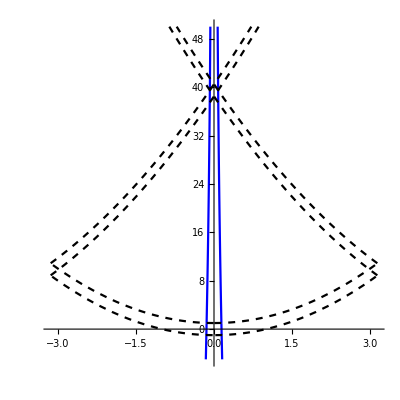

```mathematica
%35/.m->0//Simplify
eq1 = Cos[2 a k1] == ComplexExpand[Re[%[[1,1]]]]/.b->a//Simplify
Cos[2a k2] == ComplexExpand[Re[%%[[3,3]]]]/.b->a//Simplify

Solve[eq1,k1]
ksol=k1/.%/.C[1]->0;
nsub = {Δ->1,a->1/2};
ksol=ksol/.{qm->Sqrt[ (ϵ-Δ)],qp->Sqrt[(ϵ+Δ)]}/.nsub/.C[1]->0
ksolp = ({Sqrt[ (ϵ-Δ)],Sqrt[(ϵ+Δ)]}/.nsub)//Mod[#+π,2π]-π&;
ksolpp = (-{Sqrt[ (ϵ-Δ)],Sqrt[(ϵ+Δ)]}/.nsub)//Mod[#+π,2π]-π&;

f[ϵ_]:=Join[ksol,ksolp,ksolpp]
ParametricPlot[Evaluate@Table[{g,ϵ},{g,f[ϵ]}],{ϵ,-5,50},PlotStyle->{Blue,Blue,{Black,Dashed},{Black,Dashed},{Black,Dashed},{Black,Dashed}},PlotRange->{{-π,π},Automatic},AspectRatio->1]
```

```mathematica
%151/.C[1]->0
```

{-1/2 cos^-1(((ϵ-0.1) sin(√(ϵ-0.1)) sin(√(ϵ+0.1))+(ϵ+0.1) sin(√(ϵ-0.1)) sin(√(ϵ+0.1))+2 √(ϵ-0.1) √(ϵ+0.1) cos(√(ϵ-0.1)) cos(√(ϵ+0.1)))/(2 √(ϵ-0.1) √(ϵ+0.1))),1/2 cos^-1(((ϵ-0.1) sin(√(ϵ-0.1)) sin(√(ϵ+0.1))+(ϵ+0.1) sin(√(ϵ-0.1)) sin(√(ϵ+0.1))+2 √(ϵ-0.1) √(ϵ+0.1) cos(√(ϵ-0.1)) cos(√(ϵ+0.1)))/(2 √(ϵ-0.1) √(ϵ+0.1)))}

```mathematica
%35/.{qm->Sqrt[q^2-Δ],qp->Sqrt[q^2+Δ]};
%//Series[#,{Δ,0,1}]&//Simplify[#,q>0]&//Normal
%//Eigenvalues//FullSimplify[#,{q>0,Δ>0}]&
```

((ⅈ b (m^2-1) Δ)/q+1 | -((-1+ⅇ^(2 ⅈ b q)) (m-1) (m+1) Δ)/(2 q^2) | -(ⅈ b (m-1) m Δ)/q | ((-1+ⅇ^(2 ⅈ b q)) (m-1) m Δ)/(2 q^2)
(ⅇ^(-2 ⅈ b q) (-1+ⅇ^(2 ⅈ b q)) (m-1) (m+1) Δ)/(2 q^2) | 1-(ⅈ b (m^2-1) Δ)/q | -(ⅇ^(-2 ⅈ b q) (-1+ⅇ^(2 ⅈ b q)) (m-1) m Δ)/(2 q^2) | (ⅈ b (m-1) m Δ)/q
(ⅈ b m (m+1) Δ)/q | -((-1+ⅇ^(2 ⅈ b q)) m (m+1) Δ)/(2 q^2) | 1-(ⅈ b (m^2-1) Δ)/q | ((-1+ⅇ^(2 ⅈ b q)) (m^2-1) Δ)/(2 q^2)
(ⅇ^(-2 ⅈ b q) (-1+ⅇ^(2 ⅈ b q)) m (m+1) Δ)/(2 q^2) | -(ⅈ b m (m+1) Δ)/q | -(ⅇ^(-2 ⅈ b q) (-1+ⅇ^(2 ⅈ b q)) (m-1) (m+1) Δ)/(2 q^2) | (ⅈ b (m^2-1) Δ)/q+1)

{1-(Δ ⅇ^(-8 ⅈ b q) √((m^2-1) ⅇ^(16 ⅈ b q) (2 b^2 q^2+cos(2 b q)-1)))/(√2 q^2),1-(Δ ⅇ^(-8 ⅈ b q) √((m^2-1) ⅇ^(16 ⅈ b q) (2 b^2 q^2+cos(2 b q)-1)))/(√2 q^2),1+(Δ ⅇ^(-8 ⅈ b q) √((m^2-1) ⅇ^(16 ⅈ b q) (2 b^2 q^2+cos(2 b q)-1)))/(√2 q^2),1+(Δ ⅇ^(-8 ⅈ b q) √((m^2-1) ⅇ^(16 ⅈ b q) (2 b^2 q^2+cos(2 b q)-1)))/(√2 q^2)}

```mathematica
4 qm qp Diagonal[%35]
```

{(m^2-1) (qm-qp)^2 ⅇ^(-ⅈ b (qm+qp))-(m^2-1) (qm+qp)^2 ⅇ^(ⅈ b (qm-qp))+4 m^2 qm qp,(m^2-1) (qm-qp)^2 ⅇ^(ⅈ b (qm+qp))-(m^2-1) (qm+qp)^2 ⅇ^(-ⅈ b (qm-qp))+4 m^2 qm qp,(m^2-1) (qm-qp)^2 ⅇ^(-ⅈ b (qm+qp))-(m^2-1) (qm+qp)^2 ⅇ^(-ⅈ b (qm-qp))+4 m^2 qm qp,(m^2-1) (qm-qp)^2 ⅇ^(ⅈ b (qm+qp))-(m^2-1) (qm+qp)^2 ⅇ^(ⅈ b (qm-qp))+4 m^2 qm qp}

```mathematica
Sum[ Exp[ⅈ ϕ[i]],{i,1,2}]//ComplexExpand
```

ⅈ (sin(ϕ(1))+sin(ϕ(2)))+cos(ϕ(1))+cos(ϕ(2))

```mathematica
T12/.{-((m-1) (qm+qp))/(2 qm)->αp,-((m-1) (qm-qp))/(2 qm)->βp,((m+1) (qm+qp))/(2 qp)->αm,-((m+1) (qm-qp))/(2 qp)->βm}
T23/.{-((m-1) (qm+qp))/(2 qm)->αp,-((m-1) (qm-qp))/(2 qm)->βp,((m+1) (qm+qp))/(2 qp)->αm,((m+1) (qp-qm))/(2 qp)->βm}/.{ qm->(ϕ+ϕp)/b/2,qp->(ϕp-ϕ)/b/2}//Simplify

%%.%//FullSimplify
Det[IdentityMatrix[4] Exp[2ⅈ k b]-%]==0//FullSimplify
```

(m | 0 | αp | βp
0 | m | βp | αp
αm | βm | -m | 0
βm | αm | 0 | -m)

(m | 0 | ⅇ^(-ⅈ ϕ) αp | ⅇ^(ⅈ ϕp) βp
0 | m | ⅇ^(-ⅈ ϕp) βp | ⅇ^(ⅈ ϕ) αp
ⅇ^(ⅈ ϕ) αm | ⅇ^(ⅈ ϕp) βm | -m | 0
ⅇ^(-ⅈ ϕp) βm | ⅇ^(-ⅈ ϕ) αm | 0 | -m)

(m^2+ⅇ^(ⅈ ϕ) αm αp+ⅇ^(-ⅈ ϕp) βm βp | ⅇ^(ⅈ ϕp) αp βm+ⅇ^(-ⅈ ϕ) αm βp | (-1+ⅇ^(-ⅈ ϕ)) m αp | (-1+ⅇ^(ⅈ ϕp)) m βp
ⅇ^(-ⅈ ϕp) αp βm+ⅇ^(ⅈ ϕ) αm βp | m^2+ⅇ^(-ⅈ ϕ) αm αp+ⅇ^(ⅈ ϕp) βm βp | (-1+ⅇ^(-ⅈ ϕp)) m βp | (-1+ⅇ^(ⅈ ϕ)) m αp
-(-1+ⅇ^(ⅈ ϕ)) m αm | -(-1+ⅇ^(ⅈ ϕp)) m βm | m^2+ⅇ^(-ⅈ ϕ) αm αp+ⅇ^(-ⅈ ϕp) βm βp | ⅇ^(ⅈ ϕ) αp βm+ⅇ^(ⅈ ϕp) αm βp
(1-ⅇ^(-ⅈ ϕp)) m βm | (1-ⅇ^(-ⅈ ϕ)) m αm | ⅇ^(-ⅈ ϕ) αp βm+ⅇ^(-ⅈ ϕp) αm βp | m^2+ⅇ^(ⅈ ϕ) αm αp+ⅇ^(ⅈ ϕp) βm βp)

2 ⅇ^(ⅈ (4 b k+ϕ+ϕp)) (αp^2 (2 αm^2-βm^2)+αm^2 αp^2 cos(2 ϕ)-βp^2 (αm^2-2 βm^2)+3 m^4+4 αm αp cos(ϕ) (βm βp cos(ϕp)+m^2)+2 m^2 (αm αp+βm βp)+βm βp (βm βp cos(2 ϕp)+4 m^2 cos(ϕp)))+ⅈ sin(8 b k+ϕ+ϕp)+cos(8 b k+ϕ+ϕp)+(cos(ϕ+ϕp)+ⅈ sin(ϕ+ϕp)) ((αm-βm) (αp-βp)+m^2)^2 ((αm+βm) (αp+βp)+m^2)^2==4 ⅇ^(ⅈ (2 b k+ϕ+ϕp)) (ⅇ^(4 ⅈ b k) (αm αp cos(ϕ)+βm βp cos(ϕp)+m^2)+cos(ϕp) (βm (βm βp+m^2)-αm^2 βp) (βp (βm βp+m^2)-αp^2 βm)+cos(ϕ) (m^2 cos(ϕp) (αm βp+αp βm)^2+(αp (αm-βm) (αm+βm)+αm m^2) (αm (αp-βp) (αp+βp)+αp m^2))+m^2 (αm αp+βm βp+m^2)^2)

```mathematica
Det[%928]//Simplify
%/.{αp->-((m-1) (qm+qp))/(2 qm),βp->-((m-1) (qm-qp))/(2 qm),αm->((m+1) (qm+qp))/(2 qp),βm->-((m+1) (qm-qp))/(2 qp)}//Simplify
```

(αm^2-βm^2) (αp^2-βp^2)+m^4+2 m^2 (αm αp+βm βp)

1

```mathematica
%870-Exp[ⅈ k a] IdentityMatrix[4]//Det
%//Simplify
```

1/(256 qm^12 qp^9)ⅇ^(-4 ⅈ b (qm-qp)-5 ⅈ b (qm+qp)) (2 ⅇ^(ⅈ b (qm+qp)) (-1+ⅇ^(ⅈ b (qm-qp))) m (m+1) qp (qm+qp) (-2 ⅇ^(ⅈ b (qm-qp)+ⅈ b (qm+qp)) (-1+ⅇ^(ⅈ b (qm-qp))) m (m+1) qm^2 (qm+qp) (4 ⅇ^(2 ⅈ b (qm-qp)+2 ⅈ b (qm+qp)) (-1+ⅇ^(ⅈ b (qm+qp)))^2 (m-1)^2 m^2 qm^6 (qm-qp)^2 qp^4-4 ⅇ^(ⅈ b (qm-qp)+3 ⅈ b (qm+qp)) (-1+ⅇ^(ⅈ b (qm-qp)))^2 (m-1)^2 m^2 qm^6 qp^4 (qm+qp)^2) qp^2+qm (-ⅇ^(ⅈ b (qm-qp)) qm^2 m^2+ⅇ^(ⅈ b (qm+qp)) qm^2 m^2-ⅇ^(ⅈ b (qm-qp)) qp^2 m^2+ⅇ^(ⅈ b (qm+qp)) qp^2 m^2+2 ⅇ^(ⅈ b (qm-qp)) qm qp m^2+2 ⅇ^(ⅈ b (qm+qp)) qm qp m^2-4 ⅇ^(ⅈ b (qm-qp)+ⅈ b (qm+qp)) qm qp m^2+ⅇ^(ⅈ b (qm-qp)) qm^2-ⅇ^(ⅈ b (qm+qp)) qm^2+ⅇ^(ⅈ b (qm-qp)) qp^2-ⅇ^(ⅈ b (qm+qp)) qp^2-2 ⅇ^(ⅈ b (qm-qp)) qm qp-2 ⅇ^(ⅈ b (qm+qp)) qm qp+4 ⅇ^(ⅈ a k+ⅈ b (qm-qp)+ⅈ b (qm+qp)) qm qp) (2 ⅇ^(2 ⅈ b (qm-qp)+2 ⅈ b (qm+qp)) (-1+ⅇ^(ⅈ b (qm-qp))) (m-1) m qm^6 qp^3 (qm+qp) (ⅇ^(ⅈ b (qm-qp)+ⅈ b (qm+qp)) qm^2 m^2-qm^2 m^2+ⅇ^(ⅈ b (qm-qp)+ⅈ b (qm+qp)) qp^2 m^2-qp^2 m^2-4 ⅇ^(ⅈ b (qm+qp)) qm qp m^2+2 ⅇ^(ⅈ b (qm-qp)+ⅈ b (qm+qp)) qm qp m^2+2 qm qp m^2-ⅇ^(ⅈ b (qm-qp)+ⅈ b (qm+qp)) qm^2+qm^2-ⅇ^(ⅈ b (qm-qp)+ⅈ b (qm+qp)) qp^2+qp^2+4 ⅇ^(ⅈ a k+ⅈ b (qm+qp)) qm qp-2 ⅇ^(ⅈ b (qm-qp)+ⅈ b (qm+qp)) qm qp-2 qm qp)-2 ⅇ^(2 ⅈ b (qm-qp)+2 ⅈ b (qm+qp)) (-1+ⅇ^(2 ⅈ b qm)) (-1+ⅇ^(ⅈ b (qm+qp))) (m-1)^2 m (m+1) qm^6 (qm-qp)^2 qp^3 (qm+qp)) qp^2-2 ⅈ ⅇ^(ⅈ b qm+ⅈ b (qm-qp)+ⅈ b (qm+qp)) (m^2-1) qm (qm-qp) (qm+qp) (2 ⅇ^(ⅈ b (qm-qp)+2 ⅈ b (qm+qp)) (-1+ⅇ^(2 ⅈ b qm)) (-1+ⅇ^(ⅈ b (qm-qp))) (m-1)^2 m (m+1) qm^6 (qm-qp) qp^3 (qm+qp)^2-2 ⅇ^(2 ⅈ b (qm-qp)+ⅈ b (qm+qp)) (-1+ⅇ^(ⅈ b (qm+qp))) (m-1) m qm^6 (qm-qp) qp^3 (ⅇ^(ⅈ b (qm-qp)+ⅈ b (qm+qp)) qm^2 m^2-qm^2 m^2+ⅇ^(ⅈ b (qm-qp)+ⅈ b (qm+qp)) qp^2 m^2-qp^2 m^2-4 ⅇ^(ⅈ b (qm+qp)) qm qp m^2+2 ⅇ^(ⅈ b (qm-qp)+ⅈ b (qm+qp)) qm qp m^2+2 qm qp m^2-ⅇ^(ⅈ b (qm-qp)+ⅈ b (qm+qp)) qm^2+qm^2-ⅇ^(ⅈ b (qm-qp)+ⅈ b (qm+qp)) qp^2+qp^2+4 ⅇ^(ⅈ a k+ⅈ b (qm+qp)) qm qp-2 ⅇ^(ⅈ b (qm-qp)+ⅈ b (qm+qp)) qm qp-2 qm qp)) sin(b qp) qp^2) qm^2+2 ⅇ^(ⅈ b (qm-qp)) (-1+ⅇ^(ⅈ b (qm+qp))) m (m+1) (qm-qp) qp (2 ⅇ^(ⅈ b (qm-qp)+ⅈ b (qm+qp)) (-1+ⅇ^(ⅈ b (qm+qp))) m (m+1) qm^2 (qm-qp) (4 ⅇ^(2 ⅈ b (qm-qp)+2 ⅈ b (qm+qp)) (-1+ⅇ^(ⅈ b (qm+qp)))^2 (m-1)^2 m^2 qm^6 (qm-qp)^2 qp^4-4 ⅇ^(ⅈ b (qm-qp)+3 ⅈ b (qm+qp)) (-1+ⅇ^(ⅈ b (qm-qp)))^2 (m-1)^2 m^2 qm^6 qp^4 (qm+qp)^2) qp^2+qm (-ⅇ^(ⅈ b (qm-qp)) qm^2 m^2+ⅇ^(ⅈ b (qm+qp)) qm^2 m^2-ⅇ^(ⅈ b (qm-qp)) qp^2 m^2+ⅇ^(ⅈ b (qm+qp)) qp^2 m^2+2 ⅇ^(ⅈ b (qm-qp)) qm qp m^2+2 ⅇ^(ⅈ b (qm+qp)) qm qp m^2-4 ⅇ^(ⅈ b (qm-qp)+ⅈ b (qm+qp)) qm qp m^2+ⅇ^(ⅈ b (qm-qp)) qm^2-ⅇ^(ⅈ b (qm+qp)) qm^2+ⅇ^(ⅈ b (qm-qp)) qp^2-ⅇ^(ⅈ b (qm+qp)) qp^2-2 ⅇ^(ⅈ b (qm-qp)) qm qp-2 ⅇ^(ⅈ b (qm+qp)) qm qp+4 ⅇ^(ⅈ a k+ⅈ b (qm-qp)+ⅈ b (qm+qp)) qm qp) (2 ⅇ^(ⅈ b (qm-qp)+3 ⅈ b (qm+qp)) (-1+ⅇ^(ⅈ b (qm+qp))) (m-1) m qm^6 (qm-qp) qp^3 (ⅇ^(ⅈ b (qm-qp)+ⅈ b (qm+qp)) qm^2 m^2-qm^2 m^2+ⅇ^(ⅈ b (qm-qp)+ⅈ b (qm+qp)) qp^2 m^2-qp^2 m^2+4 ⅇ^(ⅈ b (qm-qp)) qm qp m^2-2 ⅇ^(ⅈ b (qm-qp)+ⅈ b (qm+qp)) qm qp m^2-2 qm qp m^2-ⅇ^(ⅈ b (qm-qp)+ⅈ b (qm+qp)) qm^2+qm^2-ⅇ^(ⅈ b (qm-qp)+ⅈ b (qm+qp)) qp^2+qp^2-4 ⅇ^(ⅈ a k+ⅈ b (qm-qp)) qm qp+2 ⅇ^(ⅈ b (qm-qp)+ⅈ b (qm+qp)) qm qp+2 qm qp)-4 ⅈ ⅇ^(2 ⅈ b (qm-qp)+ⅈ b qp+3 ⅈ b (qm+qp)) (-1+ⅇ^(ⅈ b (qm-qp))) (m-1)^2 m (m+1) qm^6 (qm-qp) qp^3 (qm+qp)^2 sin(b qm)) qp^2-2 ⅈ ⅇ^(ⅈ b qm+ⅈ b (qm-qp)+ⅈ b (qm+qp)) (m^2-1) qm (qm-qp) (qm+qp) (4 ⅈ ⅇ^(2 ⅈ b (qm-qp)+ⅈ b qp+2 ⅈ b (qm+qp)) (-1+ⅇ^(ⅈ b (qm+qp))) (m-1)^2 m (m+1) qm^6 (qm-qp)^2 qp^3 (qm+qp) sin(b qm)-2 ⅇ^(3 ⅈ b (qm+qp)) (-1+ⅇ^(ⅈ b (qm-qp))) (m-1) m qm^6 qp^3 (qm+qp) (ⅇ^(ⅈ b (qm-qp)+ⅈ b (qm+qp)) qm^2 m^2-qm^2 m^2+ⅇ^(ⅈ b (qm-qp)+ⅈ b (qm+qp)) qp^2 m^2-qp^2 m^2+4 ⅇ^(ⅈ b (qm-qp)) qm qp m^2-2 ⅇ^(ⅈ b (qm-qp)+ⅈ b (qm+qp)) qm qp m^2-2 qm qp m^2-ⅇ^(ⅈ b (qm-qp)+ⅈ b (qm+qp)) qm^2+qm^2-ⅇ^(ⅈ b (qm-qp)+ⅈ b (qm+qp)) qp^2+qp^2-4 ⅇ^(ⅈ a k+ⅈ b (qm-qp)) qm qp+2 ⅇ^(ⅈ b (qm-qp)+ⅈ b (qm+qp)) qm qp+2 qm qp)) sin(b qp) qp^2) qm^2+ⅇ^(ⅈ b (qm-qp)+ⅈ b (qm+qp)) qp (-ⅇ^(ⅈ b (qm-qp)) qm^2 m^2+ⅇ^(ⅈ b (qm+qp)) qm^2 m^2-ⅇ^(ⅈ b (qm-qp)) qp^2 m^2+ⅇ^(ⅈ b (qm+qp)) qp^2 m^2-2 ⅇ^(ⅈ b (qm-qp)) qm qp m^2-2 ⅇ^(ⅈ b (qm+qp)) qm qp m^2+4 qm qp m^2+ⅇ^(ⅈ b (qm-qp)) qm^2-ⅇ^(ⅈ b (qm+qp)) qm^2+ⅇ^(ⅈ b (qm-qp)) qp^2-ⅇ^(ⅈ b (qm+qp)) qp^2-4 ⅇ^(ⅈ a k) qm qp+2 ⅇ^(ⅈ b (qm-qp)) qm qp+2 ⅇ^(ⅈ b (qm+qp)) qm qp) (-2 ⅇ^(ⅈ b (qm-qp)+ⅈ b (qm+qp)) (-1+ⅇ^(ⅈ b (qm+qp))) m (m+1) qm^2 (qm-qp) (2 ⅇ^(ⅈ b (qm-qp)+2 ⅈ b (qm+qp)) (-1+ⅇ^(2 ⅈ b qm)) (-1+ⅇ^(ⅈ b (qm-qp))) (m-1)^2 m (m+1) qm^6 (qm-qp) qp^3 (qm+qp)^2-2 ⅇ^(2 ⅈ b (qm-qp)+ⅈ b (qm+qp)) (-1+ⅇ^(ⅈ b (qm+qp))) (m-1) m qm^6 (qm-qp) qp^3 (ⅇ^(ⅈ b (qm-qp)+ⅈ b (qm+qp)) qm^2 m^2-qm^2 m^2+ⅇ^(ⅈ b (qm-qp)+ⅈ b (qm+qp)) qp^2 m^2-qp^2 m^2-4 ⅇ^(ⅈ b (qm+qp)) qm qp m^2+2 ⅇ^(ⅈ b (qm-qp)+ⅈ b (qm+qp)) qm qp m^2+2 qm qp m^2-ⅇ^(ⅈ b (qm-qp)+ⅈ b (qm+qp)) qm^2+qm^2-ⅇ^(ⅈ b (qm-qp)+ⅈ b (qm+qp)) qp^2+qp^2+4 ⅇ^(ⅈ a k+ⅈ b (qm+qp)) qm qp-2 ⅇ^(ⅈ b (qm-qp)+ⅈ b (qm+qp)) qm qp-2 qm qp)) qp^2-2 ⅇ^(ⅈ b (qm-qp)+ⅈ b (qm+qp)) (-1+ⅇ^(ⅈ b (qm-qp))) m (m+1) qm^2 (qm+qp) (4 ⅈ ⅇ^(2 ⅈ b (qm-qp)+ⅈ b qp+2 ⅈ b (qm+qp)) (-1+ⅇ^(ⅈ b (qm+qp))) (m-1)^2 m (m+1) qm^6 (qm-qp)^2 qp^3 (qm+qp) sin(b qm)-2 ⅇ^(3 ⅈ b (qm+qp)) (-1+ⅇ^(ⅈ b (qm-qp))) (m-1) m qm^6 qp^3 (qm+qp) (ⅇ^(ⅈ b (qm-qp)+ⅈ b (qm+qp)) qm^2 m^2-qm^2 m^2+ⅇ^(ⅈ b (qm-qp)+ⅈ b (qm+qp)) qp^2 m^2-qp^2 m^2+4 ⅇ^(ⅈ b (qm-qp)) qm qp m^2-2 ⅇ^(ⅈ b (qm-qp)+ⅈ b (qm+qp)) qm qp m^2-2 qm qp m^2-ⅇ^(ⅈ b (qm-qp)+ⅈ b (qm+qp)) qm^2+qm^2-ⅇ^(ⅈ b (qm-qp)+ⅈ b (qm+qp)) qp^2+qp^2-4 ⅇ^(ⅈ a k+ⅈ b (qm-qp)) qm qp+2 ⅇ^(ⅈ b (qm-qp)+ⅈ b (qm+qp)) qm qp+2 qm qp)) qp^2-qm (-ⅇ^(ⅈ b (qm-qp)) qm^2 m^2+ⅇ^(ⅈ b (qm+qp)) qm^2 m^2-ⅇ^(ⅈ b (qm-qp)) qp^2 m^2+ⅇ^(ⅈ b (qm+qp)) qp^2 m^2+2 ⅇ^(ⅈ b (qm-qp)) qm qp m^2+2 ⅇ^(ⅈ b (qm+qp)) qm qp m^2-4 ⅇ^(ⅈ b (qm-qp)+ⅈ b (qm+qp)) qm qp m^2+ⅇ^(ⅈ b (qm-qp)) qm^2-ⅇ^(ⅈ b (qm+qp)) qm^2+ⅇ^(ⅈ b (qm-qp)) qp^2-ⅇ^(ⅈ b (qm+qp)) qp^2-2 ⅇ^(ⅈ b (qm-qp)) qm qp-2 ⅇ^(ⅈ b (qm+qp)) qm qp+4 ⅇ^(ⅈ a k+ⅈ b (qm-qp)+ⅈ b (qm+qp)) qm qp) (2 ⅈ ⅇ^(2 ⅈ b (qm-qp)+ⅈ b qp+2 ⅈ b (qm+qp)) (-1+ⅇ^(2 ⅈ b qm)) (m-1)^2 (m+1)^2 qm^6 (qm-qp)^2 qp^2 (qm+qp)^2 sin(b qm)-ⅇ^(ⅈ b (qm-qp)+2 ⅈ b (qm+qp)) qm^6 qp^2 (ⅇ^(ⅈ b (qm-qp)+ⅈ b (qm+qp)) qm^2 m^2-qm^2 m^2+ⅇ^(ⅈ b (qm-qp)+ⅈ b (qm+qp)) qp^2 m^2-qp^2 m^2+4 ⅇ^(ⅈ b (qm-qp)) qm qp m^2-2 ⅇ^(ⅈ b (qm-qp)+ⅈ b (qm+qp)) qm qp m^2-2 qm qp m^2-ⅇ^(ⅈ b (qm-qp)+ⅈ b (qm+qp)) qm^2+qm^2-ⅇ^(ⅈ b (qm-qp)+ⅈ b (qm+qp)) qp^2+qp^2-4 ⅇ^(ⅈ a k+ⅈ b (qm-qp)) qm qp+2 ⅇ^(ⅈ b (qm-qp)+ⅈ b (qm+qp)) qm qp+2 qm qp) (ⅇ^(ⅈ b (qm-qp)+ⅈ b (qm+qp)) qm^2 m^2-qm^2 m^2+ⅇ^(ⅈ b (qm-qp)+ⅈ b (qm+qp)) qp^2 m^2-qp^2 m^2-4 ⅇ^(ⅈ b (qm+qp)) qm qp m^2+2 ⅇ^(ⅈ b (qm-qp)+ⅈ b (qm+qp)) qm qp m^2+2 qm qp m^2-ⅇ^(ⅈ b (qm-qp)+ⅈ b (qm+qp)) qm^2+qm^2-ⅇ^(ⅈ b (qm-qp)+ⅈ b (qm+qp)) qp^2+qp^2+4 ⅇ^(ⅈ a k+ⅈ b (qm+qp)) qm qp-2 ⅇ^(ⅈ b (qm-qp)+ⅈ b (qm+qp)) qm qp-2 qm qp)) qp^2) qm-ⅇ^(ⅈ b (qm-qp)) (-1+ⅇ^(2 ⅈ b qp)) (m-1) (m+1) (qm-qp) qp (qm+qp) (-2 ⅇ^(ⅈ b (qm-qp)+ⅈ b (qm+qp)) (-1+ⅇ^(ⅈ b (qm+qp))) m (m+1) qm^2 (qm-qp) (2 ⅇ^(2 ⅈ b (qm-qp)+2 ⅈ b (qm+qp)) (-1+ⅇ^(ⅈ b (qm-qp))) (m-1) m qm^6 qp^3 (qm+qp) (ⅇ^(ⅈ b (qm-qp)+ⅈ b (qm+qp)) qm^2 m^2-qm^2 m^2+ⅇ^(ⅈ b (qm-qp)+ⅈ b (qm+qp)) qp^2 m^2-qp^2 m^2-4 ⅇ^(ⅈ b (qm+qp)) qm qp m^2+2 ⅇ^(ⅈ b (qm-qp)+ⅈ b (qm+qp)) qm qp m^2+2 qm qp m^2-ⅇ^(ⅈ b (qm-qp)+ⅈ b (qm+qp)) qm^2+qm^2-ⅇ^(ⅈ b (qm-qp)+ⅈ b (qm+qp)) qp^2+qp^2+4 ⅇ^(ⅈ a k+ⅈ b (qm+qp)) qm qp-2 ⅇ^(ⅈ b (qm-qp)+ⅈ b (qm+qp)) qm qp-2 qm qp)-2 ⅇ^(2 ⅈ b (qm-qp)+2 ⅈ b (qm+qp)) (-1+ⅇ^(2 ⅈ b qm)) (-1+ⅇ^(ⅈ b (qm+qp))) (m-1)^2 m (m+1) qm^6 (qm-qp)^2 qp^3 (qm+qp)) qp^2-2 ⅇ^(ⅈ b (qm-qp)+ⅈ b (qm+qp)) (-1+ⅇ^(ⅈ b (qm-qp))) m (m+1) qm^2 (qm+qp) (2 ⅇ^(ⅈ b (qm-qp)+3 ⅈ b (qm+qp)) (-1+ⅇ^(ⅈ b (qm+qp))) (m-1) m qm^6 (qm-qp) qp^3 (ⅇ^(ⅈ b (qm-qp)+ⅈ b (qm+qp)) qm^2 m^2-qm^2 m^2+ⅇ^(ⅈ b (qm-qp)+ⅈ b (qm+qp)) qp^2 m^2-qp^2 m^2+4 ⅇ^(ⅈ b (qm-qp)) qm qp m^2-2 ⅇ^(ⅈ b (qm-qp)+ⅈ b (qm+qp)) qm qp m^2-2 qm qp m^2-ⅇ^(ⅈ b (qm-qp)+ⅈ b (qm+qp)) qm^2+qm^2-ⅇ^(ⅈ b (qm-qp)+ⅈ b (qm+qp)) qp^2+qp^2-4 ⅇ^(ⅈ a k+ⅈ b (qm-qp)) qm qp+2 ⅇ^(ⅈ b (qm-qp)+ⅈ b (qm+qp)) qm qp+2 qm qp)-4 ⅈ ⅇ^(2 ⅈ b (qm-qp)+ⅈ b qp+3 ⅈ b (qm+qp)) (-1+ⅇ^(ⅈ b (qm-qp))) (m-1)^2 m (m+1) qm^6 (qm-qp) qp^3 (qm+qp)^2 sin(b qm)) qp^2-2 ⅈ ⅇ^(ⅈ b qm+ⅈ b (qm-qp)+ⅈ b (qm+qp)) (m^2-1) qm (qm-qp) (qm+qp) (2 ⅈ ⅇ^(2 ⅈ b (qm-qp)+ⅈ b qp+2 ⅈ b (qm+qp)) (-1+ⅇ^(2 ⅈ b qm)) (m-1)^2 (m+1)^2 qm^6 (qm-qp)^2 qp^2 (qm+qp)^2 sin(b qm)-ⅇ^(ⅈ b (qm-qp)+2 ⅈ b (qm+qp)) qm^6 qp^2 (ⅇ^(ⅈ b (qm-qp)+ⅈ b (qm+qp)) qm^2 m^2-qm^2 m^2+ⅇ^(ⅈ b (qm-qp)+ⅈ b (qm+qp)) qp^2 m^2-qp^2 m^2+4 ⅇ^(ⅈ b (qm-qp)) qm qp m^2-2 ⅇ^(ⅈ b (qm-qp)+ⅈ b (qm+qp)) qm qp m^2-2 qm qp m^2-ⅇ^(ⅈ b (qm-qp)+ⅈ b (qm+qp)) qm^2+qm^2-ⅇ^(ⅈ b (qm-qp)+ⅈ b (qm+qp)) qp^2+qp^2-4 ⅇ^(ⅈ a k+ⅈ b (qm-qp)) qm qp+2 ⅇ^(ⅈ b (qm-qp)+ⅈ b (qm+qp)) qm qp+2 qm qp) (ⅇ^(ⅈ b (qm-qp)+ⅈ b (qm+qp)) qm^2 m^2-qm^2 m^2+ⅇ^(ⅈ b (qm-qp)+ⅈ b (qm+qp)) qp^2 m^2-qp^2 m^2-4 ⅇ^(ⅈ b (qm+qp)) qm qp m^2+2 ⅇ^(ⅈ b (qm-qp)+ⅈ b (qm+qp)) qm qp m^2+2 qm qp m^2-ⅇ^(ⅈ b (qm-qp)+ⅈ b (qm+qp)) qm^2+qm^2-ⅇ^(ⅈ b (qm-qp)+ⅈ b (qm+qp)) qp^2+qp^2+4 ⅇ^(ⅈ a k+ⅈ b (qm+qp)) qm qp-2 ⅇ^(ⅈ b (qm-qp)+ⅈ b (qm+qp)) qm qp-2 qm qp)) sin(b qp) qp^2) qm)

$Aborted

```mathematica
%/.{qm->qp}/.{qp->Sqrt[ϵ]}
```

-(m^2-1) sin^2(a √ϵ)-(m^2-1) cos^2(a √ϵ)+m^2

```mathematica
%/.{qm->Sqrt[ϵ-Δ],qp->Sqrt[ϵ+Δ]}
%//Simplify
```

1/l^4 16 ⅇ^(-1/2 ⅈ a (√(ϵ-Δ)+√(Δ+ϵ))) (16 ⅇ^(2 ⅈ a k) (m^2-1) √(ϵ-Δ) √(Δ+ϵ) (√(ϵ-Δ)-√(Δ+ϵ))^2 m^2+16 ⅇ^(ⅈ a (2 k+√(ϵ-Δ)+√(Δ+ϵ))) (m^2-1) √(ϵ-Δ) √(Δ+ϵ) (√(ϵ-Δ)-√(Δ+ϵ))^2 m^2-16 ⅇ^(ⅈ a (2 k+√(ϵ-Δ))) (m^2-1) √(ϵ-Δ) √(Δ+ϵ) (√(ϵ-Δ)+√(Δ+ϵ))^2 m^2-16 ⅇ^(ⅈ a (2 k+√(Δ+ϵ))) (m^2-1) √(ϵ-Δ) √(Δ+ϵ) (√(ϵ-Δ)+√(Δ+ϵ))^2 m^2-16 ⅇ^(1/2 ⅈ a (2 k+√(ϵ-Δ)-√(Δ+ϵ))) (ϵ-Δ) (Δ+ϵ) m^2-16 ⅇ^(1/2 ⅈ a (6 k+√(ϵ-Δ)-√(Δ+ϵ))) (ϵ-Δ) (Δ+ϵ) m^2-16 ⅇ^(1/2 ⅈ a (2 k-√(ϵ-Δ)+√(Δ+ϵ))) (ϵ-Δ) (Δ+ϵ) m^2-16 ⅇ^(1/2 ⅈ a (6 k-√(ϵ-Δ)+√(Δ+ϵ))) (ϵ-Δ) (Δ+ϵ) m^2-16 ⅇ^(1/2 ⅈ a (2 k+3 √(ϵ-Δ)+√(Δ+ϵ))) (ϵ-Δ) (Δ+ϵ) m^2-16 ⅇ^(1/2 ⅈ a (6 k+3 √(ϵ-Δ)+√(Δ+ϵ))) (ϵ-Δ) (Δ+ϵ) m^2-16 ⅇ^(1/2 ⅈ a (2 k+√(ϵ-Δ)+3 √(Δ+ϵ))) (ϵ-Δ) (Δ+ϵ) m^2-16 ⅇ^(1/2 ⅈ a (6 k+√(ϵ-Δ)+3 √(Δ+ϵ))) (ϵ-Δ) (Δ+ϵ) m^2-8 ⅇ^(1/2 ⅈ a (4 k+√(ϵ-Δ)-√(Δ+ϵ))) (m^2-1)^2 Δ^2-8 ⅇ^(1/2 ⅈ a (4 k-√(ϵ-Δ)+√(Δ+ϵ))) (m^2-1)^2 Δ^2-8 ⅇ^(1/2 ⅈ a (4 k+3 √(ϵ-Δ)+√(Δ+ϵ))) (m^2-1)^2 Δ^2-8 ⅇ^(1/2 ⅈ a (4 k+√(ϵ-Δ)+3 √(Δ+ϵ))) (m^2-1)^2 Δ^2-8 ⅇ^(ⅈ a (k+√(ϵ-Δ))) (m^2-1) √(ϵ-Δ) √(Δ+ϵ) (√(ϵ-Δ)-√(Δ+ϵ))^2-8 ⅇ^(ⅈ a (3 k+√(ϵ-Δ))) (m^2-1) √(ϵ-Δ) √(Δ+ϵ) (√(ϵ-Δ)-√(Δ+ϵ))^2-8 ⅇ^(ⅈ a (k+√(Δ+ϵ))) (m^2-1) √(ϵ-Δ) √(Δ+ϵ) (√(ϵ-Δ)-√(Δ+ϵ))^2-8 ⅇ^(ⅈ a (3 k+√(Δ+ϵ))) (m^2-1) √(ϵ-Δ) √(Δ+ϵ) (√(ϵ-Δ)-√(Δ+ϵ))^2+8 ⅇ^(ⅈ a k) (m^2-1) √(ϵ-Δ) √(Δ+ϵ) (√(ϵ-Δ)+√(Δ+ϵ))^2+8 ⅇ^(3 ⅈ a k) (m^2-1) √(ϵ-Δ) √(Δ+ϵ) (√(ϵ-Δ)+√(Δ+ϵ))^2+8 ⅇ^(ⅈ a (k+√(ϵ-Δ)+√(Δ+ϵ))) (m^2-1) √(ϵ-Δ) √(Δ+ϵ) (√(ϵ-Δ)+√(Δ+ϵ))^2+8 ⅇ^(ⅈ a (3 k+√(ϵ-Δ)+√(Δ+ϵ))) (m^2-1) √(ϵ-Δ) √(Δ+ϵ) (√(ϵ-Δ)+√(Δ+ϵ))^2+ⅇ^(1/2 ⅈ a (4 k+3 √(ϵ-Δ)-√(Δ+ϵ))) (√(Δ+ϵ) (m-1)+(m+1) √(ϵ-Δ))^2 (√(ϵ-Δ) (m-1)+m √(Δ+ϵ)+√(Δ+ϵ))^2+ⅇ^(1/2 ⅈ a (4 k-√(ϵ-Δ)+3 √(Δ+ϵ))) (√(Δ+ϵ) (m-1)+(m+1) √(ϵ-Δ))^2 (√(ϵ-Δ) (m-1)+m √(Δ+ϵ)+√(Δ+ϵ))^2+ⅇ^(1/2 ⅈ a (4 k-√(ϵ-Δ)-√(Δ+ϵ))) (√(ϵ-Δ) m-√(Δ+ϵ) m+√(ϵ-Δ)+√(Δ+ϵ))^2 ((m-1) √(ϵ-Δ)-(m+1) √(Δ+ϵ))^2+ⅇ^(1/2 ⅈ a (4 k+3 (√(ϵ-Δ)+√(Δ+ϵ)))) (√(ϵ-Δ) m-√(Δ+ϵ) m+√(ϵ-Δ)+√(Δ+ϵ))^2 ((m-1) √(ϵ-Δ)-(m+1) √(Δ+ϵ))^2+16 ⅇ^(1/2 ⅈ a (√(ϵ-Δ)+√(Δ+ϵ))) (ϵ-Δ) (Δ+ϵ)+16 ⅇ^(1/2 ⅈ a (8 k+√(ϵ-Δ)+√(Δ+ϵ))) (ϵ-Δ) (Δ+ϵ)+4 ⅇ^(1/2 ⅈ a (4 k+√(ϵ-Δ)+√(Δ+ϵ))) ((m^2-1)^2 (ϵ-Δ)^2+2 (11 m^4-14 m^2+7) (Δ+ϵ) (ϵ-Δ)+(m^2-1)^2 (Δ+ϵ)^2))

1/l^4 64 ⅇ^(-1/2 ⅈ a (√(ϵ-Δ)+√(Δ+ϵ))) (4 ⅇ^(2 ⅈ a k) (m^2-1) √(ϵ-Δ) √(Δ+ϵ) (√(ϵ-Δ)-√(Δ+ϵ))^2 m^2+4 ⅇ^(ⅈ a (2 k+√(ϵ-Δ)+√(Δ+ϵ))) (m^2-1) √(ϵ-Δ) √(Δ+ϵ) (√(ϵ-Δ)-√(Δ+ϵ))^2 m^2-4 ⅇ^(ⅈ a (2 k+√(ϵ-Δ))) (m^2-1) √(ϵ-Δ) √(Δ+ϵ) (√(ϵ-Δ)+√(Δ+ϵ))^2 m^2-4 ⅇ^(ⅈ a (2 k+√(Δ+ϵ))) (m^2-1) √(ϵ-Δ) √(Δ+ϵ) (√(ϵ-Δ)+√(Δ+ϵ))^2 m^2+4 ⅇ^(1/2 ⅈ a (2 k+√(ϵ-Δ)-√(Δ+ϵ))) (Δ-ϵ) (Δ+ϵ) m^2+4 ⅇ^(1/2 ⅈ a (6 k+√(ϵ-Δ)-√(Δ+ϵ))) (Δ-ϵ) (Δ+ϵ) m^2+4 ⅇ^(1/2 ⅈ a (2 k-√(ϵ-Δ)+√(Δ+ϵ))) (Δ-ϵ) (Δ+ϵ) m^2+4 ⅇ^(1/2 ⅈ a (6 k-√(ϵ-Δ)+√(Δ+ϵ))) (Δ-ϵ) (Δ+ϵ) m^2+4 ⅇ^(1/2 ⅈ a (2 k+3 √(ϵ-Δ)+√(Δ+ϵ))) (Δ-ϵ) (Δ+ϵ) m^2+4 ⅇ^(1/2 ⅈ a (6 k+3 √(ϵ-Δ)+√(Δ+ϵ))) (Δ-ϵ) (Δ+ϵ) m^2+4 ⅇ^(1/2 ⅈ a (2 k+√(ϵ-Δ)+3 √(Δ+ϵ))) (Δ-ϵ) (Δ+ϵ) m^2+4 ⅇ^(1/2 ⅈ a (6 k+√(ϵ-Δ)+3 √(Δ+ϵ))) (Δ-ϵ) (Δ+ϵ) m^2-2 ⅇ^(1/2 ⅈ a (4 k+√(ϵ-Δ)-√(Δ+ϵ))) (m^2-1)^2 Δ^2-2 ⅇ^(1/2 ⅈ a (4 k-√(ϵ-Δ)+√(Δ+ϵ))) (m^2-1)^2 Δ^2-2 ⅇ^(1/2 ⅈ a (4 k+3 √(ϵ-Δ)+√(Δ+ϵ))) (m^2-1)^2 Δ^2-2 ⅇ^(1/2 ⅈ a (4 k+√(ϵ-Δ)+3 √(Δ+ϵ))) (m^2-1)^2 Δ^2-2 ⅇ^(ⅈ a (k+√(ϵ-Δ))) (m^2-1) √(ϵ-Δ) √(Δ+ϵ) (√(ϵ-Δ)-√(Δ+ϵ))^2-2 ⅇ^(ⅈ a (3 k+√(ϵ-Δ))) (m^2-1) √(ϵ-Δ) √(Δ+ϵ) (√(ϵ-Δ)-√(Δ+ϵ))^2-2 ⅇ^(ⅈ a (k+√(Δ+ϵ))) (m^2-1) √(ϵ-Δ) √(Δ+ϵ) (√(ϵ-Δ)-√(Δ+ϵ))^2-2 ⅇ^(ⅈ a (3 k+√(Δ+ϵ))) (m^2-1) √(ϵ-Δ) √(Δ+ϵ) (√(ϵ-Δ)-√(Δ+ϵ))^2+2 ⅇ^(ⅈ a k) (m^2-1) √(ϵ-Δ) √(Δ+ϵ) (√(ϵ-Δ)+√(Δ+ϵ))^2+2 ⅇ^(3 ⅈ a k) (m^2-1) √(ϵ-Δ) √(Δ+ϵ) (√(ϵ-Δ)+√(Δ+ϵ))^2+2 ⅇ^(ⅈ a (k+√(ϵ-Δ)+√(Δ+ϵ))) (m^2-1) √(ϵ-Δ) √(Δ+ϵ) (√(ϵ-Δ)+√(Δ+ϵ))^2+2 ⅇ^(ⅈ a (3 k+√(ϵ-Δ)+√(Δ+ϵ))) (m^2-1) √(ϵ-Δ) √(Δ+ϵ) (√(ϵ-Δ)+√(Δ+ϵ))^2+ⅇ^(-1/2 ⅈ a (-4 k+√(ϵ-Δ)+√(Δ+ϵ))) (-ϵ m^2+ϵ+(m^2+1) √(ϵ-Δ) √(Δ+ϵ))^2+ⅇ^(1/2 ⅈ a (4 k+3 (√(ϵ-Δ)+√(Δ+ϵ)))) (-ϵ m^2+ϵ+(m^2+1) √(ϵ-Δ) √(Δ+ϵ))^2+ⅇ^(-1/2 ⅈ a (-4 k+√(ϵ-Δ)-3 √(Δ+ϵ))) (√(ϵ-Δ) √(Δ+ϵ) (m^2+1)+(m^2-1) ϵ)^2+ⅇ^(1/2 ⅈ a (4 k+3 √(ϵ-Δ)-√(Δ+ϵ))) (√(ϵ-Δ) √(Δ+ϵ) (m^2+1)+(m^2-1) ϵ)^2+4 ⅇ^(1/2 ⅈ a (√(ϵ-Δ)+√(Δ+ϵ))) (ϵ-Δ) (Δ+ϵ)+4 ⅇ^(1/2 ⅈ a (8 k+√(ϵ-Δ)+√(Δ+ϵ))) (ϵ-Δ) (Δ+ϵ)-4 ⅇ^(1/2 ⅈ a (4 k+√(ϵ-Δ)+√(Δ+ϵ))) ((5 m^4-6 m^2+3) Δ^2-2 (3 m^4-4 m^2+2) ϵ^2))

-2 (cos(a k)-cos(q (b+w))) (cos(a k+q (b+w))+ⅈ sin(a k+q (b+w)))

-2 (cos(2 k w)-cos(2 q w)) (cos(2 k w+2 q w)+ⅈ sin(2 k w+2 q w))

-2 (cos(2 k w)-cos(2 q w)) (cos(2 w (k+q))+ⅈ sin(2 w (k+q)))

{{k→-(cos^-1(-(√(-sin^2(q w)+cos^2(q w)+1))/(√2)))/w},{k→(cos^-1(-(√(-sin^2(q w)+cos^2(q w)+1))/(√2)))/w},{k→-(cos^-1((√(-sin^2(q w)+cos^2(q w)+1))/(√2)))/w},{k→(cos^-1((√(-sin^2(q w)+cos^2(q w)+1))/(√2)))/w}}

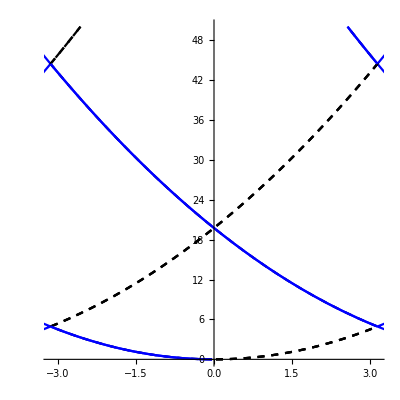

```mathematica
-E^(I*(2*a*k + q*(b + w))) + E^(I*(a*k + 2*q*(b + w))) + E^(I*a*k) - E^(I*q*(b + w))//ComplexExpand//Simplify
%/.b->w/.a->2w
%//Simplify
%//Solve[#==0,k]&

ksol=k/.%;
nsub = {m->1,v1->0,v2->0,b->0.5,w->0.5,a->1};
ksol=ksol/.{q->Sqrt[2m (ϵ-v1)],qb->Sqrt[2 m(ϵ-v2)], ϕ->q w+q b, ϕp->q w-q b}/.nsub;
ksolp = ({Sqrt[2m (ϵ-v1)],Sqrt[2 m(ϵ-v2)]}/.nsub)//Mod[#+π,2π]-π&;
ksolpp = (-{Sqrt[2m (ϵ-v1)],Sqrt[2 m(ϵ-v2)]}/.nsub)//Mod[#+π,2π]-π&;

f[ϵ_]:=Join[ksol,ksolp,ksolpp]
ParametricPlot[Evaluate@Table[{g,ϵ},{g,f[ϵ]}],{ϵ,-5,50},PlotStyle->{Blue,Blue,{Black,Dashed},{Black,Dashed},{Black,Dashed},{Black,Dashed}},PlotRange->{{-π,π},Automatic},AspectRatio->1]
```

```mathematica
{ϕ1[0] - ϕ2[0] == 0, Derivative[1][ϕ1][0] - Derivative[1][ϕ2][0] == 0, ϕ1[-w] - ϕ2[b]*Exp[I*k*a] == 0, Derivative[1][ϕ1][-w] - Derivative[1][ϕ2][b]*Exp[I*k*a] == 0}
```

{{(A1+B1) ((C1 (m-1))/l+(D1 (m+1))/l)-(A2+B2) (-(C2 (m-1))/l-(D2 (m+1))/l),(A1+B1) (C1+D1)-(A2+B2) (C2+D2)}==0,{(ⅈ A1 q-ⅈ B1 q) ((C1 (m-1))/l+(D1 (m+1))/l)-(ⅈ A2 q-ⅈ B2 q) (-(C2 (m-1))/l-(D2 (m+1))/l),(C1+D1) (ⅈ A1 q-ⅈ B1 q)-(C2+D2) (ⅈ A2 q-ⅈ B2 q)}==0,{(A1 ⅇ^(-ⅈ q w)+B1 ⅇ^(ⅈ q w)) ((C1 (m-1))/l+(D1 (m+1))/l)-ⅇ^(ⅈ a k) (A2 ⅇ^(ⅈ b q)+B2 ⅇ^(-ⅈ b q)) (-(C2 (m-1))/l-(D2 (m+1))/l),(C1+D1) (A1 ⅇ^(-ⅈ q w)+B1 ⅇ^(ⅈ q w))-ⅇ^(ⅈ a k) (C2+D2) (A2 ⅇ^(ⅈ b q)+B2 ⅇ^(-ⅈ b q))}==0,{(ⅈ A1 q ⅇ^(-ⅈ q w)-ⅈ B1 q ⅇ^(ⅈ q w)) ((C1 (m-1))/l+(D1 (m+1))/l)-ⅇ^(ⅈ a k) (ⅈ A2 q ⅇ^(ⅈ b q)-ⅈ B2 q ⅇ^(-ⅈ b q)) (-(C2 (m-1))/l-(D2 (m+1))/l),(C1+D1) (ⅈ A1 q ⅇ^(-ⅈ q w)-ⅈ B1 q ⅇ^(ⅈ q w))-ⅇ^(ⅈ a k) (C2+D2) (ⅈ A2 q ⅇ^(ⅈ b q)-ⅈ B2 q ⅇ^(-ⅈ b q))}==0}

```mathematica
{ϕ1[0]-ϕ2[0] == {0,0}, ϕ1'[0]-ϕ2'[0]=={0,0},ϕ1[-w]-ϕ2[b]Exp[ⅈ k a]=={0,0}, ϕ1'[-w]-ϕ2'[b]Exp[ⅈ k a]=={0,0}}//Simplify
%/.{{x_,y_}=={0,0}->{x==0,y==0}}//Flatten
%//CoefficientArrays[#,{A1,A2,B1,B2,C1,C2,D1,D2}]&
```

{{(A1 C1 (m-1)+A1 D1 (m+1)+(A2+B2) (C2 (m-1)+D2 (m+1))+B1 (C1 (m-1)+D1 (m+1)))/l,(A1+B1) (C1+D1)-(A2+B2) (C2+D2)}=={0,0},{(ⅈ q (A1 C1 (m-1)+A1 D1 (m+1)+(A2-B2) (C2 (m-1)+D2 (m+1))-B1 (C1 (m-1)+D1 (m+1))))/l,ⅈ q (A1 (C1+D1)-(A2-B2) (C2+D2)-B1 (C1+D1))}=={0,0},{((C2 (m-1)+D2 (m+1)) ⅇ^(ⅈ (a k-b q)) (B2+A2 ⅇ^(2 ⅈ b q))+ⅇ^(-ⅈ q w) (C1 (m-1)+D1 (m+1)) (A1+B1 ⅇ^(2 ⅈ q w)))/l,(C1+D1) ⅇ^(-ⅈ q w) (A1+B1 ⅇ^(2 ⅈ q w))-(C2+D2) ⅇ^(ⅈ (a k-b q)) (B2+A2 ⅇ^(2 ⅈ b q))}=={0,0},{(ⅈ q ((C2 (m-1)+D2 (m+1)) ⅇ^(ⅈ (a k-b q)) (-B2+A2 ⅇ^(2 ⅈ b q))+ⅇ^(-ⅈ q w) (C1 (m-1)+D1 (m+1)) (A1-B1 ⅇ^(2 ⅈ q w))))/l,ⅈ q (C1+D1) ⅇ^(-ⅈ q w) (A1-B1 ⅇ^(2 ⅈ q w))-ⅈ q (C2+D2) ⅇ^(ⅈ (a k-b q)) (-B2+A2 ⅇ^(2 ⅈ b q))}=={0,0}}

{(A1 C1 (m-1)+A1 D1 (m+1)+(A2+B2) (C2 (m-1)+D2 (m+1))+B1 (C1 (m-1)+D1 (m+1)))/l==0,(A1+B1) (C1+D1)-(A2+B2) (C2+D2)==0,(ⅈ q (A1 C1 (m-1)+A1 D1 (m+1)+(A2-B2) (C2 (m-1)+D2 (m+1))-B1 (C1 (m-1)+D1 (m+1))))/l==0,ⅈ q (A1 (C1+D1)-(A2-B2) (C2+D2)-B1 (C1+D1))==0,((C2 (m-1)+D2 (m+1)) ⅇ^(ⅈ (a k-b q)) (B2+A2 ⅇ^(2 ⅈ b q))+ⅇ^(-ⅈ q w) (C1 (m-1)+D1 (m+1)) (A1+B1 ⅇ^(2 ⅈ q w)))/l==0,(C1+D1) ⅇ^(-ⅈ q w) (A1+B1 ⅇ^(2 ⅈ q w))-(C2+D2) ⅇ^(ⅈ (a k-b q)) (B2+A2 ⅇ^(2 ⅈ b q))==0,(ⅈ q ((C2 (m-1)+D2 (m+1)) ⅇ^(ⅈ (a k-b q)) (-B2+A2 ⅇ^(2 ⅈ b q))+ⅇ^(-ⅈ q w) (C1 (m-1)+D1 (m+1)) (A1-B1 ⅇ^(2 ⅈ q w))))/l==0,ⅈ q (C1+D1) ⅇ^(-ⅈ q w) (A1-B1 ⅇ^(2 ⅈ q w))-ⅈ q (C2+D2) ⅇ^(ⅈ (a k-b q)) (-B2+A2 ⅇ^(2 ⅈ b q))==0}

{SparseArray[…],SparseArray[…],SparseArray[…]}